```mathematica
ClearAll["Global`*"]
```

abort: alt + .
Edit-Preferences-Appearances-Formatting-Numbers-Displayed Precision/Number of digits displayed in output -10
Square cube roots : ctr 2 + ctr 5
RED:Stationary point
Pink: Inflection Point

```mathematica
({{□, □}, {□, □}}).({{x}, {y}})+({{□}, {□}})==({{xp}, {yp}})
```

```mathematica
Solve[({{□, □}, {□, □}}).({{x}, {y}})+({{□}, {□}})==({{xp}, {yp}}),{x,y}]
```

```mathematica
Module[{list,x,table},list=
Cases[ParallelTable[{n,

Probability[x>=2,x\[Distributed]NormalDistribution[μ,σ/n^(1/2)]]>0.95},{n,0,500}]
,{__,True}]

;table=Table[list[[a]][[1]],{a,1,Length[list]}];Echo[table];Complement[Range[First[list][[1]],Last[list][[1]]],table]]
```

```mathematica
Module[{list,x,table},list=
Cases[ParallelTable[{n,

Probability[x>=2,x\[Distributed]NormalDistribution[μ,σ/n^(1/2)]]>0.95},{n,0,500}]
,{__,True}]

;table=Table[list[[a]][[1]],{a,1,Length[list]}];Echo[First@table];First@Complement[Range[First[list][[1]],Last[list][[1]]],table]]
```

#### checklist

Checklist:
Ensure variables from question are used in working out especially transformations 
Define function when question says y=
Units
Exact form unless stated otherwise
Hidden quadratics
Don’t get confused between f-1(x) and f’(x)
Make sure to make answers with multiple variables as pairs
	- A=1 and b=1 or a=-1 and b=-1
Real life rounding
Find derivative with respect to x
	- Y=2x
	- 2
When graphing, check domain, range and discontinuities
Be careful when using mathematica on circles as it will be semicircle
When rounding time if seconds larger then 30 then round up, if lower then 30 round down
When finding global max/min check endpoints/domain
When less equations than variables, solve by generating more equation through derivatives
Mathematica is radians
AreStrictly decreasing/increasing only defined within a single interval/no intervals
Use manipulate and find turning points when doing discriminant of higher powers

# Bound reference

#### initialise

```mathematica
(*If[!ValueQ[Tools`isLoaded],SetDirectory[NotebookDirectory[]]; <<Tools.wl;"Tools.ws loaded","Tools.ws already loaded"]*)
```

```mathematica
Needs["HypothesisTesting`"];
```

```mathematica
SetOptions[ContourPlot,Axes->True,Frame->False];
```

```mathematica
SetOptions[Plot,PlotLegends->"Expressions",AspectRatio->Full];
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
<<Tools`
Quiet[DetailedPlot[x,{x,-1,1}]];ClearAll[a,b,c,d,e,f,g,h,i];Quiet[DetailedPlot[1/x,{x,-1,1}]];*)
```

```mathematica
(*ResetDirectory[]*)
```

```mathematica
Directory[];
```

## complex

#### principal

```mathematica
principal[ang_]:=Module[{a},a=Which[-π<ang<=π,Echo[0];ang,-π<2π+ang<=π,Echo[2π];2π+ang,-π<ang-2π<=π,Echo[-2π];ang-2π];Echo[Grid[{{"form","value","N"},{"original",Row[{"radian: ",ang}],Row[{"degree: ",degree@N@ang}]},{"degree",a//degree,a//degree//N},{"radian",a,a//N}},Frame->All]];a]
```

#### ArgPlot

```mathematica
ArgPlot[eq_]:=Module[{roots,pts,args},roots=z/. Solve[eq,z];
pts={Re[#],Im[#]}&/@roots;
args=Arg/@Cases[roots,_?(Im[N[#]]!=0&)];

Module[{pr=1.25,radius={1/4,3/8}},Graphics[{Thick,Arrow[{{-pr,0},{pr,0}}],Arrow[{{0,-pr},{0,pr}}],Text[Style[Subscript[z,0],18,Bold],pts[[1]],{0,-2}],Text[Style[Subscript[z,1],18,Bold],pts[[3]],{0,-2}],Text[Style[Subscript[z,2],18,Bold],pts[[2]],{0,2}],{Circle[{0,0},#[[1]],{0,#[[2]]}],Text[Style[#[[2]],14,Bold],#[[1]]*Through[{Cos,Sin}[#[[2]]/2]],{-1.25,-Sign[#[[2]]]}]}&/@Transpose[{radius,args}],AbsolutePointSize[10],Point[pts],AbsoluteDashing[{10,10}],Line[{{0,0},#}]&/@pts},Axes->True,Ticks->{Range[-1,1,1/2],Range[-1,1,1]},TicksStyle->Directive["Label",14],PlotRange->{{-pr,pr},{-pr,pr}},AxesLabel->(Style[#,14,Bold]&/@{Re,Im})]]]
```

#### ToCartesian

```mathematica
ToCartesian::usage="ToCartesian[eq]"
```

ToCartesian[eq]

```mathematica
ToCartesian3[eq_]:=ReplaceAll[z->x+ y I][eq]
```

```mathematica
ToCartesian[eq_,yea_:0]:=Module[{a},If[yea===0,ComplexExpand[eq/.z->x+y I],

a=ComplexExpand[eq/.z->x+y I];(First[a])^2==(Last[a])^2
]]
```

```mathematica
ToCartesian1[eq_,yea_:1]:=Module[{a},If[yea===0,ComplexExpand[eq/.z->x+y I],

a=ComplexExpand[eq/.z->x+y I];(First[a])^2==(Last[a])^2
]]
```

#### DenomConj

```mathematica
DenomConj::usage="ConjDenom[eq_x_y]"
```

ConjDenom[eq_x_y]

```mathematica
DenomConj[eq_]:=Module[{new,den=Denominator[eq],num=Numerator[eq],conj},conj=Echo[ComplexExpand[Conjugate[den]],"Conjugate"]; 
Echo[Grid[{{"(",num,")","(",conj,")"},{"(",den,")","(",conj,")"}},Dividers->{{False},{False,True,False}}],"Conjugate Multiply"];
new=Echo[ComplexExpand@{num conj,den conj},"{Num,Denom}"];{Re[new[[1]]]/new[[2]],Im[new[[1]]]/new[[2]]}//ComplexExpand//FullSimplify]
```

#### CircleForm

```mathematica
CircleForm::usage="CircleForm[equation_no_y]"
```

CircleForm[equation_no_y]

```mathematica
CircleForm[eq_]:=Block[{cof=Echo[Coefficient[eq,#,2]&/@Variables[eq],"Coefficients"],x,h,k,y,r},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Echo[Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]]][[1]][[1]]
```

```mathematica
(*CircleForm[eq_]:=Block[{cof=Coefficient[eq,#,2]&/@Variables[eq],x,h,k,y,r},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]][[1]][[1]]*)
```

#### ToCircle

```mathematica
ToCircle::usage="ToCircle[eq]"
```

ToCircle[eq]

```mathematica
ToCircle[eq_]:=Module[{cart=ToCartesian[eq]},CircleForm[(First[cart])^2-(Last[cart])^2]]
```

#### ComplexFactor

```mathematica
ComplexFactor[eq_]:=ComplexExpand[eq,TargetFunctions->{Re, Im}]
```

## Graphs

### gradients/points/transformation

#### Totaldistance

```mathematica
TotalDistance::usage="TotalDistance[{{x1,y2},{x2,y2}}] prints total distance then each successive sum";
```

```mathematica
(*TotalDistance[points_]:=Module[{pointlist={}},
Do[AppendTo[
pointlist,Flatten[{
Extract[points,{n,1}],
Extract[points,{n,2}]}]],
{n,Length[points]}];Print[pointlist];
Reap[
Sum[
Sow[
EuclideanDistance[Extract[pointlist,n],Extract[pointlist,n+1]]],
{n,Length[pointlist]-1}]]
]*)
```

```mathematica
TotalDistance[points_]:=Module[{pointlist={}},
Do[AppendTo[
pointlist,Flatten[{
Extract[points,{n,1}],
Extract[points,{n,2}]}]],
{n,Length[points]}];Print[pointlist];
Reap[
Sum[
Sow[
((pointlist[[n,1]]-pointlist[[n+1,1]])^2+(pointlist[[n,2]]-pointlist[[n+1,2]])^2)^(1/2)

],
{n,Length[pointlist]-1}]]
]
```

#### turning point form

```mathematica
(*TurningPointForm[x^2+x+1,x]*)
```

#### point transformation

```mathematica
pointtransform::usage="pointtransform[{initialx1,initialy1},{finalx1,finaly1},{initialx2,intialy2},{finalx2,finaly2}]"
"pointtransform[{initialx1,initialy1},{finalx1,finaly1},{initialx2,intialy2},{finalx2,finaly2}]";
```

pointtransform[{initialx1,initialy1},{finalx1,finaly1},{initialx2,intialy2},{finalx2,finaly2}]

```mathematica
pointtransform[intial1_,final1_,initial2_,final2_]:=Module[{f,x1i,y1i,x1f,y1f,x2i,y2i,x2f,y2f},
x1i=Extract[intial1,{1}];
y1i=Extract[intial1,{2}];
x1f=Extract[final1,{1}];
y1f=Extract[final1,{2}];

x2i=Extract[initial2,{1}];
y2i=Extract[initial2,{2}];
x2f=Extract[final2,{1}];
y2f=Extract[final2,{2}];
f[x_,y_]:=({{a, 0}, {0, b}}).({{x}, {y}})+({{h}, {k}});
Echo[FindInstance[{f[x1i,y1i]=={x1f,y1f},f[x2i,y2i]=={x2f,y2f}},{a,b,h,k},Reals],"find instance"];
Solve[{f[x1i,y1i]=={x1f,y1f},f[x2i,y2i]=={x2f,y2f}},{a,b,h,k},Reals]
](*find matrice that transforms*)
```

#### point translation

```mathematica
PointTranslate::usage="PointTranslate[equation_no_y,{x,y},amount] with variable x";
```

```mathematica
PointTranslate[equation_,point_,amount_]:=Module[{pointx,pointy,newx1,newy1,newx2,newy2,x1,x2,y1,y2},
pointx=Extract[point,1];
pointy=Extract[point,2];
newx1=Extract[SolveValues[amount==√((pointx-x)^2+(pointy-equation)^2),x],1];
newx2=Extract[SolveValues[amount==√((pointx-x)^2+(pointy-equation)^2),x],2];
newy1=equation/.x->newx1;
newy2=equation/.x->newx2;
{{newx1,newy1},{newx2,newy2}}
](*translate a point on an equation by amount*)
```

#### gradient from 2 points

```mathematica
gradientpoint::usage="gradientpoint[{x1,y1},{x2,y2}]";
```

```mathematica
gradientpoint[point1_,point2_]:=Module[{x111,x222,y111,y222},
x111=Extract[point1,{1}];
x222=Extract[point2,{1}];
y111=Extract[point1,{2}];
y222=Extract[point2,{2}];Echo[(Dynamic[y222]-Dynamic[y111])/(Dynamic[x222]-Dynamic[x111]),"(y2 - y1)/(x2 - x1):"];Print[(y222-y111)/(x222-x111)];(y222-y111)/(x222-x111)]
```

#### gradient amount

```mathematica
gradientamount::usage="gradientamount[equation_with_y,variable]";
```

```mathematica
gradientamount[equation_,variable_]:=Coefficient[SolveValues[equation,y],variable,1]
```

#### endpoints

```mathematica
Endpoints::usage="Endpoints[eq,var]"
```

Endpoints[eq,var]

```mathematica
Endpoints[eq_,var_:x]:={#,eq/.x->#}&/@Flatten[RegionBounds@ImplicitRegion[#,var]&/@{FunctionDomain[eq,var]}]
```

### finding equation/solve

#### DomRan

```mathematica
DomRan[func_,x_:x,y_:y]:=Module[{dom=Echo[FunctionDomain[func,x],"Domain: "],ran=Echo[FunctionRange[func,x,y],"Range: "]},{dom,ran}]
```

#### AsymptoteInverse

```mathematica
AsymptoteInverse::usage="AsymptoteInverse[func_,{xvar_,para_}]"
```

AsymptoteInverse[func_,{xvar_,para_}]

```mathematica
AsymptoteInverse[func_,{xvar_,para_}]:=FunctionDomain[#,para]&/@Normal[Limit[#,y->∞]&/@SolveValues[func==y,xvar,Reals]]
```

#### complete square

```mathematica
CompleteTheSquare::usage="CompleteTheSquare[equation,var]";
CompleteTheSquare[lhs_==rhs_,vars_]:=CompleteTheSquare[lhs-rhs,vars]

CompleteTheSquare[poly_,vars_]:=Module[{newpoly,varslist,const1,const},varslist=Flatten[{vars}];
If[mixedQ[poly,varslist],Return@Message[Poly::mixed,poly]];
If[Not[PolynomialQ[poly,varslist]],Return@Message[Poly::notpoly,poly,vars]];
If[Symbol[ "ResourceFunctionHelpers`PolynomialDegree" ][poly,varslist]>2,Return@Message[Poly::notpoly,poly,vars]];
const1=Symbol["ResourceFunctionHelpers`ConstantTerm"][poly,vars];
newpoly=Collect[poly-const1,varslist,Simplify];
newpoly=Fold[#1/.a_. #2^2+b_. #2->a (#2+b/a/2)^2-b^2/a/4&,newpoly,varslist];
const=If[AtomQ[newpoly],0,Select[newpoly,FreeQ[#,Alternatives[Sequence@@varslist]]&]];
newpoly=newpoly-const+Simplify[const+const1]]

mixedQ[poly_,varslist_]:=With[{anyvar=Alternatives@@varslist},MemberQ[poly,_. (v1:anyvar)*(v2:anyvar)/;Not[v1===v2],{0,1}]]

Poly::notpoly="The input expression `1` is not a quadratic polynomial in the specified variable(s) `2`.";

Poly::mixed="The input polynomial `1` contains mixed terms.";
```

```mathematica
CompleteSquare::usage="CompleteSquare[equation,var]";
ClearAll[CompleteSquare];
CompleteSquare[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`CompleteSquare" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`CompleteSquare" ]
    ];
```

#### best fit

Known: vertical horizontal asymptote, 1 point

```mathematica
asymptotepoint::usage="asymptotepoint[equation_,vertical_,horizontal_,xpoint_,ypoint_,variables_]"
```

asymptotepoint[equation_,vertical_,horizontal_,xpoint_,ypoint_,variables_]

```mathematica
asymptotepoint[equation_,vertical_,horizontal_,xpoint_,ypoint_,variables_]:=Solve[{Limit[InverseFunction[equation][x],x->∞]==vertical,Limit[equation[x],x->∞]==horizontal,f[xpoint]==ypoint},variables]
```

```mathematica
asymptotepointsafe[equation_,vertical_,horizontal_,xpoint_,ypoint_,variables_]:=Solve[{1/equation[vertical]==0,Limit[equation[x],x->∞]==horizontal,equation[xpoint]==ypoint},variables]
```

```mathematica
(*f[x_]:=a/(x+b)^2+B*)
(*asymptotepoint[f,-2,-3,0,-1,{a,b,B}]*)
```

```mathematica
(*Solve[{f[0]==6,Limit[f[x],x->-∞]==4},{a,b}]*)
```

#### LinearLine

```mathematica
LinearLine::usage="LinearLine[point1_,point2_]";
```

```mathematica
LinearLine[point1_,point2_]:=
Module[{gradient,x1,x2,y1,y2,c},
gradient=gradientpoint[point1,point2];x1=Extract[point1,{1}];x2=Extract[point2,{1}];y1=Extract[point1,{2}];y2=Extract[point2,{2}];
c=Solve[y1==gradient * x1+d,d];
gradient x +d/.c][[1]]
```

#### SolveAlwaysSteps

```mathematica
SolveAlwaysSteps::usage="SolveAlwaysSteps[equation1_no_y,equation2_,variables_to_Solve]";
```

```mathematica
SolveAlwaysSteps[equation1_,equation2_,variable_]:=
Module[{List1,List2,i,finalequation,variables},
finalequation={};
variables={};
List1=CoefficientList[equation1,variable];List2=CoefficientList[equation2,variable];For[i=1,i<=Length[List1],i++,
Print[
Grid[{
{{"Power",i-1},
Part[List1,i]==Part[List2,i],
Solve[Part[List1,i]==Part[List2,i]]}
},Frame->All]
];
AppendTo[finalequation,Part[List1,i]==Part[List2,i]];
AppendTo[variables,Variables[Part[List1,i]-(Part[List2,i])]]];
Print[Solve[Flatten[finalequation],Flatten[{DeleteDuplicates[variables]}]]];
SolveAlways[equation1==equation2,variable]
]
```

```mathematica
(*SolveAlwaysSteps[(1-a)^2,2 (-1+(-1+4 a) p) (-a+(-1+4 a) p)+(-a+(-1+4 a) p)^2,a]*)
```

#### interval

```mathematica
IntervalTogether::usage="IntervalTogether[{{x1,y1},{x2,y2}},{{x1,y1},{x2,y2}}]";
```

```mathematica
IntervalTogether[x_:{{_,_}..},v_:{{_,_}..}]:=IntervalIntersection[Apply[Interval,x],Apply[Interval,v]]
```

```mathematica
(*IntervalIntersection[Interval[{1,1},{2,2}{22,3}],Interval[{1,1}{4,23}]]*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*{IntervalUnion,IntervalIntersection}*)
```

```mathematica
(*Solve[-Log[x]==Interval[-1/2,1],x]*)
```

```mathematica
(*-Graphics-*)
```

#### Find Inverse

```mathematica
FindInverse::usage="FindInverse[equation_no_y,variable]";
```

```mathematica
FindInverse[ys_,x_]:=
Do[Print[Style[StringForm["Inverse of y = ``:",ys//TraditionalForm],{Bold,Black}]];Do[
Print[StringForm["y = `` : ``",
Refine[y/. Solve[x==(ys/. x->y),y,Reals][[temp]],
Assumptions->
FunctionDomain[
y/. Solve[x==(ys/. x->y),y,Reals][[temp]],x]]//
TraditionalForm,
Style[FunctionDomain[
y/. Solve[x==(ys/. x->y),y,Reals][[temp]],x]//
TraditionalForm,Blue]]],{temp,1,
Length[Solve[x==(ys/. x->y),y]]}],1]
```

```mathematica
(*FindInverse[E^x,x]*)
```

```mathematica
InverseFunctionList// ClearAll;
InverseFunctionList[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`InverseFunctionList" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`InverseFunctionList" ]
    ];
```

#### RangeRestrict

```mathematica
RangeRestrict::usage="RangeRestrict[equation_,condition_]";
```

```mathematica
RangeRestrict[equation_,condition_]:=FunctionRange[ConditionalExpression[equation,condition],x,y]
```

#### CompositeDomainRange

```mathematica
CompositeDomainRange::usage="CompositeDomainRange[outer_,inner_]";
```

```mathematica
CompositeDomainRange[equation1_,equation2_]:=Module[{},Echo[FunctionRange[ConditionalExpression[equation1/.x->equation2,Echo[FunctionDomain[equation2,x],"Domain"]],x,y],"Range"];]
```

#### Angle Between Line/Gradient

```mathematica
AngleBetweenLine[e1_,e2_]:=AngleBetweenGradient[gradientamount[e1,x],gradientamount[e2,x]]
```

```mathematica
AngleBetweenGradient[m1_,m2_]:=Module[{initial=EchoEvaluation[ArcTan[RealAbs[(m1-m2)/(1+m1 m2)]],"ArcTan[RealAbs[(m1 - m2)/(1 + m1  m2)]]: "],second,acute,obtuse},second=(2π-(2 initial))/2;Echo["To find obtuse:(2  π - (2× Acute ))/2"];
Which[
initial==π/2,Print["BOTH ANGLES 90 DEGREES"];Print[initial,second],
initial<π/2,acute=initial;obtuse=second,second<π/2,acute=second;obtuse=initial,True,Print["something went wrong with finding obtuse/acute"];Print[initial,second]
];
Grid[{
{"","Radian","Degree"},
{"Acute",{acute,N[acute]},{degree[acute],N[degree[acute]]}},
{"Obtuse",{obtuse,N[obtuse]},{degree[obtuse],N[degree[obtuse]]}}

},Frame->All]]
```

#### TrigExpansion

```mathematica
TrigExpansion[eq_,dom_:1]:=Grid[Transpose[{If[dom===1,{"FullSimplifyNormal","TrigExpand","TrigFactor","TrigReduce","FunctionExpand"},{"FullSimplifyDomain","FullSimplifyNormal","TrigExpand","TrigFactor","TrigReduce","FunctionExpand","PowerExpand"}],If[dom===1,#,Prepend[Append[#,PowerExpand[eq,Assumptions->dom]],
FullSimplify[eq,dom]]]&[Through[{FullSimplify,TrigExpand,TrigFactor,TrigReduce,FunctionExpand}[eq]]]}],Frame->All]
```

```mathematica
TrigExpansion::usage="TrigExpansion[eq,optional_dom_inequality]"
```

TrigExpansion[eq,optional_dom_inequality]

### Plotting

#### Badplot2

```mathematica
SetAttributes[Badplot2,HoldFirst]
```

```mathematica
Options[Badplot2]=Join[Options[ContourPlot],{"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,PlotPoints->50}];
Badplot2[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},opts:OptionsPattern[]]:=TimeConstrained[Quiet@Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},
complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints={Flatten[Complement[Endpoints[ConditionalExpression[SolveValues[#,ran[[1]]][[1]][[1]],SolveValues[#,ran[[1]]][[2]]]],{{-∞,-∞},{-∞,∞},{∞,-∞},{∞,∞}}]&/@Select[{eqint},Not[{Exponent[First[#],dom[[1]]]+Exponent[Last[#],dom[[1]]],Exponent[First[#],ran[[1]]]+Exponent[Last[#],ran[[1]]]}==={2,2}]&],1]}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,Evaluate[FilterRules[{opts},Options[ContourPlot]]],PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,GridLines->Automatic,PlotPoints->OptionValue[PlotPoints]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Echo@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

#### Bad Plot

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";
```

```mathematica
Options[Badplot]=Join[Options[ContourPlot],{"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,PlotPoints->50}];
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},opts:OptionsPattern[]]:=TimeConstrained[Quiet@Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},
complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[2]],dom[[3]],dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]],endpoints={}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,Evaluate[FilterRules[{opts},Options[ContourPlot]]],PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,GridLines->Automatic,PlotPoints->OptionValue[PlotPoints]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

```mathematica
SetAttributes[Badplot,HoldFirst]
```

#### Complot

```mathematica
ComPlot[eq_]:=Module[{a,eq1,trans},
If[Length@Variables[First[eq]]===0,eq1=Last[eq]==First[eq],eq1=eq];
If[Length[First[eq1]//First]!=2,trans={0,0},trans=ReIm@First@First@First[eq1]];
Show[{ContourPlot[(x+trans[[1]])^2+(y+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,{x,-5,5},{y,-5,5},ContourStyle->Dashed],ListPlot[Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[eq,z],PlotMarkers->{Automatic, 7}]}]]
```

#### Image inverse

```mathematica
ImageInverse[imageorplot_]:=ImageRotate[ImageReflect[imageorplot],π/2]
```

#### Detailed Plot

```mathematica
(*to show coordinates do Labels->True or SetOptions[DetailedPlot,Labels->True]
or turn to "None"*)
```

```mathematica
(*SetAttributes[DetailedPlot, HoldAll]
Options[DetailedPlot] = Flatten[Append[Options[Plot], {Labels -> None, DecimalPlaces -> False, Asymptotes -> True}]];

DetailedPlot[exp_, args__, opts:OptionsPattern[]] :=
	Quiet[Module[{vAssGraph,funran,discon,vAsses,assVar, hAssGraph, y, currAss, hAsses, currAsses, ass, roundedPoint, mapOpts, otherExp, currentPoint, pointMap, currentKey, graph, pointsGraph, currentExpression, exps, whichLabels, currentSolutions, points, intersections, stationary, intercepts, ClosedHole, OpenHole, var, startPoint, endPoint, curSol},
		Off[Piecewise::pairs];
		var = args[[1]];
		
		startPoint = args[[2]];
		
		endPoint = args[[3]]; (*Draws the first graph*)
		
		hAsses = {}; vAsses = {};
		
		graph = Plot[exp, args, Evaluate[FilterRules[{opts}, Options[Plot]]]]; (*Redefines exp as a list*)
		
		exps = If[Head @ exp =!= List,
			{exp}
			,
			exp
		];
		
		mapOpts = <|stationary -> Tools`Stationary, intersections -> Tools`Intersections, intercepts -> Tools`Intercepts, OpenHole -> Discontinuities, ClosedHole -> Discontinuities|>;
		
		(*Point mapping*)
		
		pointMap = <|intercepts -> Blue, intersections -> Red, stationary -> Green, ClosedHole -> Black, OpenHole -> Gray|>;
		
		(* Defines the points association*)
		
		points = <|intercepts -> {}, stationary -> {}, intersections -> {}, OpenHole -> {}, ClosedHole -> {}|>; (*Loops through each graph*)
		
		Table[(* Sets the current expression *)
			currentExpression = exps[[i]]; (* Y intercepts*)
			
			Off[Power::infy];
			
			If[Element[currentExpression /. var -> 0, Reals],
				points[intercepts] = Append[points[intercepts], {0, currentExpression /. var -> 0}];
			];
			
			On[Power::infy];
			
			(*X intercepts*)
			
			currentSolutions = Solve[currentExpression == 0 && startPoint <= var <= endPoint, var, Reals];
			
			If[currentSolutions =!= {{}},
				Table[
					points[intercepts] = Append[points[intercepts], {var /. currentSolutions[[n]], 0}];, {n, Length[currentSolutions]}
				];
			];
			
			(* intersections *)
			
			Table[
				If[n =!= i,
					otherExp = exps[[n]];
					
					currentSolutions = Solve[otherExp == currentExpression && startPoint <= var <= endPoint, var];
					
					If[currentSolutions =!= {{}},
						Table[
							If[((currentExpression /. currentSolutions[[j]])// N) ∈ Reals,
								points[intersections] = Append[points[intersections], {var, currentExpression} /. currentSolutions[[j]]]
							]
							, {j, 1, Length[currentSolutions]}
						];
					]
				]
				, {n, 1, Length[exps]}
			];
			
			(*stationary Points*)
			
			currentSolutions = Solve[(D[currentExpression, var] // Evaluate) == 0 && startPoint <= var <= endPoint, var, Reals];
			
			If[currentSolutions =!= {{}},
				Table[
				If[N[(currentExpression/.currentSolutions[[n]])]∈Reals,
					points[stationary] = Append[points[stationary], {var /. currentSolutions[[n]], Simplify[currentExpression /. currentSolutions[[n]]]}];], {n, 1, Length[currentSolutions]}
				];
			]; (*Discontinuities*)
			
			If[Head @ exp === List,
				currentSolutions = ResourceFuncs`FunctionDiscontinuities[Extract[Hold[exp] /. {ConditionalExpression[x_, y_] :> Piecewise[{{x, y}}, Infinity], Piecewise[x_, Indeterminate] :> Piecewise[x, Infinity]}, {1, i}, Unevaluated], var, "Properties"]
				,
				currentSolutions = ResourceFuncs`FunctionDiscontinuities[Extract[Hold[{exp}] /. {ConditionalExpression[x_, y_] :> Piecewise[{{x, y}}, Infinity], Piecewise[x_, Indeterminate] :> Piecewise[x, Infinity]}, {1, i}, Unevaluated], var, "Properties"]
			];
			
			Table[
				curSol = currentSolutions[[n]];
				
				If[N[curSol[[2]][["LeftLimit"]]] ∈ Reals,
					If[N[curSol[[2]][["LeftLimit"]]] === N[curSol[[2]][["ValueAtDiscontinuity"]]],
						points[ClosedHole] = Append[points[ClosedHole], {curSol[[1]][[2]], curSol[[2]][["ValueAtDiscontinuity"]]}]
						,
						points[OpenHole] = Append[points[OpenHole], {curSol[[1]][[2]], curSol[[2]][["LeftLimit"]]}]
					];
				];
				
				If[N[curSol[[2]][["RightLimit"]]] ∈ Reals,
					If[N[curSol[[2]][["RightLimit"]]] === N[curSol[[2]][["ValueAtDiscontinuity"]]],
						points[ClosedHole] = Append[points[ClosedHole], {curSol[[1]][[2]], curSol[[2]][["ValueAtDiscontinuity"]]}]
						,
						points[OpenHole] = Append[points[OpenHole], {curSol[[1]][[2]], curSol[[2]][["RightLimit"]]}]
					];
				];
				, {n, 1, Length[currentSolutions]}
			];
			(*Cusp
									currentSolutions = Solve[Evaluate[D[currentExpression,var]] &&startPoint ≤ var ≤ endPoint,var];
									Print[currentSolutions];*)
			
			(* Asymptotes *)
			
			If[OptionValue[Asymptotes] === True,
				ass = ResourceFuncs`Asymptotes[currentExpression /. ConditionalExpression[x_, y_] :> x, var, y];
				
				(* Oblique asymptotes *)
				
				If[MemberQ[Keys[ass], "Oblique"],
					currAsses = ass["Oblique"];
					
					Table[
						hAsses = Append[hAsses, currAsses[[n]][[1]][[2]]];
						, {n, 1, Length[currAsses]}
					];
				];
				
				(*Horizontal*)
				
				If[MemberQ[Keys[ass], "Horizontal"],
					currAsses = ass["Horizontal"];
					
					Table[
						hAsses = Append[hAsses, currAsses[[n]][[1]][[2]]];
						
						assVar = currAsses[[n]][[2]][[1]]
						, {n, 1, Length[currAsses]}
					];
				];
				
				(* vertical *)
				funran = Reduce[Reduce[System`FunctionDiscontinuities[currentExpression,var]&&(startPoint-1)<=var<=(1+endPoint),var,Reals]//Simplify,var];
				discon = {};
				Table[
				Table[
					If[N[funran[[x,y]]]∈Reals,AppendTo[discon,funran[[x,y]]]];
				,{y,1,Length[funran[[x]]]}];
				If[N[funran[[x]]]∈Reals,AppendTo[discon,funran[[x]]]];
				,{x,1,Length[funran]}];
				
				Table[
					If[Or[
					(Limit[currentExpression,var->(discon[[n]]),Direction->1]//Abs)===Infinity,
					(Limit[currentExpression,var->(discon[[n]]),Direction->-1]//Abs)===Infinity
					],
					vAsses = Append[vAsses,discon[[n]]]
					];
					If[Limit[currentExpression,var->(discon[[n]]),Direction->1]//N === (currentExpression/.var->discon[[n]])//N && ((currentExpression/.var->discon[[n]])//N)∈Reals,
						points[ClosedHole] = Append[points[ClosedHole],{discon[[n]],Limit[currentExpression,var->(discon[[n]]),Direction->1]}]
					,
						If[(Limit[currentExpression,var->(discon[[n]]),Direction->1]//N )∈Reals,
							points[OpenHole] = Append[points[ClosedHole],{discon[[n]],Limit[currentExpression,var->(discon[[n]]),Direction->1]}]
						]
					];
					If[Limit[currentExpression,var->(discon[[n]]),Direction->-1]//N === (currentExpression/.var->discon[[n]])//N && ((currentExpression/.var->discon[[n]])//N)∈Reals,
						points[ClosedHole] = Append[points[ClosedHole],{discon[[n]],Limit[currentExpression,var->(discon[[n]]),Direction->1]}]
					,
						If[(Limit[currentExpression,var->(discon[[n]]),Direction->-1]//N )∈Reals,
							points[OpenHole] = Append[points[ClosedHole],{discon[[n]],Limit[currentExpression,var->(discon[[n]]),Direction->1]}]
						]
					];
				,{n,1,Length[discon]}];
			];
			, {i, 1, Length[exps]}
		];
		
		(*Drawing obliqueAssymptotes*)
		
		If[OptionValue[Asymptotes] === True,
			hAsses = hAsses /. assVar :> var;
			
			hAssGraph = Plot[Tooltip[hAsses // Evaluate], args, PlotStyle -> {{Red, Dashed}}] // Evaluate;
		
		(*Vertical asymptotes*)
		If[OptionValue[Asymptotes]===True,
			vAssGraph = Graphics[Table[
			{Red,Dashed,Tooltip[Line[{{vAsses[[i]],(PlotRange/.graph[[2]])[[2]][[1]]-100},{vAsses[[i]],(PlotRange/.graph[[2]])[[2]][[2]]+100}}],vAsses[[i]]]}
			,{i,1,Length[vAsses]}]]
		];
		];
		
		(* Creating Everything *)
		
		pointsGraph = Graphics[Table[
			currentKey = Keys[points][[i]];
			
			points[currentKey] = FullSimplify[DeleteDuplicates[points[currentKey]]];
			
			Table[
				currentPoint = points[currentKey][[n]];
				
				{PointSize[1 / 50], pointMap[currentKey], Tooltip[Point[currentPoint],
					If[OptionValue[DecimalPlaces] =!= False,
						roundedPoint = Round[currentPoint, 10^-OptionValue[DecimalPlaces]] // N
						,
						roundedPoint = currentPoint
					];
					
					roundedPoint
				], If[OptionValue[Labels] === True || MemberQ[OptionValue[Labels], mapOpts[currentKey]]||mapOpts[currentKey]===OptionValue[Labels],
					Text[roundedPoint, currentPoint, {-1, -1}]
				]}
				, {n, 1, Length[points[currentKey]]}
			]
			, {i, 1, Length[Keys[points]]}
		]];
		
		On[Piecewise::pairs];
		(*Formatting label*)
		
		If[OptionValue[Asymptotes] === True,
			Show[graph, vAssGraph,hAssGraph, graph, pointsGraph]
			,
			Show[graph, pointsGraph]
		]]
	]
	*)
```

#### GigaChadPlot

```mathematica
(* Just shift enter this cell to initialise ChadPlot and most of its dependencies *)

(* important notice right here DO ?GigaChadPlot *)


GigaChadPlot::usage = "The Giga Chad way to plot and basically find anything
Usage: Clown on people who use Detailed Plot
GigaChadPlot[f/{f_1, f_2, ...}, {var, var_min, var_max}, {range_min, range_max}, Optional]
Arg 1 must be list if more than one function
Arg 2 optional arg, if not inputted will default to {x, -10, 10} as variable and domain
Arg 3 optional args, if not inputted will default to {-10, 10} as range
Options: 
- Asy -> \"N\"/\"F\", \"N\" for normal way to find asymptote, \"F\" to use function resource (generally slower and use only for fatter equations)
- BackGround -> \"Base\"/\"Chad\"/\"GigaChad\"/False, False gives no background, \"Base\" gives nice background, \"Chad\" shows a picture of chad, \"GigaChad\" shows a picture of a Giga Chad
  -> chad teachers for background:
  -> \"Chara\", for Mr Charalambous
  -> \"MrG\", for Mr Gavrilescu (This is so easyyy)
  -> \"Kermond\", for Mr Kermond
- BoundArea -> \"I\"/\"N\", shows area bound by first 2 graphs or first graph with x axis
- Int -> True/False, also graphs integral and derivative of first graph, 
- Inv -> True/False, graphs inverse of first graph
- Labels -> \"N\"/\"B\"/False, \"N\" for normal tooltips, \"B\" for basic tooltips, False to not have it at all
- Parallel -> True/False, find important points using subkernels (multithreading, but slower with smaller and less equations)
- TN -> (Number), graphs tangent and normal at that x value
- Everything else Plot has too

This Chad Plot is originally created by Joseph and helped by others";

Options[GigaChadPlot]=Join[Options[Plot],{Asy->"N",BoundArea->False,Int->False,TN->Null,Inv->False,Labels->True,BackGround->"Base",Parallel->False,KermondTP->False}];

GigaChadPlot[funclist_,var:{_,_?NumericQ,_?NumericQ}:{x,-10,10},range:{_?NumericQ,_?NumericQ}:{-10,10},opts:OptionsPattern[]]:=Module[{functions,graphs={},graphsFinal={},thicc=Thickness[0.0055],exp,btninfo={},inv,xint,yint,tp,sol,lines={},kermonds={},numerator,background=White,allIP,loop,denominator,asy=<|"Horizontal"->{},"Vertical"->{},"Slant"->Null|>,points={},poidone={},rplot,btns={}
},If[Head[funclist]=!=List,functions={funclist},functions=funclist];

If[OptionValue[Int],functions=Join[functions,{Evaluate[D[functions[[1]],var[[1]]]],Evaluate[Integrate[functions[[1]],var[[1]]]]}]];

If[OptionValue[Inv],functions=Join[functions,y/.Solve[(functions[[1]]/.var[[1]]->y)==var[[1]],y]]];

If[NumericQ[OptionValue[TN]],functions=Join[functions,{# var[[1]]+cons/.(Flatten[Solve[functions[[1]]==# var[[1]]+cons,cons]]/.var[[1]]->OptionValue[TN]),((-1)/#)var[[1]]+cons/.(Flatten[Solve[functions[[1]]==((-1)/#)var[[1]]+cons,cons]]/.var[[1]]->OptionValue[TN])}]&[(D[functions[[1]],var[[1]]]/.var[[1]]->OptionValue[TN])]];

If[OptionValue[BackGround]=!="Base"&&OptionValue[BackGround]=!="Vibrant",
AppendTo[graphs,Plot[functions,var,PlotRange->range,Evaluate[FilterRules[{opts},Options[Plot]]]]]];

If[OptionValue[BackGround]==="Base",background=Polygon[{ImageScaled[{0,0}],ImageScaled[{1,0}],ImageScaled[{1,1}],ImageScaled[{0,1}]},VertexColors->{LightBlue,LightGreen,LightYellow,LightRed}]];

If[OptionValue[BackGround]==="Vibrant",background=Polygon[{ImageScaled[{0,0}],ImageScaled[{1,0}],ImageScaled[{1,1}],ImageScaled[{0,1}]},VertexColors->{RGBColor[0,0.5,1],RGBColor[0,1,0.5],Yellow,RGBColor[1,0.2,0.2]}]];

AppendTo[graphs,Plot[Tooltip[functions],var,PlotRange->range,Evaluate[FilterRules[{opts},Options[Plot]]],
Prolog->background]];

If[OptionValue[BoundArea]==="I",

If[OptionValue[Labels]===True,If[Length[functions]==1,

AppendTo[graphs,{RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},

StringForm["Total Area: `` units\nTotal Signed Area: `` units^2",Integrate[Abs[functions[[1]]],var],Integrate[functions[[1]],var]]],var,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]],
If[#1[[2]]!=#1[[3]],RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},StringForm["Bound Area: `` units^2\nSigned Bound Area: `` units^2",Integrate[Abs[functions[[1]]],#1],Integrate[functions[[1]],#]]],#1,#2,BoundaryStyle->None,PlotStyle->Directive[LightYellow,Opacity->0.1]],Nothing]}],If[Length[functions]==2&&#3[[2]]!=#3[[3]],AppendTo[graphs,RegionPlot[Tooltip[{functions[[1]]>=y>=functions[[2]],functions[[1]]<=y<=functions[[2]]},
StringForm["Total Area: `` units^2",Integrate[Abs[functions[[1]]-functions[[2]]],#3]]],#3,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]]]]],

If[Length[functions]==1,

AppendTo[graphs,{RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},Integrate[functions[[1]],var]],var,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]],

If[#1[[2]]!=#1[[3]],RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},Integrate[functions[[1]],#1]],#1,#2,BoundaryStyle->None,PlotStyle->Directive[LightYellow,Opacity->0.1]],Nothing]}],

If[Length[functions]==2&&#3[[2]]!=#3[[3]],AppendTo[graphs,RegionPlot[Tooltip[{functions[[1]]>=y>=functions[[2]],functions[[1]]<=y<=functions[[2]]},
Integrate[Abs[functions[[1]]-functions[[2]]],#3]],#3,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]]]]]]&[

{var[[1]],Sort[#,Less][[1]],Sort[#,Less][[-1]]}&[DeleteDuplicates[var[[1]]/.Solve[functions[[1]]==0,Reals]]],{y,range[[1]],range[[2]]},
If[Length[functions]==2,{var[[1]],#[[1]],#[[-1]]}&[Sort[If[#=!={},var[[1]]/.#,{0}]&[DeleteDuplicates[Solve[functions[[2]]==functions[[1]]&&var[[2]]<=var[[1]]<=var[[3]],var[[1]],Reals]]],Less]]]]];

If[OptionValue[BoundArea]==="N",

If[OptionValue[Labels]===True,If[Length[functions]==1,

AppendTo[graphs,{RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},StringForm["Total Area: `` units\nTotal Signed Area: `` units^2",NIntegrate[functions[[1]],var],NIntegrate[Abs[functions[[1]]],var]]],var,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]],If[#1[[2]]!=#1[[3]],RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},StringForm["Bound Area: `` units^2\nSigned Bound Area: `` units^2",NIntegrate[functions[[1]],#],NIntegrate[Abs[functions[[1]]],#1]]],#1,#2,BoundaryStyle->None,PlotStyle->Directive[LightYellow,Opacity->0.1]],Nothing]}],If[Length[functions]==2&&#3[[2]]!=#3[[3]],AppendTo[graphs,RegionPlot[Tooltip[{functions[[1]]>=y>=functions[[2]],functions[[1]]<=y<=functions[[2]]},
StringForm["Total Area: `` units^2",NIntegrate[Abs[functions[[1]]-functions[[2]]],#3]]],#3,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]]]]],

If[Length[functions]==1,AppendTo[graphs,{RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},NIntegrate[functions[[1]],var]],var,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]],If[#1[[2]]!=#1[[3]],RegionPlot[Tooltip[{functions[[1]]>=y>=0,functions[[1]]<=y<=0},NIntegrate[functions[[1]],#1]],#1,#2,BoundaryStyle->None,PlotStyle->Directive[LightYellow,Opacity->0.1]],Nothing]}],

If[Length[functions]==2&&#3[[2]]!=#2[[3]],AppendTo[graphs,RegionPlot[Tooltip[{functions[[1]]>=y>=functions[[2]],functions[[1]]<=y<=functions[[2]]},
Integrate[Abs[functions[[1]]-functions[[2]]],#3]],#3,#2,BoundaryStyle->None,PlotStyle->Directive[LightGray,Opacity->0.1]]]]]]&[{var[[1]],Sort[#,Less][[1]],Sort[#,Less][[-1]]}&[DeleteDuplicates[var[[1]]/.Solve[functions[[1]]==0,Reals]]],{y,range[[1]],range[[2]]},If[Length[functions]==2,{var[[1]],#[[1]],#[[-1]]}&[Sort[If[#=!={},var[[1]]/.#,{0}]&[DeleteDuplicates[Solve[functions[[2]]==functions[[1]]&&var[[2]]<=var[[1]]<=var[[3]],var[[1]],Reals]]],Less]]]]];

AppendTo[graphs,If[OptionValue[Labels]===True&&$VersionNumber>=13,#[exp=functions[[i]];

points={};

allIP={};

kermonds={};

sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[DeleteDuplicates[Flatten[Solve[exp==0&&var[[2]]<=var[[1]]<=var[[3]],Reals]]]];

xint=sol;

AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[n]],0},StringForm["(`1`, 0) : `1`-int for graph `2`",var[[1]]/.sol[[n]],exp]],{n,Length[sol]}]];

If[NumericQ[#],yint=#;AppendTo[points,{Tooltip[{0,#},StringForm["(0, ``) : y-int for graph ``",#,exp]]}]]&[Quiet[exp/.var[[1]]->0]];

sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[DeleteDuplicates[Flatten[Solve[D[exp,var[[1]]]==0&&var[[2]]<=var[[1]]<=var[[3]]]]]];

tp=sol;

If[OptionValue[KermondTP]===True,AppendTo[kermonds,Table[Graphics[Tooltip[Inset[miniK,{(x/.sol[[n]]) -((var[[3]]-var[[2]])/20),((exp/.sol[[n]])+1.2 *(range[[2]]-range[[1]])/10)}],StringForm["Mr Kermond is looking at the turning point (``, ``)",x/.sol[[n]],exp/.sol[[n]]]]],{n,Length[sol]}]]];

AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[n]],exp/.sol[[n]]},StringForm["(`1`, `2`) : TP (`4`) for graph `3`",var[[1]]/.sol[[n]],

exp/.sol[[n]],exp,If[(exp/.sol[[n]])<exp/.var[[1]]->(sol[[n,2]]+1/1000000),

If[(exp/.sol[[n]])<exp/.var[[1]]->(sol[[n,2]]-1/1000000),"Local min","SPOI Down -> up"],

If[(exp/.sol[[n]])<exp/.var[[1]]->(sol[[n,2]]-1/1000000),"SPOI Up -> down","Local max"],"Bruh"]]],{n,Length[sol]}]];

Quiet[AppendTo[points,{Tooltip[{var[[2]],exp/.var[[1]]->var[[2]]},StringForm["(``, ``): End point of graph ``",var[[2]],

exp/.var[[1]]->var[[2]],exp]],Tooltip[{var[[3]],exp/.var[[1]]->var[[3]]},

StringForm["(``, ``): End point of graph ``",var[[3]],exp/.var[[1]]->var[[3]],exp]]}];

Table[If[i!=n,sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[DeleteDuplicates[Flatten[Solve[functions[[i]]==functions[[n]]&&var[[2]]<=var[[1]]<=var[[3]],var[[1]],Reals]]]];

AppendTo[allIP,Table[{var[[1]]/.sol[[k]],exp/.sol[[k]]},{k,Length[sol]}]];

AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[k]],exp/.sol[[k]]},StringForm["(`1`, `2`) : intersection point between `` and ``",var[[1]]/.sol[[k]],exp/.sol[[k]],functions[[i]],functions[[n]]]],{k,Length[sol]}]]],{n,Length[functions]}]];

Table[If[allIP[[j]]==={},allIP[[j]]={{"None"}}],{j,Length[allIP]}];

lines={};

If[OptionValue[Asy]=="N",Quiet[inv=y/.Normal[Solve[(exp/.var[[1]]->y)==var[[1]],y]][[1]]];

numerator=Numerator[Together[exp]];

denominator=Denominator[Together[exp]];

If[Exponent[numerator,var[[1]]]==Exponent[denominator,var[[1]]]+1,

asy["Slant"]=Quiet[Check[PolynomialQuotient[numerator,denominator,var[[1]]],Null]];

If[asy["Slant"]==exp,asy["Slant"]=Null]];

asy["Vertical"]=DeleteDuplicates[DeleteCases[Flatten[Join[{var[[1]]/.Solve[Quiet[System`FunctionDiscontinuities[exp&&var[[2]]<=var[[1]]<=var[[3]],var[[1]],Reals]]&&var[[2]]<=var[[1]]<=var[[3]],var[[1]]]},{If[NumericQ[#],#,Nothing]&[Limit[inv,var[[1]]->∞]],If[NumericQ[#],#,Nothing]&[Limit[inv,var[[1]]->-∞]]}]],var[[1]]]];

asy["Horizontal"]={If[NumericQ[#],#,Nothing]&[Limit[exp,var[[1]]->∞]],If[NumericQ[#],#,Nothing]&[Limit[exp,var[[1]]->-∞]]};

asy["Vertical"]=DeleteCases[Select[DeleteDuplicates[Flatten[asy["Vertical"]]],FreeQ[#,_Complex]&],_Infinity];

asy["Horizontal"]=DeleteCases[Select[DeleteDuplicates[Flatten[asy["Horizontal"]]],FreeQ[#,_Complex]&],_Infinity];

AppendTo[lines,Table[Tooltip[Line[{{asy["Vertical"][[n]],range[[1]]},{asy["Vertical"][[n]],range[[2]]}}],StringForm["`` = `` Vertical asymptote for graph  ``",var[[1]],asy["Vertical"][[n]],exp]],{n,Length[asy["Vertical"]]}]];

AppendTo[lines,Table[Tooltip[Line[{{var[[2]],asy["Horizontal"][[n]]},{var[[3]],asy["Horizontal"][[n]]}}],StringForm["y = `` Horizontal asymptote for graph  ``",asy["Horizontal"][[n]],exp]],{n,Length[asy["Horizontal"]]}]];];

If[OptionValue[Asy]=="F",asy=Asymptotes[exp,var[[1]],y];

If[KeyExistsQ[asy,"Vertical"],

AppendTo[lines,Table[If[NumericQ[var[[1]]/.asy["Vertical"][[n]]],

Tooltip[Line[{{var[[1]]/.asy["Vertical"][[n]],range[[1]]},{var[[1]]/.asy["Vertical"][[n]],range[[2]]}}],StringForm["`` = `` Vertical Asymptote for graph ``",var[[1]],var[[1]]/.asy["Vertical"][[n]],exp]]],{n,Length[asy["Vertical"]]}]]];

If[KeyExistsQ[asy,"Horizontal"],

AppendTo[lines,Table[If[NumericQ[y/.asy["Horizontal"][[n]]],

Tooltip[Line[{{var[[2]],y/.asy["Horizontal"][[n]]},{var[[3]],y/.asy["Horizontal"][[n]]}}],

StringForm["y = `` Horzontal Asymptote for graph ``",y/.asy["Horizontal"][[n]],exp]]],{n,Length[asy["Horizontal"]]}]]]];{Graphics[{Red,thicc,Dashed,Flatten[lines]}],Flatten[kermonds],If[KeyExistsQ[asy,"Slant"]&&asy["Slant"]=!=Null,

Plot[Tooltip[asy["Slant"],StringForm["`` Slant asymptote for graph ``",asy["Slant"],exp]],var,PlotRange->range,PlotStyle->Directive[{Red,Dashed,thicc}]],Nothing],

If[KeyExistsQ[asy,"Oblique"],Plot[Tooltip[y/.asy["Oblique"][[1]],StringForm["`` Slant asymptote for graph ``",y/.asy["Oblique"][[1]],exp]],var,PlotRange->range,PlotStyle->Directive[{Red,Dashed,thicc}]],Nothing],

ListPlot[Flatten[points],PlotStyle->RGBColor[Random[],Random[],Random[]]],

AppendTo[btninfo,TableForm[Table[#[[j,2]],{j,Length[#]}],TableDepth->1,TableHeadings->{Table[#[[j,1]],{j,Length[#]}]},TableAlignments->Left,TableSpacing->{2,2}]&[{{"Equation: ",exp},{"Derivative: ",D[exp,var[[1]]]},{"Integral: " ,Integrate[exp,var[[1]]]},{"Largest dom: ",If[#,var[[1]]∈Reals,"No real dom...",#]&[FunctionDomain[exp,var[[1]],Reals]]},{"Largest Range: ",If[#,y∈Reals,"No real range...",#]&[FunctionRange[exp,var[[1]],y,Reals]]},{StringForm["`` ints: ",var[[1]]],xint},{"y int:",y->yint},{"TP: ",Table[{var[[1]]/.n,exp/.n},{n,tp}]},{"End Points: ",{{var[[2]],exp/.var[[1]]->var[[2]]},{var[[3]],exp/.var[[1]]->var[[3]]}}},If[OptionValue[Asy]==="N",{"Vertical Asy: ",asy["Vertical"]},Nothing],If[OptionValue[Asy]==="N",{"Horizontal Asy: ",asy["Horizontal"]},Nothing],If[OptionValue[Asy]==="N",{"Oblique Asy: ",asy["Slant"]},Nothing],If[OptionValue[Asy]==="F",{"Vertical Asy: ",If[KeyExistsQ[asy,"Vertical"],x/.asy["Vertical"],"None"]},Nothing],If[OptionValue[Asy]==="F",{"Horizontal Asy: ",If[KeyExistsQ[asy,"Horizontal"],y/.asy["Horizontal"],"None"]},Nothing],If[OptionValue[Asy]==="F",{"Oblique Asy: ",If[KeyExistsQ[asy,"Oblique"],y/.asy["Oblique"],"None"]},Nothing],{StringForm["`` inverse:",exp],ToRadicals[Normal[y/.Solve[(exp/.var[[1]]->y)==var[[1]],y]]]},If[Length[functions]>1,Join[{"Graphs:"},Table[If[i!=j,StringForm["``",functions[[j]]],Nothing],{j,Length[functions]}]],Nothing],If[Length[functions]>1,Join[{"POI"},allIP],Nothing]}]];

},{i,Length[functions]}],

#[exp=functions[[i]];

allIP={};

points={};

sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[DeleteDuplicates[Flatten[Solve[exp==0&&var[[2]]<=var[[1]]<=var[[3]],Reals]]]];

xint=sol;

AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[n]],0}],{n,Length[sol]}]];

If[NumericQ[#],yint=#;AppendTo[points,{Tooltip[{0,#}]}]]&[Quiet[exp/.var[[1]]->0]];

sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[Flatten[Solve[D[exp,var[[1]]]==0&&var[[2]]<=var[[1]]<=var[[3]]]]];

tp=sol;

If[OptionValue[KermondTP]===True,AppendTo[kermonds,Table[Graphics[Tooltip[Inset[miniK,{(x/.sol[[n]]) -((var[[3]]-var[[2]])/20),((exp/.sol[[n]])+1.2 *(range[[2]]-range[[1]])/10)}],"Kermond is intrigued by this turning point"]],{n,Length[sol]}]]];

AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[n]],exp/.sol[[n]]}],{n,Length[sol]}]];

Quiet[AppendTo[points,{Tooltip[{var[[2]],exp/.var[[1]]->var[[2]]}],Tooltip[{var[[3]],exp/.var[[1]]->var[[3]]}]}];

Table[If[i!=n,sol=Table[If[Head[var[[1]]/.#[[j]]]===Root,var[[1]]->(var[[1]]/.#[[j]]//N),#[[j]]],{j,Length[#]}]&[DeleteDuplicates[Flatten[Solve[functions[[i]]==functions[[n]]&&var[[2]]<=var[[1]]<=var[[3]]]]]];AppendTo[allIP,Table[{var[[1]]/.sol[[j]],exp/.sol[[j]]},{j,Length[sol]}]];AppendTo[points,Table[Tooltip[{var[[1]]/.sol[[k]],exp/.sol[[k]]}],{k,Length[sol]}]]],{n,Length[functions]}]];

Table[If[allIP[[j]]==={},allIP[[j]]={{"None"}}],{j,Length[allIP]}];

lines={};

If[OptionValue[Asy]=="N",Quiet[inv=y/.Normal[Solve[(exp/.var[[1]]->y)==var[[1]],y]][[1]]];

numerator=Numerator[Together[exp]];

denominator=Denominator[Together[exp]];

If[Exponent[numerator,var[[1]]]==Exponent[denominator,var[[1]]]+1,

Quiet[asy["Slant"]=Check[PolynomialQuotient[numerator,denominator,var[[1]]],Null]];

If[asy["Slant"]==exp,asy["Slant"]=Null]];

asy["Vertical"]=DeleteDuplicates[DeleteCases[Flatten[Join[{var[[1]]/.Solve[1/exp==0&&var[[2]]<=var[[1]]<=var[[3]],var[[1]]]},{If[NumericQ[#],#,Nothing]&[Limit[inv,var[[1]]->∞]],If[NumericQ[#],#,Nothing]&[Limit[inv,var[[1]]->-∞]]}]],var[[1]]]];

asy["Horizontal"]={If[NumericQ[#],#,Nothing]&[Limit[exp,var[[1]]->∞]],If[NumericQ[#],#,Nothing]&[Limit[exp,var[[1]]->-∞]]};

asy["Vertical"]=DeleteCases[Select[DeleteDuplicates[Flatten[asy["Vertical"]]],FreeQ[#,_Complex]&],_Infinity];

asy["Horizontal"]=DeleteCases[Select[DeleteDuplicates[Flatten[asy["Horizontal"]]],FreeQ[#,_Complex]&],_Infinity];

AppendTo[lines,Table[Tooltip[Line[{{asy["Vertical"][[n]],range[[1]]},{asy["Vertical"][[n]],range[[2]]}}],asy["Vertical"][[n]]],{n,Length[asy["Vertical"]]}]];

AppendTo[lines,Table[Tooltip[Line[{{var[[2]],asy["Horizontal"][[n]]},{var[[3]],asy["Vertical"][[n]]}}],asy["Horizontal"][[n]]],{n,Length[asy["Horizontal"]]}]]];

If[OptionValue[Asy]=="F",asy=Asymptotes[exp,var[[1]],y];

If[KeyExistsQ[asy,"Vertical"],

AppendTo[lines,Table[If[NumericQ[var[[1]]/.asy["Vertical"][[n]]],

Tooltip[Line[{{var[[1]]/.asy["Vertical"][[n]],range[[1]]},{var[[1]]/.asy["Vertical"][[n]],range[[2]]}}],var[[1]]/.asy["Vertical"][[n]]]],{n,Length[asy["Vertical"]]}]]];

If[KeyExistsQ[asy,"Horizontal"],

AppendTo[lines,Table[If[NumericQ[y/.asy["Horizontal"][[n]]],

Tooltip[Line[{{var[[2]],y/.asy["Horizontal"][[n]]},{var[[3]],y/.asy["Horizontal"][[n]]}}],y/.asy["Horizontal"][[n]]]],{n,Length[asy["Horizontal"]]}]]]];{Graphics[{Dashed,Red,thicc,Flatten[lines]}],kermonds,ListPlot[Flatten[points],PlotStyle->RGBColor[Random[],Random[],Random[]]],

If[KeyExistsQ[asy,"Slant"]&&asy["Slant"]=!=Null,Plot[Tooltip[asy["Slant"]],var,PlotRange->range,PlotStyle->Directive[{Red,Dashed,thicc}]],Nothing],

If[KeyExistsQ[asy,"Oblique"],Plot[Tooltip[y/.asy["Oblique"][[1]]],var,PlotRange->range,PlotStyle->Directive[{Red,Dashed,thicc}]],Nothing],

AppendTo[btninfo,TableForm[Table[#[[j,2]],{j,Length[#]}],TableDepth->1,TableHeadings->{Table[#[[j,1]],{j,Length[#]}]},TableAlignments->Left,TableSpacing->{2,2}]&[{{"Equation: ",exp},{"Derivative: ",D[exp,var[[1]]]},{"Integral: " ,Integrate[exp,var[[1]]]},{"Largest dom: ",If[#,var[[1]]∈Reals,"No real dom...",#]&[FunctionDomain[exp,var[[1]],Reals]]},{"Largest Range: ",If[#,y∈Reals,"No real range...",#]&[FunctionRange[exp,var[[1]],y,Reals]]},{StringForm["`` ints: ",var[[1]]],xint},{"y int:",y->yint},{"TP: ",Table[{var[[1]]/.n,exp/.n},{n,tp}]},{"End Points: ",{{var[[2]],exp/.var[[1]]->var[[2]]},{var[[3]],exp/.var[[1]]->var[[3]]}}},If[OptionValue[Asy]==="N",{"Vertical Asy: ",asy["Vertical"]},Nothing],If[OptionValue[Asy]==="N",{"Horizontal Asy: ",asy["Horizontal"]},Nothing],If[OptionValue[Asy]==="N",{"Oblique Asyne: ",asy["Slant"]},Nothing],If[OptionValue[Asy]==="F",{"Vertical Asy: ",If[KeyExistsQ[asy,"Vertical"],x/.asy["Vertical"],"None"]},Nothing],If[OptionValue[Asy]==="F",{"Horizontal Asy: ",If[KeyExistsQ[asy,"Horizontal"],y/.asy["Horizontal"],"None"]},Nothing],If[OptionValue[Asy]==="F",{"Oblique Asy: ",If[KeyExistsQ[asy,"Oblique"],y/.asy["Oblique"],"None"]},Nothing],{StringForm["`` inverse:",exp],ToRadicals[Normal[y/.Solve[(exp/.var[[1]]->y)==var[[1]],y]]]},If[Length[functions]>1,Join[{"Graphs:"},Table[If[i!=j,StringForm["``",functions[[j]]],Nothing],{j,Length[functions]}]],Nothing],If[Length[functions]>1,Join[{"POI"},allIP],Nothing]}]];

},{i,Length[functions]}]]]&[If[Length[functions]<5||OptionValue[Parallel]===False,Table,ParallelTable]];

graphsFinal=DeleteCases[Flatten[graphs],Null];

btns=Append[Table[With[{i=i,info=btninfo},Button[functions[[i]],CreateDialog[{info[[i]],DefaultButton[]}],Method->"Queued"]],{i,Length[functions]}],Button["All graphs",CreateDialog[{Table[With[{i=i,info=btninfo},info[[i]]],{i,Length[functions]}],DefaultButton[]}]]];

Labeled[Labeled[Show[Flatten[graphs][[1]],graphsFinal],{Top,Bottom}],Grid[{btns},ItemSize->All]]]/.Tooltip->(If[OptionValue[Labels]===False,#&,Tooltip])
```

#### spdPlot

```mathematica
(*
spdPlot::usage = "Speed Plot
The clean, user-friendly plot function.
Inspired by Detailed Plot and GigaChat plot.

This is the version for potatos with 2-4 cores.

You can do whatever you want with this code. Use it, fix it, edit it, share it. This is yours to keep :)

How to use:
	Initialise the functions
		1. Open the spdFuncs notebook.
		2. Click within the notebook code cell.
		3. Shift + Enter to initialise the functions.

	Using the functions
		1. Click into any other notebook.
		2. Type: spdPlot[x]
		3. Shift + Enter to run the function.
		4. Watch magic happen :)
		5. Check/Uncheck the checkboxes on the left as you desire.

	Find X & Find Y
		1. Type any number or numeric symbol you want. Eg: 2, -ⅇ, π/2, 5√3
		2. Click enter.
		3. Purple dots will appear on the X or Y coordinate on any graph.
Syntax:
	The syntax is:
		    	Expression(s)	Domain       Range	  AxesLabels

	spdPlot[	{x - 0.5, 1/Sin[x], 5},     {x,-10,10},     {-10,10},    {Mid-Right,Top-Center}	]

	This also works as well:

	spdPlot[x^3-2x^2-2x]
Note:
	Type smaller equations are on the left, bigger equations are on the right. It runs faster that way.
	This plot function can only calculate real numbers.
	I tried keeping the function as similar to Plot as possible. But I'm still improving everyday.
Sharing is caring - Brandon
";

(*I like this plot, just make sure it is never dynamic*)
spdPlotFast[equ_,dom_:{x,-10,10},range_:{-10,10},axeslabel_:{"X","Y"}]:=Plot[equ,dom,PlotRange->range,AspectRatio->1,PlotLegends->"Expressions",ExclusionsStyle->{{Dashed,Orange},{Dashed,Red}},AxesLabel->axeslabel,Prolog -> {LightGreen, Rectangle[Scaled[{0, 0}], Scaled[{1, 1}]]}];

(*Find any X point on graph*)
spdFindX[equList_,xCoord_,dom_:x]:={
Module[{
(*Compute yCoord, and check if yCoord is even on the graph*)
yCoord=Flatten@Table[Cases[{equList[[i]]/.dom->xCoord},_?NumericQ],{i,Length[equList]}]
},{
(*Return something if yCoord is not empty*)
If[yCoord=={},
Return[{},spdFindX],
(*Return all xCoords with yCoords. Delete duplicates*)
Return[DeleteDuplicates@Table[{xCoord,yCoord[[i]]},{i,Length[yCoord]}],spdFindX]
]
}]
}

(*Find any Y point on graph*)
spdFindY[equList_,yCoord_,dom_:x,domLow_:-10,domHigh_:10]:={
(*Find any point on the graph*)
Module[{
(*Compute xCoord, and check if xCoord is even on the graph*)
xCoord=Flatten@Table[Cases[dom/.Solve[equList[[i]]==yCoord&&domLow<=dom<=domHigh,dom,Reals],_?NumericQ],{i,Length[equList]}]
},{
(*Return something if xCoord is not empty*)
If[xCoord=={},
Return[{},spdFindY],
(*Return all xCoords with yCoords. Delete duplicates*)
Return[DeleteDuplicates@Table[{xCoord[[i]],yCoord},{i,Length[xCoord]}],spdFindY]
]
}]
}

(*Find points of intersection*)
spdPOI[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
(*Find any point on the graph*)
Module[{poiX,poiY},{
(*Make sure equList is longer than 1*)
If[Length[equList]>1,
(*Calculate the intersection*)
Return[DeleteDuplicates@Flatten[
Table[
	Table[{
	poiX=dom/.Solve[equList[[equ1]]==equList[[equ2]]&&domLow<=dom<=domHigh,dom,Reals];
	poiY=Table[equList[[equ1]]/.dom->poiX[[i]],{i,Length[poiX]}];
	Table[{poiX[[i]],poiY[[i]]},{i,Length[poiX]}]
	},
	{equ2,equ1+1,Length[equList]}],
{equ1,Length[equList]}],
3],
spdPOI],
(*If equList has a length of 1 or less, return nothing*)
Return[{},spdPOI]
]
}]
}


(*Find critical points*)
spdCP[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
Module[{cpX,cpY},{
(*Iterate over all lists*)
Return[
(*Remove unnecessary brackets, then delete duplicates*)
DeleteDuplicates@Flatten[
Reap[
Table[{
cpX=Cases[dom/.Solve[D[equList[[i]],dom]==0&&domLow<=dom<=domHigh,dom,Reals],_?NumericQ];
(*Iterate over all cpX*)
cpY=Table[equList[[i]]/.dom->cpX[[ii]],{ii,Length[cpX]}];
(*Add up all cpX and cpY*)
Sow[Table[{cpX[[ii]],cpY[[ii]]},{ii,Length[cpX]}]];
},
{i,Length[equList]}]
][[2]],
(*This seems like a good number to limit to*)
2]
,spdCP]
}]
}

(*Find vertical asymptotes*)
spdAsyV[equList_,dom_:x,domLow_:-10,domHigh_:10,rangeLow_:-10,rangeHigh_:10]:={
Module[{
rules=Dispatch[{Inequality->Sequence,Or->Sequence,Less->Sequence,LessEqual->Sequence,Greater->Sequence,GreaterEqual->Sequence,domLow-1->Sequence,domHigh+1->Sequence,True->Sequence}],
lines
},{
(*Remove all the wrong asymptotes, non-asymptotes, duplicates*)
lines=Cases[DeleteDuplicates@Flatten@{
(*Remove non-numbers quickly pt1*)
Complement[Table[{
(*Method 1 of finding vertical asymptotes*)
FunctionDomain[{equList[[i]],domLow-1<=dom<=domHigh+1},dom],
(*Method 2 of finding vertical asymptotes*)
(*Use flatten with {}, as that seems like the most reliable way to make a flat list*)
Flatten[{dom/.Solve[1/equList[[i]]==0&&domLow<=dom<=domHigh]}]
(*Remove non-numbers, quickly pt2*)
},{i,Length[equList]}]/.rules,{Sequence,dom}]
},_?NumericQ];
(*Complement deletes non-numbers fast, but its less accurate.
Cases is slower, but deletes everything.*)

(*Convert into graphics*)
Return[
(*Convert into tooltip form*)
Graphics[Table[{
(*Convert into tooltip form*)
Tooltip[{Dashed,Orange,Line[{{lines[[i]],rangeLow},{lines[[i]],rangeHigh}}]},
(*Give coordinate when you hover over location*)
{
"Vertical Asymptote",
{"Complete form:",lines[[i]]},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",N[lines[[i]],5]}
}//TableForm//TraditionalForm
]},
{i,Length[lines]
(*Idk what the brackets below mean*)
}]],
spdAsyV]}]
}

(*Find vertical asymptotes*)
spdAsyH[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
Module[{
rules=Dispatch[{Inequality->Sequence,Or->Sequence,Less->Sequence,LessEqual->Sequence,Greater->Sequence,GreaterEqual->Sequence,domLow-1->Sequence,domHigh+1->Sequence,True->Sequence}],
lines
},{
(*Remove all the wrong asymptotes, non-asymptotes, duplicates*)
lines=DeleteDuplicates@Flatten@{
(*Remove non-numbers quickly pt1*)
Complement[Table[
(*Just find the horizontal asymptotes, quickly*)
FunctionRange[equList[[i]],dom,y],
(*Remove non-numbers, quickly pt2*)
{i,Length[equList]}]/.rules,{Sequence,dom,y}]
};

(*Convert into graphics*)
Return[
(*Convert into tooltip form*)
Graphics[Table[{
(*Convert into tooltip form*)
Tooltip[{Dashed,Orange,Line[{{domLow,lines[[i]]},{domHigh,lines[[i]]}}]},
(*Give coordinate when you hover over location*)
{
"Horizontal Asymptote",
{"Complete form:",lines[[i]]},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",N[lines[[i]],5]}
}//TableForm//TraditionalForm
]},
{i,Length[lines]
(*Idk what the brackets below mean*)
}]],
spdAsyH]}]
}

(*Compute points with tooltip*)
spdPointsG[points_,label_,colour_:Red]:=
Graphics[Table[
(*Convert into tooltip form*)
Tooltip[{PointSize[Medium],colour,Point[{points[[point]][[1]],points[[point]][[2]]}]},
(*Give coordinate when you hover over location*)
{label,
{"Complete form:",{{"X:",points[[point]][[1]]},{"Y:",points[[point]][[2]]}}},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",{{"X:",N[points[[point]][[1]],5]},{"Y:",N[points[[point]][[2]],5]}}}
}//TableForm//TraditionalForm
]
,
(*Iterate over every point*)
{point,Length[points]}]]

(*Plot all of this*)
spdPlot[equ_,dom_:{x,-10,10},range_:{-10,10},axeslabel_:{"X","Y"}]:={
(*Plz stay quiet, thanks
Immuatable variables*)
Quiet@Module[{graph,equList},{
(*Turn equations into a standard table form that can be used*)
equList=Flatten[{equ}];

(*Plot the graph with equation when you hover over it*)
graph=Plot[equ,dom,PlotRange->range,AxesLabel->axeslabel,

	(*Some default plot options I like*)
	AspectRatio->1,PlotLegends->"Expressions", PerformanceGoal->"Quality",
	Prolog -> {LightGreen, Rectangle[Scaled[{0, 0}], Scaled[{1, 1}]]}
];

(*Mutable variables*)
DynamicModule[{
xIncept={},
yIncept={},
cp={},
poi={},
asyV={},
asyH={},
xPoint=dom[[3]],
yPoint=range[[2]]
},{

(*Tell user processing is beginning*)
PrintTemporary["Processing..."];


(*Show the user the x intercepts, y intercepts and critical points while everything else is being processing. Points of intersection take too long to process*)
PrintTemporary[Dynamic[Show[graph,xIncept,yIncept,cp],TrackedSymbols:>{xIncept,yIncept,cp}]];

(*Process all the points*)
xIncept=spdPointsG[spdFindY[equList,0,dom[[1]],dom[[2]],dom[[3]]],"X-Intercept"];
yIncept=spdPointsG[spdFindX[equList,0,dom[[1]]],"Y-Intercept"];
cp=spdPointsG[spdCP[equList,dom[[1]],dom[[2]],dom[[3]]],"Critical Point",Red];
(*This is calculated in parallel anyways*)
poi=spdPointsG[spdPOI[equList,dom[[1]],dom[[2]],dom[[3]]],"Point of Intersection",Red];
(*Collect results from horizontal asymptote compute*)
asyH=spdAsyH[equList,dom[[1]],dom[[2]],dom[[3]]];
asyV=spdAsyV[equList,dom[[1]],dom[[2]],dom[[3]],range[[1]],range[[2]]];
(*Print the permenant manipulate plot*)
{Manipulate[
	Show[graph,
		(*Plot asymptotes first, since they are long*)
		If[asyHBool==1,asyH,{}],
		If[asyVBool==1,asyV,{}],
		(*Plot points next, since they are small*)
		If[xBool==1,xIncept,{}],
		If[yBool==1,yIncept,{}],
		If[poiBool==1,poi,{}],
		If[cpBool==1,cp,{}],
		(*Find these points on the graph*)
		spdPointsG[spdFindX[equList,xPoint,dom[[1]]],"Find X",Purple],
		spdPointsG[spdFindY[equList,yPoint,dom[[1]],dom[[2]],dom[[3]]],"Find Y",Purple]
		],
(*Ask user what they want to see*)
(*X-Intercept checkbox*)
{{xBool,1,"X-Intercepts"},{1,0}},
(*Y-Intercept checkbox*)
{{yBool,1,"Y-Intercepts"},{1,0}},
(*Points of intersection checkbox*)
{{poiBool,1,"Points of Insection"},{1,0}},
(*Critical Points checkbox*)
{{cpBool,1,"Critical Points"},{1,0}},
(*Horizontal Asymptotes checkbox*)
{{asyHBool,0,"Horizontal Asymptotes"},{1,0}},
(*Vertical Asymptotes checkbox*)
{{asyVBool,0,"Vertical Asymptotes"},{1,0}},

(*Manipulate options I like*) (*Make sure sychronous updating is true, unless if you want speed*)
ControlPlacement->{Left,Left,Left,Left,Left,Left,Bottom,Bottom},FrameMargins->0, SynchronousUpdating->True],
{"Find X"InputField[Dynamic[xPoint]]},
{"Find Y"InputField[Dynamic[yPoint]]}
}//TableForm
}[[1]]]
}[[1]]]
}[[1]]
*)
```

#### spdPlot New

```mathematica
(*Global constants. Customise these to your heart's content.*)
spdFont="Nunito";
spdColourPlot=LightGreen;
spdColourPoint1=Red;
spdColourPoint2=Purple;
spdColourLine=Orange;
spdRoundPrecision=7;

spdPlot::usage = "Speed Plot
The clean, user-friendly plot function.
Inspired by Detailed Plot and Joseph's GigaChadPlot.

This is the version for potatos with 2-4 cores.

You can do whatever you want with this code. Use it, fix it, edit it, share it. This is yours to keep :)

How to use:
	Initialise the functions
		1. Open the spdFuncs notebook.
		2. Click within the notebook code cell.
		3. Shift + Enter to initialise the functions.

	Using the functions
		1. Click into any other notebook.
		2. Type: spdPlot[x]
		3. Shift + Enter to run the function.
		4. Watch magic happen :)
		5. Check/Uncheck the checkboxes on the left as you desire.

	Find X & Find Y
		1. Type any number or numeric symbol you want. Eg: 2, -ⅇ, π/2, 5√3
		2. Click enter.
		3. Purple dots will appear on the X or Y coordinate on any graph.
Syntax:
	Its the exact same as the mathematica Plot function now.
	Custom rules:
		Incremental -> True
		Prints the graph and every point as they are processed, instead of waiting for everything to be processed to show you the result.
		Set this option to False if you are putting spdPlot in Manipulate.

Note:
	Type smaller equations are on the left, bigger equations are on the right. It runs faster that way.
	This plot function can only calculate real numbers.
	I tried keeping the function as similar to Plot as possible. But I'm still improving everyday.
Sharing is caring - Brandon
";

(*I like this plot*)
(*I don't care too much about commenting this but It Just Works*)
spdPlotFast[equ_,dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},plotOptions:OptionsPattern[]]:=Plot[equ, dom, Evaluate@FilterRules[{plotOptions},Options@Plot], PlotRange->{-10,10}, AspectRatio->1, PlotLegends->"Expressions", Prolog -> {spdColourPlot, Rectangle[Scaled[{0, 0}], Scaled[{1, 1}]]}, ImageSize->Medium];

(*Find any X point on graph*)
spdFindX[equList_,xCoord_,dom_:x]:={
Quiet@DynamicModule[{
(*Compute yCoord, and check if yCoord is even on the graph*)
yCoord=Flatten@Table[Cases[{equList[[i]]/.dom->xCoord},_?NumericQ],{i,Length[equList]}]
},{
(*Return something if yCoord is not empty*)
If[yCoord=={},
Return[{},spdFindX],
(*Return all xCoords with yCoords. Delete duplicates*)
Return[DeleteDuplicates@Table[{xCoord,yCoord[[i]]},{i,Length[yCoord]}],spdFindX]
]
}]
}

(*Find any Y point on graph*)
spdFindY[equList_,yCoord_,dom_:x,domLow_:-10,domHigh_:10]:={
(*Find any point on the graph*)
Quiet@DynamicModule[{
(*Compute xCoord, and check if xCoord is even on the graph*)
xCoord=Flatten@Table[Cases[dom/.Solve[equList[[i]]==yCoord&&domLow<=dom<=domHigh,dom,Reals],_?NumericQ],{i,Length[equList]}]
},{
(*Return something if xCoord is not empty*)
If[xCoord=={},
Return[{},spdFindY],
(*Return all xCoords with yCoords. Delete duplicates*)
Return[DeleteDuplicates@Table[{xCoord[[i]],yCoord},{i,Length[xCoord]}],spdFindY]
]
}]
}

(*Find critical points*)
spdCP[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
Quiet@DynamicModule[{cpX,cpY},{
(*Iterate over all lists*)
Return[
(*Remove unnecessary brackets, then delete duplicates*)
DeleteDuplicates@Flatten[
Reap[
Table[{
cpX=Cases[dom/.Solve[D[equList[[i]],dom]==0&&domLow<=dom<=domHigh,dom,Reals],_?NumericQ];
(*Iterate over all cpX*)
cpY=Table[equList[[i]]/.dom->cpX[[ii]],{ii,Length[cpX]}];
(*Add up all cpX and cpY*)
Sow[Table[{cpX[[ii]],cpY[[ii]]},{ii,Length[cpX]}]];
},
{i,Length[equList]}]
][[2]],
(*This seems like a good number to limit to*)
2]
,spdCP]
}]
}

(*Find points of intersection*)
spdPOI[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
(*Find any point on the graph*)
Quiet@DynamicModule[{poiX,poiY},{
(*Make sure equList is longer than 1*)
If[Length[equList]>1,
(*Calculate the intersection*)
Return[DeleteDuplicates@Flatten[
ParallelTable[
	Table[{
	poiX=dom/.Solve[equList[[equ1]]==equList[[equ2]]&&domLow<=dom<=domHigh,dom,Reals];
	poiY=Table[equList[[equ1]]/.dom->poiX[[i]],{i,Length[poiX]}];
	Table[{poiX[[i]],poiY[[i]]},{i,Length[poiX]}]
	},
	{equ2,equ1+1,Length[equList]}],
{equ1,Length[equList]}],
3],
spdPOI],
(*If equList has a length of 1 or less, return nothing*)
Return[{},spdPOI]
]
}]
}

(*Find vertical asymptotes*)
spdAsyV[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
Quiet@DynamicModule[{
rules=Dispatch[{Inequality->Sequence,Or->Sequence,Less->Sequence,LessEqual->Sequence,Greater->Sequence,GreaterEqual->Sequence,domLow-1->Sequence,domHigh+1->Sequence,True->Sequence}],
lines
},{
(*Remove all the wrong asymptotes, non-asymptotes, duplicates*)
lines=Cases[DeleteDuplicates@Flatten@{
(*Remove non-numbers quickly pt1*)
Complement[Table[{
(*Method 1 of finding vertical asymptotes*)
FunctionDomain[{equList[[i]],domLow-1<=dom<=domHigh+1},dom],
(*Method 2 of finding vertical asymptotes*)
(*Use flatten with {}, as that seems like the most reliable way to make a flat list*)
Flatten[{dom/.Solve[1/equList[[i]]==0&&domLow<=dom<=domHigh]}]
(*Remove non-numbers, quickly pt2*)
},{i,Length[equList]}]/.rules,{Sequence,dom}]
},_?NumericQ];
(*Complement deletes non-numbers fast, but its less accurate.
Cases is slower, but deletes everything.*)

(*Convert into graphics*)
Return[
(*Convert into tooltip form*)
Graphics[Table[{

(*Create a string of data to display*)
DynamicModule[{
tooltipString={"Vertical Asymptote",
{"Complete form:",lines[[i]]},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",N[lines[[i]],spdRoundPrecision]}
}//TableForm
},{

(*Event handler can handle clicks*)
EventHandler[
(*Convert into tooltip form*)
Tooltip[{Dashed,spdColourLine,InfiniteLine[{{lines[[i]],0},{lines[[i]],1}}]},
(*Give coordinate when you hover over location*)
tooltipString
],
(*If a click is detected on line, print whatever is in tooltip*)
{"MouseClicked":>Print@tooltipString}]
}
]},
{i,Length[lines]}]],
spdAsyV]}]
}

(*Find vertical asymptotes*)
spdAsyH[equList_,dom_:x,domLow_:-10,domHigh_:10]:={
Quiet@DynamicModule[{
rules=Dispatch[{Inequality->Sequence,Or->Sequence,Less->Sequence,LessEqual->Sequence,Greater->Sequence,GreaterEqual->Sequence,domLow-1->Sequence,domHigh+1->Sequence,True->Sequence}],
lines
},{
(*Remove all the wrong asymptotes, non-asymptotes, duplicates*)
lines=DeleteDuplicates@Flatten@{
(*Remove non-numbers quickly pt1*)
Complement[Table[
(*Just find the horizontal asymptotes, quickly*)
FunctionRange[equList[[i]],dom,y],
(*Remove non-numbers, quickly pt2*)
{i,Length[equList]}]/.rules,{Sequence,dom,y}]
};

(*Convert into graphics*)
Return[
(*Convert into tooltip form*)
Graphics[Table[{

(*Create a string of data to display*)
DynamicModule[{
tooltipString={"Horizontal Asymptote",
{"Complete form:",lines[[i]]},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",N[lines[[i]],spdRoundPrecision]}
}//TableForm
},{

(*Event handler can handle clicks*)
EventHandler[
(*Convert into tooltip form*)
Tooltip[{Dashed,spdColourLine,InfiniteLine[{{0,lines[[i]]},{1,lines[[i]]}}]},
(*Give coordinate when you hover over location*)
tooltipString
],
(*If a click is detected on line, print whatever is in tooltip*)
{"MouseClicked":>Print@tooltipString}]
}
]},
{i,Length[lines]}]],
spdAsyH]
(*Module brackets, I think*)
}]
}

(*Compute points with tooltip*)
spdPointsG[points_,label_,colour_:spdColourPoint1]:=
Quiet@Graphics[Table[

(*Create a string of data to display*)
DynamicModule[{
tooltipString={label,
{"Complete form:",{{"X:",points[[point]][[1]]},{"Y:",points[[point]][[2]]}}},
(*Plot decimal of equation of point, rounded to 5 decimal places*)
{"Rounded form:",{{"X:",N[points[[point]][[1]],spdRoundPrecision]},{"Y:",N[points[[point]][[2]],spdRoundPrecision]}}}
}//TableForm
},{

(*Event handler can handle clicks*)
EventHandler[
(*Convert into tooltip form*)
Tooltip[{PointSize[Medium],colour,Point[{points[[point]][[1]],points[[point]][[2]]}]},
(*Give coordinate when you hover over location*)
tooltipString
],
(*If a click is detected on point, print whatever is in tooltip*)
{"MouseClicked":>Print@tooltipString}]
}],
(*Iterate over every point*)
{point,Length[points]}]]

(*Predeclare options for spdPlot, which are all Plot options*)
(*Incremental checks if user wants to see spdPlot updated over time*)
Options[spdPlot]=Join@{Options[Plot],Incremental->False};

(*Plot all of this*)
(*This is a new way of declaring domain and range that I'm not use to. From Joseph's GigaChadPlot of course :)*)
spdPlot[equ_,dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},plotOptions:OptionsPattern[Incremental->False]]:={

(*Plz stay quiet, thanks
Immuatable variables*)
(*Sometimes you have to delete DynamicModule for some unknown reason
Do not make this Quiet*)
DynamicModule[{
(*Plot the graph with equation when you hover over it*)
(*Important to evaluate options in filter rules*)
graph=spdPlotFast[equ, dom, Evaluate@FilterRules[{plotOptions},Options@Plot]],
(*Turn equations into a standard table form that can be used*)
equList=Rationalize@Flatten@{equ},
(*The left input bar variables*)
findXInput=0,
findYInput=0,
asyHBool=False,
asyVBool=False,
poiBool=True,
cpBool=True,
(*Dots and lines to be processed later*)
findXG,
findYG,
asyHG={},
asyVG={},
poiG={},
cpG={},
(*The only thing that is output*)
outputGraphic
},{
outputGraphic=TableForm[{"Processing...........",graph},TableDirections->Row];

(*If Incremental is true, print outputGraphic first*)
If[Incremental/.Flatten@{plotOptions,Options[spdPlot]},{
(*Create a shell outputGraphic*)
PrintTemporary[Dynamic[outputGraphic,None,TrackedSymbols:>{outputGraphic}]];
}];

outputGraphic=TableForm[{
(*Pseudo Manipulate area*)
TableForm@{
(*Find and X and Y Point*)
Style["Find X",FontFamily->spdFont],
{InputField[Dynamic[findXInput,SynchronousUpdating->False],FieldSize->Small,ContinuousAction->False],
(*Dynamically update findXG*)
findXG=Dynamic[spdPointsG[spdFindX[equList,findXInput,dom[[1]]],"Find X",spdColourPoint2],TrackedSymbols:>findXInput,SynchronousUpdating->False];
(*[[1]] is necessary to otherwise a null will be printed*)
}[[1]],
Style["Find Y",FontFamily->spdFont],
{InputField[Dynamic[findYInput,SynchronousUpdating->False],FieldSize->Small,ContinuousAction->False],
(*Dynamically update findYG*)
findYG=Dynamic[spdPointsG[spdFindY[equList,findYInput,dom[[1]],dom[[2]],dom[[3]]],"Find Y",spdColourPoint2],TrackedSymbols:>findYInput,SynchronousUpdating->False];
(*[[1]] is necessary to otherwise a null will be printed*)
}[[1]],
(*Checkbox for points of intersection and critical points*)
{Style["Points of Intersection",FontFamily->spdFont]Checkbox[Dynamic[poiBool]]},
{Style["Critical Points",FontFamily->spdFont]Checkbox[Dynamic[cpBool]]},
(*Checkbox for toggling asymptotes*)
{Style["Horizontal Asymptotes",FontFamily->spdFont]Checkbox[Dynamic[asyHBool]]},
{Style["Vertical Asymptotes",FontFamily->spdFont]Checkbox[Dynamic[asyVBool]]}
},

Dynamic[Show[graph,
	(*Plot asymptotes first, since they are long*)
	If[asyHBool==True,asyHG,{}],
	If[asyVBool==True,asyVG,{}],
	(*Find these points on the graph before poi and cp, since Find is less important*)
	findXG[[1]],
	findYG[[1]],
	(*Plot points next, since they are small*)
	If[poiBool==True,poiG,{}],
	If[cpBool==True,cpG,{}]
	],
	(*Dynamic Options*)
	(*Plz don't process anything here*)
	None,
	(*These are symbols to track. Don't keep track of anything else*)
	TrackedSymbols:>{asyHBool, asyVBool, poiBool, cpBool, findXInput, findYInput, asyHG, asyVG, poiG, cpG}
	]
},
(*Tableform options*)
TableDirections->Row,TableSpacing->{0, 0}],

(*Return values when they finish processing*)
cpG=spdPointsG[spdCP[equList,dom[[1]],dom[[2]],dom[[3]]],"Critical Point",spdColourPoint1];
(*Points of intersection was parallelised differently, so it will come out differently as well*)
poiG=spdPointsG[spdPOI[equList,dom[[1]],dom[[2]],dom[[3]]],"Point of Intersection",spdColourPoint1];
asyHG=spdAsyH[equList,dom[[1]],dom[[2]],dom[[3]]];
asyVG=spdAsyV[equList,dom[[1]],dom[[2]],dom[[3]]];
}[[1]],
(*IMPORTANT, must save definitions*)
SaveDefinitions->True,
(*Plz never time out, ever*)
DynamicEvaluationTimeout->Infinity
]
}[[1]]
```

```mathematica
spdPlot[{2x,x}];
```

#### inverse plot

```mathematica
InversePlot::usage="InversePlot[equation_no_y]";
```

```mathematica
InversePlot[equation_]:=Module[{inversed},inversed=InverseFunction[Function[{x},#1]][x]&[equation];IntersectionPlot[{inversed,equation},SuggestPlotRange[inversed,x]]]
(*inverseplot[x^2]*)
```

#### normal line/tangent line

```mathematica
NormalLinee::usage="NormalLinee[exp_,point_,var_]";
```

```mathematica
NormalLinee[exp_,point_,var_]:=
	Module[{solutions,y},
	solutions = Solve[y - (exp/.{var-> point})==(-1/(D[exp,var]/.{var-> point}))(var - point),y];
	solutions = Table[y/.solutions[[i]],{i,Length[solutions]}];
	If[Length[solutions] ===1,solutions[[1]],solutions]
	]
(*NormalLine[(x+2)^2-2,x,-1]*)
```

```mathematica
TangentLinee::usage="TangentLinee[exp_,point_,var_]";
```

```mathematica
(*TangentLine[x^2-3x+2,x,4]*)
TangentLinee[exp_,point_,var_]:=
	Module[{solutions,y},
	solutions = Solve[y - (exp/.{var-> point})==(D[exp,var]/.{var-> point})(var - point),y];
	solutions = Table[y/.solutions[[i]],{i,Length[solutions]}];
	If[Length[solutions] ===1,solutions[[1]],solutions]
	]
```

```mathematica
(*NormalLine[(x+2)^2-2,x,-1]*)
```

```mathematica
(*TangentLine[x^2-3x+2,x,4]*)
```

```mathematica
(*tangent[a_,equation_]:=Expand[Solve[y-equation/.x->a==(D[equation,x]/.x->a)(x-a),y]]*)
PlotTangent[equation_,a_,{xmin_,xmax_},{ymin_,ymax_}]:=Plot[Evaluate[
Join[{equation},y/.tangent[a,equation]]],
{x,xmin,xmax},PlotRange->{ymin,ymax},Epilog->{Tooltip[Point[{a,equation/.x->a}],ToString[{a,equation/.x->a},TraditionalForm]]}]
```

#### FunctionOverview

```mathematica
ClearAll[FunctionOverview]
FunctionOverviewNormal[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionOverview" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionOverview" ]
    ];
```

```mathematica
FunctionOverview[equation_]:=FunctionOverviewNormal[equation,x,Dataset]
```

#### Critical Points

```mathematica
CriticalPointsNormal // ClearAll;
CriticalPointsNormal[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`CriticalPoints" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`CriticalPoints" ]
    ];
```

```mathematica
CriticalPoints[equation_]:=Dataset[CriticalPointsNormal[equation,x]]
```

```mathematica
(*Types of points returned are"StationaryPoints","InflectionPoints","Discontinuities","Cusps","Corners","GlobalExtrema"and"LocalExtrema".*)
```

#### Curve Analysis

```mathematica
CurveAnalysis // ClearAll;
CurveAnalysis[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`CurveAnalysis" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`CurveAnalysis" ]
    ];
```

#### Manipulate Plot

```mathematica
ClearAll[ManipulatePlot];
ManipulatePlot[ args___ ] :=
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`ManipulatePlot" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`ManipulatePlot" ]
    ];
```

#### Conic Properties

```mathematica
ConicPropertiesNormal // ClearAll;
ConicPropertiesNormal[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`ConicProperties" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`ConicProperties" ]
    ];
```

```mathematica
ConicProperties[equation_]:=Dataset[ConicPropertiesNormal[equation,{x,y}]]
```

#### Trigonometric properties

```mathematica
TrigonometricPropertiesNormal[args___] := Module[{res}, update[]; res = Symbol["ResourceFunctionHelpers`TrigonometricProperties"][args]; res /; Head[res] =!= Symbol["ResourceFunctionHelpers`TrigonometricProperties"]]
```

```mathematica
TrigonometricProperties[equation_]:=Dataset[TrigonometricPropertiesNormal[equation,x,y]]
```

```mathematica
(*TrigonometricProperties[Sin[x],x,y]*)
```

### Enhanced Plot

#### stuff

```mathematica
Clear[UseRealRoots]
SetAttributes[UseRealRoots, {HoldAll, Listable, NumericFunction, OneIdentity}]

UseRealRoots[expr_] :=
Internal`InheritedBlock[{Power},
  Unprotect[Power]; $RootFlag = True;
  Power[z_, Rational[p_,q_?OddQ]] := 
Block[{$RootFlag = False},
Surd[z, q]^p] /; $RootFlag;
  expr]
```

```mathematica
ResourceFunctionMessage // ClearAll;
```

```mathematica
ResourceFunctionMessage // Attributes = { HoldFirst };
```

```mathematica
ResourceFunctionMessage[
    msg: HoldPattern @ MessageName[ symbol_Symbol, tag: Repeated[ _String, { 1, 2 } ] ],
    args___
] := 
    If[ TrueQ[ ! messageQuietedQ @ msg ],
        Module[ { label, template, message },
            checkUserMessage[ ];
            label = messageLabelBox[ symbol, tag ];
            template = messageTemplate[ symbol, tag, HoldComplete @ args ];
            message = padTemplate[ template, args ];
            Message[ ResourceFunction::usermessage, Row @ { label, ": ", message } ]
        ],
        Null
    ];
```

#### MessageQuietedQ

```mathematica
MessageQuietedQ // ClearAll;
```

```mathematica
MessageQuietedQ // Attributes = { HoldFirst };
```

```mathematica
MessageQuietedQ[ msg: MessageName[ _Symbol, tag___ ] ] := 
    With[ { msgEval = msg },
        TrueQ @ Or[
            MatchQ[ msgEval, _$Off ],
            inheritingOffQ[ msgEval, tag ],
            messageQuietedQ @ msg
        ]
    ];
```

##### inheritingOffQ

```mathematica
inheritingOffQ // ClearAll;
```

```mathematica
inheritingOffQ[ _String, ___ ] := False;
```

```mathematica
inheritingOffQ[ msg_, tag_ ] := MatchQ[ MessageName[ General, tag ], _$Off ];
```

##### messageQuietedQ

```mathematica
messageQuietedQ // ClearAll;
```

```mathematica
messageQuietedQ // Attributes = { HoldFirst };
```

```mathematica
messageQuietedQ[ msg: MessageName[ _Symbol, tag___ ] ] := 
    Module[ { stack, msgOrGeneral, msgPatt },
    
        stack        = Lookup[ Internal`QuietStatus[ ], Stack ];
        msgOrGeneral = generalMessagePattern @ msg;
        msgPatt      = All | { ___, msgOrGeneral, ___ };
        
        TrueQ @ And[
            (* check if msg is unquieted via third arg of Quiet: *)
            FreeQ[ stack, { _, _, msgPatt }, 2 ],
            (* check if msg is not quieted via second arg of Quiet: *)
            ! FreeQ[ stack, { _, msgPatt, _ }, 2 ]
        ]
    ];
```

##### generalMessagePattern

```mathematica
generalMessagePattern // ClearAll;
```

```mathematica
generalMessagePattern // Attributes = { HoldFirst };
```

```mathematica
generalMessagePattern[ msg: MessageName[ _Symbol, tag___ ] ] :=
    If[ StringQ @ msg,
        HoldPattern @ msg,
        HoldPattern[ msg | MessageName[ General, tag ] ]
    ];
```

#### messageLabelBox

Only insert the symbol name into the message instead of the full context & name:

```mathematica
messageLabelBox // ClearAll;
```

```mathematica
messageLabelBox[ symbol_Symbol, tag__String ] :=
    With[ { symName = SymbolName @ Unevaluated @ symbol },
        RawBoxes @ StyleBox[ RowBox @ { symName, "::", tag }, "MessageName" ]
    ];
```

#### messageTemplate

Check symbol::tag first, otherwise look for General::tag to find the message template:

```mathematica
messageTemplate // ClearAll;
```

2021-01-19 update: fallback to a "Message text not found" message template instead of "`1`".

```mathematica
messageTemplate[ symbol_Symbol, tag__String, args_HoldComplete ] := 
    Replace[
        MessageName[ symbol, tag ],
        Except[ _String? StringQ ] :> Replace[
            MessageName[ General, tag ],
            Except[ _String? StringQ ] :> StringJoin[
                "-- Message text not found --",
                StringJoin @ Table[
                    { " (`", ToString @ i, "`)" },
                    { i, Length @ args }
                ]
            ]
        ]
    ];
```

#### padTemplate

Add extra arguments if the template has more slots than arguments:

2019-04-05 update: avoid using StringForm to make sure that formatting won’t cause the entire message expression to be hidden.

2021-01-19 update: fixed a ConstantArray::ilsmn message that occurs when too many parameters are passed to the template.

```mathematica
padTemplate // ClearAll;
```

```mathematica
padTemplate[ template_String, args___ ] :=
    With[ { sc = slotCount @ template, ac = Length @ HoldComplete @ args },
        Row @ TemplateApply[
            DeleteCases[
                StringTemplate @ template,
                InsertionFunction|CombinerFunction -> _
            ],
            { args, Sequence @@ ConstantArray[ "", Max[ 0, sc - ac ] ] }
        ]
    ];
```

#### slotCount

```mathematica
slotCount // ClearAll;
```

```mathematica
slotCount[ template_String ] :=
    Count[ StringTemplate @ template, TemplateSlot[ _Integer ], { 2 } ];
```

#### checkUserMessage

Add a custom message definition to ResourceFunction:

```mathematica
checkUserMessage // ClearAll;
```

```mathematica
checkUserMessage[ ] := 
    If[ ! StringQ @ ResourceFunction::usermessage,
        Internal`WithLocalSettings[
            Unprotect @ ResourceFunction,
            ResourceFunction::usermessage = "`1`",
            Protect @ ResourceFunction
        ]
    ];
```

```mathematica
Clear[EnhancedPlot]
SetAttributes[EnhancedPlot,HoldFirst];
Options[EnhancedPlot]={"Asymptote"->{},"AsymptoteStyle"->{{GrayLevel[.6],AbsoluteThickness[2.5],Dashed}},"DrawPoint"->{},"DrawPointStyle"->AbsolutePointSize[7],"Exception"->{},"FindAsymptotes"->True,
"FindExceptions"->True,"HorizontalAsymptote"->{},"HorizontalAsymptoteStyle"->{{GrayLevel[.6],AbsoluteThickness[2.5],Dashed}},PlotStyle->Automatic,"PointStyle"->{AbsolutePointSize[7]},"PowerBehavior"->Real,"ShowJumpPoint"->True,"ZeroToNull"->True
};
data={{RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]},{RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]},{RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]},{RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[1.6]},{RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]},{RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[1.6]},{RGBColor[0.363898, 0.618501, 0.782349],AbsoluteThickness[1.6]},{RGBColor[1, 0.75, 0],AbsoluteThickness[1.6]},{RGBColor[0.647624, 0.37816, 0.614037],AbsoluteThickness[1.6]},{RGBColor[0.571589, 0.586483, 0.],AbsoluteThickness[1.6]},{RGBColor[0.915, 0.3325, 0.2125],AbsoluteThickness[1.6]},{RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],AbsoluteThickness[1.6]},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],AbsoluteThickness[1.6]},{RGBColor[0.736782672705901, 0.358, 0.5030266573755369],AbsoluteThickness[1.6]},{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],AbsoluteThickness[1.6]}};
EnhancedPlot[fun_?VectorQ,{x_,a_,b_},rest___, (opts___)?OptionQ]:=
Module[{popts,ppopts},
popts=AppendOptions[EnhancedPlot,PlotStyle,Length[fun],opts];
popts=Flatten/@Transpose[{data[[1;;Length[fun]]],popts}];
ppopts=FilterRules[Evaluate[FilterRules[{opts},Join[Options[Plot],Options[EnhancedPlot]]]],Except[PlotStyle->_]];
Show[Activate[Quiet[MapThread[EnhancedPlot[Inactive[#1],{x,a,b},rest,PlotStyle->#2,Sequence@@ppopts]&,{Inactivate[fun],popts}]]]]];
EnhancedPlot[f_, {x_:x,a_:-10,b_:10}, (opts___)?OptionQ]:=
Module[{astyle,pjasymptote,asymptotes,asymptotes1,centers={},disconts={},discontss,dpts,findasymptotes,findexceptions,hastyle,hasym,hasymptotes1,pjhasymptote,hasymptotes={},,pjexception,jumps,jumps1,jumps2,lcenters,newf,newnewf,pb,point,prange,ptsize,ptstyle,pscolor,rcenters,size,subcurves,tp,ymax,ymin,zerotonull,new,list,vert},
{findasymptotes,findexceptions, zerotonull,pb, point} =
{"FindAsymptotes","FindExceptions","ZeroToNull","PowerBehavior","ShowJumpPoint"} /.{opts}/.Options[EnhancedPlot];
tp=If[MatchQ[Head[f],Tooltip],Tooltip,Identity];
newf=First[{If[Head[f]===Tooltip,ReleaseHold[Hold[f]/.Tooltip[rest_]:>Inactivate[rest]],Inactivate[f]]}];
newf=If[MatchQ[pb,Real],Inactivate[UseRealRoots[Activate[newf]]] ,newf];
Off[ NIntegrate::nlim];
If[Not[FreeQ[Activate[newf],Piecewise]],
Off[Piecewise::pairs];
newf=Activate[newf]/.
If[zerotonull,
Piecewise[alist_List,0]:>Piecewise[Join[alist,{{Null,True}}]],
   Piecewise[alist_List,0]:>Piecewise[Join[alist,{{0.,True}}]]]];
If[MatchQ[findexceptions,Automatic | True],
Off[Reduce::nsmet];
list=FunctionDiscontinuitiesss[{Activate[N[newf]],a≤x≤b},x,"Properties",FilterRules[{opts},{"ExcludeRemovableSingularities"->False}]]//Normal;
On[Reduce::nsmet];
asymptotes=First/@Select[list,MemberQ[#[[2]],"Infinite discontinuity",Infinity]&]/.x==r_?NumericQ->r;
jumps=Union[asymptotes,First/@Select[list,MemberQ[#[[2]],"Jump discontinuity" | "Removable discontinuity" | "unknown",Infinity]&]/.
x==r_?NumericQ->r],
asymptotes=jumps={}]; 
If[findasymptotes,
new=Asymptotes[Activate[First[newf]],x,y];
new=If[MatchQ[Head[new],Association],new,ResourceFunctionMessage[Asymptotes::failed];{}];
If[Not[MatchQ[new,{}]],
vert=If[MatchQ[Head[new[["Vertical"]]],Missing],{},Map[x/.#&,new[["Vertical"]]]];
vert=vert/.List[PlusMinus[w_]]->{-w,w};
hasym=If[MatchQ[Head[new[["Horizontal"]]],Missing],{},Map[y/.#&,new[["Horizontal"]]]];
new=DeleteCases[Map[new[[#]]&,{"Horizontal","Oblique","Parabolic","Other"}],_Missing];
new=Map[y/.#&,new],
new=vert=hasym={}],
new=vert=hasym={}];
{pjasymptote, astyle, pjexception, pjhasymptote, hastyle} =
{"Asymptote","AsymptoteStyle","Exception","HorizontalAsymptote","HorizontalAsymptoteStyle"} /.{opts}/.Options[EnhancedPlot];
pjexception=Union[Flatten[{pjexception,jumps,pjasymptote}]];
subcurves = Plot[Evaluate[tp[Activate[newf]]],{x,a,b},Evaluate[Sequence@@FilterRules[{opts},Options[Plot]]],
Exclusions->If[Not[pjexception === {}],(x == #1&) /@ pjexception, Automatic],
   ExclusionsStyle->None] /.Line[{xs_,ys_}]->Line[{}];
prange = PlotRange /. AbsoluteOptions[subcurves,PlotRange];  
pscolor=Cases[subcurves[[1]],Directive[__],Infinity];
{jumps1,asymptotes1, hasymptotes1} = Flatten/@({{pjexception},{pjasymptote},{pjhasymptote}}/. {None->{}}); 
jumps2 = Select[Sort[jumps1,Less],N[a]<=N[#1]<=N[b]&];
If[Not[SubsetQ[jumps2,jumps1]],ResourceFunctionMessage[InRange::notinrange,jumps1,{a,b}]];
jumps=Union[Flatten[{jumps,jumps2,asymptotes,asymptotes1,vert}]]//N;asymptotes=Union[Flatten[{asymptotes,asymptotes1,vert}]]//N;
hasymptotes=Union[Flatten[{hasym,hasymptotes1}]]//N;
If[Not[jumps==={}],
Off[Power::infy, Infinity::indet, GreaterEqual::nord, LessEqual::nord, Power::indet, Surd::preal];
disconts=Activate[{x,newf}/.x->#]&/@jumps//Quiet;
disconts = Replace[disconts, {_a, _?(Not[NumericQ[#]] &)}->{a,Null}, {1}];
lcenters=(Thread[{#1,Limit[Activate[newf],x->#1,Direction-> 1]}]&)/@DeleteCases[jumps,a];
rcenters=(Thread[{#1,Limit[Activate[newf],x->#1,Direction->-1]}]&)/@DeleteCases[jumps,b];
centers=Flatten[{lcenters,rcenters},1]; 
centers=Replace[centers, {_, _?(Not[NumericQ[#]] &)}->{{},{}}, {1}]];
disconts=Activate[disconts];
If[Not[point],disconts=Table[{},{i,Length[disconts]}];centers=Table[{},{i,Length[disconts]}]];
{astyle, hastyle}=AppendOptions[EnhancedPlot,{"AsymptoteStyle","HorizontalAsymptoteStyle"},{1,1},opts];
If[Not[hasymptotes==={}],
hasymptotes=Map[Flatten[{hastyle,Line[{{a,#},{b,#}}]}]&,hasymptotes]];
discontss=If[disconts≠{}, Select[First[disconts],FreeQ[Null|Indeterminate|Infinity|ComplexInfinity]&&NumericQ[#]&],{}];
prange=Last[setdp[EnhancedPlot,discontss,prange,Evaluate[Sequence@@FilterRules[{opts},Options[setdp]]]]];
disconts=DeleteCases[disconts,{{},{}}.. | {{{},{}} ..}];
centers = DeleteCases[centers,{{}, {}}.. | {{{}, {}}..}];
If[MatrixQ[centers],centers={centers}];
ptstyle="PointStyle"/.{opts}/.Options[EnhancedPlot,"PointStyle"];
ptstyle=Flatten[{ptstyle}];
If[MemberQ[ptstyle,PointSize[_],Infinity],
ResourceFunctionMessage[EnhancedPlot::ptsize];ptstyle=(ptstyle/.(PointSize[_]->AbsolutePointSize[7]))];
ptsize=Last/@(Cases[#,AbsolutePointSize[size_]->size,Infinity]&/@{{ptstyle}})/.{Tiny->3,Small->5,Medium->7,Large->9};
dpts="DrawPoint"/.{opts}/.Options[EnhancedPlot];
dpts=If[MatchQ[Head[dpts],List],dpts,{dpts}];
If[MatchQ[Flatten[{dpts}],{}],
dpts={},
newnewf=({x,#1}&)/@Flatten[newf];
dpts = Activate[Sort[Map[If[Length[#]==1,Apply[Sequence,newnewf/.x->Sequence@@#],#]&, Map[Flatten[{#}]&,DeleteCases[dpts,{}]]]]];
dpts=DeleteCases[dpts,{_,Null}];
{dpts, prange}=
If[And@@(Map[Length[#]==2&,dpts]),setdp[EnhancedPlot,dpts,prange, Evaluate[Sequence@@FilterRules[{opts},Options[EnhancedPlot]]]],
ResourceFunctionMessage[DrawPoint::dpt2];{{},prange}]
	];
On[Piecewise::pairs, NIntegrate::nlim];
If[Not[asymptotes==={}],
{ymin,ymax}=1.025prange[[2]];
asymptotes=Map[Flatten[{astyle,Line[{{#,ymin},{#,ymax}}]}]&,asymptotes]];
Show[
subcurves,
If[Not[MatchQ[Flatten[centers],{}]],
ListPlot[centers,Filling->None,Sequence@@FilterRules[{opts},Options[ListPlot]],
PlotRange->All,PlotMarkers->
MapThread[Graphics[{Flatten[{AbsolutePointSize[#1],#2,Point[{0,0}]}],Flatten[{GrayLevel[1],AbsolutePointSize[#1 - 2],Point[{0,0}]}]}]&,{ptsize, pscolor}]],
Graphics[{}]],
If[Not[MatchQ[Flatten[disconts],{}]],
ListPlot[disconts,Filling->None,Sequence@@FilterRules[{opts},Options[ListPlot]], PlotRange->All,PlotMarkers-> 
MapThread[Graphics[Flatten[{AbsolutePointSize[#1],#2,Point[{0,0}]}]]&, {ptsize, pscolor}]],
Graphics[{}]],
Graphics[dpts],
Graphics[{Tooltip[asymptotes],hasymptotes}],
Plot[new,{x,a,b},PlotStyle->hastyle],
Sequence@@FilterRules[{opts},Options[Graphics]],PlotRange->prange,PlotRangePadding->Scaled[.05]]  
]
Asymptotes::failed = 
"Set the option FindExceptions to True to find vertical asymptotes. ";
Asymptotes::failed1 = 
"Unable to find and/or plot vertical asymptotes using FindAsymptotes. Use FindExceptions or list the vertical asymptotes using the option Asymptote. " ;
EnhancedPlot::ptsize = "EnhancedPlot requires that the size of points be specified with AbsolutePointSize. PointSize will be set to the default AbsolutePointSize[7]. ";
InRange::notinrange="Warning: Not all of the points `1` are in the plot range `2`.  Plotting will be done over the range `2`. ";
DrawPoint::dpt2="DrawPoint must be set to a 2-tuple, a list of 2-tuples, or a list of numbers. ";
AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#]&&NonNegative[#]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#,(IntegerQ[#]&&NonNegative[#])&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];
userstyles={options}/.{opts}/.Options[command];
userstyles=(If[ListQ[#],#,{#}]&/@userstyles)/.{}->{{}};
lengths=Length/@userstyles;
newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];
newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];
With[{temp=DeleteCases[newstyles,Automatic,Infinity]},If[Length[{options}]===1,First[temp],temp]]]
setdp[command_,{},prange_?MatrixQ,opts___?OptionQ]:={{},prange}
setdp[command_,point_?(VectorQ[#,NumericQ]&),prange_?MatrixQ,opts___?OptionQ]:=setdp[command,{point},prange,opts]
setdp[command_,point_,prange_?MatrixQ,opts___?OptionQ]:=
  Module[{pointstyle},
If[MatrixQ[Join[point,Transpose[prange]],NumericQ],
pointstyle=AppendOptions[command,"DrawPointStyle",Length[point],opts];
{MapThread[Flatten[{#1,Point[#2]}]&,{pointstyle,point}],{Min[#],Max[#]}&/@Transpose[Join[point,Transpose[prange]]]}]]
```

#### EnhancedPlotB

```mathematica
EnhancedPlotB::usage="EnhancedPlotB[{equation},{x,xmin,xmax}]";
```

```mathematica
EnhancedPlotB// Attributes = { HoldFirst };
```

```mathematica
(*EnhancedPlotB[p__]:=Column[{

EnhancedPlot[p,ImageSize->Medium],

FunctionDiscontinuitiesss[{p}[[1]],{p}[[2]][[1]]],

Asymptotes[{p}[[1]],{p}[[2]][[1]],y]
}]*)
```

```mathematica
EnhancedPlotB[p__]:=Quiet@Column[{
EnhancedPlot[p,ImageSize->Large],
Grid[PrependTo[{#,FunctionDiscontinuitiesss[#,{p}[[2]][[1]]],Asymptotes[#,{p}[[2]][[1]],y]}&/@{p}[[1]],{"Equation","Discontinuity","Asymptotes"}],Frame->All]
}]
```

### Already remember

#### DiscontinuityPoints

```mathematica
DiscontinuityPoints::usage="DiscontinuityPoints[eq_,dom1,dom2,var_:x]"
```

DiscontinuityPoints[eq_,dom1,dom2,var_:x]

```mathematica
DiscontinuityPoints[eq_,var1_,var2_,var_:x]:=Module[{ineq=FunctionDiscontinuities[eq,var],a},a=InequalitiesToIntervals[Check[SolveValues[ineq&&var1<=var<=var2,var,Reals],Reduce[ineq&&var1<=var<=var2,var,Reals]],var];Select[{#,eq/.var->#}&/@Flatten[a[[#]]&/@Range[Length[a]]],{True,True}===Internal`RealValuedNumericQ/@#&]]
```

#### InequalitiesToIntervals

```mathematica
InequalitiesToIntervals::usage="InequalitiesToIntervals[ineq_,x_]"
```

InequalitiesToIntervals[ineq_,x_]

```mathematica
InequalitiesToIntervals[ineq_,x_]:=LogicalExpand[ineq]/. {Greater[x,poopoo_]->Interval[{poopoo,Infinity}],Greater[poopoo_,x]->Interval[{-Infinity,poopoo}],GreaterEqual[x,poopoo_]->Interval[{poopoo,Infinity}],GreaterEqual[poopoo_,x]->Interval[{-Infinity,poopoo}],Less[x,poopoo_]->Interval[{-Infinity,poopoo}],Less[poopoo_,x]->Interval[{poopoo,Infinity}],LessEqual[x,poopoo_]->Interval[{-Infinity,poopoo}],LessEqual[poopoo_,x]->Interval[{poopoo,Infinity}],Or->IntervalUnion,And->IntervalIntersection};
```

#### Inflectionpoints

```mathematica
InflectionPoints::usage="InflectionPoints[eq,x]";
```

```mathematica
InflectionPoints // ClearAll;
InflectionPoints[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`InflectionPoints" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`InflectionPoints" ]
    ];
```

#### intersection plot

```mathematica
IntersectionPlot // ClearAll;
IntersectionPlot[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`IntersectionPlot" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`IntersectionPlot" ]
    ];
(*IntersectionPlot[{Sin[x],Cos[x]},{x,-3 Pi,3 Pi}]*)
```

#### Detailed Plot

```mathematica
(*DetailedPlot[x^2,{x,-10,10},Labels->True]*)
```

#### EverythingEquation

```mathematica
EverythingEquationComplexDomain[equation_,domain_]:=
Quiet[Magnify[Column[{{Grid[{
{"x int: ",Solve[equation==0,x]},
{"y int: ",equation/.x->0},
{"repository intercepts: ",Intercepts[y==equation,{x,y}]},
{"Domain: ",FunctionDomain[equation,x]},
{"Range: ",FunctionRange[equation,x,y]},
{"Asymptotes: ",Asymptotes[equation,x,y]},
{"Stationary Points: ",StationaryPoints[equation,{x}]},
{"Quadratic formula form: ",QuadraticFormula[equation]},
{"Odd or even: ",FunctionParity[equation,x]},
{"Discontinuities: ",FunctionDiscontinuities[equation,x]},
{"One to one? ",FunctionInjective[equation,x]},
{"Critical points ",CriticalPoints[equation]},
{"Graph: ","Derivative: "},
{IntersectionPlot[{equation,0},domain],Module[{f},f=D[equation,x];Plot[f,domain,PlotLegends->{f}]]},
{"inverse: ",SpanFromLeft},
{Module[{inversed},inversed=InverseFunction[Function[{x},#1]][x]&[equation];IntersectionPlot[{inversed,equation},domain]],SpanFromLeft}
},Frame->All],
Grid[{
{"the biggg one heh >.< ","The uh other big one w the d: "},
{Module[{i,d},i=Integrate[equation,x];d=D[equation,x];Plot[{equation,i,d},domain,PlotLegends->{equation,i,d}]],Module[{i,d},i=Integrate[equation,x];d=D[equation,x];IntersectionPlot[{equation,d},domain]]},
{"rawr dinosaur is cheering u on! :D ","Integral: "},
{Style[TextCases["🦕❤️","Emoticon"],FontSize->50],Module[{f},f=Integrate[equation,x];Plot[f,domain,PlotLegends->{f}]]}},Frame->All]}}],0.8]]
```

```mathematica
EverythingEquationComplex[equation_]:=
Quiet[Magnify[Column[{{Grid[{
{"x int: ",Solve[equation==0,x]},
{"y int: ",equation/.x->0},
{"repository intercepts: ",Intercepts[y==equation,{x,y}]},
{"Domain: ",FunctionDomain[equation,x]},
{"Range: ",FunctionRange[equation,x,y]},
{"Asymptotes: ",Asymptotes[equation,x,y]},
{"Stationary Points: ",StationaryPoints[equation,{x}]},
{"Quadratic formula form: ",QuadraticFormula[equation]},
{"Odd or even: ",FunctionParity[equation,x]},
{"Discontinuities: ",FunctionDiscontinuities[equation,x]},
{"One to one? ",FunctionInjective[equation,x]},
{"Critical points ",CriticalPoints[equation]},
{"Graph: ","Derivative: "},
{IntersectionPlot[{equation,0},SuggestPlotRange[equation,x]],Module[{f},f=D[equation,x];Plot[f,SuggestPlotRange[f,x],PlotLegends->{f}]]},
{"inverse: ",SpanFromLeft},
{Module[{inversed},inversed=InverseFunction[Function[{x},#1]][x]&[equation];IntersectionPlot[{inversed,equation},SuggestPlotRange[inversed,x]]],SpanFromLeft}
},Frame->All],
Grid[{
{"the biggg one heh >.< ","The uh other big one w the d: "},
{Module[{i,d},i=Integrate[equation,x];d=D[equation,x];Plot[{equation,i,d},SuggestPlotRange[equation,x],PlotLegends->{equation,i,d}]],Module[{i,d},i=Integrate[equation,x];d=D[equation,x];IntersectionPlot[{equation,d},SuggestPlotRange[equation,x]]]},
{"rawr dinosaur is cheering u on! :D ","Integral: "},
{Style[TextCases["🦕❤️","Emoticon"],FontSize->50],Module[{f},f=Integrate[equation,x];Plot[f,SuggestPlotRange[f,x],PlotLegends->{f}]]}},Frame->All]}}],0.75]]
```

```mathematica
EverythingEquation[equation_]:=
Quiet[Magnify[
Grid[{
{"x int: ",Solve[equation==0,x]},
{"y int: ",equation/.x->0},
{"repository intercepts: ",Intercepts[y==equation,{x,y}]},
{"Domain: ",FunctionDomain[equation,x]},
{"Range: ",FunctionRange[equation,x,y]},
{"Asymptotes: ",Asymptotes[equation,x,y]},
{"Stationary Points: ",StationaryPoints[equation,{x}]},
{"Quadratic formula form: ",QuadraticFormula[equation]},
{"Odd or even: ",FunctionParity[equation,x]},
{"Discontinuities: ",FunctionDiscontinuities[equation,x]},
{"One to one? ",FunctionInjective[equation,x]},
{"Critical points ",CriticalPoints[equation]},
{"Graph: "},
{IntersectionPlot[{equation,0},SuggestPlotRange[equation,x]]}

},Frame->All],
0.8]]
```

```mathematica
EverythingEquationDomain[equation_,domain_]:=
Quiet[Magnify[Column[{{Grid[{
{"x int: ",Solve[equation==0,x]},
{"y int: ",equation/.x->0},
{"repository intercepts: ",Intercepts[y==equation,{x,y}]},
{"Domain: ",FunctionDomain[equation,x]},
{"Range: ",FunctionRange[equation,x,y]},
{"Asymptotes: ",Asymptotes[equation,x,y]},
{"Stationary Points: ",StationaryPoints[equation,{x}]},
{"Quadratic formula form: ",QuadraticFormula[equation]},
{"Odd or even: ",FunctionParity[equation,x]},
{"Discontinuities: ",FunctionDiscontinuities[equation,x]},
{"One to one? ",FunctionInjective[equation,x]},
{"Critical points ",CriticalPoints[equation]},
{"Graph: ","Derivative: "},
{IntersectionPlot[{equation,0},domain],Module[{f},f=D[equation,x];Plot[f,domain,PlotLegends->{f}]]},
{"inverse: ",SpanFromLeft}
},Frame->All]}}],0.8]]
```

#### Discontinuity

```mathematica
(*FunctionDiscontinuities(x-3)/(x+4),x]*)
```

```mathematica
FunctionDiscontinuitiesss // ClearAll;
FunctionDiscontinuitiesss// Attributes = { HoldFirst };
FunctionDiscontinuitiesss[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionDiscontinuities" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionDiscontinuities" ]
    ];
(*FunctionDiscontinuities(x-3)/(x+4),x]*)
```

#### suggest range

```mathematica
ClearAll[SuggestPlotRange]
SuggestPlotRange[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`SuggestPlotRange" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`SuggestPlotRange" ]
    ];
(*SuggestPlotRange[func,x]*)
```

#### function parity

```mathematica
FunctionParity::usage="FunctionParity[equation,variable]
FunctionParity[x^2,x]
1:even f[x]=f[-x]
undefined: neither
-1:odd f[-x]=-f[x]";
```

```mathematica
FunctionParity // ClearAll;
FunctionParity[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionParity" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionParity" ]
    ];
(*FunctionParity[x^2,x]
1:even f[x]=f[-x]
undefined: neither
-1:odd f[-x]=-f[x]
*)
```

#### Asymptotes

```mathematica
Asymptotes::usage="Asymptotes[equation,x,y]";
```

```mathematica
(*Asymptotes[1/x,x,y]*)
```

```mathematica
Clear[Asymptotes]
Asymptotes[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`Asymptotes" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`Asymptotes" ]
    ];
```

#### AsymptoteOblique

```mathematica
AsymptoteOblique::usage="AsymptoteOblique[func_,var_]";
```

```mathematica
AsymptoteOblique[func_,var_:x]:=Module[{},Echo["Limit[f[x]/x,x→±∞] = m, Limit[f[x]-m x,x→±∞] = c"];{Limit[func/var,var->∞,Direction->1]var+Limit[func-Limit[func/var,var->∞,Direction->1]var ,var->∞,Direction->1],Limit[func/var,var->-∞,Direction->-1]var+Limit[func-Limit[func/var,var->-∞,Direction->-1]var ,var->-∞,Direction->1]}]
```

#### stationary points

```mathematica
StationaryPoints::usage="StationaryPoints[equation,variable]";
```

```mathematica
StationaryPoints // ClearAll;
StationaryPoints[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`StationaryPoints" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`StationaryPoints" ]
    ];(*stationarypoints[x^2,{x}]*)
```

#### intercepts

```mathematica
Unprotect[Intercepts]
Intercepts::usage="Intercepts[equation_with_y,{x,y}]";
Intercepts // ClearAll;
Intercepts[ args___ ] := 
    Module[ { res },
        update[];
        res = Symbol[ "ResourceFunctionHelpers`Intercepts" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`Intercepts" ]
    ]
(*Intercepts[x^2==y,{x,y}]*)
```

{}

#### curve intersection

```mathematica
CurveIntersection::usage="CurveIntersection[{equation1_with_y,equation2},{x,y},Reals,Constraints_str->inequality_for_x]";
```

```mathematica
CurveIntersection // ClearAll;
CurveIntersection[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`CurveIntersection" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`CurveIntersection" ]
    ];
```

```mathematica
(*CurveIntersection[{y==x^2,y==2x^2+-1},{x,y},Reals,"Constraints"->x>0]*)
```

#### TangentLine

```mathematica
TangentLine::usage="TangentLine[exp_,var_,point_]";
```

```mathematica
TangentLine[exp_,var_,point_]:=
	Module[{solutions},
solutions = Solve[Echo[y - (Echo[exp/.{var-> point},"Y coordinate of original equation " Defer[exp/.var->point]])==Echo[(Echo[D[exp,var],"Derivative of original equation ⅆ/ⅆx"exp]/.{var-> point}),Row[{"New Gradient ",Evaluate[D[exp,var]],Row[{"/.",var->point}]}]](var - point),"Equation"],y];
	solutions = Table[y/.solutions[[i]],{i,Length[solutions]}];
	If[Length[solutions] ===1,solutions[[1]],solutions]
	]
```

```mathematica
(*Tangent[exp_,point_,var_]:=Module[{oldypoint,derivative,newgradient},
oldypoint=ReplaceAll[var->point][exp];
derivative=D[exp,var];
newgradient=ReplaceAll[var->point][derivative];
y-oldypoint==newgradient(x-point)
]*)
```

#### NormalLine

```mathematica
NormalLine::usage="NormalLine[exp_,var_,point_]";
```

```mathematica
NormalLine[exp_,var_,point_]:=
	Module[{solutions,y},
	solutions = Solve[Echo[y - (Echo[exp/.{var-> point},"y point"])==Echo[(-1/(Echo[D[exp,var],"Derivative"]/.{var-> point})),"New Gradient"](var - point),"Equation"],y];
	solutions = Table[y/.solutions[[i]],{i,Length[solutions]}];
	If[Length[solutions] ===1,solutions[[1]],solutions]]
```

#### FunctionCusps

```mathematica
FunctionCusps // ClearAll;
FunctionCusps[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionCusps" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionCusps" ]
    ];
```

#### FunctionCorners

```mathematica
FunctionCorners // ClearAll;
FunctionCorners[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionCorners" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionCorners" ]
    ];
```

## Derivatives

#### ImplicitD

```mathematica
ImplicitD::usage="ImplicitD[eq,D[y,x],{x,y}]";
```

```mathematica
ImplicitD // ClearAll;
SetAttributes[ImplicitD, HoldRest];
ImplicitD[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`ImplicitD" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`ImplicitD" ]
    ];
```

#### RelatedRate

```mathematica
RelatedRate::usage="RelatedRate[InitialVolume,RateVIn,ConcXIn,RateVout]";
RelatedRate[InitialV_,VIn_,ConcIn_,VOut_]:=Module[{},Echo@Defer[ConcIn*VIn-x/(InitialV+t(VIn-VOut))VOut];]
```

#### Minimum/Maximum extrema maxima

```mathematica
LocalExtrema // ClearAll;
LocalExtrema[ args___ ] := 
    Module[{ res },
        update[];
        res = Symbol[ "ResourceFunctionHelpers`LocalExtrema" ][args];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`LocalExtrema" ]
    ];
```

```mathematica
LocalExtrema::usage="LocalExtrema[equation_no_y,variable]";
```

```mathematica
(*LocalExtrema[x (x - 1) (x + 1), x]*)
(*LocalExtrema[{x Cos[1/x],-0.5<=x<=-0.3},x]*)
```

```mathematica
(*FindMaximum[(3 x^3-8x+5),{x,-2}]*)
```

#### rate of change

```mathematica
RateOfChange::usage="RateOfChange[equation_,xpoint1_,xpoint2_]";
```

```mathematica
RateOfChange[equation_,xpoint1_,xpoint2_]:=Module[{ypoint1,ypoint2},
ypoint1=Echo[equation/.x->xpoint1,"y1: "];
ypoint2=Echo[equation/.x->xpoint2,"y2 "];
gradientpoint[{xpoint1,ypoint1},{xpoint2,ypoint2}]
]
```

```mathematica
(*RateOfChange[(x-20)^2+4x+3,1,5]*)
```

#### walkD/walkint

```mathematica
Module[{d,u,int,paren,boxes},Format[d[f_,x_],TraditionalForm]:=Module[{paren,boxes},paren=MatchQ[f,Plus[_,__]];
boxes=RowBox[{f}];
If[paren,boxes=RowBox[{"(",boxes,")"}]];
boxes=RowBox[{FractionBox["ⅆ",RowBox[{"ⅆ",x}]],boxes}];
DisplayForm[boxes]];

dSpecificRules={d[x_,x_]:>1,d[(f_)[x_],x_]:>D[f[x],x],d[(a_)^(x_),x_]:>D[a^x,x]/;FreeQ[a,x]};

dConstantRule=d[c_,x_]:>0/;FreeQ[c,x];

dLinearityRule={d[f_+g_,x_]:>d[f,x]+d[g,x],d[c_ f_,x_]:>c d[f,x]/;FreeQ[c,x]};

dPowerRule={d[x_,x_]:>1,d[(x_)^(a_),x_]:>a*x^(a-1)/;FreeQ[a,x]};

dProductRule=d[f_ g_,x_]:>d[f,x] g+f d[g,x];

dQuotientRule=d[(f_)/(g_),x_]:>(d[f,x]*g-f*d[g,x])/g^2;

dInverseFunctionRule:=d[InverseFunction[f_][x_],x_]:>1/Derivative[1][f][InverseFunction[f][x]];

dChainRule={d[(f_)^(a_),x_]:>a*f^(a-1)*d[f,x]/;FreeQ[a,x],d[(a_)^(f_),x_]:>Log[a]*a^f*d[f,x]/;FreeQ[a,x],d[(f_)[g_],x_]:>(D[f[x],x]/. x->g)*d[g,x],d[(f_)^(g_),x_]:>f^g*d[g*Log[f],x]};

$dRuleNames={"Specific Rules","Constant Rule","Linearity Rule","Power Rule","Quotient Rule","Product Rule","Inverse Function Rule","Chain Rule"};

displayStart[expr_]:=CellPrint[Cell[BoxData[MakeBoxes[HoldForm[expr],TraditionalForm]],"Output",Evaluatable->False,CellMargins->{{Inherited,Inherited},{10,10}},CellFrame->False,CellEditDuplicate->False]];

displayDerivative[expr_,k_Integer]:=CellPrint[Cell[BoxData[TooltipBox[RowBox[{InterpretationBox["=",Sequence[]],"  ",MakeBoxes[HoldForm[expr],TraditionalForm]}],"Differentation: "<>$dRuleNames[[k]],LabelStyle->"TextStyling"]],"Output",Evaluatable->False,CellMargins->{{Inherited,Inherited},{10,10}},CellFrame->False,CellEditDuplicate->False]];

walkD::differentationError="Failed to differentiate expression!";

walkD[f_,x_]:=Module[{derivative,oldderivative,k},derivative=d[f,x];displayStart[derivative];
While[!FreeQ[derivative,d],oldderivative=derivative;k=0;
While[oldderivative==derivative,k++;
If[k>Length@$dRuleNames,Message[walkD::differentationError];
Return[D[f,x]];];
derivative=derivative/. ToExpression["d"<>StringReplace[$dRuleNames[[k]]," "->""]]];
displayDerivative[derivative,k]];
D[f,x]];


Format[int[f_,x_],TraditionalForm]:=(paren=MatchQ[f,Plus[_,__]];
boxes=RowBox[{f}];
If[paren,boxes=RowBox[{"(",boxes,")"}]];
boxes=RowBox[{boxes,"ⅆ",x}];
boxes=RowBox[{"∫",boxes}];
DisplayForm[boxes]);

intSpecificRules={int[(f_)[x_],x_]:>Integrate[f[x],x],int[(a_)^(x_),x_]:>Integrate[a^x,x]/;FreeQ[a,x]};

intConstantRule=int[c_,x_]:>c*x/;FreeQ[c,x];

intLinearityRule={int[f_+g_,x_]:>int[f,x]+int[g,x],int[c_ f_,x_]:>c int[f,x]/;FreeQ[c,x]};

intPowerRule={int[x_,x_]:>x^2/2,int[1/x_,x_]:>Log[x],int[(x_)^(a_),x_]:>x^(a+1)/(a+1)/;FreeQ[a,x]};

intSubstitutionRule={int[(f_)^(a_),x_]:>((Integrate[u^a,u]/d[f,x])/. u->f)/;FreeQ[a,x]&&FreeQ[D[f,x],x],int[(f_)^(a_) g_,x_]:>((Integrate[u^a,u]/d[f,x])*g/. u->f)/;FreeQ[a,x]&&FreeQ[FullSimplify[D[f,x]/g],x],int[(a_)^(f_),x_]:>(a^f)/(d[f,x]*Log[a])/;FreeQ[a,x]&&FreeQ[D[f,x],x],int[(a_)^(f_) g_,x_]:>(a^f)/(d[f,x]*Log[a])*g/;FreeQ[a,x]&&FreeQ[FullSimplify[D[f,x]/g],x],int[(f_)[g_],x_]:>(Integrate[f[u],u]/. u->g)/d[g,x]/;FreeQ[D[g,x],x],int[(f_)[g_] h_,x_]:>(Integrate[f[u],u]/. u->g)/d[g,x]*h/;FreeQ[FullSimplify[D[g,x]/h],x]};

intProductRule=int[f_ g_,x_]:>int[f,x] g-int[int[f,x]*d[g,x],x];

$intRuleNames={"Specific Rules","Constant Rule","Linearity Rule","Power Rule","Substitution Rule","Product Rule"};

displayIntegral[expr_,k_Integer]:=CellPrint[Cell[BoxData[TooltipBox[RowBox[{InterpretationBox["=",Sequence[]],"  ",MakeBoxes[HoldForm[expr],TraditionalForm]}],"Integration: "<>$intRuleNames[[k]],LabelStyle->"TextStyling"]],"Output",Evaluatable->False,CellMargins->{{Inherited,Inherited},{10,10}},CellFrame->False,CellEditDuplicate->False]];

walkInt::integrationError="Failed to integrate expression!";
walkInt::differentationError="Failed to differentiate expression!";

walkInt[f_,x_]:=Module[{integral,oldintegral,k,leafcounts,ruleused},integral=int[f,x];displayStart[integral];
leafcounts={};
ruleused="";
While[!FreeQ[integral,int],If[ruleused=="Product Rule",AppendTo[leafcounts,LeafCount@integral];
If[Length@leafcounts>=5&&OrderedQ@Take[leafcounts,-5],Message[walkInt::integrationError];
Return[Integrate[f,x]];];];
oldintegral=integral;k=0;
While[oldintegral==integral,k++;
If[k>Length@$intRuleNames,Message[walkInt::integrationError];
Return[Integrate[f,x]];];
integral=integral/. ToExpression["int"<>StringReplace[$intRuleNames[[k]]," "->""]]];
ruleused=$intRuleNames[[k]];
displayIntegral[integral,k];
While[!FreeQ[integral,d],oldintegral=integral;k=0;
While[oldintegral==integral,k++;
If[k>Length@$dRuleNames,Message[walkInt::differentationError];
Return[Integrate[f,x]];];
integral=integral/. ToExpression["d"<>StringReplace[$dRuleNames[[k]]," "->""]]];
displayDerivative[integral,k]];];
Integrate[f,x]];]
```

#### Sign table inflections

```mathematica
SignTableInflections::usage="SignTable[equation,seperationamount]"
```

SignTable[equation,seperationamount]

```mathematica
(*SignTableInflections[equation_,n_:1]:=
Grid[MapThread[Join[{#},#2]&,{{"x: f''[x]=0","f'[x]","Sign","Coordinate"},
Transpose@Module[{derivativelist,a,first=D[equation,x],derivedequation},
derivedequation=Normal@D[first,x];derivativelist=Echo@NumericalSort@DeleteDuplicates@Normal@SolveValues[D[first,x]==0,x,Reals];

Table[ClearAll[a];
{If[MemberQ[derivativelist,try],Style[try,Red,Bold],try],

If[MemberQ[derivativelist,try],Style[0,Red,Bold],a=first/.x->(try)],

Which[MemberQ[derivativelist,try],Style["-",Red,Bold],Negative[a],"\\",Positive[a],"/",a==0,"-"],

If[MemberQ[derivativelist,try],Style[{try,equation/.x->try},Red,Bold],{try,equation/.x->try}]},

{try,Append[Flatten@Transpose@{derivativelist-n,derivativelist},Last[derivativelist]+n]}

]]}],Frame->All]*)
```

```mathematica
SignTableInflections[equation_,n_:1]:=
Grid[MapThread[Join[{#},#2]&,{{"x: f''[x]=0","f'[x]","Sign","Coordinate"},
Transpose@Module[{derivativelist,a,first=D[equation,x],derivedequation},
derivedequation=Normal@D[first,x];derivativelist=Echo@NumericalSort@DeleteDuplicates@Normal@SolveValues[D[first,x]==0,x,Reals];

Table[ClearAll[a];
{If[MemberQ[derivativelist,try],Style[try,Red,Bold],try],

If[MemberQ[derivativelist,try],Style[0,Red,Bold],a=first/.x->(try)],

Which[MemberQ[derivativelist,try],Style["-",Red,Bold],Negative[a],"\\",Positive[a],"/",a==0,"-"],

If[MemberQ[derivativelist,try],Style[{try,equation/.x->try},Red,Bold],{try,equation/.x->try}]},

{try,Flatten@Table[{aaaa-n,aaaa,aaaa+n},{aaaa,derivativelist}]}

]]}],Frame->All]
```

#### sign table

```mathematica
SignTable::usage="SignTable[equation,seperationamount]"
```

SignTable[equation,seperationamount]

```mathematica
SignTable2[equation_,n_:1]:=
Quiet@Grid[MapThread[Join[{#},#2]&,{{"x","Gradient","Sign","Coordinate"},
Transpose@Module[{a,derivedequation=Normal@D[equation,x],derivativelist=NumericalSort@DeleteDuplicates@Normal@SolveValues[D[equation,x]==0,x,Reals]},
Table[ClearAll[a];
{If[MemberQ[derivativelist,try],Style[try,Red,Bold],try],If[MemberQ[derivativelist,try],Style[0,Red,Bold],a=derivedequation/.x->(try)],Which[MemberQ[derivativelist,try],Style["-",Red,Bold],Negative[a],"\\",Positive[a],"/",a==0,"-"],If[MemberQ[derivativelist,try],Style[{try,equation/.x->try},Red,Bold],{try,equation/.x->try}]},
{try,Append[Flatten@Transpose@{derivativelist-n,derivativelist},Last[derivativelist]+n]}
]]}],Frame->All]
```

```mathematica
SignTable[equation_,n_:1]:=
Quiet@Grid[MapThread[Join[{#},#2]&,{{"x","Gradient","Sign","Coordinate"},
Transpose@Module[{a,derivedequation=Normal@D[equation,x],derivativelist=NumericalSort@DeleteDuplicates@Normal@SolveValues[D[equation,x]==0,x,Reals]},
Table[ClearAll[a];
{If[MemberQ[derivativelist,try],Style[try,Red,Bold],try],If[MemberQ[derivativelist,try],Style[0,Red,Bold],a=derivedequation/.x->(try)],Which[MemberQ[derivativelist,try],Style["-",Red,Bold],Negative[a],"\\",Positive[a],"/",a==0,"-"],If[MemberQ[derivativelist,try],Style[{try,equation/.x->try},Red,Bold],{try,equation/.x->try}]},
{try,Flatten@Table[{aaaa-n,aaaa,aaaa+n},{aaaa,derivativelist}]}
]]}],Frame->All]
```

```mathematica
(*SignTable[equation_]:=Module[{derivative,stationary,xpoint,list,table,thing,pewpew,n,thepoint,newthing,stationarylist,maxpoint,diagram,poo,derivativelist,pointnexttox},
diagram={};
stationarylist={{Style["x point",Bold],Style["point next to x",Bold],Style[Row[{"positive or negative (+-",0.01,")"}],Bold],Style["gradient",Bold]}};
derivative=DeleteDuplicates[D[equation,x]];
derivativelist={};
pointnexttox={};
stationary={x,equation}/.Solve[derivative==0,x,Reals];
list=Length[stationary];
xpoint=DeleteDuplicates[Sort[Extract[stationary,Table[{i,1},{i,1,list}]],Less]];
poo=0;
For[n=1,n<=Length[xpoint],n++1,
thepoint=Extract[xpoint,n];
newthing=DeleteDuplicates[derivative /.x->{thepoint-0.01}];
Which[
newthing[[1]]>0,
If[poo>=1,AppendTo[diagram,"-"]];poo=poo+1;AppendTo[stationarylist,{thepoint,{thepoint-0.01},"left is a positive gradient",newthing}];AppendTo[derivativelist,newthing];AppendTo[diagram,"/"];
AppendTo[pointnexttox,{thepoint,thepoint-0.01}],

newthing[[1]]==0,AppendTo[diagram,"-"];AppendTo[stationarylist,{thepoint,{thepoint-0.01},"left is a inflection",newthing}];AppendTo[diagram,"-"];
AppendTo[derivativelist,newthing];
AppendTo[pointnexttox,{thepoint,thepoint-0.01}],

newthing[[1]]<0,If[poo>=1,AppendTo[diagram,"-"]];poo=poo+1;AppendTo[stationarylist,{thepoint,{thepoint-0.01},"left is a negative gradient",newthing}];AppendTo[diagram,"\\"];AppendTo[derivativelist,newthing];AppendTo[pointnexttox,{thepoint,thepoint-0.01}]

]];

maxpoint=DeleteDuplicates[derivative /.x->{Max[xpoint]+0.01}];
Which[
maxpoint[[1]]>0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+0.01},"right is a positive gradient",maxpoint}];AppendTo[diagram,"-"];AppendTo[diagram,"/"];AppendTo[derivativelist,maxpoint];AppendTo[pointnexttox,{Max[xpoint],Max[xpoint]+0.01}],

maxpoint[[1]]==0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+0.01},"right is a inflection",maxpoint}];AppendTo[diagram,"-"],

maxpoint[[1]]<0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+0.01},"right is a negative gradient",maxpoint}];AppendTo[diagram,"-"];AppendTo[diagram,"\\"]
];
Print[Grid[DeleteDuplicates[stationarylist],Frame->All]];
Print[Grid[{{Style["stationary points",Bold],SpanFromLeft},DeleteDuplicates[Sort[Flatten[pointnexttox],Less]],Flatten[Riffle[DeleteDuplicates[derivativelist],{{0}},2]],diagram},
Frame->All]];
Print[Grid[{{Style["stationary points",Bold],SpanFromLeft},DeleteDuplicates[stationary]},
Frame->All]];
StationaryPoints[equation,x]
]*)
```

#### sign table change domain

```mathematica
(*SignTableChange[equation_,gradientamount_]:=Module[{derivative,stationary,xpoint,list,table,thing,pewpew,n,thepoint,newthing,stationarylist,maxpoint,diagram,poo,derivativelist,pointnexttox},
diagram={};
stationarylist={{Style["x point",Bold],Style["point next to x",Bold],Style[Row[{"positive or negative (+-",gradientamount,")"}],Bold],Style["gradient",Bold]}};
derivative=DeleteDuplicates[D[equation,x]];
derivativelist={};
pointnexttox={};
stationary={x,equation}/.Solve[derivative==0,x,Reals];
list=Length[stationary];
xpoint=DeleteDuplicates[Sort[Extract[stationary,Table[{i,1},{i,1,list}]],Less]];
poo=0;
For[n=1,n<=Length[xpoint],n++1,
thepoint=Extract[xpoint,n];
newthing=DeleteDuplicates[derivative /.x->{thepoint-gradientamount}];
Which[
newthing[[1]]>0,
If[poo>=1,AppendTo[diagram,"-"]];poo=poo+1;AppendTo[stationarylist,{thepoint,{thepoint-gradientamount},"left is a positive gradient",newthing}];AppendTo[derivativelist,newthing];AppendTo[diagram,"/"];
AppendTo[pointnexttox,{thepoint,thepoint-gradientamount}],

newthing[[1]]==0,AppendTo[diagram,"-"];AppendTo[stationarylist,{thepoint,{thepoint-gradientamount},"left is a inflection",newthing}];AppendTo[diagram,"-"];
AppendTo[derivativelist,newthing];
AppendTo[pointnexttox,{thepoint,thepoint-gradientamount}],

newthing[[1]]<0,If[poo>=1,AppendTo[diagram,"-"]];poo=poo+1;AppendTo[stationarylist,{thepoint,{thepoint-gradientamount},"left is a negative gradient",newthing}];AppendTo[diagram,"\\"];AppendTo[derivativelist,newthing];AppendTo[pointnexttox,{thepoint,thepoint-gradientamount}]

]];

maxpoint=DeleteDuplicates[derivative /.x->{Max[xpoint]+gradientamount}];
Which[
maxpoint[[1]]>0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+gradientamount},"right is a positive gradient",maxpoint}];AppendTo[diagram,"-"];AppendTo[diagram,"/"];AppendTo[derivativelist,maxpoint];AppendTo[pointnexttox,{Max[xpoint],Max[xpoint]+gradientamount}],

maxpoint[[1]]==0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+gradientamount},"right is a inflection",maxpoint}];AppendTo[diagram,"-"],

maxpoint[[1]]<0,AppendTo[stationarylist,{Max[xpoint],{Max[xpoint]+gradientamount},"right is a negative gradient",maxpoint}];AppendTo[diagram,"-"];AppendTo[diagram,"\\"]
];
Print[Grid[DeleteDuplicates[stationarylist],Frame->All]];
Print[Grid[{{Style["stationary points",Bold],SpanFromLeft},DeleteDuplicates[Sort[Flatten[pointnexttox],Less]],Flatten[Riffle[DeleteDuplicates[derivativelist],{{0}},2]],diagram},
Frame->All]];
Print[Grid[{{Style["stationary points",Bold],SpanFromLeft},DeleteDuplicates[stationary]},
Frame->All]];
StationaryPoints[equation,x]
]*)
```

#### sign table safe

```mathematica
(*signtableother[equation_]:= Module[{sp,segn,out,i,j,s,tmp,function},
(sp = DeleteDuplicates[x/.Solve[f'[x]==0,Reals]];segn = 2*Length[sp]+1;out = Table[Table["",segn],4];For[i = 1,i≤segn,i+=1,{
If[Mod[i,2]==1,{
j = ((i+1)/2),s="x",
If[i≠1,
s = ToString[Part[sp,j-1]//Simplify//ToRadicals//InputForm]<>"<"<>s,tmp = Part[sp,j]-1],
If[i≠segn,
s=s<>"<"<>ToString[Part[sp,j]//Simplify//ToRadicals//InputForm],tmp = Part[sp,j-1]+1],
If[i≠1&&i≠ segn,
tmp = (Part[sp,j-1]+Part[sp,j])/2],
Part[Part[out,1],i]=s,
Part[Part[out,2],i]="f'("<>ToString[ToRadicals[tmp//Simplify]//InputForm]<>")="<>ToString[f'[tmp]//Simplify//InputForm],
If[f'[tmp]>0,
Part[Part[out,3],i] = "/",Part[Part[out,3],i] = "\\"],
(*Part[Part[out,4],i] = "Coordinates: \n("<>ToString[ToRadicals[tmp//Simplify]//InputForm]<>","<>ToString[f[tmp]//Simplify//InputForm]<>")"*)
},
{
j = ((i)/2),
Part[Part[out,1],i]="x="<>ToString[InputForm[Part[sp,j]//ToRadicals]],
Part[Part[out,2],i]= "f'("<>ToString[Part[sp,j]//Simplify//ToRadicals//InputForm]<>")=0",
Part[Part[out,3],i] = "-",
 Part[Part[out,4],i] ="Coordinates Of Turning Point: \n("<> ToString[Part[sp,j]//Simplify//ToRadicals//InputForm]<>","<>ToString[f[Part[sp,j]]//Simplify//ToRadicals//InputForm]<>")"
}]}];Return[Grid[out,Frame->All]])]*)
```

```mathematica
(*-Graphics-*)
```

#### Function Differentiability

```mathematica
FunctionDifferentiability // ClearAll;
FunctionDifferentiability // Attributes = {HoldFirst};
FunctionDifferentiability[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`FunctionDifferentiability" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`FunctionDifferentiability" ]
    ];
```

```mathematica
FunctionDifferentiability::usage="FunctionDifferentiability[Equation,variable]";
```

```mathematica
(*-Graphics-*)
```

#### piecewise derive

```mathematica
(*
Clear[PiecewiseD]
SetAttributes[PiecewiseD,HoldFirst];

PiecewiseD[fun_,x_Symbol,opts___?OptionQ]:=
Internal`InheritedBlock[{Piecewise},
Off[Piecewise::pairs];
Unprotect[Piecewise];Piecewise[{anything___List,{0,x0_},moreanything___List}]:=Piecewise[{anything,{0.,x0},moreanything}];
Protect[Piecewise];
Module[{newfun},
If[FreeQ[PiecewiseExpand[fun,Reals],Piecewise],
Activate[D[Inactivate[PiecewiseExpand[fun,Reals]],x]],
newfun=PiecewiseExpand[fun,Reals]/.{0.,x==x0_}->{0,x==x0};
newfun=newfun/.
Piecewise[alist_List,0]:>Piecewise[Join[alist,{{Indeterminate,True}}]];
D[newfun,x]]//Chop]];

PiecewiseD[fun_,{x_,order_?(IntegerQ[#]&&Positive[#]&)},opts___?OptionQ]:=
Fold[PiecewiseD[#,x]&,fun,Range[1,order]]

PiecewiseD[fun_,x_,order_?(IntegerQ[#]&&Positive[#]&),opts___?OptionQ]:=
Module[{newfun},
Off[Piecewise::pairs];
newfun=fun/.
Piecewise[alist_List,0]:>Piecewise[Join[alist,{{Indeterminate,True}}]];
FoldList[PiecewiseD[#,x]&,newfun,Range[1,order]]]//Chop
*)
```

#### SlopeFieldVector

```mathematica
SlopeFieldVector::usage="SlopeFieldVector[func,{xvar,xmin,xmax},{yvar,ymin,ymax}]";
SlopeFieldVectorN::usage="SlopeFieldVectorN[func,{xvar,xmin,xmax},{yvar,ymin,ymax},Nlines,thick]";
```

```mathematica
SlopeFieldVector[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},opts:OptionsPattern[]]:=Show[VectorPlot[{1,func},xvar,yvar,opts,Ticks->{Range[xvar[[2]],xvar[[3]]],Range[xvar[[2]],xvar[[3]]]},Axes->True,VectorColorFunction->None,VectorSizes->Large,  VectorStyle -> {"Segment",Thickness[0.005]},AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}, Frame->None,
  VectorPoints -> Tuples[Range[xvar[[2]],xvar[[3]]],2],VectorColorFunction->None,
AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]},GridLines->{Range[xvar[[2]],xvar[[3]]],Range[xvar[[2]],xvar[[3]]]}],ListPlot[Tooltip@Tuples[Range[xvar[[2]],xvar[[3]]],2]]]
```

```mathematica
SlopeFieldVectorN[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},n___:30,thick_:0.003,opts:OptionsPattern[]]:=Show[VectorPlot[{1,func},xvar,yvar,opts,Ticks->{Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n]},Axes->True,VectorColorFunction->None,VectorSizes->Large,  VectorStyle -> {"Segment",Thickness[thick]},AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}, Frame->None,
  VectorPoints -> Tuples[Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],2],VectorColorFunction->None,
AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]},GridLines->{Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n]}],ListPlot[Tooltip@Tuples[Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],2]]]
```

#### SlopeField

```mathematica
SlopeField::usage="SlopeField[func,{xvar,xmin,xmax},{yvar,ymin,ymax}]"
```

SlopeField[func,{xvar,xmin,xmax},{yvar,ymin,ymax}]

```mathematica
SlopeField[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},opts:OptionsPattern[]]:=StreamPlot[{1,func},xvar,yvar,opts,Axes->True,VectorColorFunction->None,VectorStyle->Blue,AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}]
```

#### SlopeFieldMany

```mathematica
SlopeFieldMany[func_]:=Column[{#,SlopeField[#]}&/@func]
```

## Integrals

#### IntegrateParts

```mathematica
IntegrateParts::usage="IntegrateParts[d_,i_]"
```

IntegrateParts[d_,i_]

```mathematica
IntegrateParts[d_,i_,x_:x]:=Grid[Prepend[{With[{u=d,du=D[d,x],v=Integrate[i,x],dv=i},{Inactivate[u v-∫du vⅆx],Inactivate[u v-∫du vⅆx,Integrate]}],With[{u=i,du=D[i,x],v=Integrate[d,x],dv=d},{Inactivate[u v-∫du vⅆx],Inactivate[u v-∫du vⅆx,Integrate]}]}//Transpose,{Row[{"D= ",d,"|| I= ",i}],Row[{"D= ",i,"|| I= ",d}]}],Frame->All]
```

#### DImethod

```mathematica
DImethod::usage="DImethod[d_,i_,iter_]";
```

```mathematica
(*DImethod[d_,i_,iter_,var_:x]:=Module[{dlist=NestList[D[#,var]&,d,iter],iist=NestList[Integrate[#,var]&,i,iter],ndlist,niist,Plist,Nlist,final},
ndlist=Drop[dlist,-1];niist=Drop[iist,1];
Plist=Times@@@Transpose[{ndlist,niist}][[1;;;;2]];Nlist=Map[Minus,Times@@@Transpose[{ndlist,niist}][[2;;;;2]]];final=Prepend[Drop[Flatten[Transpose[PadRight@{Plist,Nlist}]],-1],0];
Grid[
Prepend[Transpose@{If[EvenQ[iter],{ConstantArray[{"+","-"},Floor[(iter+1)/2]],{"+"}}//Flatten,ConstantArray[{"+","-"},(iter+1)/2]//Flatten],NestList[D[#,var]&,d,iter],NestList[Integrate[#,var]&,i,iter],
final,
Accumulate[final]},
{"Sign","D","I","Multiply","IntByParts"}]
,Frame->All,Alignment->Left]

]*)
```

```mathematica
DImethod[d_,i_,iter_,var_:x]:=Module[{dlist=NestList[D[#,var]&,d,iter],iist=NestList[Integrate[#,var]&,i,iter],ndlist,niist,Plist,Nlist,final},
ndlist=Drop[dlist,-1];niist=Drop[iist,1];
Plist=Times@@@Transpose[{ndlist,niist}][[1;;;;2]];Nlist=Times@@@Transpose[{ndlist,niist}][[2;;;;2]];
If[EvenQ[iter],

Grid[
Prepend[Transpose@{If[EvenQ[iter],{ConstantArray[{"+","-"},Floor[(iter+1)/2]],{"+"}}//Flatten,ConstantArray[{"+","-"},(iter+1)/2]//Flatten],NestList[D[#,var]&,d,iter],NestList[Integrate[#,var]&,i,iter],
Prepend[Flatten[Transpose[{Plist,Nlist}]],0],
Accumulate[Prepend[Flatten[Transpose[{Plist,Map[Minus,Nlist]}]],0]]},
{"Sign","D","I","Multiply","IntByParts"}]
,Frame->All,Alignment->Left],
Grid[
Prepend[Transpose@{If[EvenQ[iter],{ConstantArray[{"+","-"},Floor[(iter+1)/2]],{"+"}}//Flatten,ConstantArray[{"+","-"},(iter+1)/2]//Flatten],NestList[D[#,var]&,d,iter],NestList[Integrate[#,var]&,i,iter],
Prepend[Drop[Flatten[Transpose[PadRight@{Plist,Nlist}]],-1],0],
Accumulate[Prepend[Drop[Flatten[Transpose[PadRight@{Plist,Map[Minus,Nlist]}]],-1],0]]},
{"Sign","D","I","Multiply","IntByParts"}]
,Frame->All,Alignment->Left]
]
]
```

```mathematica
(*DImethod[d_,i_,iter_,var_:x]:=Grid[Prepend[Transpose@{If[EvenQ[iter],{ConstantArray[{"+","-"},Floor[(iter+1)/2]],{"+"}}//Flatten,ConstantArray[{"+","-"},(iter+1)/2]//Flatten],NestList[D[#,var]&,d,iter],NestList[Integrate[#,var]&,i,iter]},{"Sign","D","I"}],Frame->All]*)
```

#### ArcLengthME

```mathematica
ArcLengthME::usage="ArcLengthME[func_,{xvar_,min_,max_}]"
```

ArcLengthME[func_,{xvar_,min_,max_}]

```mathematica
Options[ArcLengthME]={"N"->False}
```

{N→False}

```mathematica
ArcLengthME[func_,{xvar_,min_,max_},OptionsPattern[]]:=If[Not@OptionValue["N"],EchoEvaluation@Integrate[(1+(D[func,xvar])^2)^(1/2),{xvar,min,max}],EchoEvaluation@NIntegrate[(1+(D[func,xvar])^2)^(1/2),{xvar,min,max}]]
```

#### USub

```mathematica
SetAttributes[USub,HoldFirst]
```

```mathematica
USub::usage="USub[integral_,{var_,min_,max_},substitute_]";
```

```mathematica
USub[integral_,{var_,min_,max_},substitute_]:=Module[{uval=Echo[Solve[substitute==u,x]],new=ReleaseHold@EchoEvaluation[HoldForm[integral]/.substitute->u,"U Sub"],dx=EchoEvaluation[1/D[substitute,var],"dx"],newmin=EchoEvaluation[substitute/.var->min,"newmin"],newmax=EchoEvaluation[substitute/.var->max,"newmax"]},{new dx/.uval[[1]],{newmin,newmax}}]
```

```mathematica
USub[integral_,{var_,min_,max_},substitute_]:=Module[{uval=Echo[Solve[substitute==u,x]]/.C[1]->0,new=ReleaseHold@EchoEvaluation[HoldForm[integral]/.substitute->u,"U Sub"],dx=EchoEvaluation[1/D[substitute,var],"dx"],newmin=EchoEvaluation[substitute/.var->min,"newmin"],newmax=EchoEvaluation[substitute/.var->max,"newmax"]},{new dx/.uval[[1]],{newmin,newmax}}]
```

```mathematica
USub2[integral_,{var_,min_,max_},substitute_]:=Module[{uval=Echo[Solve[substitute==u,x]],new=EchoEvaluation[HoldForm[integral]/.substitute->u,"U Sub"],dx=EchoEvaluation[1/(Hold D[substitute,var]),"dx"],newmin=EchoEvaluation[substitute/.var->min,"newmin"],newmax=EchoEvaluation[substitute/.var->max,"newmax"]},ReleaseHold@{new dx/.uval[[1]],{newmin,newmax}}]
```

#### integraterange

```mathematica
(*
n[x_]:=g+f x+e x^2+d x^3+c x^4+b x^5+a x^6

FindInstance[Integrate[n[x-3/5],{x,13,58}]==50,{a,b,c,d,e,f,g}]
{{a->0,b->0,c->0,d->0,e->0,f->0,g->10/9}}
*)
```

```mathematica
IntegrateRangeMultiple::usage="IntegrateRangeMultiple[{min1_,max1_,value1_},{min2_,max2_,value2_}]";
```

```mathematica
IntegrateRangeMultiple[{min1_,max1_,value1_},{min2_,max2_,value2_}]:={Echo[a x^6+b x^5+c x^4+d x^3+e x^2+f x+g,"equation"]}/.Echo[FindInstance[{Integrate[a x^6+b x^5+c x^4+d x^3+e x^2+f x+g,{x,min1,max1}]==value1,Integrate[a x^6+b x^5+c x^4+d x^3+e x^2+f x+g,{x,min2,max2}]==value2},{a,b,c,d,e,f,g}],"Values"]
```

```mathematica
IntegrateRangeFunction::usage="IntegrateRangeFunction[function_with_transformations,{variable_,min_,max_},function2_,{variable_,min2_,max2_},functionletter_]";
```

```mathematica
(*IntegrateRangeFunction[function_,{variable_,min_,max_},functionletter_]:=Module[{aa,equation,a,b,c,d,e,f,g},aa[n_]:=a x^6+b x^5+c x^4+d x^3+e x^2+f x+g;Echo["g+f x+e x^2+d x^3+c x^4+b x^5+a x^6","base Equation"];equation=Echo[aa[x]/.Echo[FindInstance[Integrate[{(function)[[1]]}/.functionletter[s_]:>aa[s],{variable,min,max}]==(function)[[2]],{a,b,c,d,e,f,g}],"Variables: "],"Equation"];HoldForm[Integrate[Dynamic[equation[[1]]],{x,ψ,ϕ}]]
]*)
```

```mathematica
IntegrateRangeFunction[function_,{variable_,min_,max_},function2_,{variable_,min2_,max2_},functionletter_]:=Module[{aa,equation,a,b,c,d,e,f,g},aa[n_]:=a x^6+b x^5+c x^4+d x^3+e x^2+f x+g;Echo["g+f x+e x^2+d x^3+c x^4+b x^5+a x^6","base Equation"];equation=Echo[aa[x]/.Echo[FindInstance[
{
Integrate[{(function)[[1]]}/.functionletter[s_]:>aa[s],{variable,min,max}]==(function)[[2]],
Integrate[{(function2)[[1]]}/.functionletter[s_]:>aa[s],{variable,min2,max2}]==(function2)[[2]]
},
{a,b,c,d,e,f,g}

],"Variables: "],"Equation"];HoldForm[Integrate[Dynamic[equation[[1]]],{x,ψ,ϕ}]]
]
```

```mathematica
IntegrateRange::usage="IntegrateRange[min1_,max1_,value1_]";
```

```mathematica
IntegrateRange[min1_,max1_,value1_]:={Echo[a x^6+b x^5+c x^4+d x^3+e x^2+f x+g,"equation"]}/.Echo[FindInstance[{∫_min1^max1 (a x^6+b x^5+c x^4+d x^3+e x^2+f x+g)ⅆx==value1},{a,b,c,d,e,f,g}],"Values"]
```

```mathematica
IntegrateRangeHard::usage="IntegrateRangeHard[min1_,max1_,value1_]";
```

```mathematica
IntegrateRangeHard[min1_,max1_,value1_]:=Quiet[Module[{},{Echo[FullSimplify[a Log[b x +c]+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a Log[b x +c]+d,{x,min1,max1}]==value1},{a,b,c,d},Reals],4,"too long"],"a Log[b x +c]+d"],"Sub"];
Echo[FullSimplify[a Sin[b x +c]+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a Sin[b x +c]+d,{x,min1,max1}]==value1},{a,b,c,d},Reals],4,"too long"],"a Sin[b x +c]+d"],"Sub"];
Echo[FullSimplify[a E^(b x +c)+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a E^(b x +c)+d,{x,min1,max1}]==value1},{a,b,c,d},Reals],4,"too long"],"a E^(b x +c)+d"],"Sub"];
Echo[FullSimplify[a√(b x +c)+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a√(b x +c)+d,{x,min1,max1}]==value1},{a,b,c,d},Reals],4,"too long"],"a√(b x +c)+d"],"Sub"];
}]]
```

```mathematica
IntegrateRangeMultipleHard::usage="IntegrateRangeMultipleHard[{min1_,max1_,value1_},{min2_,max2_,value2_}]";
```

```mathematica
IntegrateRangeMultipleHard[{min1_,max1_,value1_},{min2_,max2_,value2_}]:=Quiet[Module[{},{Echo[FullSimplify[a Log[b x +c]+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a Log[b x +c]+d,{x,min1,max1}]==value1,Integrate[a Log[b x +c]+d,{x,min2,max2}]==value2},{a,b,c,d},Reals],4,"too long"],"a Log[b x +c]+d"],"Sub"];
Echo[FullSimplify[a Sin[b x +c]+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a Sin[b x +c]+d,{x,min1,max1}]==value1,Integrate[a Sin[b x +c]+d,{x,min2,max2}]==value2},{a,b,c,d},Reals],4,"too long"],"a Sin[b x +c]+d"],"Sub"];
Echo[FullSimplify[a E^(b x +c)+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a E^(b x +c)+d,{x,min1,max1}]==value1,Integrate[a E^(b x +c)+d,{x,min2,max2}]==value2},{a,b,c,d},Reals],4,"too long"],"a E^(b x +c)+d"],"Sub"];
Echo[FullSimplify[a√(b x +c)+d]/.Echo[TimeConstrained[FindInstance[{Integrate[a√(b x +c)+d,{x,min1,max1}]==value1,Integrate[a√(b x +c)+d,{x,min2,max2}]==value2},{a,b,c,d},Reals],4,"too long"],"a√(b x +c)+d"],"Sub"];
}]]
```

```mathematica
IntegrateRangeHardNotReal::usage="IntegrateRangeHardNotReal[min1_,max1_,value1_]";
```

```mathematica
IntegrateRangeHardNotReal[min1_,max1_,value1_]:=Quiet[Module[{},{Echo[a Log[b x +c]+d/.Echo[TimeConstrained[FindInstance[{Integrate[a Log[b x +c]+d,{x,min1,max1}]==value1},{a,b,c,d}],4,"too long"],"a Log[b x +c]+d"],"Sub"];
Echo[a Sin[b x +c]+d/.Echo[TimeConstrained[FindInstance[{Integrate[a Sin[b x +c]+d,{x,min1,max1}]==value1},{a,b,c,d}],4,"too long"],"a Sin[b x +c]+d"],"Sub"];
Echo[a E^(b x +c)+d/.Echo[TimeConstrained[FindInstance[{Integrate[a E^(b x +c)+d,{x,min1,max1}]==value1},{a,b,c,d}],4,"too long"],"a E^(b x +c)+d"],"Sub"];
Echo[a√(b x +c)+d/.Echo[TimeConstrained[FindInstance[{Integrate[a√(b x +c)+d,{x,min1,max1}]==value1},{a,b,c,d}],4,"too long"],"a√(b x +c)+d"],"Sub"];
}]]
```

#### integrate method

```mathematica
(*IntegrateMethod[equation_,{xmin_,xmax_},seperationfactor_:1,variable_:x]:=Module[{},Print[N[First[Echo[Reap[Sum[(xmax-xmin)/((xmax-xmin)/seperationfactor)(ReplaceAll[variable->Sow[i]][equation]),{i,xmin,xmax-seperationfactor,seperationfactor}]],"Left endpoint method: "]]]];
Print[N[First[Echo[Reap[Sum[(xmax-xmin)/((xmax-xmin)/seperationfactor)(ReplaceAll[variable->Sow[i]][equation]),{i,xmin+seperationfactor,xmax,seperationfactor}]],"Right endpoint method: "]]]]
;]*)
```

```mathematica
(*IntegrateMethod[x^2,{-1,2},1,x,graph->False]*)
```

```mathematica
IntegrateMethod::usage="IntegrateMethod[equation_,{variable,xmin_,xmax_},seperationamount,graphtrueorfalse] constructs right and left method estimation";
```

```mathematica
Options[IntegrateMethod]={graph->True};
IntegrateMethod[equation_,{variable_:x,xmin_,xmax_},seperationfactor_:1,OptionsPattern[]]:=Module[{},Print[N[First[Echo[Reap[Sum[(xmax-xmin)/((xmax-xmin)/seperationfactor)(ReplaceAll[variable->Sow[i]][equation]),{i,xmin,xmax-seperationfactor,seperationfactor}]],"Left endpoint method: "]]]];
Print[N[First[Echo[Reap[Sum[(xmax-xmin)/((xmax-xmin)/seperationfactor)(ReplaceAll[variable->Sow[i]][equation]),{i,xmin+seperationfactor,xmax,seperationfactor}]],"Right endpoint method: "]]]];If[TrueQ[OptionValue[graph]],Echo[Show[IntegralApproximationPlot[equation,{variable,xmin,xmax},"Left",{Regular,RealAbs[xmax-xmin]/seperationfactor}],ImageSize->200],"Left"];
Echo[Show[IntegralApproximationPlot[equation,{variable,xmin,xmax},"Right",{Regular,RealAbs[xmax-xmin]/seperationfactor}],ImageSize->200],"Right"]
,Continue];]
```

#### integrate by parts

```mathematica
IntegrateByParts::usage="IntegrateByParts[f,{x,min,max},grid]";
```

```mathematica
IntegrateByParts // ClearAll;
IntegrateByParts[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`IntegrateByParts" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`IntegrateByParts" ]
    ];
```

```mathematica
IntegrateByPartsShow::usage="IntegrateByPartsShow[f,{x,min,max}]";
```

```mathematica
IntegrateByPartsShow // ClearAll;
IntegrateByPartsShow[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`IntegrateByParts" ][ args ,"Grid","ShowOtherDecompositions"->True];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`IntegrateByParts" ]
    ];
```

#### individual integrate

```mathematica
IndividualIntegral::usage="IndividualIntegral[equation1_,optionalmin,optinoalmax_otherwise_between_xint]"
```

IndividualIntegral[equation1_,optionalmin,optinoalmax_otherwise_between_xint]

```mathematica
IndividualIntegral[equation1_,xmin_:"poo",xmax_:"poo"]:=Module[{x1,x1set={},x1int={},x2int={}},
x1=If[xmin=!="poo",SolveValues[{equation1==0,xmin<x<xmax},x],SolveValues[equation1==0,x]];
If[xmin=!="poo",PrependTo[x1,xmin],Continue];
If[xmax=!="poo",AppendTo[x1,xmax],Continue];
Do[AppendTo[x1set,Prepend[Take[x1,{i,i+1}],x]],{i,1,Length[x1]-1}];

Do[AppendTo[x1int,Integrate[equation1,Extract[x1set,i]]],{i,Length[x1set]}];
Echo[x1set,"x1-int: "];
Echo[x1int,"x1-integrals: "];
]
```

```mathematica
(*IndividualIntegral[(x-3)(x+2)(x+5),{0,10}]*)
```

```mathematica
(*Plot[{x^2-5,(x-5)(x+2)(x-2)},{x,-10,10},PlotRange->{-50,50},Filling->{1->{2}},PlotLegends->"Expressions"]*)
```

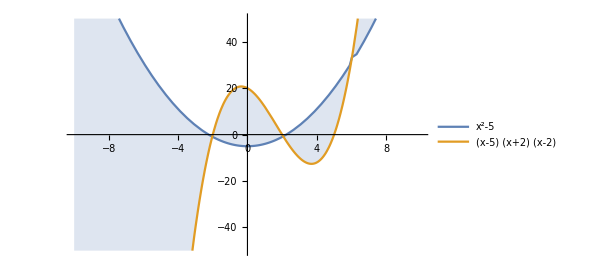
```mathematica
(*-Graphics-*)
```

#### area between curves

```mathematica
AreaBetweenCurves::usage="AreaBetweenCurves[{equation1,equation2},{variable,xmin,xmax}]"
```

AreaBetweenCurves[{equation1,equation2},{variable,xmin,xmax}]

```mathematica
ClearAll[AreaBetweenCurves];
AreaBetweenCurves[ args___ ] :=
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`AreaBetweenCurves" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`AreaBetweenCurves" ]
    ];
(*AreaBetweenCurves[{x^2,x},{x,0,5}]*)
```

#### Area Between curves integral

```mathematica
AreaBetweenCurvesIntegral // ClearAll;
AreaBetweenCurvesIntegral[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`AreaBetweenCurvesIntegral" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`AreaBetweenCurvesIntegral" ]
    ];
(*AreaBetweenCurvesIntegral[{x^2,x},{x,0,5}]*)
```

```mathematica
(*AreaBetweenCurvesIntegral[{x^2,x},{x,0,5}]*)
```

#### integral approximation plot

```mathematica
IntegralApproximationPlot::usage="IntegralApproximationPlot[equation_no_y,{variable,xmin,xmax},Left_or_Right_as_string,{Regular_with_str,number_of_rect}]"
```

IntegralApproximationPlot[equation_no_y,{variable,xmin,xmax},Left_or_Right_as_string,{Regular_with_str,number_of_rect}]

```mathematica
(*-Graphics-*)
```

```mathematica
(*IntegralApproximationPlot[Sin[x^2],{x,0,π},"Left",{"Regular",20}]*)
```

```mathematica
IntegralApproximationPlot[fun_,{x_,x0_,x1_},method_,partition_,opts___?OptionQ]:=Module[{exact,npartition,temp},
exact="Exact"/.{opts}/.Options[IntegralApproximationPlot];
If[exact && StringMatchQ[ToString[First[partition]],"Maxdx"],Return[Message[PIA::exact]]];
If[VectorQ[partition,NumericQ]&&Length[partition]>1,
If[MatchQ[partition,{}],Return[Message[PIA::emptypartition]]];
npartition=Sort[Union[partition,SameTest->(N[#1]==N[#2]&)],(OrderedQ[{N[#1],N[#2]}]&)];
If[Not[MatchQ[npartition,partition]],Message[PIA::notordered,npartition]];
If[x0>First[npartition]||Last[npartition]>x1,Message[PIA::notpartition,x0,x1];npartition=Select[npartition,x0≤#≤x1&]];
If[Not[MemberQ[N[npartition],N[x0]]],temp=Flatten[{x0,npartition}],temp=npartition];
If[Not[MemberQ[N[temp],N[x1]]],temp=Flatten[{temp,x1}]];
If[MatchQ[temp,npartition],npartition=temp,Message[PIA::points,temp];npartition=temp]];
If[MatchQ[Head[Total[npartition]],Real],Return[Message[PIA::exact]]];

Switch[ToString[method],
"Upper",  Which[
               VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, max, Flatten[npartition], opts],
               StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},max,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},max,Random,opts],
              True,
	         Return[Message[PIA::partition]]],

      "Lower",  Which[
               VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, min, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},min,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},min,Random,opts],
              True,
	         Return[Message[PIA::partition]]],


"Right",Which[
    VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, right, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},right,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},right,Random,opts],
              True,
	         Return[Message[PIA::partition]]],


"Left",Which[
    VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, left, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},left,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},left,Random,opts],
              True,
	         Return[Message[PIA::partition]]],



"Midpoint",Which[
    VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, midpt, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},midpt,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},midpt,Random,opts],
              True,
	         Return[Message[PIA::partition]]],

  
"Trap",Which[
    VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, trap, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},trap,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},trap,Random,opts],
              True,
	         Return[Message[PIA::partition]]],


"Simpson",
If[StringMatchQ[ToString[First[partition]],"Regular"]&&EvenQ[Last[partition]],
	LUSumPlot[fun,{x,x0,x1,Last[partition]},simp,"Regular",opts],Return[Message[SimpApprox::even]]],

"Riemann",Which[
    VectorQ[npartition],
	          LUSumPlot[fun,{x,x0,x1}, riem, Flatten[npartition], opts],
                StringMatchQ[ToString[First[partition]],"Regular"],  
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},riem,"Regular",opts],
               StringMatchQ[ToString[First[partition]],"Maxdx"],
	         LUSumPlot[fun,{x,x0,x1,Last[partition],1},riem,Random,opts],
              True,
	         Return[Message[PIA::partition]]],
True,
	Return[Message[PIA::partition]]]];

LUSumPlot[fun_,{x_,x0_,x1_,n_:1,m_:2},lu_,regular_,opts___?OptionQ]:=Block[{nx0,nx1,f,graph,astyle,polystyle,esum,frame,print,dx=n/2,basepts,range,funvalues,baseintervals,lengths,maxlength,sumvalues,sum,list,list1,list2,list3,linedata,stylelinedata,pointdata,polypts,ptstyle,plotrange,plotfun,axesorigin,minval,maxval,midpt,riem,simp,max,min,right,left,trap},
If[Head[fun]===List&&Length[fun]>1,Return[Message[lusumplot::input,fun]]];
{graph,polystyle,esum,frame,print}={"DrawGraph","PolyStyle","Exact",Frame,"PrintDisplay"}/.{opts}/.Options[LUSumPlot];
If[esum&&lu=!=reim,{nx0,nx1}={x0,x1},{nx0,nx1}=N[{x0,x1}]];
f:=Function[x,fun];

If[regular==="Regular" ,
If[esum,dx=(x1-x0)/n,dx=N[(x1-x0)/n]];
basepts=Range[nx0,nx1,dx];

Which[
lu===midpt,
   range=Drop[basepts+dx/2,-1];
   funvalues=Map[f,range],
lu===riem,
   range=Partition[basepts,2,1];
   funvalues=Map[f,Map[Random[Real,N[#]]&,range]],
lu===simp,
    range=Partition[basepts,3,2];
    funvalues=Map[f,basepts],
lu===max,
   range=Partition[basepts,2,1];
   maxval=If[esum,MaxValue,NMaxValue];
funvalues= Map[maxval[{f[x],#[[1]]≤x≤#[[2]]}, x, FilterRules[{opts},Options[NMaxValue]]//Evaluate]&,range],
lu===min,
  range=Partition[basepts,2,1];
  minval=If[esum,MinValue,NMinValue];
funvalues=Map[minval[{f[x],#[[1]]≤x≤#[[2]]}, x,FilterRules[{opts},Options[NMaxValue]]//Evaluate]&, range],
True,
   range=Range[nx0,nx1,dx/m];
   funvalues=Map[f,range]],
(*************Non-regular partitions*************)
If[esum, dx=(x1-x0)/n];
If[lu===simp&&EvenQ[Length[regular]],Return[Message[SimpApprox::even]]];
basepts=If[Head[regular]===List,regular,Join[{nx0},Map[Random[Real,N[#]]&,Partition[Range[nx0,nx1,dx],2,1]],{nx1}]];
baseintervals=Partition[basepts,2,1];
lengths=Map[-Apply[Subtract,#]&,baseintervals];
maxlength=Max[lengths];

Switch[lu,
midpt,
  range=Map[Apply[Plus,#]&,baseintervals]/2;
  funvalues=Map[f,range],
riem,
  funvalues=Map[f,Map[Random[Real,N[#]]&,baseintervals]],
max,   funvalues=Map[NMaxValue[{f[x],#[[1]]≤x≤#[[2]]},x,WorkingPrecision->$MachinePrecision,FilterRules[{opts},Options[NMaxValue]]//Evaluate]&,baseintervals],min,  funvalues=Map[NMinValue[{f[x],#[[1]]≤x≤#[[2]]},x,WorkingPrecision->$MachinePrecision,FilterRules[{opts},Options[NMaxValue]]//Evaluate]&,baseintervals],

right|left|trap,
  funvalues=Map[f,basepts],
simp,
  range=Partition[basepts,3,2];
  funvalues=Map[f,basepts],
True,  
range=Join[Map[Drop[Range[Apply[Sequence,#],-Apply[Subtract,#]/m],-1]&,baseintervals],{x1}]//Flatten;
funvalues=Map[f,range]]];

(*Test for singularities*)

If[Not[VectorQ[funvalues,NumberQ[N[#]]&]],Return@Message[lusumplot::impint]];
Which[
lu===simp,
  sumvalues=Partition[funvalues,m+1,m];
  funvalues=Partition[Transpose[{Flatten[range],Flatten[sumvalues]}],3],
lu===trap,
  sumvalues=If[regular=!="Regular",
Drop[funvalues+RotateLeft[funvalues],-1]/2,{funvalues,-{Last[funvalues],First[funvalues]}/2}//Flatten],
lu===left,
  sumvalues=funvalues=Drop[funvalues,-1],
lu===right,
  sumvalues=funvalues=Drop[funvalues,1],
True,
  sumvalues=funvalues];
sum=Which[
regular=!="Regular",sumvalues.lengths,
lu===trap,Apply[Plus,sumvalues] dx,
lu===simp,Apply[Plus,sumvalues.{1,4,1}] dx/3,
True,Apply[Plus,sumvalues] dx];
If[regular=!="Regular"&&print,Print["Max Deltax = ",maxlength]];
If[graph,If[esum,Print[sum]],Return@sum];

(*Prepare plot*)

plotrange=PlotRange/.{opts}/.PlotRange->All;
plotrange=(plotrange/.Automatic->All);
ptstyle= "PointStyle" /. {opts} /. Options[LUSumPlot]; 
plotfun=Plot[f[x],{x,nx0,nx1},Sequence@@FilterRules[{opts},Options[Plot]]//Evaluate,PlotRange->plotrange];
astyle=FillingStyle/.{opts}/.Options[LUSumPlot];
Which[lu===trap,list1=Map[{#,0}&,Drop[basepts,-1]];
list2=Transpose[{Drop[basepts,-1],Drop[funvalues,-1]}];
list3=Transpose[{Drop[basepts,1],Drop[funvalues,1]}];
polypts=Join[Flatten[Transpose[{list1,list2,list3}],1],{{Last[basepts],0},{First[basepts],0}}],lu===simp,list1=Map[InterpolatingPolynomial[#,x]&,funvalues];
list2=Map[{x,#[[1]],#[[3]]}&,range];
linedata=Replace[Drop[#,{2}]&/@funvalues,{a_,b_}->Line[{{a,b},{a,0}}],{2}];
polypts=MapThread[Plot[#1,#2,Axes->None,AxesOrigin->{0,0},Filling->Axis,FillingStyle->astyle,PlotStyle->polystyle,Sequence@@FilterRules[{opts},Options[Plot]]//Evaluate,Epilog->Join[Flatten[{ptstyle,Point/@funvalues}],Flatten[{Dashing[Tiny],linedata}]]]&,{list1,list2}],True,list1=Map[{#,0}&,Drop[basepts,-1]];
list2=Transpose[{Drop[basepts,-1],funvalues}];
list3=Transpose[{Drop[basepts,1],funvalues}];
polypts=Join[Flatten[Transpose[{list1,list2,list3}],1],{{Last[basepts],0},{First[basepts],0}}]];

If[lu=!=simp,Show[plotfun,Graphics[{Flatten[{Opacity[.5],EdgeForm[Thin],astyle,Polygon[polypts]}]}],Sequence@@FilterRules[{opts},Options[Graphics]],AxesOrigin->{Automatic,0},PlotLabel->If[esum||Not[print],None,StringForm["Area"]≃N[sum]]],Show[polypts,plotfun,Sequence@@FilterRules[{opts},Options[Graphics]],PlotRange->All,Axes->Automatic,AspectRatio->1/GoldenRatio,AxesOrigin->Automatic,PlotLabel->If[esum||Not[print],None,StringForm["Area"]≃N[sum]]]]];


Options[IntegralApproximationPlot]=Options[LUSumPlot]={"DrawGraph"->True, "Exact"->False,"PointStyle"->{GrayLevel[0],AbsolutePointSize[4]},"PolyStyle"->RGBColor[.3,.5,.7],"PrintDisplay"->True,FillingStyle->Directive[{Opacity[0.2],Hue[0.6,0.6,0.6]}],WorkingPrecision->MachinePrecision};

SimpApprox::even="Simpson's approximation requires a regular partition with an even number of subintervals. Random partitions generated by MaxDeltax[dx] are not accepted. ";

PIA::type="Specity an approximation method and partition. Possible values for method are: Upper, Lower, Right, Left, Midpoint, Trap, Riemann, Simpson. Possible settings for the partition are {Regular,n}, n a positive integer, {Maxdx,dx}, dx a positive real number, or an ordered list of points determining a partition of the interval. ";

PIA::points="The partition is missing one or both of the endpoints of the interval or has one or more repeated points. The missing endpoints will be added to the partition, and the new partition is `1`. ";

PIA::partition="Possible settings for the partition are {Regular,n}, n a positive integer, {Maxdx,dx}, dx a positive real number, or a list of points determining a partition of the interval. ";

PIA::notordered= "The x coordinates of the data are not ordered or the data contained repeated points. The ordered data is `1`. ";

PIA::notpartition="One or more of the points in the partition are not between `1` and `2`. These points have been excluded from the partition. ";

PIA::emptypartition="A partition must be a non-empty ordered list of points in the interval. ";

PIA:: exact=
"The option Exact does not apply to partitions using approximate real numbers. ";

lusumplot::impint="Improper Integral";
```

#### Average Value

```mathematica
AverageValue::usage="AverageValue[equation_,{var_,xmin_,xmax_}]"
```

AverageValue[equation_,{var_,xmin_,xmax_}]

```mathematica
AverageValue[equation_,{var_:x,xmin_,xmax_}]:=1/(xmax-xmin)Integrate[equation,{var,xmin,xmax}]
```

#### AveragePiecewise

```mathematica
AveragePiecewise::usage="AveragePiecewise[{x1_,y1_},{x2_,y2_},{x3_,y3_}]"
```

AveragePiecewise[{x1_,y1_},{x2_,y2_},{x3_,y3_}]

```mathematica
AveragePiecewise[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Module[
{eq1=QuietEcho@LinearLine[{x1,y1},{x2,y2}],
eq2=QuietEcho@LinearLine[{x2,y2},{x3,y3}]
},1/(x3-x1)Integrate[Piecewise[{{eq1,x1<=x<=x2},{eq2,x2<=x<=x3}}],{x,x1,x3},Assumptions->Variables[{{x1,y1},{x2,y2},{x3,y3}}][[1]]>0]

]
```

#### VolumeRotate

```mathematica
VolumeRotate::usage="VolumeRotate[func,{var,x1,x2},axis]"
```

VolumeRotate[func,{var,x1,x2},axis]

```mathematica
VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@Which[

funcvar===a===axis,(*x,x,x*)
Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis,

(funcvar===axis)&&axis=!=a,(*x,y,x*)
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis],

(a==axis)&&a=!=funcvar,(*x,y,y*)
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],

(funcvar===a)&&a=!=axis,(*x,x,y*)
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
y111=function/. a->a1;
y222=function/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
]
]
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_]:=Block[{y111,y222,inverse,funcvar=DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]},Echo[funcvar];Activate@Echo[
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[ " Vertical ",Red,Bold],"axis"}]];
If[FreeQ[function,axis],
inverse=Echo[Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]]];Inactivate[π∫_a1^a2 inverse^2 ⅆaxis],
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,a,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,a,Assumptions->a1<=a<=a2]];
Inactivate[π∫_y111^y222 inverse^2 ⅆaxis]
],

Print[Row[{"volume around",Style[ " Horizontal ",Red,Bold],"axis"}]];Inactivate[π∫_a1^a2 (function)^2 ⅆaxis]]]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse,final,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];Activate@Echo@Inactivate[π∫_a1^a2 inverse^2 ⅆaxis];π∫_a1^a2 inverse^2 ⅆaxis,
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
Activate@Echo@Inactivate[π∫_y111^y222 inverse^2 ⅆaxis]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse,final,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse=Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];Activate@Echo@Inactivate[π∫_a1^a2 #^2 ⅆaxis]&/@inverse;π∫_a1^a2 inverse^2 ⅆaxis,
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
If[Length[inverse]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse^2 ⅆaxis],Echo[inverse,"two possible inverse functions"];π∫_y111^y222 #^2 ⅆaxis&/@{inverse}]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],
y111=function/. a->a1;
y222=function/. a->a2;inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],Print[hi3];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],Print[hi2];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];y111=inverse123/. a->a1;
y222=inverse123/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],If[FreeQ[a,funcvar],Print[hi1];
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis]
,Print[hi];
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@Which[

FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];

If[Not@FreeQ[a,axis],Print[hi3];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],

Print[hi2];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];y111=inverse123/. a->a1;
y222=inverse123/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],

If[FreeQ[a,funcvar],Print[hi1];
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis]
,

Print[hi];Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]

]]*)
```

#### Eula

```mathematica
Eula::usage="Eula[dpdt,{t,p},step,iter]";
```

```mathematica
Eula2::usage="Eula2[dpdt,{t,p},step,iter]";
```

```mathematica
Eula[func_,inti:{_?NumericQ,_?NumericQ},step:_?NumericQ,iter:_?NumericQ,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];TableForm[Join[{{"Iter",ToString[var1],ToString[var2]}},{{0,inti[[1]],inti[[2]]}},Transpose@Join[{Range[iter]},
Transpose[Reap[Do[y=y+step Function[{var1,var2},func][x,y];x=x+step;Sow[{x,y}],iter]][[2]][[1]]]]]]]
```

```mathematica
Eula2[func_,inti:{_,_},step_,iter_,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];TableForm[Join[{{"Iter",ToString[var1],ToString[var2]}},{{0,inti[[1]],inti[[2]]}},Transpose@Join[{Range[iter]},
Transpose[Reap[Do[y=y+step Function[{var1,var2},func][x,y];x=x+step;Sow[{x,y}],iter]][[2]][[1]]]]]]]
```

```mathematica
EulaOutput::usage="EulaOutput[func,{t,p},step,iter]";
```

```mathematica
EulaOutput[func_,inti:{_?NumericQ,_?NumericQ},step:_?NumericQ,iter:_?NumericQ,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];
Do[y=y+step Function[{var1,var2},func][x,y];x=x+step,iter];y]
```

## Tests

#### TruthTable

```mathematica
TruthTable::usage="TruthTable[statements,vars]"
```

TruthTable[statements,vars]

```mathematica
TruthTable // ClearAll;
TruthTable // Attributes = {};
TruthTable[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`TruthTable" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`TruthTable" ]
    ];
```

```mathematica
(*-Graphics--Graphics-*)
```

#### EnsureFtest

```mathematica
FTestEnsure::usage="FTestEnsure[equation_,{statementslist},variableinequation_,functionletter_,{optionalvaluetestmin,max}]";
```

```mathematica
FTestEnsure[equation_,{statement__},variable_,function_,valuetest__:{-5.923,4.32}]:=Do[Echo[FTest[equation,{statement},variable,function],{x,y}],{x,valuetest},{y,valuetest}]
```

#### RFtest

```mathematica
SetAttributes[RFTest, HoldAllComplete]
Options[RFTest] = {"Assumptions" -> {}};

InternalTest[exp_, cond_, var_, func_, asum_] :=
    Module[{solution,sss},	
     sss := Function[var,exp];
	solution = FullSimplify[ReleaseHold[cond]/.{func->sss},Assumptions ->asum];
	solution
    ]
    
SetAttributes[InternalTest, HoldAllComplete]
```

```mathematica
RFTest[exps_,cond_,var_,func_,opts:OptionsPattern[]]:=
	Module[{sols,funcs},
	funcs = If[Head@exps===List,exps,{exps}];
	Table[If[InternalTest[funcs[[i]]//Evaluate,cond,var,func,OptionValue["Assumptions"]]===True,Style[StringForm["`` DOES satisfy condition",funcs[[i]]],Red,Bold],StringForm["`` DOES NOT satisfy condition",funcs[[i]]]],{i,1,Length[funcs]}]//TableForm
	]
```

```mathematica
SetAttributes[FTest,HoldAllComplete];
Options[FTest] = {"Assumptions"->{}};

FTest[exp_,equations_,var_,func_,opts:OptionsPattern[]]:=
	Module[{solutions,f,eq,asum},
	asum = OptionValue["Assumptions"]//ReleaseHold;
	ClearAll[func];
	eq = If[Head@equations =!= List,{equations},equations];
	
	solutions = Table[func:=Function[var,exp];If[FullSimplify[ReleaseHold[eq[[i]]],Assumptions->asum]===True,ClearAll[func];Style[StringForm["`` is True",eq[[i]]],Red,Bold],ClearAll[func];StringForm["`` is False",eq[[i]]]],{i,1,Length[eq]}];
	ClearAll[func];
	TableForm[solutions]
	]
```

```mathematica
FTest::usage="FTest[equation_,{statementslist},variableinequation_,functionletter_,Assumptions->{}]
FTest[Log[x],{h[a]+h[b]==h[a*b]},x,h,Assumptions->{a>0,b>0}] test one equation";
RFTest::usage="RFTest[{equationlist},statement,variableinequation_,functionletter_]
RFTest[{12x,12x^2},g[a]==g[-a],x,g],  tests one function";
```

```mathematica
(*RFTest[{12x,12x^2},g[a]==g[-a],x,g]*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

#### equation forms

```mathematica
EquationForms[e_]:=
Grid[{{"Methods","normal","Traditional form"},
{"Expand",Expand[e],TraditionalForm[Expand[e]]},
{"simplify",Simplify[e],TraditionalForm[Simplify[e]]},
{"apart",Apart[e],TraditionalForm[Apart[e]]},
{"together",Together[e],TraditionalForm[Together[e]]},
{"FullSimplify",FullSimplify[e],TraditionalForm[FullSimplify[e]]},
{"expand",Expand[e],TraditionalForm[Expand[e]]},
{"FunctionExpand",FunctionExpand[e],TraditionalForm[FunctionExpand[e]]},
{"ComplexExpandREIM",ComplexExpand[e,TargetFunctions->{Re, Im}],TraditionalForm[ComplexExpand[e,TargetFunctions->{Re, Im}]]},
{"ComplexExpandAbsArg",ComplexExpand[e,TargetFunctions->{Abs, Arg}],TraditionalForm[ComplexExpand[e,TargetFunctions->{Abs, Arg}]]},
{"ComplexExpandConj",ComplexExpand[e,TargetFunctions->Conjugate],TraditionalForm[ComplexExpand[e,TargetFunctions->Conjugate]]},
{"FactorExtension",Factor[e,Extension->I],TraditionalForm[Factor[e,Extension->I]]},
{"ApartSquareFree",ApartSquareFree[e],TraditionalForm[ApartSquareFree[e]]},
{"factor list",FactorList[e],FactorList[e]},
{"Factor",Factor[e],TraditionalForm[Factor[e]]},
{"decompose",Decompose[e,x],TraditionalForm[Decompose[e,x]]},
{"cancel",Cancel[e],TraditionalForm[Cancel[e]]},
{"expandall",ExpandAll[e],TraditionalForm[ExpandAll[e]]},
{"expandall simplify",Simplify[ExpandAll[e]],TraditionalForm[Simplify[ExpandAll[e]]]},
{"expandall Fullsimplify",FullSimplify[ExpandAll[e]],TraditionalForm[FullSimplify[ExpandAll[e]]]},
{"Collect",Collect[e,x],TraditionalForm[Collect[e,x]]},
{"trigexpand",TrigExpand[e],TraditionalForm[TrigExpand[e]]},
{"trigfactor",TrigFactor[e],TraditionalForm[TrigFactor[e]]},
{"Trigtoep",TrigToExp[e],TraditionalForm[TrigToExp[e]]},
{"ExpToTrig",ExpToTrig[e],TraditionalForm[ExpToTrig[e]]},
{"functionexpand",FunctionExpand[e],TraditionalForm[FunctionExpand[e]]},
{"complexexpand",ComplexExpand[e],TraditionalForm[ComplexExpand[e]]},
{"PowerExpand",PowerExpand[e],TraditionalForm[PowerExpand[e]]}
},
Frame->All]
```

#### composite function test

```mathematica
compositetest::usage="compositetest[function1_letter,function2_letter]";
```

```mathematica
compositetest[function1_,function2_]:=Module[{range2,domain1,letter1,letter2,bolen},
range2=Which[TrueQ[FunctionRange[function2[y],y,x]]==True,Reals,1==1,FunctionRange[function2[y],y,x]];
domain1=Which[TrueQ[FunctionDomain[function1[x],x]]==True,Reals,1==1,FunctionDomain[function1[x],x]];
letter1=ToString[function1];
letter2=ToString[function2];
bolen=SubsetQ[range2,domain1];
Print[Row[{
"For ",letter1,"[",letter2,"[","x","]","]"," To exist: \n
Range of ",letter2," ⊆ ","Domain of ",letter1,"\n",
"Range of ",letter2,":",FunctionRange[function2[x],x,y],"\n",
"Domain of ",letter1,":",domain1,"\n
This is ",bolen
}]]]
```

```mathematica
(*compositetest[f,g]*)
```

#### One To One

```mathematica
InverseFunctionTest::usage="Onetoone[equation_,{domainlist_interval_notation}]";
```

```mathematica
InverseFunctionTest[equation_,domainlist__]:=Column[If[FunctionInjective[{equation,#[[1]]},x],Style[{Sequence@@#,True},RGBColor[0.,0.78,0.07],Bold],{Sequence@@#,False}]&/@Map[{#}&,domainlist],Frame->All]
```

### Discriminant

#### my discriminant

```mathematica
mydiscriminant[equation_,variable_]:=Module[{a,b,c},a=Coefficient[equation,variable,2];b=Coefficient[equation,variable,1];c=Coefficient[equation,variable,0];b^2-4(a)(c)]
```

#### cubic discriminant

```mathematica
CubicDiscriminant[equation_]:=Module[{discriminant,xint,yint},discriminant=Discriminant[equation,x];
xint=Solve[equation==0,x];
yint=equation/.xint;
Print[DeleteDuplicates[Transpose[{x/.xint,yint}]]];
If[discriminant>0,Print["Three Roots"]];
If[discriminant==0,Print["1 repeated root/stationary point on x axis and may have other roots"]];
If[discriminant<0,Print["one non repeated root"]];]
```

#### Cubic Discriminant solve

```mathematica
CubicDiscriminantSolve::usage="CubicDiscriminantSolve[equation_,numberofintercepts,variable_]";
```

```mathematica
CubicDiscriminantSolve[equation_,amount_,variable_]:=Module[{discriminant,xint,yint},
discriminant=Discriminant[equation,x];
Echo[discriminant,"Discriminant: "];
If[amount=="Three",Echo[Reduce[discriminant>0,variable]]];
If[amount=="Repeated"(*Repeated root x^2*),Echo[Solve[discriminant==0,variable]]];
If[amount=="Non Repeated",Echo[Reduce[discriminant<0,variable]]]]
```

### simultaneous linear solutions

#### LinearSolutions

```mathematica
LinearSolutions::usage="LinearSolutions[equation1_with_y,equation2_,Infinite_None_One,variable_to_solve]";
```

```mathematica
LinearSolutions[equation1_,equation2_,statement_(*Infinite, None, One*),variable_]:=
Module[{e1,e2,ee1,ee2,gradient1,gradient2,yint1,yint2},
e1=Solve[equation1,y]/.y->yp;
e2=Solve[equation2,y];
ee1=yp/.e1;
ee2=y/.e2;
gradient1=Coefficient[ee1,x,1];
gradient2=Coefficient[ee2,x,1];
yint1=Coefficient[ee1,x,0];
yint2=Coefficient[ee2,x,0];
If[statement=="Infinite",Print["everything the same: " Solve[{gradient1==gradient2,yint1==yint2},variable]]];
If[statement=="None",Print[{"gradient same: "Solve[{gradient1==gradient2},variable],"Reject y int same: "Solve[{yint1==yint2},variable]}]];
If[statement=="One",Print[{"Reject same gradient: "Solve[{gradient1==gradient2},variable]}]]
]
```

```mathematica
(*LinearSolutions[3x+m y==5,(m+2)x+5 y==m,"Infinite",m]*)
```

```mathematica
LinearSolutionsPrint[3x+m y==5,(m+2)x+5 y==m,"Infinite",m]
```

LinearSolutionsPrint[3 x+m y==5,(2+m) x+5 y==m,Infinite,m]

#### LinearSolutionscheck

```mathematica
LinearSolutionsCheck::usage="LinearSolutionsCheck[equation1_with_y,equation2_]";
```

```mathematica
LinearSolutionsCheck[equation1_,equation2_]:=
Module[{e1,e2,ee1,ee2,gradient1,gradient2,yint1,yint2},
e1=Solve[equation1,y]/.y->yp;
e2=Solve[equation2,y];
ee1=yp/.e1;
ee2=y/.e2;
gradient1=Coefficient[ee1,x,1];
gradient2=Coefficient[ee2,x,1];
yint1=Coefficient[ee1,x,0];
yint2=Coefficient[ee2,x,0];
If[gradient1==gradient2&&yint1==yint2,Print["There are Infinite solutions"]];
If[gradient1!=gradient2&&yint1!=yint2,Print["There is one solution"]];
If[gradient1!=gradient2&&yint1==yint2,Print["There is one solution"]];
If[gradient1==gradient2&&yint1!=yint2,Print["There is no solutions"]];
]
```

```mathematica
(*LinearSolutions[y+1==2x+1,y==2x]*)
```

```mathematica
LinearSolutionsPrint[y+1==2x+1,y==2x]
```

LinearSolutionsPrint[1+y==1+2 x,y==2 x]

#### LinearSolutionsPrint

```mathematica
LinearSolutionsPrint::usage="LinearSolutionsPrint[equation1_with_y,equation2_,Infinite_None_One,variable_to_solve]";
```

```mathematica
LinearSolutionsPrint[equation1_,equation2_,statement_(*Infinite, None, One*),variable_]:=
Module[{e1,e2,ee1,ee2,gradient1,gradient2,yint1,yint2},
e1=Solve[equation1,y]/.y->yp;
e2=Solve[equation2,y];
ee1=yp/.e1;
ee2=y/.e2;
gradient1=Coefficient[ee1,x,1];
gradient2=Coefficient[ee2,x,1];
yint1=Coefficient[ee1,x,0];
yint2=Coefficient[ee2,x,0];
If[statement=="Infinite",Print["everything same: "Solve[{gradient1==gradient2,yint1==yint2},variable]]];
If[statement=="None",Print["gradient the same: "{Solve[{gradient1==gradient2},variable],"Reject y int same: "Solve[{yint1==yint2},variable]}]];
If[statement=="One",Print[{"Reject gradient same: "Solve[{gradient1==gradient2},variable]}]]
;Grid[{{"e1",ee1}
,{"e2",ee2},
{"gradient 1",gradient1},
{"gradient 2",gradient2},
{"yint1",yint1},
{"yint2",yint2}
},Frame->All]]
```

```mathematica
(*-Graphics-*)
(*
set equations equal to y
find gradients (or derivative)
equate gradients
equate y-intercepts

one solution: gradient different, y intercepts same
 no solutions: gradient same, y intercepts different
 infinite solutions: gradients same, y intercepts same
*)
```

## Trigonometry

### Cos Sin rule

#### image

```mathematica
(*-Graphics-*)
```

#### equation

```mathematica
(*CosRule:=Module[{a,b,angle},
a=Input["side a"];
b=Input[{"side of b"}];
angle=Input[{"Angle between a and b"}];
Simplify[√(a^2+b^2-2*a*b*Cos[angle Degree])]]*)
```

```mathematica
(*cos rule*) √(a^2+b^2-2*a*b*Cos[θ]);
```

```mathematica
(*sinrule*)Sin[θ]/c==Sin[β]/b==Sin[α]/a;
```

#### SolveTriangle

```mathematica
(*SolveTriangle[{12,b,c},{A,59,73}]//N
{{A->48.,b->13.841188494877352,c->15.442019749225185}}*)
```

```mathematica
(*-Graphics-*)
```

### coordinate geometry

#### triangle area coordinate geometry

```mathematica
trianglearea::usage="trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]"
```

trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]

```mathematica
trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]:=1/2(x1(y2-y3)+x2(y3-y1)+x3(y1-y2))
```

```mathematica
(*trianglearea[-7,-1,5,5,7,16]*)
```

### tables

#### trig

```mathematica
trig[equation_]:=Grid[{#,TrigonometricPropertiesNormal[equation,x,y,#]}&/@{"Period","Amplitude","MinValue","MaxValue","Midline"},Frame->All]
```

#### trigtable

```mathematica
TrigTable::usage="TrigTable[equation_,min_,max_]"
```

TrigTable[equation_,min_,max_]

```mathematica
TrigTable[equation_,range1_,range2_]:=Module[{xvalues,listnew={},justvalues={},listnew2={},list1,list2,numbers={},finallist,poo},xvalues=Echo[SolveValues[equation==0,x],"x = 0 when: "];If[Length[xvalues]==2,list1=Extract[xvalues,1];list2=Extract[xvalues,2];poo=False,list1=Extract[xvalues,1];poo=True];Do[AppendTo[listnew,{n,list1/.C[1]->n}];AppendTo[justvalues,{list1/.C[1]->n}],{n,range1,range2}];If[poo==False,Do[AppendTo[listnew2,{n,list2/.C[1]->n}];AppendTo[justvalues,{list2/.C[1]->n}],{n,range1,range2}],Continue];finallist=Flatten[GatherBy[Flatten[{listnew,listnew2},1],First],1];Print[Grid[finallist,Frame->All]];Sort[Flatten[justvalues],Less]]
```

```mathematica
TrigTableComplex::usage="TrigTableComplex[equation_,xvaluesolutions_from_solve_,min_,max_]"
```

TrigTableComplex[equation_,xvaluesolutions_from_solve_,min_,max_]

```mathematica
TrigTableComplex[equation_,xvalueinput_,range1_,range2_]:=Module[{xvalues,listnew={},justvalues={},listnew2={},list1,list2,numbers={},finallist,poo},xvalues=Echo[xvalueinput,"x = 0 when: "];If[Length[xvalues]==2,list1=Extract[xvalues,1];list2=Extract[xvalues,2];poo=False,list1=Extract[xvalues,1];poo=True];Do[AppendTo[listnew,{n,list1/.C[1]->n}];AppendTo[justvalues,{list1/.C[1]->n}],{n,range1,range2}];If[poo==False,Do[AppendTo[listnew2,{n,list2/.C[1]->n}];AppendTo[justvalues,{list2/.C[1]->n}],{n,range1,range2}],Continue];finallist=Flatten[GatherBy[Flatten[{listnew,listnew2},1],First],1];Print[Grid[finallist,Frame->All]];Sort[Flatten[justvalues],Less]]
```

```mathematica
(*TrigTable[Sin[x],-5,10]*)
(*TrigTableComplex[Sin[x],{ConditionalExpression[2 π C[1], C[1]∈Integers],ConditionalExpression[π+2 π C[1], C[1]∈Integers]},0,5]*)
```

### trignometry

```mathematica
(*use reduce to find general solutions with complex equations*)
```

-Graphics-

-Graphics-

## probability

#### TransformedDist

```mathematica
TransformedDist::usage="TransformedDist[eq_,dists_]"
```

TransformedDist[eq_,dists_]

```mathematica
TransformedDist[eq_,dists_]:=Module[{through,list},
Which[NumericQ[eq]||Length[Variables[eq]]===1,Echo["Normal[nμ,n^(1/2)σ]"];List@@EchoEvaluation[NormalDistribution[eq dists[[1]],(eq (dists[[2]])^2)^(1/2) ]],

Length@Flatten[dists]===2,
Echo["Normal[μ(a_1+a_(2  ...)),σ(a_1^2+(a_2^2)_(...))^(1/2)]"];
List@@Echo[TransformedDistribution[eq,#\[Distributed]NormalDistribution[dists[[1]],dists[[2]]]&/@Variables[eq]]],True,
Echo["Normal[μ_1a_1+μ_2a_(2  ...)),(σ_1^2 a_1^2+σ_2^2(a_2^2)_(...))^(1/2)]"];
list=Map[through,dists];through[{x_,y_,z_}]:=x\[Distributed]NormalDistribution[y,z];List@@Echo[TransformedDistribution[eq,list]]
]
]
```

#### ConfidenceSolve

```mathematica
Options[ConfidenceSolve]={mean->μ,sd->σ,n->n,c->c,z->z}
```

{mean→μ,sd→σ,n→n,c→c,z→z}

```mathematica
ConfidenceSolve::usage="ConfidenceSolve[{mean,sd,n,z,c1,c2,c}]";
```

```mathematica
ConfidenceSolve[opts:OptionsPattern[]]:=Solve[If[Lookup[Association@opts,c]===c,{mean-z sd/n^(1/2)==c1,mean+z sd/n^(1/2)==c2}/.opts,{mean-Confidence[c] sd/n^(1/2)==c1,mean+Confidence[c] sd/n^(1/2)==c2}/.opts]]
```

#### CriticalInterval

```mathematica
CriticalInterval::usage="CriticalInterval[samplesize,H_0,sd,decimallevelsiginificance]"
```

CriticalInterval[samplesize,H_0,sd,decimallevelsiginificance]

```mathematica
CriticalInterval[n_,mean_,sd_,level_]:={NSolveValues[NormalDist[x<a,mean,sd/n^(1/2)]==level/2,a,Reals],NSolveValues[NormalDist[x>a,mean,sd/n^(1/2)]==level/2,a,Reals]}//Flatten
```

#### PDFMeanSD

```mathematica
PDFMeanSD::usage="PDFMeanSD[func_,{var_,min_,max_}]";
```

```mathematica
NPDFMeanSD::usage="NPDFMeanSD[func_,{var_,min_,max_}]";
```

```mathematica
PDFMeanSD[func_,{var_,min_,max_}]:=Module[{mean=Integrate[var func,{var,min,max}],SD},SD=(Integrate[var^2 func,{var,min,max}]-mean^2)^(1/2);Echo[Row[{"E[",var,"] :","∫_min^max xf[x] ⅆx" }]];Echo[Row[{"σ : ","(∫_min^max x^2 f[x] ⅆx -(∫_min^max xf[x] ⅆx)^2)^(1/2)=(∫_min^max x^2 f[x] ⅆx -μ^2)^(1/2)" }]];NormalDistribution[mean,SD]]
```

```mathematica
NPDFMeanSD[func_,{var_,min_,max_}]:=Module[{mean=NIntegrate[var func,{var,min,max}],SD},SD=(NIntegrate[var^2 func,{var,min,max}]-mean^2)^(1/2);Echo[Row[{"E[",var,"] :","∫_min^max xf[x] ⅆx" }]];Echo[Row[{"σ : ","(∫_min^max x^2 f[x] ⅆx -(∫_min^max xf[x] ⅆx)^2)^(1/2)=(∫_min^max x^2 f[x] ⅆx -μ^2)^(1/2)" }]];NormalDistribution[mean,SD]]
```

#### probability multiple

```mathematica
ProbabilityMultiple::usage="ProbabilityMultiple[func_,ranvar1_,prob1_,ranvar2_,prob2_]"
```

ProbabilityMultiple[func_,ranvar1_,prob1_,ranvar2_,prob2_]

```mathematica
ProbabilityMultiple[func_,ranvar1_,prob1_,ranvar2_,prob2_,var1_:x,var2_:y]:=Module[{trans1=Transpose[{ranvar1,prob1}],trans2=Transpose[{ranvar2,prob2}],list,var,list2=Association[{}],list0},list0=Flatten[Table[{n,m},{n,trans1},{m,trans2}],1];list=Echo@Sort[{Function[{var1,var2},func][#1[[1]],#1[[2]]],Times[Sequence@@(#2)]}&[Sequence@@Transpose[#]]&/@list0];While[Length[list]!=0,var=list[[1]]//First;If[ContainsAny[{list[[1]]//First},Keys[list2]],list2[list[[1]]//First]=list2[list[[1]]//First]+list[[1]][[2]],AppendTo[list2,var->list[[1]][[2]]]];list=Drop[list,1]];Grid[Transpose@KeyValueMap[Flatten[{##}]&]@list2,Frame->All]
]
```

#### Probability Cost

```mathematica
ProbabilityCost::usage="ProbabilityCost[equation_of_cost_respect_with_randvar,{weightlist},{randomvar_list}]";
```

```mathematica
ProbabilityCost[eq_,randlist_,problist_]:=Grid[Transpose@Prepend[Transpose[{randlist,eq/.Variables[eq][[1]]->#&/@randlist,problist}],{Variables[eq][[1]],"C","Pr(VAR=var)"}],Frame->All]
```

#### Shortcut Dist

```mathematica
BinomialDist::usage="BinomialDist[equation_,n_,p_]";
```

```mathematica
EmpiricalDist::usage="EmpiricalDist[equation_,weights_,random_]";
```

```mathematica
NormalDist::usage="NormalDist[equation_,μ_,σ_]";
```

```mathematica
ProbabilityDist::usage="ProbabilityDist[statement_,equation_,{var,xmin_,xmax_}]";
```

```mathematica
BinomialDist[equation_,n_,p_,var_:x]:=Probability[equation,var\[Distributed]BinomialDistribution[n,p]]
```

```mathematica
EmpiricalDist[equation_,weights_,random_,var_:x]:=Probability[equation,var\[Distributed]EmpiricalDistribution[weights->random]]
```

```mathematica
NormalDist[equation_,μ_,σ_,var_:x]:=Probability[equation,var\[Distributed]NormalDistribution[μ,σ]]
```

```mathematica
ProbabilityDist[statement_,equation_,{var_:x,xmin_,xmax_}]:=Probability[statement,var\[Distributed]ProbabilityDistribution[equation,{var,xmin,xmax}]]
```

```mathematica
Hypo[x_,n_,nsucc_,ntot_]:=Probability[x,X\[Distributed]HypergeometricDistribution[n,nsucc,ntot]]
```

```mathematica
NBinomialDist::usage="NBinomialDist[equation_,n_,p_]";
```

```mathematica
NEmpiricalDist::usage="NEmpiricalDist[equation_,weights_,random_]";
```

```mathematica
NNormalDist::usage="NNormalDist[equation_,μ_,σ_]";
```

```mathematica
NProbabilityDist::usage="NProbabilityDist[statement_,equation_,{var,xmin_,xmax_}]";
```

```mathematica
NBinomialDist[equation_,n_,p_,var_:x]:=NProbability[equation,var\[Distributed]BinomialDistribution[n,p]]
```

```mathematica
NEmpiricalDist[equation_,weights_,random_,var_:x]:=NProbability[equation,var\[Distributed]EmpiricalDistribution[weights->random]]
```

```mathematica
NNormalDist[equation_,μ_,σ_,var_:x]:=NProbability[equation,var\[Distributed]NormalDistribution[μ,σ]]
```

```mathematica
NProbabilityDist[statement_,equation_,{var_:x,xmin_,xmax_}]:=NProbability[statement,var\[Distributed]ProbabilityDistribution[equation,{var,xmin,xmax}]]
```

```mathematica
NHypo[x_,n_,nsucc_,ntot_]:=NProbability[x,X\[Distributed]HypergeometricDistribution[n,nsucc,ntot]]
```

#### KTable

```mathematica
KTable[top_:A,side_:B]:=TableForm[{{AB,PAB,B},
{APB,PAPB,PB},
{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]
```

```mathematica
(*KTableSolve[x_]:=Module[{},
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{"B","B'"},{"A","A'"}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]];
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{"B","B'"},{"A","A'"}}]/.Dispatch[Solve[{Total[{AB,PAB}]==B,Total[{APB,PAPB}]==PB,Total[{A,PA}]==1,Total[{AB,APB}]==A,Total[{PAB,PAPB}]==PA,Total[{B,PB}]==1}/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]]]];
TableForm[{{AB,PAB,B},
{APB,PAPB,PB},
{A,PA,1}},TableHeadings->{{"B","B'"},{"A","A'"}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]/.Dispatch[Solve[{Total[{AB,PAB}]==B,Total[{APB,PAPB}]==PB,Total[{A,PA}]==1,Total[{AB,APB}]==A,Total[{PAB,PAPB}]==PA,Total[{B,PB}]==1}/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]]]]*)
```

```mathematica
KTableSolve[x_,top_:A,side_:B]:=Module[{},
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]];
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.Dispatch[Solve[{Total[{AB,PAB}]==B,Total[{APB,PAPB}]==PB,Total[{A,PA}]==1,Total[{AB,APB}]==A,Total[{PAB,PAPB}]==PA,Total[{B,PB}]==1}/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]]]];
TableForm[{{AB,PAB,B},
{APB,PAPB,PB},
{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]/.Dispatch[Solve[{Total[{AB,PAB}]==B,Total[{APB,PAPB}]==PB,Total[{A,PA}]==1,Total[{AB,APB}]==A,Total[{PAB,PAPB}]==PA,Total[{B,PB}]==1}/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]]]]
```

```mathematica
KTableSolveIndependent[x_,top_:A,side_:B]:=Module[{a=Dispatch[Solve[{AB==A B,Total[{AB,PAB}]==B,Total[{APB,PAPB}]==PB,Total[{A,PA}]==1,Total[{AB,APB}]==A,Total[{PAB,PAPB}]==PA,Total[{B,PB}]==1}/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]]]},Print[a];
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]];
Print[TableForm[{{AB,PAB,B},{APB,PAPB,PB},{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.a];
TableForm[{{AB,PAB,B},
{APB,PAPB,PB},
{A,PA,1}},TableHeadings->{{ToString[side],ToString[side']},{ToString[top],ToString[top']}}]/.Thread[{AB,PAB,B,APB,PAPB,PB,A,PA,1}->Flatten[x]]/.a]
```

#### expected mean/value

```mathematica
Options[Expected]={Rationalize->True}
```

{Rationalize→True}

```mathematica
Expected::usage="Expected[{weight_or_probability_list},{randomvar_or_success_list},Rationalize->True]";
```

```mathematica
Expected[weights2_,randomvar2_,OptionsPattern[]]:=Module[{n=1,multiplied={},x,randomvar,weights},
If [OptionValue[Rationalize],
weights=Rationalize[weights2];randomvar=Rationalize[randomvar2],
weights=weights2;randomvar=randomvar2];
If[
N[Total[weights],100]=!=1.0,Print[Text[Style["WEIGHTS DON'T TOTAL TO 1.0",Red,Bold]]]
];
If [Length[weights]=!=Length[randomvar],Print[Text[Style["WEIGHT AND RANDVAR NOT SAME LENGTH",Red,Bold]]]];
Do[
AppendTo[multiplied,weights[[n]]*randomvar[[n]]];n++,Length[randomvar]
];
Print["Let X be random variable no. of {} "];
Print[
Grid[
{
Prepend[randomvar,"X"],
Prepend[weights,"Pr(X=x)"],
Prepend[multiplied,"x * Pr(X=x)"],
{"Expected mean manual",Total[multiplied],SpanFromLeft}
},Frame->All]
];
Echo[
Mean[EmpiricalDistribution[weights->randomvar]],
"Mean:"];
Echo[
Expectation[x,x\[Distributed]EmpiricalDistribution[weights->randomvar]],
"Expected value empirical expectation:"]
]
```

#### Expected mean gain

```mathematica
ExpectedGain::usage="ExpectedGain[equation_of_gain_respect_with_randvar,{weightlist},{randomvar_list}]";
```

```mathematica
ExpectedGain[equation_,weights_,randomvar_]:=Module[{p,t,equationfunction,multiplied={}},
p[v_]:=Module[{x},Probability[x==v,x\[Distributed]EmpiricalDistribution[weights->randomvar]]];
equationfunction[v_]:=ReplaceAll[Variables[equation][[1]]->v][equation];
If[Length[Variables[equation]]>1,Print[Text[Style["MULTIPLE VARIABLES IN EQUATION",Red, Bold]]]];
Do[AppendTo[multiplied,equationfunction[t]*p[t]],{t,randomvar}];
Print[Grid[{Prepend[randomvar,"x"],Prepend[weights,"Pr(X=x)"],Prepend[multiplied,Row[{ReplaceAll[Variables[equation][[1]]->x][equation], " * Pr(X=x)"}]]},Frame->All]];
Sum[equationfunction[t]*p[t],{t,randomvar}]
]
```

```mathematica
ExpectedGainComplex::usage="ExpectedGainComplex[equation_of_gain_respect_with_randvar,{weightlist},{randomvar_list},optionalvariable] for when multiple variables";
```

```mathematica
ExpectedGainComplex[equation_,weights_,randomvar_,var_:x]:=Module[{p,t,equationfunction,multiplied={}},
p[aaaa_]:=Module[{x},Probability[x==aaaa,x\[Distributed]EmpiricalDistribution[weights->randomvar]]];
equationfunction[aaaa_]:=ReplaceAll[var->aaaa][equation];
If[Length[Variables[equation]]>1,Print[Text[Style["MULTIPLE VARIABLES IN EQUATION",Red, Bold]]]];
Do[AppendTo[multiplied,equationfunction[t]*p[t]],{t,randomvar}];
Print[Grid[{Prepend[randomvar,"x"],Prepend[weights,"Pr(X=x)"],Prepend[multiplied,Row[{equation, " * Pr(X=x)"}]]},Frame->All]];
Sum[equationfunction[t]*p[t],{t,randomvar}]
]
```

#### variance

```mathematica
Options[variance]={Rationalize->True};
```

```mathematica
variance::usage="variance[{weight_or_probability_list},{randomvar_or_success_list},Rationalize->True]";
```

```mathematica
variance[weights2_,randomvar2_,OptionsPattern[]]:=Module[{n=1,t=1,multiplied={},multiplied2={},x,randomvar,weights,randomvar3,f,p,h},
If [OptionValue[Rationalize],
weights=Rationalize[weights2];randomvar=Rationalize[randomvar2],
weights=weights2;randomvar=randomvar2];randomvar3=randomvar^2;
If[
N[Total[weights],100]=!=1.0,Print[Text[Style["WEIGHTS DON'T TOTAL TO 1.0",Red,Bold]]]
];
If [Length[weights]=!=Length[randomvar],Print[Text[Style["WEIGHT AND RANDVAR NOT SAME LENGTH",Red,Bold]]]];
Do[
AppendTo[multiplied,weights[[n]]*randomvar[[n]]];n++,Length[randomvar]
];
Do[
AppendTo[multiplied2,weights[[t]]*randomvar3[[t]]];t++,Length[randomvar3]
];
Print["Let X be random variable no. of {} "];
Print[
Grid[
{Prepend[randomvar,"X"],
Prepend[weights,"Pr(X=x)"],
Prepend[multiplied,"x * Pr(X=x)"],
{"E[x] = Total[x * Pr(X=x)]",Total[multiplied],SpanFromLeft}
},Frame->All]
];
Echo[
Expectation[x,x\[Distributed]EmpiricalDistribution[weights->randomvar]],
"E[x]:"];
n=Thread[f[randomvar,weights]];
f[a_,b_]:=Row[{a," × "   ,b}];
Echo[(Total[n])^2,"(E[x])^2"];
Echo[
(Expectation[x,x\[Distributed]EmpiricalDistribution[weights->randomvar]])^2,
"(E[x])^2:"];
Print[
Grid[
{Prepend[randomvar3,"X^2"],
Prepend[weights,"Pr(X=x)"],
Prepend[multiplied2,"x^2 * Pr(X=x)"],
{"E[x^2] = Total[x^2 * Pr(X=x)]",Total[multiplied2],SpanFromLeft}
},Frame->All]
];
p=Thread[h[randomvar3,weights]];
h[a_,b_]:=Row[{a," × "   ,b}];
Echo[
Total[p],
"E[x^2]"];
Echo[
Expectation[x^2,x\[Distributed]EmpiricalDistribution[weights->randomvar]],
"E[x^2]:"];
Echo[
Expectation[x^2,x\[Distributed]EmpiricalDistribution[weights->randomvar]]-(Expectation[x,x\[Distributed]EmpiricalDistribution[weights->randomvar]])^2,
"(E[x])^2-E[x^2]:"];
Echo[
Variance[EmpiricalDistribution[weights->randomvar]],
"Variance[x]"];
Echo[
StandardDeviation[EmpiricalDistribution[weights->randomvar]],
"Standard Deviation[x] = Var[x]^(1/2)"];
]
```

#### permutations

```mathematica
permutations::usage="permutations[samplesize,groupsize]";
```

```mathematica
permutations[no_,group_]:=(no!)/((no-group)!)
```

#### pascals triangle

```mathematica
PascalTriangleExtract::usage="PascalTriangleExtract[rowdown_,columnright_]";
```

```mathematica
PascalTriangleExtract[rowdown_,columnright_]:=Module[{},Extract[Table[Binomial[n,k],{n,0,rowdown+1},{k,0,n}],{rowdown+1,columnright+1}];Row[{Column[Table[{n},{n,0,rowdown+1}]],Column[Table[Binomial[n,k],{n,0,rowdown+1},{k,0,n}]]}]]
```

```mathematica
PascalTriangle::usage="PascalTriangle[number_of_rows_0_inclusive]";
```

```mathematica
PascalTriangle[rowdown_]:=Module[{},Print[Text[Style["COUNT FROM 0",Red,Bold]]];Row[{Column[Table[{n},{n,0,rowdown+1}]],Column[Table[Binomial[n,k],{n,0,rowdown+1},{k,0,n}]]}]]
```

```mathematica
(*PascalsTriangle[(n_Integer)?Positive] := Grid[CellularAutomaton[{#1[[1]] + #1[[3]] & , {}, 1}, {{1}, 0}, n - 1] /. 0 -> ""]*)
```

```mathematica
(*Manipulate[Pane[Text[Style[Grid[CellularAutomaton[{#[[1]]+#[[3]]&,{},1},{{1},0},12]/.0->"",Spacings->{-2/3,0},ItemSize->2.4,ItemStyle->{Automatic,Join[Table[Black,{n+1}],Table[White,{13-n}]]}],15]],{560,275},Alignment->{Left,Center}],{{n,12,"rows"},1,12,1}]*)
```

#### binomial distribution working out

```mathematica
binomialworking::usage="binomialdist[samplesize,groupsize,probability]";
```

```mathematica
(*binomialdist[n_,x_,p_]:=
Module[{m,nx=n-x,p2=1-p},
Print[Style[Row[{"TRIALS n: ",n}],Bold,Red]];
Print[Style[Row[{"CHOICES x : ",x}],Bold,Red]];
Print[Style[Row[{"PROBABILITY p: ",p}],Bold,Red]];;
Echo[Defer[MatrixForm[({{n}, {x}})]*p^x* (1-p)^(n-x)],"dont use in matrix form: "];
Echo[Row[{Defer[(n!)/(x!(n-x)!)], Defer[p^x* (1-p)^(n-x)]}],"dont use, in row form: "];
Echo[Row[{Defer[(n!)/(x!(Dynamic[nx])!)], Defer[p^x* Dynamic[1-p]^Dynamic[nx]]}],Style["dont use, in row form: ",Bold,Red]];
EchoEvaluation[(n!)/(x!(n-x)!)* p^x* (1-p)^(n-x),"manual:"];
Probability[m==x,m\[Distributed]BinomialDistribution[n,p]]

]*)
```

```mathematica
Options[binomialdist]={Print->True};
```

```mathematica
binomialworking[n_,x_,p_,OptionsPattern[{Print->True}]]:=
Module[{m,nx=n-x,p2=1-p},
If[OptionValue[Print],
Print[Style[Row[{"TRIALS n: ",n}],Bold,Red]];
Print[Style[Row[{"CHOICES x : ",x}],Bold,Red]];
Print[Style[Row[{"PROBABILITY p: ",p}],Bold,Red]];
Echo[Row[{Defer[(n!)/(x!(Dynamic[nx])!)], Defer[p^x* Dynamic[1-p]^Dynamic[nx]]}],Style["dont use, in row form: ",Bold,Red]];
EchoEvaluation[(n!)/(x!(n-x)!)* p^x* (1-p)^(n-x),"manual:"];,Continue;];
If[OptionValue[Print]==Partial,
EchoEvaluation[(n!)/(x!(n-x)!)* p^x* (1-p)^(n-x),Row[{"manual ",a," :"}]];,Continue;];


Probability[m==x,m\[Distributed]BinomialDistribution[n,p]]

]
```

#### probability table/multiplication table

```mathematica
ProbabilityTable::usage="ProbabilityTable[values_,headers]";
```

```mathematica
ProbabilityTable[values_,headers_:Nothing]:=Module[{rule=Dispatch[headers]},
If[ValueQ[headers],
Print[TableForm[Table[a*b,{a,values},{b,values}],TableHeadings->ReplaceAll[Headers,rule]]];TableView[N[Table[a*b,{a,values},{b,values}]],N[headers]],

Print[TableForm[Table[a*b,{a,values},{b,values}],TableHeadings->{Range[Length[values]],Range[Length[values]]}]];TableView[N[Table[a*b,{a,values},{b,values}]
]
]
]]
```

```mathematica
(*ProbabilityTable[{0.21,0.38,0.23,0.18},Headers->{{1,2,3,4},{1,2,3,4}}]*)
```

#### binomial graph

```mathematica
binomialdistgraph::usage="binomialdistgraph[samplesize,variable_x,probability,options_Filling_Axis_None_Rationalize_True_False]";
```

```mathematica
binomialdistgraphmultiple::usage="binomialdistgraphmultiple[{{samplesize,variable_x,probability},{samplesize,variable_x,probability}},options_FillingAxisNoneRationalizeTrueFalse]";
```

```mathematica
Options[binomialdistgraph]={Filling->Axis,Rationalize->False};
```

```mathematica
Options[binomialdistgraphmultiple]={Filling->Axis,Rationalize->False};
```

```mathematica
(*DiscretePlot[PDF[BinomialDistribution[10,0.2],x],{x,0,10}]

ListPlot[Tooltip[Table[{x,PDF[BinomialDistribution[10,0.2],x]},{x,0,10}]]]
*)
```

```mathematica
(*binomialdistgraphmultiple[n_,x_,p_,OptionsPattern[]]:=Module[{point,pointlist,length,plotcolorlist,listofeverything,functions,f},
plotcolorlist={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]};
length=Length[n];
functions=Thread[f[n,x,p,Take[plotcolorlist,length]]];
pointlist=Thread[point[n,x,p,Take[plotcolorlist,length]]];
point[n1_,x1_,p1_,colour_]:=ListPlot[Tooltip[Table[{x1,PDF[BinomialDistribution[n1,p1],x1]},{x1,0,10}]],PlotStyle->colour,PlotLegends->{p1}];
f[n1_,x1_,p1_,colour_]:=DiscretePlot[{PDF[BinomialDistribution[n1,p1],x1]},{x1,0,n1},PlotLegends->{p1},Filling->OptionValue[Filling],PlotStyle->colour];
Print[functions];
{Show[pointlist],Show[Join[functions,pointlist]]}
]*)
(*binomialdistgraphmultiple[n_,x_,p_,OptionsPattern[]]:=Module[{point,pointlist,length,plotcolorlist,listofeverything,functions,f},
plotcolorlist={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]};
length=Length[n];
pointlist=Thread[point[n,x,p,Take[plotcolorlist,length]]];
point[n1_,x1_,p1_,colour_]:=ListPlot[Tooltip[Table[{x1,PDF[BinomialDistribution[n1,p1],x1]},{x1,0,10}]],PlotStyle->colour,PlotLegends->{p1},Filling->OptionValue[Filling]];

Print[pointlist];
Show[pointlist]
]
*)
binomialdistgraphmultiple[h_,OptionsPattern[]]:=Module[{point,pointlist,length,plotcolorlist,listofeverything,functions,f,p1,n1,p,n,values,n3,p3,x},
values=Transpose[h];
n3=values[[1]];
x=values[[2]];
p3=values[[3]];
If [OptionValue[Rationalize],
p=Rationalize[p3];n=Rationalize[n3],
p=p3;n=n3];
plotcolorlist={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]};
length=Length[n];
pointlist=Thread[point[n,x,p,Take[plotcolorlist,length]]];
point[n1_,x1_,p1_,colour_]:=ListPlot[Tooltip[Table[{x1,PDF[BinomialDistribution[n1,p1],x1]},{x1,0,n1}]],PlotStyle->colour,Ticks->{Range[n1], Automatic},PlotLegends->{Column[{Row[{"pr: ",p1}],Row[{"n: ",n1}]}]},Filling->OptionValue[Filling]];

Print[pointlist];
Show[pointlist]
]
```

```mathematica
binomialdistgraph[n_,x_,p_,OptionsPattern[]]:=Module[{p1,n1},If [OptionValue[Rationalize],
p1=Rationalize[p];n1=Rationalize[n],
p1=p;n1=n];Module[{point,pointlist,length,plotcolorlist,listofeverything,functions,f},Echo[Table[{x1,PDF[BinomialDistribution[n1,p1],x1]},{x1,0,10}]];
ListPlot[Tooltip[Table[{x1,PDF[BinomialDistribution[n1,p1],x1]},{x1,0,n1}]],PlotLegends->{Column[{Row[{"pr: ",p1}],Row[{"n: ",n1}]}]},Ticks->{Range[n1], Automatic},Filling->OptionValue[Filling]]
]]
```

#### Binomial Conditional

```mathematica
Binc[x_,n_,p_,opt_:ToString]:=Module[{t1=x[[1]], t2 =x[[2]],t3 = Reduce[x[[1]]&&x[[2]]]}, 
Print[ToString[t1]<>" ∩ "<>ToString[t2]/ToString[t2]==ToString[Reduce[t1&&t2]]/ToString[t2]==StringForm["`1`/`2`",Binp[Reduce[t1&&t2],n,p]//N//opt,Binp[t2,n,p]//N//opt]];
N[Binp[Reduce[t1&&t2],n,p]/Binp[t2,n,p]]]
```

#### BINOMIAL TABLE

```mathematica
(*Unevaluated[

Module[{list,x,table},list=
Cases[ParallelTable[{n,

Probability[x>=2,x\[Distributed]BinomialDistribution[n,0.65]]>0.95},{n,0,500}]
,{__,True}]

;table=Table[list[[a]][[1]],{a,1,Length[list]}];Echo[First@table];First@Complement[Range[First[list][[1]],Last[list][[1]]],table]]

]*)
```

```mathematica
(*Unevaluated[Module[{list,x,table},list=
Cases[ParallelTable[{n,
Probability[x>=numofsample,x\[Distributed]BinomialDistribution[n,prsample]]>prfinal},{n,0,100}]
,{__,True}];table=Table[list[[a]][[1]],{a,1,Length[list]}][[1]]]]*)
```

```mathematica
(*Unevaluated[

Module[{list,x},list=
Cases[Table[{n,

Probability[x>=numofsample,x\[Distributed]BinomialDistribution[n,prsample]]>prfinal},{n,0,100}]
,{__,True}]

;Complement[Range[First[list][[1]],Last[list][[1]]],Echo[Table[list[[a]][[1]],{a,1,Length[list]}]]]]


]*)
```

```mathematica
(*Reduce[Probability[x>=2,x\[Distributed]BinomialDistribution[n,0.2]]>=0.95,n,Reals]*)
```

```mathematica
(*(*all*)
Grid[
Table[{n,Probability[x>50,x\[Distributed]BinomialDistribution[n,0.7]],
Probability[x>50,x\[Distributed]BinomialDistribution[n,0.7]]>0.99},{n,80,90}],Frame->{False,All}
]*)
```

```mathematica
(*(*only true*)
Grid[Cases[
Table[{n,Probability[x>50,x\[Distributed]BinomialDistribution[n,0.7]],
Probability[x>50,x\[Distributed]BinomialDistribution[n,0.7]]>0.99},{n,80,90}]
,{__,True}],Frame->{False,All}]*)
```

```mathematica
(*Table[{n,g[n]},{n,80,100}]//TableForm//N*)
```

#### Standard Normal

```mathematica
StandardNormal::usage="StandardNormal[μ,σ]";
```

```mathematica
ClearAll[StandardNormal]
```

```mathematica
StandardNormal[μ_,σ_]:=1/(σ(2π)^(1/2))E^(-1/2((x-μ)/σ)^2)
```

#### standardsolveprobability

```mathematica
StandardSolveProbability::usage="StandardSolveProbability[probability_for_x_value]";
```

```mathematica
StandardSolveProbability[probability_]:={Row[{"Pr(Z < ",Echo@SolveValues[Probability[z<n,z\[Distributed]NormalDistribution[0,1]]== probability,n][[1]],"): ",probability}],Row[{"Pr(Z > ",Echo@SolveValues[Probability[z>n,z\[Distributed]NormalDistribution[0,1]]== probability,n][[1]],"): ",probability}]}//Quiet
```

#### StandardProbability

```mathematica
StandardProbability::usage="StandardProbability[x_,lessOrMore_]";
```

```mathematica
StandardProbability[x_,lessOrMore_]:=Module[{n},Which[lessOrMore=="Less",Probability[n<x,n\[Distributed]NormalDistribution[0,1]],lessOrMore=="More",Probability[n>x,n\[Distributed]NormalDistribution[0,1]]]]
```

#### Standardx

```mathematica
Standardx::usage="Standardx[x_,μ_,σ_]";
```

```mathematica
Standardx[x_,μ_,σ_]:=(x-μ)/σ
```

#### FindNormal

```mathematica
FindNormal::usage="FindNormal[{xLess_,probabilityLess_},{xMore_,probabilityMore_}]";
```

```mathematica
FindNormal[{xLess_,probabilityLess_},{xMore_,probabilityMore_}]:=Module[{x,n,morefinal,lessfinal},morefinal=Quiet[SolveValues[Probability[Z>n,Z\[Distributed]NormalDistribution[0,1]]==probabilityMore,n,Reals]][[1]];lessfinal=Quiet[SolveValues[Probability[Z<n,Z\[Distributed]NormalDistribution[0,1]]==probabilityLess,n,Reals]][[1]];
Print["Where Z \[Distributed] Normal[μ=0,σ=1]"];
Print[Row[{"Pr[Z<",Subscript[Z, xLess],"]=","Pr[RanVar<",xLess,"]=",probabilityLess}]];
Print[Row[{"Pr[Z>",Subscript[Z, xMore],"]=","Pr[RanVar>",xMore,"]=",probabilityMore}]];
Print[Row[{Subscript[Z, xLess],"=",NumberForm[lessfinal,10],"=",(xLess-μ)/σ}]];
Print[Row[{Subscript[Z, xMore],"=",NumberForm[morefinal,10],"=",(xMore-μ)/σ}]];
EchoEvaluation[NSolve[{lessfinal==(xLess-μ)/σ,morefinal==(xMore-μ)/σ},{μ,σ},Reals]];
Solve[{Probability[x<xLess,x\[Distributed]NormalDistribution[μ,σ]]==probabilityLess,Probability[x>xMore,x\[Distributed]NormalDistribution[μ,σ]]==probabilityMore}]]
```

#### Normal GRaph

```mathematica
NormPlot[expr_:12,u_:0,o_:1,dom_:{None,None}]:=Module[
{Ldom = If[NumericQ[dom[[1]]],dom[[1]],InverseCDF[NormalDistribution[u,o],0.001]], 
Rdom = If[NumericQ[dom[[2]]],dom[[2]],InverseCDF[NormalDistribution[u,o],0.999]], int,plot},
int = LogicalExpand[expr]/. {Greater[X,f_]->Interval[{f,Rdom}],Greater[f_,X]->Interval[{Ldom,f}],GreaterEqual[X,f_]->Interval[{f,Rdom}],GreaterEqual[f_,X]->Interval[{Ldom,f}],Less[X,f_]->Interval[{Ldom,f}],Less[f_,X]->Interval[{f,Rdom}],LessEqual[X,f_]->Interval[{Ldom,f}],LessEqual[f_,X]->Interval[{f,Rdom}],Or->IntervalUnion,And->IntervalIntersection};

plot = Plot[PDF[NormalDistribution[u,o],x],{x,Ldom
,Rdom},PlotRange->{0,1/(2o)},Filling->Axis];

If[NumericQ[expr]==False,Show[plot,Plot[PDF[NormalDistribution[u,o],x],{x,int[[1,1]]
,int[[1,2]]},PlotRange->{0,Options[plot,PlotRange][[1,2,2,2]]},Filling->Axis,PlotStyle->Red]],plot]]
```

#### Approximate Normal

```mathematica
ApproximateNormal::usage="ApproximateNormal[n,p]";
```

```mathematica
ApproximateNormal[n_,p_]:=Module[{nn=Rationalize[n],pp=Rationalize[p]},Echo[{If [nn pp>5,Style["n p Bigger than 5",RGBColor[0.,0.78,0.07]],Style["n p Less than 5",Red,Bold]],If [nn (1-pp)>5,Style["n(1-p) Bigger than 5",RGBColor[0.,0.78,0.07]],Style["n(1-p) Less than 5",Red,Bold]]}];Echo[Rationalize[nn pp],"Mean μ: "];Echo[Rationalize[(nn pp(1-pp))^(1/2)],"Standard Deviation σ: "];Print[N[n p]];Print[N[(n p(1-p))^(1/2)]]]
```

#### Normal Plot

```mathematica
NormalPlot::usage="NormalPlot[expr_12,mean_0,standard_div_1,dom_]";
```

```mathematica
NormalPlot[expr_:12,u_:0,o_:1,dom_:{None,None}]:=Module[
{Ldom = If[NumericQ[dom[[1]]],dom[[1]],InverseCDF[NormalDistribution[u,o],0.001]], 
Rdom = If[NumericQ[dom[[2]]],dom[[2]],InverseCDF[NormalDistribution[u,o],0.999]], int,plot},
int = LogicalExpand[expr]/. {Greater[X,f_]->Interval[{f,Rdom}],Greater[f_,X]->Interval[{Ldom,f}],GreaterEqual[X,f_]->Interval[{f,Rdom}],GreaterEqual[f_,X]->Interval[{Ldom,f}],Less[X,f_]->Interval[{Ldom,f}],Less[f_,X]->Interval[{f,Rdom}],LessEqual[X,f_]->Interval[{Ldom,f}],LessEqual[f_,X]->Interval[{f,Rdom}],Or->IntervalUnion,And->IntervalIntersection};

plot = Plot[PDF[NormalDistribution[u,o],x],{x,Ldom
,Rdom},PlotRange->{0,1/(2o)},Filling->Axis];

If[NumericQ[expr]==False,Show[plot,Plot[PDF[NormalDistribution[u,o],x],{x,int[[1,1]]
,int[[1,2]]},PlotRange->{0,Options[plot,PlotRange][[1,2,2,2]]},Filling->Axis,PlotStyle->Red]],plot]]
```

#### Approximate Normal Sample

```mathematica
ApproximateNormalSample::usage="ApproximateNormalSample[n,p]";
```

```mathematica
ApproximateNormalSample[n_,p_]:=Module[{nn=Rationalize[n],pp=Rationalize[p]},Echo[{If [nn pp>5,Style[" n p Bigger than 5",RGBColor[0.,0.78,0.07]],Style["n p Less than 5",Red,Bold]],If [nn (1-pp)>5,Style[" n(1-p) Bigger than 5",RGBColor[0.,0.78,0.07]],Style["n(1-p) Less than 5",Red,Bold]]}];Echo[pp,"Mean μ = p: "];Echo[Rationalize[(pp(1-pp)/nn)^(1/2)]," Standard Deviation σ = (p(1-p)/n)^(1/2): "];Print[N[p]];Print[N[(p(1-p)/n)^(1/2)]]]
```

#### Dice roll

```mathematica
(*DiceRoll::usage="DiceRoll[{case_first,second_sort,total_sort},list_]"*)
```

```mathematica
DiceRoll::usage="DiceRoll[{case_first,second_sort,total_sort},listfirst_,listsecond_]";
```

```mathematica
DiceRoll[{r_,z_,c_},horiz_:{1,2,3,4,5,6},verti_:{1,2,3,4,5,6}]:=Module[{a,b,rawr,gr},rawr=MapThread[Prepend,{Prepend[gr=Table[

Cases[{{a,b,Style[Total[{a,b}],Red,Bold]}},

{r,z,Style[c,Red,Bold]}

],{a,verti},{b,horiz}],

horiz],Prepend[verti,""]}];

{Grid[rawr,Frame->All],Flatten[ReplaceAll[ReplaceAll[gr,{}->Sequence[]],{}->Sequence[]],2]//Length}]
```

```mathematica
(*DiceRoll[{r_,z_,c_},list_:{1,2,3,4,5,6}]:=Module[{a,b},Grid[MapThread[Prepend,{Prepend[Table[

Cases[{{a,b,Style[Total[{a,b}],Red,Bold]}},

{r,z,Style[c,Red,Bold]}

],{a,list},{b,list}],list],Prepend[list,""]}],Frame->All]]*)
```

```mathematica
(*DiceRoll[{_,_,_},Range[6],Range[6]]*)
(*DiceRoll[{_?OddQ,_,_},Range[6],Range[6]]
DiceRoll[{_,_,_?(#>3&)},Range[4],Range[4]]*)
```

#### Sample Table

```mathematica
SampleTableTim::usage="SampleTableTim[choose_,success_,total_,{var}]"
```

SampleTableTim[choose_,success_,total_,{var}]

```mathematica
SampleTableTim[group_,success_,total_,{Optional[value_,Null],X_},Optional[times_,-1]]:=
Module[{list},
list=
Table[
{"P̂=",n/group,Probability[X==n,
X\[Distributed]HypergeometricDistribution[group,success,total]]},{n,If[times==-1,group,times]}];
PrependTo[list,{"P̂=",0,Probability[X==0,X\[Distributed]HypergeometricDistribution[group,success,total]]}];
If[value=!=Null,
AppendTo[list,
{"Pr",value,Probability[value,X\[Distributed]HypergeometricDistribution[group,success,total]]}]];
list//TableForm]
```

```mathematica
SampleTable::usage="SampleTable[choose_,success_,failure_]";
```

```mathematica
SampleTable[choose_,success_,failure_]:=Module[{x,totalprob=Binomial[(failure+success),choose],sucessprob=Rationalize[success/(failure+success)],iterations},iterations=Rationalize@SolveValues[sucessprob x==1,x];
Grid[{Prepend[Join[{0},Accumulate@ConstantArray[1/choose,choose]],"p̂"],Prepend[Table[(Binomial[success,n]Binomial[failure,choose-n])/totalprob,{n,Range[0,choose]}],"Pr(P̂ = p̂)"]},Frame->All]]
```

#### normal mean s.d probability

```mathematica
(*-Graphics-*)
```

```mathematica
Options[Normd]={u->μ,o->σ};
Normd[expr_,opts:OptionsPattern[]]:=Module[{mean = OptionValue[u],sd=OptionValue[o], soln = {}},
Do[Print["X < ",expr[[i]][[1]]," = ",expr[[i]][[2]]],{i,1,Length[expr]}];
Do[Print[N[InverseCDF[NormalDistribution[],expr[[i]][[2]]]] ," = ",StringForm["(`1`-`2`)/`3`",expr[[i]][[1]],mean ,sd]];
soln = Prepend[soln,InverseCDF[NormalDistribution[],expr[[i]][[2]]]==(expr[[i]][[1]]-mean)/sd],{i,1,Length[expr]}];
Solve[soln,Reals]//N
]
```

#### NormalCI Alan

```mathematica
NormalCIAlan::usage="NormalCIAlan[proportion,n_,cl_]";
```

```mathematica
NormalCIAlan[p_,n_,cl_:0.95]:=NormalCI[p,EchoEvaluation[√((p(1-p))/n),"s.d =√((p (1 - p))/n)"],ConfidenceLevel->cl]
```

#### NormalCIWorking

```mathematica
NormalCIWorking::usage="NormalCIWorking[samplesizen_,samplemean_,sd_,confidence_]";
```

```mathematica
NormalCIWorking[n_,x_,σ_,confidence_:0.95]:=Block[{z=Echo[Confidence[confidence],"z ="]},Echo["{x̄-z σ/n^(1/2),x̄+z σ/n^(1/2)}"];ReleaseHold@Echo@HoldForm@{x-z σ/n^(1/2),x+z σ/n^(1/2)}]
```

#### Confidence Interval

```mathematica
(*ConfidenceInterval::usage="ConfidenceInterval[{min_,max_,percentage_}]";*)
```

```mathematica
(*ConfidenceInterval[{min_,max_,percentage_:95}]:=Module[{percent=Which[
percentage==99.9,Rationalize@3.291,
percentage==99.5,Rationalize@2.807,
percentage==99,Rationalize@2.576,
percentage==95,Rationalize@1.96,
percentage==90,Rationalize@1.645,
percentage==85,Rationalize@1.44,
percentage==80,Rationalize@1.282,
True,Print["percentage not found"];percentage
]},
Solve[{p̂-percent(p̂(1-p̂)/n)^(1/2)==min,p̂+percent(p̂(1-p̂)/n)^(1/2)==max}]]*)
```

#### Confidence

```mathematica
Confidence::usage="Confidence[percentage_Not_Decimal]";
```

```mathematica
Confidence[percentage_]:=Quiet@First@NSolveValues[Probability[-n<x<n,x\[Distributed]NormalDistribution[0,1]]==percentage,n]
```

```mathematica
(*Confidence[percentage_]:=Which[
percentage==0.99,2.576,
percentage==0.95,1.96,
percentage==0.90,1.645,
percentage==0.85,1.44,
percentage==0.80,1.282,True,First@NSolveValues[Probability[-n<x<n,x\[Distributed]NormalDistribution[0,1]]==0.98,n]
]*)
```

#### Without Replacement

```mathematica
WithoutReplacement::usage="WithoutReplacement[n1_Integer,n2_Integer,{l1_,l2_},combinations___]";
```

```mathematica
WithoutReplacement[n1_Integer,n2_Integer,{l1_,l2_},combinations___]:=Module[{listselect,a,b},
Total[Echo[Times@@@Table[listselect=0;a=n1;b=n2;Echo[Table[listselect++;If[list[[listselect]]===l1,(a--)/rawr,(b--)/rawr],{rawr,n2+n1,n1+n2-Length[list]+1,-1}],list],{list,combinations}]]]]
```

#### Combinations

```mathematica
Combinations::usage="Combinations[letter1_,letter2_,length_,same1_Diff2]";
```

```mathematica
Combinations[letter1_,letter2_,length_,sameordiff_:1]:=If[Length@Union[#]===sameordiff,#,(##1&)[]]&/@Tuples[{letter1,letter2},length]
```

#### Combinations individual

```mathematica
CombinationsIndividual::usage="CombinationsIndividual[letter1_,letter2_,n_,{restrictionletter_,restrictedn_}]"
```

CombinationsIndividual[letter1_,letter2_,n_,{restrictionletter_,restrictedn_}]

```mathematica
CombinationsIndividual[letter1_,letter2_,n_,{restrictionletter_,{restrictedn__}}]:=Flatten[Table[#[[1]]&/@Select[{#,Counts[#]}&/@Tuples[{letter1,letter2},n],#[[2]][restrictionletter]==aa&],{aa,{restrictedn}}],1]
```

```mathematica
(*CombinationsIndividual[letter1_,letter2_,n_,{restrictionletter_,restrictedn_}]:=#[[1]]&/@Select[{#,Counts[#]}&/@Tuples[{letter1,letter2},n],#[[2]][restrictionletter]==restrictedn&]*)
```

```mathematica
CombinationsIndividualGreater::usage="CombinationsIndividual[letter1_,letter2_,n_,{equation_greater_than}]"
```

CombinationsIndividual[letter1_,letter2_,n_,{equation_greater_than}]

```mathematica
CombinationsIndividualGreater[letter1_,letter2_,a_,{equation_}]:=Module[{var=List@@equation[[1]],newequation,n},newequation=ReplaceAll[equation,var->n];#[[1]]&/@Select[{#,Tally[#]}&/@Tuples[{letter1,letter2},a],MemberQ[MatchQ[#,{var,n_/;n>=List@@equation[[2]]}]&/@#[[2]],True]&]]
```

## vectors

#### LinearConstraints

```mathematica
LinearConstraints::usage="LinearConstraints[matrix,vars]";
```

```mathematica
(*Determine the consistency equations required for a system of linear equations to have a solution*)
```

```mathematica
Clear[LinearConstraints,SRR,AC]

LinearConstraints[mat_?(MatrixQ[#,NumericQ]&),b_?VectorQ,opts___?OptionQ]:=
Module[{print,amat,rank=MatrixRank[mat],dim=Dimensions[mat]},
If[ Length[mat]=!=Length[b],Return[Message[ac::wsize]]];
print="PrintDisplay"/.{opts}/.Options[LinearConstraints];
amat=SRR[AC[mat,{b}]]/.(a_.)*(s_Plus)->s;
If[rank<dim[[1]],
If[print,Print[MatrixForm[amat]]];
amat=Flatten[Drop[amat,rank][[All,-1]]];
Thread[Flatten[amat]==0],
{}]
]

LinearConstraints[mat_?(MatrixQ[#,NumericQ]&),b_Symbol,opts___?OptionQ]:=Module[{subscript},subscript=Subscript/.{opts}/.Options[LinearConstraints];
LinearConstraints[mat,If[subscript,Map[Subscript[b,#]&,Range[Dimensions[mat][[1]]]],Array[b,Dimensions[mat][[1]]]],opts]]

SRR[mat_]:=Simplify[RowReduce[mat,ZeroTest->(Not[TrueQ[Unequal[N[#],0]]]&)]]

AC[mat_?MatrixQ,column_?MatrixQ]:=Join[mat,Transpose[column],2]

Options[LinearConstraints]={Subscript->True,"PrintDisplay"->False};

ac::wsize = "The number of rows of the matrix must be equal to the number of components of the vector.";
```

#### LinearIndepedent

```mathematica
LinearlyIndependent::usage="LinearlyIndependent[{v1,v2,v3}]";
```

```mathematica
(*Det[]!=0 Linear indepdent
Det[]=0 Not linear indepdent, *)
```

```mathematica
ClearAll[LinearlyIndependent]
LinearlyIndependent[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`LinearlyIndependent" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`LinearlyIndependent" ]
    ];
```

#### triangle area coordinate geometry

```mathematica
(* find area of triangle given 3 points*)
```

```mathematica
trianglearea1::usage="trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]"
```

trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]

```mathematica
trianglearea1[x1_,y1_,x2_,y2_,x3_,y3_]:=1/2(x1(y2-y3)+x2(y3-y1)+x3(y1-y2))
```

```mathematica
(*trianglearea[-7,-1,5,5,7,16]*)
```

#### trianglearea

```mathematica
trianglearea1::usage="trianglearea1[{A},{B},{C}]"
```

trianglearea1[{A},{B},{C}]

```mathematica
trianglearea1[{vector__},{vector2__},{vector3__}]:=1/2Norm[Cross[Sequence@@vectors[{vector2},{vector},{vector3}]]]
```

#### vectors

```mathematica
vectors::usage="vectors[initial_,sec1_,sec2_]"
vectors[initial_,sec1_,sec2_]:={-initial+sec1,-initial+sec2}
```

vectors[initial_,sec1_,sec2_]

#### ScalarResolute

```mathematica
ScalarResolute::usage="ScalarResolute[vector_,onto_]"
```

ScalarResolute[vector_,onto_]

```mathematica
ScalarResolute[vector_,onto_]:=ReleaseHold@Echo@HoldForm[vector.(onto/Norm[onto])]
```

#### dotproduct

```mathematica
DotProduct::usage="DotProduct[v1_,v2_]"
```

DotProduct[v1_,v2_]

```mathematica
DotProduct[v1_,v2_]:=Defer[v1.v2==Norm[v1]Norm[v2]costheta]
```

#### parametricmanipulate

```mathematica
ParametricManipulate::usage="ParametricManipulate[{func1_,func2_},{var_,t1_,t2_}]";
```

```mathematica
Options[ParametricManipulate]={PlotRange->{{-10,10},{-10,10}}};
```

```mathematica
(*ParametricManipulate[{func1_,func2_},{var_,t1_,t2_,step___},OptionsPattern[]]:=Module[{},If[t1!=0,Echo[{func1,func2}/.var->0,"t0"]];Echo[{func1,func2}/.var->t1,"t1"];Echo[{func1,func2}/.var->t2,"t2"];Manipulate[Show[{ParametricPlot[{func1,func2},{var,t1,t2},PlotRange->OptionValue[PlotRange]],ListPlot[Tooltip@{{Evaluate[{func1,func2}/.var->timevar]},{{func1,func2}/.var->t1},{{func1,func2}/.var->t2},{{func1,func2}/.var->0}},PlotStyle->{Blue,Green,Red,Black}]}],{timevar,t1,t2,step}]]*)
```

```mathematica
ParametricManipulate[funcall_,{var_,t1_,t2_,step___},OptionsPattern[]]:=Module[{},If[t1!=0,Echo[funcall/.var->0,"t0"]];Echo[funcall/.var->t1,"t1"];Echo[funcall/.var->t2,"t2"];Manipulate[Show[{ParametricPlot[funcall,{var,t1,t2},PlotRange->OptionValue[PlotRange]],ListPlot[Tooltip@{funcall/.var->t1,funcall/.var->t2,funcall/.var->0,Evaluate[funcall/.var->timevar]},PlotStyle->{Green,Red,Black,Blue}]}],{timevar,t1,t2,step}]]
```

```mathematica
(*ParametricManipulate[{2-2Sin[t] ,3+Cos[t]},{t,0,10},PlotRange->{{0,6},{0,5}}]*)
```

#### ManipulateParametricPlot

```mathematica
ClearAll[ManipulateParametricPlot]
SetAttributes[ManipulateParametricPlot,HoldFirst]

ManipulateParametricPlot[fun_List,{t_,t0_,t1_,dt___},opts___]:=
Module[{vector,vstyle,ptstyle,funl,plot,plotrange},
{vector,vstyle,ptstyle}={"DrawVector",VectorStyle,"PointStyle"}/. {opts}/. Options[ManipulateParametricPlot]//Evaluate;
funl=If[Head[fun[[1]]]===List,fun,{fun}];
ptstyle=AppendOptions[ManipulateParametricPlot,"PointStyle",Length[funl],opts];
plot=ParametricPlot[fun,{t,t0,t1},FilterRules[{opts},Options[ParametricPlot]]//Evaluate];
plot=Show[plot,If[vector,Graphics[Point[{0,0}]],Graphics[{}]],PlotRange->All];
plotrange=PlotRange[plot];

Manipulate[Show[plot,Graphics[Flatten[MapThread[{#1,Point[#2]}&,{ptstyle,(funl/. t->k)}]]],PlotRange->plotrange],{{k,t0,"Parameter"},t0,t1,dt}]]

Options[ManipulateParametricPlot]={"DrawVector"->True,VectorStyle->Red,"PointStyle"->{"PointSize"[Large],Red}};

AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#1]&&NonNegative[#1]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#1,IntegerQ[#1]&&NonNegative[#1]&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];userstyles={options}/.{opts}/.Options[command];userstyles=(If[ListQ[#1],#1,{#1}]&)/@userstyles/.{}->{{}};lengths=Length/@userstyles;newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];With[{temp=DeleteCases[newstyles,Automatic,∞]},If[Length[{options}]===1,First[temp],temp]]]
```

#### parametricsolve

```mathematica
ParametricSolve::usage="ParametricSolve[{x1_,y1_},tvar]"
```

ParametricSolve[{x1_,y1_},tvar]

```mathematica
ParametricSolve[{x1_,y1_},var_]:=y==y1/.var->Sequence@@SolveValues[x1==x,var,Reals]
```

#### directionalparametricplot

```mathematica
DirectionParametricPlot::usage="DirectionParametricPlot[{f_x,f_y},{t,t_min,t_max}]";
```

```mathematica
(*{{"ArrowNumber", 15, number of arrowheads to include in the plot}, {"ArrowSize", Large, size of the arrowheads}, {ColorFunction, Automatic, specify the color function}, {"DrawArrowheads", True, whether to include the arrowheads in the plot}, {PlotStyle, Automatic, style to be applied to the curve}}*)
```

```mathematica
DirectionParametricPlot[fun_, {t_, t0_, t1_}, opts___?OptionQ] := 
	Module[{x,y,z,funl, fp, aheads, asize, anumber, color, pp, gr, vars, arrow, data, dt = N[t1 - t0], ps, psdata, dpts, plotfun, plotrange}, 
	funl = ReleaseHold[Hold[fun] /. {Integrate -> NIntegrate, Tooltip[a_]->a}]//Quiet;
	If[VectorQ[funl],funl = ReleaseHold[{Hold[funl]}]];
	If[Head[funl] === Piecewise, funl = {funl}];
	If[MatrixQ[First[funl]], funl = Flatten[funl,1]];
	If[Not[MatrixQ[funl/.t->t0]] & , Return[Message[dpp::improperinput]]];
        {aheads, anumber, color} = 
	    {"DrawArrowheads", "ArrowNumber", ColorFunction} /. {opts} /.  
               Options[DirectionParametricPlot];		
     If[anumber <= 0, aheads = False];
     {ps,asize}=AppendOptions[DirectionParametricPlot,{PlotStyle,"ArrowSize"}, Length[funl],opts]; 
asize = If[Head[#] === Symbol,{#},{.05#}] & /@ (Last/@asize);
     vars = {x,y};
     arrow = (Arrow[#]&); 

     If[Not[FreeQ[ps, RGBColor[_,_,_] | Hue[_] | GrayLevel[_]]], color =None];
     If[MatchQ[color, Automatic],  
                 color = Function[Flatten[{vars,t}]//Evaluate, Hue[.9 t]]];		
     aheads = 
	If[aheads,fp = D[funl, t];
          If[FreeQ[fp, Derivative, Infinity], 			
	If[color === None, psdata = 
 {RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051],
RGBColor[0.560181, 0.691569, 0.194885], RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
		RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], RGBColor[0.571589, 0.586483, 0.], 
		RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609, 0.52200666434, 0.85], 
		RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
		RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]
		};
	     ps = MapThread[Flatten[{#1,#2}]&,{psdata[[1;;Length[funl]]],ps}];
	     ps1 = DeleteCases[ ps, Thickness[_]|Tube[_], Infinity]; 
data = Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], {t, t0 + dt/anumber, t1, dt/(anumber+.0001)}];
data = Map[MapThread[Flatten[{Arrowheads[Last[Flatten[{#2}]]],#1,#3}]&,{ps1,asize,#}]&,data],
			
acolor= Table[color[Sequence@@Flatten[{vars,(t - t0)/dt}]],{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
asizes=Map[Arrowheads,asize,{2}]; 
arrows=Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], 
										{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
data=MapThread[{#1,#2}&,{acolor,(Transpose[Flatten/@{asizes,#}]&/@arrows)}]];
              Select[data, FreeQ[#, Indeterminate, Infinity] &, Infinity],
              Message[dpp::noderiv];{}],{}];

Show[	
	ParametricPlot[funl//Evaluate, {t, t0, t1}, ColorFunction -> color, PlotStyle -> ps,
				Sequence @@ FilterRules[{opts}, Options[ParametricPlot]] // Evaluate], 
	Graphics[aheads],  Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate,
   PlotRangePadding->Scaled[.04]]
	]

Options[DirectionParametricPlot]=
{"ArrowNumber"->15,"ArrowSize"->Large,ColorFunction->Automatic,"DrawArrowheads"->True,PlotStyle->Automatic};

dpp::noderiv="Mathematica was unable to find the derivative which is used to produce the arrowheads. Plotting will proceed without arrowheads. ";

dpp::improperinput="The input function is not a vector or a list of vectors. ";
AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#]&&NonNegative[#]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#,(IntegerQ[#]&&NonNegative[#])&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];
userstyles={options}/.{opts}/.Options[command];
userstyles=(If[ListQ[#],#,{#}]&/@userstyles)/.{}->{{}};
lengths=Length/@userstyles;
newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];
newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];
With[{temp=DeleteCases[newstyles,Automatic,Infinity]},If[Length[{options}]===1,First[temp],temp]]]
```

#### ODEViewer

```mathematica
(*ODEViewer[{x'[t]==x[t] },{x[0]==1.5},{x},{t,-1,1}]*)
(*ResourceFunctionHelpers`ODEViewer*)
```

## vector distance

#### AngleBetweenPlanes

```mathematica
AngleBetweenPlanes::usage="AngleBetweenPlanes[cart1,cart2,vars]"
```

AngleBetweenPlanes[cart1,cart2,vars]

```mathematica
AngleBetweenPlanes // ClearAll;
AngleBetweenPlanes // Attributes = {};
AngleBetweenPlanes[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`AngleBetweenPlanes" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`AngleBetweenPlanes" ]
    ];
```

#### PlaneLineIntersection

```mathematica
PlaneLineIntersection::usage="PlaneLineIntersection[3planepoints,2linepoints]"
```

PlaneLineIntersection[3planepoints,2linepoints]

```mathematica
PlaneLineIntersection[InfinitePlane[p_,span_],InfiniteLine[pl_,dl_]]/;VectorQ[p,RealValuedNumericQ]&&Length[p]==3&&MatrixQ[span,RealValuedNumericQ]&&Dimensions[span]==={2,3}&&VectorQ[pl,RealValuedNumericQ]&&VectorQ[dl,RealValuedNumericQ]&&Length[pl]==Length[dl]==3:=iPlaneLineIntersection[p,span,pl,dl]
```

```mathematica
PlaneLineIntersection[InfinitePlane[planePoints_],InfiniteLine[pl_,dl_]]/;MatrixQ[planePoints,RealValuedNumericQ]&&Dimensions[planePoints]==={3,3}&&VectorQ[pl,RealValuedNumericQ]&&VectorQ[dl,RealValuedNumericQ]&&Length[pl]==Length[dl]==3:=With[{p=planePoints[[1]]},iPlaneLineIntersection[p,{planePoints[[2]]-p,planePoints[[3]]-p},pl,dl]]
```

```mathematica
PlaneLineIntersection[InfinitePlane[p_,span_],InfiniteLine[linePoints_]]/;VectorQ[p,RealValuedNumericQ]&&Length[p]==3&&MatrixQ[span,RealValuedNumericQ]&&MatrixQ[linePoints,RealValuedNumericQ]&&Dimensions[span]===Dimensions[linePoints]==={2,3}:=iPlaneLineIntersection[p,span,linePoints[[1]],linePoints[[2]]-linePoints[[1]]]
```

```mathematica
PlaneLineIntersection[InfinitePlane[planePoints_],InfiniteLine[linePoints_]]/;MatrixQ[planePoints,RealValuedNumericQ]&&MatrixQ[linePoints,RealValuedNumericQ]&&Dimensions[planePoints]==={3,3}&&Dimensions[linePoints]==={2,3}:=With[{p=planePoints[[1]]},iPlaneLineIntersection[p,{planePoints[[2]]-p,planePoints[[3]]-p},linePoints[[1]],linePoints[[2]]-linePoints[[1]]]]
```

```mathematica
PlaneLineIntersection[planePoints_,linePoints_]/;MatrixQ[planePoints,RealValuedNumericQ]&&MatrixQ[linePoints,RealValuedNumericQ]&&Dimensions[planePoints]==={3,3}&&Dimensions[linePoints]==={2,3}:=With[{p=planePoints[[1]]},iPlaneLineIntersection[p,{planePoints[[2]]-p,planePoints[[3]]-p},linePoints[[1]],linePoints[[2]]-linePoints[[1]]]]
```

```mathematica
iPlaneLineIntersection[pp_,{v1_,v2_},p1_,d1_]:=Module[{
planeNormal=Cross[v1,v2],p2=p1+d1,d,u,t},
(*Calculate d for the plane equation*)
d=planeNormal.pp;
(*Check if line and plane are parallel*)
u=planeNormal.d1;
If[Chop[u]==0,
{},
(*Calculate t directly*)
t=(d-planeNormal.p1)/u;
{1-t,t}.{p1,p2}]]
```

#### RealEuclidenanDistance

```mathematica
EuclideanDistanceReal::usage="EuclideanDistanceReal[u, v]"
```

EuclideanDistanceReal[u, v]

```mathematica
EuclideanDistanceReal[u_, v_] := Sqrt[Total[((#1[[1]] - #1[[2]])^2 & ) /@ Transpose[{u, v}]]]
```

#### PointLine

```mathematica
PointLineDistance::usage="PointLineDistance[{x,y,z},{{x1,x2,x3},{x1,x2,x3}}]";
```

```mathematica
PointLineDistance[p_?VectorQ,{a_?VectorQ,b_?VectorQ}]/;Length[p]==Length[a]==Length[b]:=Module[{foot},
foot=a+Projection[p-a,b-a,Dot];
{ResourceFunction["RealEuclideanDistance"][p,foot],foot}]
```

```mathematica
PointLineDistance[Point[p_],Line[{a_,b_}]]:=With[{res=PointLineDistance[p,{a,b}]},{First[res],Line[{p,Last[res]}]}/;ListQ[res]]
```

#### CircleIntersection

```mathematica
CircleIntersection::usage="CircleIntersection[Circle[{midx,midy},r],Circle[{midx,midy},r]]"
```

CircleIntersection[Circle[{midx,midy},r],Circle[{midx,midy},r]]

```mathematica
CircleIntersection[{p_?VectorQ, r_},{q_?VectorQ, s_}]/;Length[p]==Length[q]==2:=
Module[{area,cr,d,h,xy},
xy=q-p;
(* square of distance between points *)d=xy.xy;
If[d=!=0,
cr=Cross[xy];
(* area of a triangle with sides (2 r, 2 s, 2 √d) *)
If[VectorQ[{r,s,d},Internal`RealValuedNumericQ[#]&&InexactNumberQ[#]&],
area=4ResourceFunction["HeronFormula"][{r,s,Sqrt[d]}];
If[!NumericQ[area],
area=√(2 d(r^2+s^2)-(r^2-s^2)^2-d^2)],
area=√(2 d(r^2+s^2)-(r^2-s^2)^2-d^2)];
h=r^2-s^2+d;
{p+(xy h+cr area)/(2 d),
p+(xy h-cr area)/(2d)},
 {}]]
```

```mathematica
CircleIntersection[Circle[p_?VectorQ, r_],Circle[q_?VectorQ, s_]]:=
Point[CircleIntersection[{p, r},{q, s}]]
```

#### LineIntersection

```mathematica
LineIntersection::usage="LineIntersection[{{a,b},{c,d}},{{a,b},{c,d}}]"
```

LineIntersection[{{a,b},{c,d}},{{a,b},{c,d}}]

```mathematica
LineIntersection[{{a_,b_},{c_,d_}}]:= LineIntersection[{a,b},{c,d}];
```

```mathematica
LineIntersection[Line[{a_,b_}],Line[{c_,d_}]]:= LineIntersection[{a,b},{c,d}];
```

```mathematica
LineIntersection[i1_InfiniteLine,i2_InfiniteLine]:=Module[{i1t,i2t},
i1t=i1/.InfiniteLine[a_,av_]:>InfiniteLine[{a,a+Normalize[av]}];
i2t=i2/.InfiniteLine[a_,av_]:>InfiniteLine[{a,a+Normalize[av]}];
LineIntersection[First[i1t],First[i2t]]];
```

```mathematica
LineIntersection[{a_,b_},{c_,d_}]/;MatrixQ[{a,b}]&&MatrixQ[{c,d}]&&Dimensions[{a,b}]===Dimensions[{c,d}] := 
If[Union[NumericQ/@Flatten[{a,b,c,d}]]=={True},
Module[{ls,p1,p2},
ls=LeastSquares[Transpose[{b-a,d-c}],c-a];
p1=a+ls[[1]] (b-a);
p2=c-ls[[2]] (d-c);
If[Chop[Norm[p1-p2]]==0,
p1,
Failure["NotIntersecting",<|"MessageTemplate" ->"The lines `1` and `2` do not intersect.","MessageParameters"->{{a,b},{c,d}}|>]]],
Module[{denom,x1,y1,x2,y2,x3,y3,x4,y4},
{x1,y1}=a;{x2,y2}=b;{x3,y3}=c;{x4,y4}=d;
denom=(x1-x2) (y3-y4)-(x3-x4)(y1-y2) ;
If[Not[denom===0],{(x1 y2-y1 x2) (x3-x4)-(x1-x2) (x3 y4-y3 x4),(x1 y2-y1 x2) (y3-y4)-(y1-y2) (x3 y4-y3 x4)}/denom,
Failure["NotIntersecting",<|"MessageTemplate" ->"The lines `1` and `2` do not intersect.","MessageParameters"->{{a,b},{c,d}}|>]]]]
```

#### Plane3Points

```mathematica
Plane3Pointss::usage="Plane3Pointss[{x_1,y_1,z_1},{x_2,y_2,z_2},{x_3,y_3,z_3}]";
```

```mathematica
Plane3Pointss[vec1_,vec2_,vec3_]:=Module[{vecs},vecs[a_,b_,c_]:=x a+y b+z c==d;Part[vecs@@Cross[Sequence@@vectors[vec2,vec1,vec3]]/.Solve[vecs@@Cross[Sequence@@vectors[vec2,vec1,vec3]]/.{x->vec1[[1]],y->vec1[[2]],z->vec1[[3]]}],1]]
```

```mathematica
Plane3Points[vec1_,vec2_,vec3_]::usage="Plane3Points[{x_1,y_1,z_1},{x_2,y_2,z_2},{x_3,y_3,z_3}]";
```

Message::name: Message name MessageName[Plane3Points[vec1_,vec2_,vec3_],usage] is not of the form symbol::name or symbol::name::language.

```mathematica
Plane3Points[vec1_,vec2_,vec3_]:=Module[{lol,woah},Echo[{vec1,vec2,vec3},"{A,B,C}"];Echo[vectors[vec1,vec2,vec3],"{AB,AC}"];lol=Echo[Cross@@vectors[vec1,vec2,vec3],"Cross[AB,BC]"];With[{a=lol[[1]],b=lol[[2]],c=lol[[3]],x0=vec1[[1]],y0=vec1[[2]],z0=vec1[[3]]},Echo[a(x-x0)+b(y-y0)+c(z-z0)==0];woah=FullSimplify[a(x-x0)+b(y-y0)+c(z-z0)==0]];AA x+BB y+CC z==DD/.First[SolveAlways[First[woah]-Last[woah]==AA x+BB y+CC z-DD,{x,y,z}]]]
```

#### Line2Points

```mathematica
Line2Points::usage="Line2Points[p1_,p2_]";
```

```mathematica
Line2Points[p1_,p2_]:=Module[{},Echo@Row[{{x,y,z}==p1,"+γ",(p2-p1)}];Print[x==p1[[1]]+γ(p2[[1]]-p1[[1]])];Print[y==p1[[2]]+γ(p2[[2]]-p1[[2]])];Print[z==p1[[3]]+γ(p2[[3]]-p1[[3]])];{x,y,z}==p1+γ(p2-p1)
]
```

#### ToPlaneParametric

```mathematica
(*𝑥+𝑦+𝑧=6
𝑥=6−𝑦−𝑧
({{x}, {y}, {z}})=({{6-y-z}, {y}, {z}})
({{x}, {y}, {z}})=({{6}, {0}, {0}})+α({{-1}, {1}, {0}})+γ({{-1}, {0}, {1}})
*)
```

#### ToLineCartesian

```mathematica
(*
(x-Subscript[x, 0])/Subscript[u, x]==(y-Subscript[y, 0])/Subscript[u, y]==(z-Subscript[z, 0])/Subscript[u, z]
({{x}, {y}, {z}})==({{Subscript[x, 0]}, {Subscript[y, 0]}, {Subscript[z, 0]}})+γ({{Subscript[u, x]}, {Subscript[u, y]}, {Subscript[u, z]}})
*)
```

#### ToPlaneCartesian

```mathematica
ToPlaneCartesian::usage="ToPlaneCartesian[point_,v1_,v2_]";
```

```mathematica
ToPlaneCartesian[point_,v1_,v2_]:=Module[{},Print@Defer[Cross[v1,v2].({x,y,z}-point)==0];Expand[Cross[v1,v2].({x,y,z}-point)==0]]
```

```mathematica
(*
({{x}, {y}, {z}})=({{6}, {0}, {0}})+α({{-1}, {1}, {0}})+γ({{-1}, {0}, {1}})
({{-1}, {1}, {0}})×({{-1}, {0}, {1}})(({{x}, {y}, {z}})-({{6}, {0}, {0}}))==0
*)
```

#### PointLine

```mathematica
PointLine::usage="PointLine[point,linepoint,linevector]";
```

```mathematica
PointLine2::usage="PointLine2[point,linepoint,linevector]";
```

```mathematica
PointLine[p_,lpoint_,u_]:=Module[{},Print[Defer[Norm[((p-lpoint)×u)/Norm[u]]]];Norm[((p-lpoint)×u)/Norm[u]]]
```

```mathematica
PointLine2[p_,lpoint_,u_]:=With[{a=α/.(Print@Defer[Solve[u.(p-(lpoint+α u))==0,α]];Solve[u.(p-(lpoint+α u))==0,α])},
Echo[p,"Point"];Echo[(lpoint+α u)/.α->a[[1]],Row[{"point on line:",Defer[(lpoint+α u)/.α->a]}]];
Echo[Norm[(p-(lpoint+α u))/.α->a[[1]]],"Distance between points"]
]
```

#### PointPlane

```mathematica
(*
Plane: 4x+6y+2z==3 : A{0,0,3/2} satisfies
Point:P{1,2,3}
Norm[Subscript[Proj, {4,6,2}] AP ]= Norm[Subscript[Proj, {4,6,2}](P-A)]
*)
```

```mathematica
PointPlane1::usage="PointPlane1[{pointx_,y_,z_},{planeCoeffa,b,c,d}]";
```

```mathematica
PointPlane1[{x_,y_,z_},{a_,b_,c_,d_}]:=Module[{},Echo@Defer[RealAbs[a x+b y+c z-d]/((a^2+b^2+c^2)^(1/2))];RealAbs[a x+b y+c z-d]/((a^2+b^2+c^2)^(1/2))]
```

```mathematica
PointPlane::usage="PointPlane[point_,cart_]";
```

```mathematica
PointPlane[point_,cart_]:=With[{normalll=Echo[{Coefficient[First[cart],x]+Coefficient[cart,x],Coefficient[First[cart],y]+Coefficient[cart,y],Coefficient[First[cart],z]+Coefficient[cart,z]},"Normal"],
planepointtt=Echo[Flatten[{x,y,z}/.FindInstance[cart,{x,y,z}]],"plane point"]},Print["((point - planepoint) . normal)/Norm[normal]"];Print[Defer[((point-planepointtt).normalll)/Norm[normalll]]
];
((point-planepointtt).normalll)/Norm[normalll]]
```

```mathematica
PointPlane2[point_,cart_]:=With[{normal=Echo[{Coefficient[First[cart],x]+Coefficient[cart,x],Coefficient[First[cart],y]+Coefficient[cart,y],Coefficient[First[cart],z]+Coefficient[cart,z]},"Normal"]},With[{line=(Echo[Defer[point+λ normal],"Line normal to plane passing through point: "];point+λ normal)} ,
With[{linepoint=Echo[line/.Echo@Solve[Echo[cart/.x->line[[1]]/.y->line[[2]]/.z->line[[3]]],λ],"Point on plane"][[1]]},Echo[linepoint-point,Defer[linepoint-point]];Norm[linepoint-point]]
]
]
```

#### PlanePlaneLine

```mathematica
PlanePlaneLine::usage="PlanePlaneLine[cart1_,cart2_,{x,y}]";
```

```mathematica
PlanePlaneLine[cart1_,cart2_,v_:{x,y}]:=Module[{var,eq,first,sec},eq=Solve[{cart1,cart2},v]/.Rule->Equal;first=eq[[1]][[1]];sec=eq[[1]][[2]];var=Variables[Last[first]][[1]];Echo@Row[{{First[first],First[sec],var}=={CoefficientList[Last[first],var][[1]],CoefficientList[Last[sec],var][[1]],0},"+γ",{CoefficientList[Last[first],var][[2]],CoefficientList[Last[sec],var][[2]],1}}];Print[{First[first],First[sec],var}=={CoefficientList[Last[first],var][[1]],CoefficientList[Last[sec],var][[1]],0}+γ{CoefficientList[Last[first],var][[2]],CoefficientList[Last[sec],var][[2]],1}];Expand[SolveValues[eq[[1]][[1]],var][[1]]==SolveValues[eq[[1]][[2]],var][[1]]==var]]
```

#### LineLineSkew

```mathematica
LineLineSkew::usage="LineLineSkew[p1_,v1_,p2_,v2_]";
```

```mathematica
LineLineSkew2::usage="LineLineSkew[p1_,v1_,p2_,v2_]";
```

```mathematica
LineLineSkew[p1_,v1_,p2_,v2_]:=Module[{},Print@Defer[RealAbs[(Cross[v1,v2].(p2-p1))/Norm[Cross[v1,v2]]]];RealAbs[(Cross[v1,v2].(p2-p1))/Norm[Cross[v1,v2]]]]
```

```mathematica
LineLineSkew2[p1_,v1_,p2_,v2_]:=Block[{s,t},With[{
pp=(Echo[Defer[p1+s v1-(p2+t v2)],"AB: vector parralel to both lines p_1+λ_1v_1-(p_2+λ_2v_2):"];p1+v1-(p2+v2)),
s=Echo[SolveValues[{(p1+s v1-(p2+t v2)).v1==0,(p1+s v1-(p2+t v2)).v2==0},{s,t}][[1]][[1]],"Simultaneous solve AB.v1=0, s:"],
t=Echo[SolveValues[{(p1+s v1-(p2+t v2)).v1==0,(p1+s v1-(p2+t v2)).v2==0},{s,t}][[1]][[2]],"AB.v2=0, t:"]
},Echo[p1+s v1,"Point1"];Echo[p2+t v2,"Point2"];Norm[p1+s v1-(p2+t v2)]]]
```

#### LineLineParallel

```mathematica
LineLineParallel::usage="LineLineParallel[point1_,vector1_,point2_,vector2_]";
```

```mathematica
LineLineParallel[point1_,vector1_,point2_,vector2_]:=Module[{},Echo@Defer[Norm[((point1-point2)×vector1)/Norm[vector1]]];Norm[((point1-point2)×vector1)/Norm[vector1]]]
```

```mathematica
(*For LineLine2 use PointLine2 with a randomly chosen point on one line*)
```

#### LineLine

```mathematica
LineLineCart::usage="LineLineCart[cart1_,cart2_]";
```

```mathematica
LineLineCart[cart1_,cart2_]:=Solve[{cart1,cart2}]
```

```mathematica
LineLinePara::usage="LineLinePara[p1_,v1_,p2_,v2_]";
```

```mathematica
LineLinePara[p1_,v1_,p2_,v2_]:=Module[{},Echo[p1+γ v1==p2 +γ v2];p1+γ v1/.Echo@Solve[p1+γ v1==p2 +γ v2,γ]]
```

#### LinePlane

```mathematica
(*Use PointPlane with known point on line*)
```

#### PlanePlane

```mathematica
(*
(|d2-(d a/a2)|)/((a^2+b^2+c^2)^(1/2))
*)
```

```mathematica
PlanePlane::usage="PlanePlane[{coeffa_,b_,c_,d_},{coeffa2_,b2_,c2_,d2_}]";
```

```mathematica
PlanePlane[{a_,b_,c_,d_},{a2_,b2_,c2_,d2_}]:=Module[{fac=a/a2},Echo@Defer[RealAbs[d-d2 a/a2]/(((a)^2+(b)^2+(c)^2)^(1/2))];RealAbs[d-d2 a/a2]/(((a)^2+(b)^2+(c)^2)^(1/2))]
```

```mathematica
(*For PlanePLane2 use PointPlane2 with a randomly chosen point on one line*)
```

#### AnglePlanePlane

```mathematica
(*angle b/w normals*)
```

```mathematica
AnglePlanePlane::usage="AnglePlanePlane[{coeffa_,b_,c_},{a1_,b1_,c1_}]"
```

AnglePlanePlane[{coeffa_,b_,c_},{a1_,b1_,c1_}]

```mathematica
AnglePlanePlane[{a_,b_,c_},{a1_,b1_,c1_}]:=Module[{},Defer[Cos[θ]==({a,b,c}.{a1,b1,c1})/((a^2+b^2+c^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))];Echo[VectorAngle[{a,b,c},{a1,b1,c1}],"Radian"];Echo[VectorAngle[{a,b,c},{a1,b1,c1}]//degree//N,"Degree"];Cos[θ]==({a,b,c}.{a1,b1,c1})/((a^2+b^2+c^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))]
```

#### AngleLinePlane

```mathematica
(*π/2-(angle b/w normal vector and line vector)*)
```

```mathematica
AngleLinePlane::usage="AngleLinePlane[{lineu1_,u2_,u3_},{coeffa1_,b1_,c1_}]"
```

AngleLinePlane[{lineu1_,u2_,u3_},{coeffa1_,b1_,c1_}]

```mathematica
AngleLinePlane[{u1_,u2_,u3_},{a1_,b1_,c1_}]:=Module[{},Defer[Cos[-θ+π/2]==({u1,u2,u3}.{a1,b1,c1})/((u1^2+u2^2+u3^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))];Echo[π/2-VectorAngle[{u1,u2,u3},{a1,b1,c1}],"Radian"];Echo[(π/2-VectorAngle[{u1,u2,u3},{a1,b1,c1}])//degree//N,"Degree"];Cos[-θ+π/2]==({u1,u2,u3}.{a1,b1,c1})/((u1^2+u2^2+u3^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))]
```

## other

total of all powers in equation is one more than total number of turning points

#### rt

```mathematica
rt::usage="rt[num,power]"
```

rt[num,power]

```mathematica
rt[num_,power_]:=num^(1/power)
```

#### Repeating decimal to fraction

```mathematica
RepeatingDecimalToRational // ClearAll;
RepeatingDecimalToRational // Attributes = { HoldFirst };

RepeatingDecimalToRational[ oval_, args___ ] := 
    Module[ { res },
        update[ ];
        res = With[ { val = ToExpression @ ToString @ oval },
            Symbol[ "ResourceFunctionHelpers`RepeatingDecimalToRational" ][ val, args ]
        ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`RepeatingDecimalToRational" ]
    ];
```

#### factors

```mathematica
factors[m_,1]:={{}}
factors[1,n_]:={{}}
factors[m_,n_?PrimeQ]:=If[m<n,{},{{n}}]
factors[m_,n_]:=factors[m,n]=Join@@Table[Prepend[#,d]&/@factors[d,n/d],{d,Select[Rest@Divisors@n,#<=m&]}]
factors[n_]:=factors[n,n]
```

```mathematica
factors[76]
```

{{19,2,2},{19,4},{38,2},{76}}

#### RatDenom

```mathematica
RatDenom[x_]:=Module[{y,nn,dd,f,g,c,k,blah},(y=Together[x];
nn=Numerator[y];
dd=Denominator[y];
f=MinimalPolynomial[dd,t];
c=f/. t->0;
g=Factor[(c-f)/t];
{k,blah}=FactorTermsList[Expand[nn*(g/. t->dd)]];
Sign[c] ((k/GCD[k,c])*blah)/HoldForm[Evaluate@Abs[c/GCD[k,c]]])]
```

#### degree to radian

```mathematica
degree[x_]:=180/π*x
```

```mathematica
radian[x_]:=π/180*x
```

#### date/time conversion

```mathematica
time::usage="time[decimalhours]";
```

```mathematica
time[decimalhours_]:=UnitConvert[Quantity[decimalhours,"Hours"],MixedUnit[{"Hours","Minutes","Seconds"}]]
```

```mathematica
UnitConvert[Quantity[1040,"Seconds"],MixedUnit[{"Minutes","Seconds"}]];
```

```mathematica
UnitConvert[Quantity[0.65,"Days"],MixedUnit[{"Hours","Minutes"}]];
```

#### date calculation

To calculate the number of days between 2 dates use;
  DayCount[{2021, 1, 1}, {yyyy, mm, dd}]

```mathematica
(*-Graphics-*)
```

hour, minute, seconds

```mathematica
(* add on days*)
DayPlus[{2021,1,1},233]
```

Sun 22 Aug 2021

```mathematica
DMSList
```

DMSList

```mathematica
FromDMS[{15,36,0}]//N
```

15.6

#### newtons method

```mathematica
newtonsmethod[equationletter_,start_,repeat_]:=Module[{f},f[x_]:=EchoEvaluation[x-equationletter[x]/equationletter'[x]];NestList[f,start,repeat]]
```

```mathematica
newtonsmethod::usage="newtonsmethod[functionletter,startingvalue,iterations]

DONT INCLUDE FIRST OUTPUTTED VALUE
NESTLIST IS :
{X,F[X],F[F[X]]}
 
- make sure function is differentiable and continuous 
- not repetitive 
- that it doesnt reach a turning point/gradient of 0 ";
```

##### images

```mathematica
(*-Graphics--Graphics-*)
```

#### radicaldenest

```mathematica
ClearAll[Strad];

Strad[eaf__]:=Block[{debugPrint=(Null&)},DenestRadicals3[eaf]];

ClearAll[DenestRadicals3];

DenestRadicals3[expr_,alllevels_:False,func_:denest11]:=
Block[{f,mod,level,problems,i1,i2},
If[alllevels=!=True,
level=ReplaceAll,
level=ReplaceRepeated
];
mod=level[Factorc[expr],
radicand_?AlgebraicQ^pow_Rational:>Block[{factored,SumQ,i,j},
SumQ[expression_]:=
MemberQ[expression,_Plus|Complex[Except[0],_],{0,Infinity}];
factored=FactorTermsList[radicand];
factored[[2]]=Flatten[{Replace[Factorc[factored[[2]]],prod_Times:>List@@prod]}];
factored[[1]]=DeleteCases[{#,ComplexExpand[factored[[1]]/#]}&[GCD[Re[factored[[1]]],Im[factored[[1]]]]],1];
factored[[1]]=#[[1]]^#[[2]]&/@Flatten[FactorInteger/@factored[[1]],1];
factored=Flatten[factored];
factored=factored//.list:{a___,expr1_,b___,expr2_,c___}:>{a,b,c,ComplexExpand[expr1*expr2]}/;And[SumQ[expr1],SumQ[expr2]];
j=1;
For[{i=1},i≤Length[factored],i++,
If[N[Re[factored[[i]]],100]<0,
factored[[i]]=-factored[[i]];
j*=-1
]
];
factored=DeleteCases[Prepend[factored,j],1];
f[Simplify[Times@@(Simplify[RationalizeDenominator[Together[#]]]&/@factored)],pow]
]
];
mod=mod//.prod:Times[a___,expr1:f[rad1_,pow1_],b___,expr2:f[rad2_,pow2_],c___]:>Times[a,b,c,f[(rad1^pow1)*(rad2^pow2)]]/;And[!FreeQ[rad1,Power],!FreeQ[rad2,Power]];
mod=level[mod,f[rad_,pow_]:>f[rad^pow]];
mod=mod//.prod:Times[a___,expr1:f[rad1_],b___,expr2:f[rad2_],c___]:>Times[a,b,c,f[rad1*rad2]]/;And[And[Re[#]≠0,Im[#]≠0]&[N[rad1,10]],And[Re[#]≠0,Im[#]≠0]&[N[rad2,10]]];
problems=DeleteDuplicates[Cases[mod,f[_],{0,Infinity}]];
debugPrint[problems];
debugPrint[];
If[alllevels=!=True,
mod=Simplify[mod/.((#->Replace[#,f[val_]:>func[val]])&/@problems)],
For[{i1=1},MemberQ[problems,f[__]]===True,i1++,
i1=Mod[i1,Length[problems],1];
If[MatchQ[problems[[i1]],f[problem__]/;FreeQ[problem,f[__]]],
problems[[i1]]=problems[[i1]]->(problems[[i1]]/.f->func);
For[{i2=1},i2≤Length[problems],i2++,
If[Head[problems[[i2]]]=!=Rule,
problems[[i2]]=problems[[i2]]//.problems[[i1]];
]
];
];
];
mod=Simplify[mod//.problems];
];
mod
];

ClearAll[denest11];
denest11[problem_,forcedmultipliers_:0]:=
Block[{radicand,outerpower,reductionpower,extrapower,multiplierstack,multipliers,multiplier,terms,history,attempt,solution,updatehistory,stackchange,addmultipliers,trymultiplier,newmultipliers,x,i1,i2,i3},
If[!MemberQ[problem,Power[inner_?(Function[var,MemberQ[var,Power[a_,b_],Infinity]]),outer_],{0,Infinity}],
Return[problem];
];
debugPrint["problem  ",problem];
reductionpower=(LCM@@(maxnestdepth[problem,MatchQ[#,Power[_,_Rational]]&]/.{Power[base_,exp_],_}:>Denominator[exp]));
outerpower=1/reductionpower;
radicand=problem^reductionpower;
extrapower=Times@@((LCM@@#)&/@(DeleteCases[Cases[nestdepthsort[radicand,MatchQ[#,Power[_,_Rational]]&],patt:{{expr_,nest_},Repeated[{_,_},{0,Infinity}]}/;nest≥2],{Except[Power[_,_Rational]],_},{2}]/.patt:{Power[base_,exp_],nest_}:>Denominator[exp]));
debugPrint["outer root: ",reductionpower,"  extra root: ",extrapower];
debugPrint[];

(*tries a multiplier
returns {<boolean progress>, {multiplier, minpoly, degree}, [answer]}*)
trymultiplier[radicand_,outerpower_,multiplier_,best_,worseknown_]/;MatchQ[outerpower,Rational[1,_Integer]]:=
Block[{minpoly,degree,polygcd,possibilities,result,expected,arg1},
minpoly=MinimalPolynomial[(multiplier*radicand)^outerpower];
degree=Exponent[minpoly[arg1],arg1];
result={False,{multiplier,minpoly,degree}};
debugPrint["multiplier: ",multiplier,"   minpoly degree: ",degree];
If[Or[degree<best,GCD[degree,best]<best],
polygcd=PolynomialGCD[minpoly[arg1],arg1^(1/outerpower)-multiplier*radicand,Extension->Automatic];
If[And[Exponent[polygcd,arg1]<(1/outerpower),polygcd=!=1],
possibilities=Flatten[Outer[Times,arg1/(multiplier^outerpower)/.Solve[polygcd==0,arg1],Exp[2*I*π*Range[0,(1/outerpower)-1,1]/(1/outerpower)]]];
result=DeleteDuplicates[Select[possibilities,PossibleZeroQ[#-radicand^outerpower]&]];
If[Length[result]>1,
debugPrint[Length[result]," possible solutions, taking the first"];
debugPrint[result];
result=Take[result,1];
];
(*progress because a denesting occurred*)
result={True,{multiplier,minpoly,degree},result[[1]]},
If[polygcd=!=1,
If[Or[degree<best,And[GCD[degree,best]<best,worseknown=!=True]],
(*progress because degree of minpoly has decreased*)
result={True,{multiplier,minpoly,degree}}
],
debugPrint["PolynomialGCD error: ", {radicand,outerpower,multiplier,minpoly}]
]
],
If[And[!TrueQ[worseknown],degree≠best],
(*progress because this multiplier has greater degree than a previous multiplier*)
debugPrint["previous progress identified"];
result={True,{multiplier,minpoly,degree}};
]
];
Return[result];
];

(*form for attempts is {multiplier, minpoly, degree}, attempt2 is Null if only one attempt is available*)
newmultipliers[smaller_,larger_,reductionpower_]:=
Block[{done,new,primes,multiplierprimes,minprimes,maxprimes,primeratio,multipliercap,arg1},
minprimes=5;
maxprimes=14;
primeratio=100;
multipliercap=1000;

(*two possibilites: reduction in degree, reduction only in GCD of degrees*)
If[Or[larger===Null,GCD[smaller[[-1]],larger[[-1]]]==Min[smaller[[-1]],larger[[-1]]]],
(*one degree is a multiple of the other, usual case*)
primes=DeleteCases[FactorInteger[Discriminant[smaller[[2]][arg1],arg1],Automatic],{-1,1}];
primes=Sort[DeleteCases[primes,factor:{prime_,_}/;And[!PrimeQ[prime],(debugPrint["composite factor: ",factor];True)]],#1[[1]]≤#[[2]]&];
primes=Flatten[primes[[All,1]]];
multiplierprimes=primes;
For[{i3=Length[primes]},And[i3>minprimes,multiplierprimes[[i3]]/multiplierprimes[[i3-1]]>primeratio],i3--,
multiplierprimes[[i3]]=0;
];
multiplierprimes=DeleteCases[multiplierprimes,0][[1;;Min[Max[minprimes,Ceiling[Log[multipliercap]/Log[reductionpower]]],Length[multiplierprimes]]]];
new=smaller[[1]]*Drop[Union[Divisors[(Times@@multiplierprimes)^(reductionpower-1)],primes],1];
,
(*different degree reductions in each degree from a larger degree*)
debugPrint["GCD of smallest degrees is smaller than any observed degree: ",{smaller[[{1,-1}]],larger[[{1,-1}]]}];
new=smaller[[1]]*larger[[1]]*{1};
debugPrint[PolynomialGCD@@{smaller[[2]][x],larger[[2]][x]}];
];
new={{False,smaller},ComplexitySort[new]};
new
];

(*compute initial set of multipliers*)
If[ListQ[forcedmultipliers],
multipliers={{False,{0,Infinity,Infinity}},forcedmultipliers},
(*old, may be better*)
(*
terms=DeleteCases[Replace[#,{Times[a___,Alternatives[_Rational,_Integer],b___]:>a*b,Alternatives[_Rational,_Integer]->0,Complex[a_,b_]:>Sign[b]*I}]&/@(List@@Expand[RationalizeDenominator[radicand]]),0];
*)
terms=DeleteCases[Replace[#,{Times[a___,Alternatives[_Rational,_Integer],b___]:>a*b,Alternatives[_Rational,_Integer]->0,Complex[a_,b_]:>Sign[b]*I}]&/@(List@@Expand[RationalizeDenominator[radicand]]),0];
multipliers=Prepend[Replace[If[Head[#]===Times,
Times@@(Function[{var},var^(maxnestdepth[var,Function[{var2},MatchQ[var2,Power[_,_Rational]]]][[1]]/.{{Power[base_,exp_],_}:>(Denominator[exp]-Numerator[exp])/Numerator[exp],{Complex[0,_],_}:>-1})]/@(List@@#)),
#^(maxnestdepth[#,Function[{var},MatchQ[var,Power[_,_Rational]]]][[1]]/.{{Power[base_,exp_],_}:>(Denominator[exp]-Numerator[exp])/Numerator[exp],{Complex[0,_],_}:>-1})
],Times[a___,Alternatives[_Rational,_Integer],b___]:>a*b]&/@Sort[terms,(Re[#1]≤Re[#2])&],1];
multipliers={{True,{0,Infinity,Infinity}},multipliers};
];

solution=problem;
history={{0,Infinity,Infinity}};
(*multiplierstack form {{{<do full set>,{<multiplier,minpoly,degree for generating this set>}},{<multipliers>}},...}*)
multiplierstack={multipliers};
(*add power set of multipliers as second element in multiplierstack*)
(*multiplierstack=Append[multiplierstack,
{multiplierstack[[1,1]],ComplexitySort[DeleteCases[Union[(Times@@#)&/@Subsets[DeleteCases[multipliers[[2]],1]]],mult_/;MemberQ[multipliers[[2]],mult]]]}];*)
Catch[
For[{i1=1},i1≤Length[multiplierstack],i1++,
(*compute new multipliers from data if not already done*)
If[ListQ[multiplierstack[[i1,2]]]=!=True,
multiplierstack[[i1]]=multiplierstack[[i1,-2]]@@(multiplierstack[[i1,-1]]);
];
multipliers=multiplierstack[[i1]];
stackchange=False;
If[multipliers[[1,2]]=!=history[[1]],
debugPrint["multiplier count: ",Length[multipliers[[2]]],"  from: ",multipliers[[1,2,{1,-1}]]],
If[!ListQ[forcedmultipliers],
debugPrint["multiplier count: ",Length[multipliers[[2]]],"  multipliers: ",multipliers[[2]]];,
debugPrint["multiplier count: ",Length[multipliers[[2]]]];
]
];
For[{i2=1},i2≤Length[multipliers[[2]]],i2++,
multiplier=multipliers[[2,i2]];
updatehistory=False;
addmultipliers=False;
(*try a multiplier, different based on history*)
If[And[Length[history]≥3,history[[-2]]=!=history[[1]]],
attempt=trymultiplier[radicand,outerpower,multiplier,history[[-1,-1]],True],
attempt=trymultiplier[radicand,outerpower,multiplier,history[[-1,-1]],False];
];
multiplierstack[[i1,2,i2]]={multiplier,attempt[[2,-1]]};

If[And[multipliers[[1,1]]===True,attempt[[2,-1]]≤history[[-1,-1]]],
addmultipliers=True
];
(*check if progress has been made on this attempt, no action taken if no progress*)
If[attempt[[1]]===True,
(*history will be updated*)
updatehistory=True;

(*decide if a stackchange will be made*)
If[history[[-1]]=!=history[[1]],
stackchange=True;
];

If[ListQ[attempt[[-1]]]=!=True,
(*a solution was obtained*)
debugPrint["success: ",Join[attempt[[2,{1,-1}]],If[IntegerQ[multiplier],{FactorInteger[multiplier]},{}]]];
solution=Simplify[attempt[[-1]]];
If[Or[history[[-1]]===history[[1]],history[[2,-1]]/attempt[[2,-1]]≥reductionpower],
(*not worth trying for additional denesting, exit immediately*)
history=Append[history,attempt[[2]]];
Throw[solution,"solution"],
(*further denesting will be attempted*)
debugPrint["attempting additional denesting, current solution is:"];
debugPrint[solution];
];
];

If[And[history[[-1]]=!=history[[1]],Or[attempt[[2,-1]]<history[[-1,-1]],history[[-2]]===history[[1]]]],
(*improvement has occured, new multipliers will be created*)
debugPrint["improvement  ",attempt[[2,{1,-1}]]];
addmultipliers=True;
];
];

(*add new multipliers if needed*)
If[addmultipliers===True,
Block[{smaller,larger,done,new},
If[attempt[[2,-1]]≤history[[-1,-1]],
smaller=attempt[[2]];
larger=history[[-1]],
smaller=history[[-1]];
larger=attempt[[2]];
];
new={{False,smaller},newmultipliers,{smaller,If[larger=!=history[[1]],larger,Null],reductionpower}};

debugPrint["adding new multipliers from: ",multiplier];
(*update multiplierstack with new multipliers*)
If[multipliers[[1,1]]===False,
(*use new multipliers immediately*)
done={multipliers[[1]],multipliers[[2,1;;i2]]};
multiplierstack=Insert[multiplierstack,new,i1+1];
If[i2<Length[multipliers[[2]]],
multiplierstack=Insert[multiplierstack,{multipliers[[1]],multipliers[[2,i2+1;;-1]]},i1+2];
];
multiplierstack[[i1]]=done,
(*use new multipliers later*)
stackchange=False;
For[{i3=Length[multiplierstack]},i3≥i1,i3--,
If[Or[multiplierstack[[i3,1,2]]===history[[1]],new[[1,2,-1]]>multiplierstack[[i3,1,2,-1]],And[new[[1,2,-1]]===multiplierstack[[i3,1,2,-1]],LeafCount[new[[1,2,1]]]≥LeafCount[multiplierstack[[i3,1,2,1]]]]],
multiplierstack=Insert[multiplierstack,new,i3+1];
Break[];
]
];
];
]
];

(*update history if needed*)
If[updatehistory===True,
For[{i3=Length[history]},i3≥1,i3--,
If[history[[i3,-1]]>attempt[[2,-1]],
history=Insert[history,attempt[[2]],i3+1];
Break[];
]
];
];

(*break inner loop if stack has changed*)
If[stackchange===True,
Break[];
];
];(*end of inner loop*)

(*add additional multipliers after first pass (if no forced multipliers)*)
If[And[i1===1,!ListQ[forcedmultipliers]],
Block[{best,worst,extra,f},
best=Min[multiplierstack[[i1,2,All,2]]];
worst=Max[multiplierstack[[i1,2,All,2]]];
extra=DeleteCases[DeleteDuplicates[Replace[(Distribute[f@@(#^Range[0,1]&/@(Cases[multiplierstack[[i1,2]],{mult_,degree_}/;degree<worst][[All,1]])),List]//.{f[a___,Power[base_Times,exp_],b___]:>f[a,b,Sequence@@((List@@base)^exp)],f[a___,prod_Times,b___]:>f[a,b,Sequence@@prod],f[a___,Power[base_,exp_],b___]:>f[a,b,(-1)^exp,(-base)^exp]/;And[base≠-1,Re[base]<0],f[a___,Power[base_,Rational[num1_,denom_]],b___,Power[base_,Rational[num2_,denom_]],c___]:>f[a,b,c,base^(Mod[num1+num2,denom]/denom)]})/.f->Times,Times[a___,_Integer,b___]:>a*b,{1}]//.Power[base_,Rational[a_,b_]]:>base^(Mod[a,b]/b)],Alternatives@@multiplierstack[[i1,2,All,1]]];
If[Length[extra]≥1,
debugPrint["adding multipliers based on progress in initial guess"];
multiplierstack=Insert[multiplierstack,{multiplierstack[[i1,1]],extra},i1+1];
];
]
];

](*end of outer loop*),
"solution"
];(*end of Catch, used to break the loop when a solution is found*)

debugPrint["history: ",#[[{1,-1}]]&/@history];
If[solution=!=problem,
debugPrint[solution],
debugPrint["no progress"];
];
debugPrint[];
solution
];

ClearAll[RationalizeDenominator];
RationalizeDenominator[expr_]:=
Block[{conjugate,denom,x},
denom=Denominator[expr];
conjugate=MinimalPolynomial[denom];
Expand[Numerator[expr]*PolynomialQuotient[conjugate[x],x-denom,x]/.x->0]/(-1*conjugate[0])
]

ClearAll[AlgebraicQ];
AlgebraicQ[num_]:=Element[num,Algebraics]
ClearAll[nestdepths];
nestdepths[expr_,func_]:=
Block[{inner},
If[Depth[expr]===1,
{expr,Boole[func[expr]]},
inner=Map[nestdepths[#,func]&,(List@@expr),{1}];
{expr,Sequence@@inner,((Max@@((#[[-1]])&/@inner))+Boole[func[expr]])}
]
]

ClearAll[nestdepthsort]
nestdepthsort[expr_,func_]:=
Block[{data},
data=nestdepths[expr,func];
data=data//.patt:{a:Except[_List],b:__,c:Except[_List]}:>{{a,c},b};
data=data//.patt:{rep:Repeated[{_,_}]}:>Sequence@@patt;
data=Gather[{data},(#1[[2]]==#2[[2]])&];
data=Sort[data,(#1[[1,2]]≥#2[[1,2]])&];
data
]

ClearAll[maxnestdepth]
maxnestdepth[expr_,func_]:=
Block[{data,max},
data=nestdepths[{expr},func][[2]];
max=data[[-1]];
data=FixedPoint[DeleteCases[#/.{a_,b_}:>{}/;b<max,{},Infinity]&,data];
data=If[And[ListQ[#],Length[#]>2],Sequence@@(#[[2;;-2]]),#]&/@data;
If[Length[data]>2,
data=data[[2;;-2]],
data={data}
];
data
]
ClearAll[ComplexitySort];
ComplexitySort[expr_]:=Sort[expr,Switch[LeafCount[#1]-LeafCount[#2],a_/;a<0,True,a_/;a>0,False,0,Abs[#1]≤Abs[#2]]&];

ClearAll[Factorc];
Factorc[expr_]:=
Flatten[fullfactor[expr]//.{pow:{a:Except[_List],b:Except[_List]}:>{a^b},prod:{rep:(Repeated[{Except[_List]},{2,Infinity}])}:>{Times[rep]},sum:{rep:Repeated[{{Except[_List]}},{2,Infinity}]}:>Plus[rep],pow2:{{a:Except[_List]},b:Except[_List]}:>{a^b},pow3:{{{a:Except[_List]}},b:Except[_List]}:>{a^b}}][[1]]

ClearAll[fullfactor];
fullfactor[expr_]:=
Block[{factorlist,i=0,j=0,done=False},
factorlist=FactorList[expr];
While[!done&&j<5,
j++;
done=True;
For[{i=1},i≤Length[factorlist],i++,
Which[
Head[factorlist[[i,1]]]===Power,
done=False;
factorlist[[i]]={{factorlist[[i,1,1]],factorlist[[i,1,2]]*factorlist[[i,2]]}},
And[MemberQ[{Integer,Rational},Head[factorlist[[i,1]]]],!PrimeQ[factorlist[[i,1]]],Abs[factorlist[[i,1]]]=!=1],
done=False;
factorlist[[i]]={#[[1]],#[[2]]*factorlist[[i,2]]}&/@FactorInteger[factorlist[[i,1]]],
Head[factorlist[[i,1]]]===Plus,
done=False;
factorlist[[i]]=combine[fullfactor/@Replace[factorlist[[i,1]],Plus[a_,b__]:>{a,b}],factorlist[[i,2]]],
True,
factorlist[[i]]={factorlist[[i]]}
]
];
factorlist=Flatten[factorlist,1]
];
factorlist
]

ClearAll[combine];
combine[terms_List,pow_]:=
Block[{simpler=terms,base,bases,positions,factor,i,j,k},
For[{i=1},i≤Length[terms],i++,
base=terms[[i]];
For[{j=1},j<Length[base],j++,
For[{k=j+1},k≤Length[base],k++,
If[base[[j,1]]===base[[k,1]],
base[[j]]={base[[j,1]],base[[j,2]]+base[[k,2]]};
base[[k]]={0,0}
]
];
If[base[[j,1]]===1,
base[[j]]={0,0}
]
];
simpler[[i]]=Delete[base,Position[base,{0,0}]];
];
bases=Intersection@@Map[#[[1]]&,simpler,{2}];
For[{i=1},i≤Length[bases],i++,
positions=Position[#,{bases[[i]],Except[_List]},1]&/@simpler;
factor=Min[Extract[simpler[[#]],positions[[#]]][[1,2]]&/@Range[1,Length[simpler],1]];
For[{j=1},j≤Length[simpler],j++,
simpler[[j,Sequence@@(positions[[j,1]]),2]]-=factor
];
bases[[i]]={bases[[i]],factor*pow};
];
Append[bases,{simpler,pow}]
]

NestingDegree[x_]:=Which[NumberQ[x],1,MatchQ[x,Power[__,_]],1+NestingDegree[x[[1]]],MatchQ[x,Times[_,__]],Max[NestingDegree[x[[1]]],NestingDegree[x[[2;;-1]]]],MatchQ[x,Plus[_,__]],NestingDegree[x[[1]]]+NestingDegree[x[[2;;-1]]]]

(*CAS[x_]:=Which[MatchQ[x,Power[__,_]],RecursiveSqrtSimplify[x],MatchQ[x,Times[_,__]],RecursiveSqrtSimplify[x[[1]]]*RecursiveSqrtSimplify[x[[2;;-1]]],MatchQ[x,Plus[_,__]],RecursiveSqrtSimplify[x[[1]]]+RecursiveSqrtSimplify[x[[2;;-1]]],NumberQ[x],x]

RecursiveSqrtSimplify[E_]:=Module[{n,X,Y,X1,Y1,T,P,Q},
RadicalDenest::msg1="Radical cannot be denested directly or indirectly";
n=NestingDegree[E];
If[MatchQ[E,Power[__,1/2]]&&n>2,
X=MyOrder[E][[2]];
Y=MyOrder[E][[1]];
X1=Max[X,Y];
Y1=Min[X,Y];
T=Simplify[Expand[X1^2-Y1^2]];
If[NestingDegree[T]>n,ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg1],P=X1+Sqrt[T];P=FullSimplify[CAS@P];If[NestingDegree[P]>n,ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg1],Q=X1-Sqrt[T];
Q=FullSimplify[CAS@Q];If[NestingDegree[Q]>n,ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg1],Sqrt[Simplify[P/2]]+Sign[Y1]*Sqrt[Simplify[Q/2]]]]],If[n≤2,E,CAS[E]]]
]

SetAttributes[RadicalDenesting,HoldFirst]
RadicalDenesting[X_]:=Module[{flag=1,i,Expr=X,X1},
RadicalDenest::msg2="Could not denest radical.";
While[flag==1,flag=0;
If[MatchQ[Expr,Power[__,1/2]]&&NestingDegree[Expr]>2,flag=1,For[i=1,i≤Length[X],i++,If[(MatchQ[Expr[[i]],Power[__,1/2]]&&NestingDegree[Expr[[i]]]>2)||(MatchQ[Expr[[i]],Times[_,Power[__,1/2]]]&&NestingDegree[Expr[[i]]]>2),flag=1]]];

If[flag==1,Expr=CAS@Expr]];
X1=X;
If[ToString[Expr]==ToString[X1],ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg2],Simplify@Expr]
]

SetAttributes[RootRemove,HoldFirst]
RootRemove[ex_]:=Module[{heldexpr,ok2},
heldexpr=HoldForm@ex;
ok2=ReplacePart[heldexpr,{1,0}->List];
ok2=MapAt[HoldForm,ok2,{1,1}];
ok2[[1,1]]
]

SetAttributes[MyOrder,HoldFirst]
MyOrder[expr_]:=Module[{Expr,expr1,expr2,expr3,expr4,expr5,orgHead},
expr1=RootRemove[expr];
expr2=ReplacePart[expr1,{1,0}->List];
expr3=ReleaseHold@Map[Hold,expr2,{2}];
orgHead=expr1[[1,0]];
expr4=orgHead@@@Partition[Reverse@expr3,UpTo@Ceiling[Length[expr3]/2]];
expr5=Map[ReleaseHold,expr4,{1}]
]
DenestCube[X_]:=Module[{l,l1,l2,m,n,x,y},
l=Flatten@TimeConstrained[Quiet@FindInstance[(Power[((x^2+x*y+y^2) (Power[(x-y) (x+2 y) (2 x+y),1./3])+3 x*y^2+y^3-x^3),1/3]==X),{x,y},Integers],5,l=Flatten@TimeConstrained[Quiet@FindInstance[(Power[((x^2+x*y+y^2) (Power[(x-y) (x+2 y) (2 x+y),1./3])+3 x*y^2+y^3-x^3),1/3]==X),{x,y},Reals],5]];
l2=Flatten[l/.Rule->List];
l1={l2[[2]],l2[[4]]};
m=Rationalize[l1[[1]],1/$MaxNumber];
n=Rationalize[l1[[2]],1/$MaxNumber];
Power[(m-n) (m+2 n)^2/9,1/3]-Power[(2 m+n) (m-n)^2/9,1/3]+Power[(m+2 n) (2 m+n)^2/9,1/3]
]

DenestCube1[X_]:=Module[{l,l1,l2,m,n,x,y},
l=Flatten@TimeConstrained[FindInstance[(√(x*Power[4x -8y,1./3]+y*Power[4x+y,1/3])==X),{x,y},Integers],5,l=Flatten@TimeConstrained[FindInstance[(√(x*Power[4x -8y,1./3]+y*Power[4x+y,1/3])==X),{x,y},Reals],5];l2=Flatten[l/.Rule->List]];
l2=Flatten[l/.Rule->List];
l1={l2[[2]],l2[[4]]};
m=Rationalize[l1[[1]],1/$MaxNumber];
n=Rationalize[l1[[2]],1/$MaxNumber];
(1/3)(Power[(4m+n)^2,1/3]+Power[4(m-2n)(4m+n),1/3]-Power[2(m-2n)^2,1/3])
]

DenestRadical[expr_]:=Module[{},
RadicalDenest::msg3="Could not denest directly or indirectly.";
TimeConstrained[Quiet@Check[RadicalDenesting[expr],DenestCube[expr],RadicalDenest::msg3],5,Quiet@Check[DenestCube[expr],Quiet@Check[DenestCube1[expr],ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg3]]]]
]
*)


isCorrectFactor[poly_,var_,val_]:=Module[{roots},roots=var/.NSolve[poly==0,var,WorkingPrecision->Precision[val]];
ContainsAny[{val},roots,SameTest->(PossibleZeroQ[#1-#2]&)]]

denest[n_?NumericQ]:=Catch[Module[{val,x,poly,ints,power,j=1,k,fax,soln},
poly=MinimalPolynomial[n,x];
power=LCM@@Denominator[Cases[{n},Power[a_,b_]:>b,-1]];
ints=Sort[Join[DeleteCases[Union[Abs[Cases[{n,poly},_Integer,Infinity]]],1],{power}]];
val=N[n,100];
(*pPrint[poly];*)
(*pPrint["ints ",ints];*)
While[Exponent[poly,x]>1&&j≤Length[ints],(*pPrint["ext ",ints[[j]]^(1/power)];*)
fax=Rest[FactorList[poly,Extension->ints[[j]]^(1/power)]];
j++;
(*pPrint["factors ",fax];*)
If[Length[fax]==1,Continue[],fax=fax[[All,1]]];
For[k=1,k≤Length[fax],k++,If[isCorrectFactor[fax[[k]],x,val],Break[]];];
(*pPrint[k];*)
If[k>Length[fax],Throw[$Failed,"denest"]];
poly=fax[[k]];
(*pPrint["newp ",poly];*)];
(*pPrint["final ",{j,poly}];*)
soln=Flatten[x/.Solve[poly==0,x]];
j=1;
While[j≤Length[soln],(*pPrint[{soln[[j]],N[soln[[j]]]}];*)
If[isCorrectFactor[x-soln[[j]],x,val],Throw[If[FreeQ[soln[[j]],Root],soln[[j]],$Failed],"denest"]];
j++;];
Throw[$Failed,"denest"];],"denest"]

RadicalDenest::msg4="Denesting of the expression could not be done under the given TimeConstraint.";

RadicalDenest[Expr_,OptionsPattern[]]:=Module[{FinExpr,t1=Max[Ceiling[OptionValue[TimeConstraint]/2],1],t2,FinExpr2,FinExpr3},
t2=Max[1,OptionValue[TimeConstraint]-t1];

FinExpr=TimeConstrained[denest[Expr],t1,TimeConstrained[Quiet[RationalizeDenominator[Strad[Expr]]],t2,ResourceFunction["ResourceFunctionMessage"][RadicalDenest::msg4];$Failed]];

FinExpr2=TimeConstrained[Quiet[RationalizeDenominator[Strad[Expr]]],t2];
If[FinExpr2===$Aborted,FinExpr2=Expr];

FinExpr3=TimeConstrained[Quiet[RationalizeDenominator[Strad[FinExpr]]],t2];
If[NestingDegree[FinExpr3]<=NestingDegree[FinExpr],FinExpr=FinExpr3];

If[FinExpr=!=Unevaluated@denest[Expr]&&FinExpr=!=$Failed&&NestingDegree[FinExpr]<NestingDegree[FinExpr2],Simplify@FinExpr,Simplify@FinExpr2]

]
Options[RadicalDenest]={TimeConstraint->5};
```

## useless

#### find period

```mathematica
(*FunctionPeriod[Sin[x],x]*)
```

#### domains

ran of f[x]= dom of f^-1[x]

```mathematica
(*Plot[{ConditionalExpression[x+1,-1<x<1],1},{x,-5,5},PlotRange->{-5,5}]*)
```

```mathematica
(*FunctionRange[x/(1+x^2),x,y]*)
```

```mathematica
(*FunctionDomain[x/(x^4-1),x]*)
```

```mathematica
(*-Graphics-*)
```

#### find root

```mathematica
(*-Graphics-*)
```

#### Nsolve

```mathematica
(*NSolve[ⅇ^x (-20-ⅇ^-x/2+9 ⅇ^x)+ⅇ^x (ⅇ^-x/2+9 ⅇ^x)==0,x,Reals]*)
```

#### approximate

```mathematica
approximate[r_,nConvergents_:8,precision_:10]:=With[{c=Convergents[ContinuedFraction[r,nConvergents]]},TableForm[Transpose[{c,N[r-c,precision]}],TableHeadings->{None,{Row[{"approximation of ",r}],"error"}}]]
```

```mathematica
1.23445//Rationalize
```

24689/20000

```mathematica
(*RootApproximant[-0.02440776823445437]*)
```

#### quadratic equation

```mathematica
QuadraticFormula[equation_]:=Module[{a,b,c,variable},a=Coefficient[equation,x,2];b=Coefficient[equation,x,1];c=Coefficient[equation,x,0];
variable=Variables[Denominator[(-b+√(b^2-4(a(c))))/(2a)]];
Print[{(-b+√(b^2-4(a(c))))/(2a),(-b-√(b^2-4(a(c))))/(2a)},ConditionalExpression["Discontinuous",Solve[2a==0,variable]]]]
```

#### Substitution equations: quartics, cubic, quadratic, linear

```mathematica
Quartic[xvalues_,yvalues_]:=Module[{r,values},r[x_]:=a x^4+b x^3+c x^2+d x+e;values=Solve[r[xvalues]==yvalues,{a,b,c,d,e}];Print["a x^4+b x^3+c x^2+d x+e"];Print[ values];r[x]/.values]
```

```mathematica
Cubic[xvalues_,yvalues_]:=Module[{r,values},r[x_]:=a x^3+b x^2+c x+d;
values=Solve[r[xvalues]==yvalues,{a,b,c,d}];
Print["a x^3+b x^2+c x+d"];Print[ values];r[x]/.values
]
```

```mathematica
Quadratic[xvalues_,yvalues_]:=Module[{r,values},r[x_]:=a x^2+b x+c;values=Solve[r[xvalues]==yvalues,{a,b,c}];Print["a x^2+b x+c"];Print[ values];r[x]/.values]
```

```mathematica
Linear[xvalues_,yvalues_]:=Module[{r,values},r[x_]:=a x+b;values=Solve[r[xvalues]==yvalues,{a,b}];Print["a x+b"];Print[ values];r[x]/.values]
```

#### RREF

```mathematica
(*RowReduce, LinearSolve*)
```

```mathematica
displayMatrix[A_?(MatrixQ[#]&),dashed_?BooleanQ]:= If[dashed,displayMatrix[A,Last@Dimensions[A]],Print[MatrixForm[A]]]
```

```mathematica
displayMatrix[A_?(MatrixQ[#]&),nCols_Integer]:= Print[A⟦All,1;;nCols⟧//matWithDiv[nCols,Background->LightOrange]]
```

```mathematica
displayRREF[Ain_?(MatrixQ[#]&),dashed_:False]:=Module[
  {multiplier,j,i,pivotRow,pivotCol,nRows,nCols,p,tmp,startAgain,A=Ain,n,m,pivotsFound={},keepEliminating,nIter},
    displayMatrix[A,dashed];
    {nRows,nCols} = Dimensions[A];
    
    keepEliminating=True;
    
    n=1; m=1;
    nIter = 0;
    While[keepEliminating,
        nIter++;
        If[nIter>100, (*safe guard*)
             Return["Internal error. Something went wrong. Or very large system?",Module]
        ];
        
        If[dashed && m==nCols,
             keepEliminating=False 
        ,
             Print["Pivot is A(",n,",",m,")"];
             Print@makeNiceMatrix[A,{n,m},dashed];
             If[A⟦n,m⟧ != 0,
                  If[A⟦n,m⟧ != 1,
                       A⟦n,All⟧ = A⟦n,All⟧/A⟦n,m⟧;
                       Print["Making the pivot 1 using using row(",n,")= row(",n,")/A(",n,",",m,")"]
                       (*Print@makeNiceMatrix[A,{n,m},dashed]*)
                 ];
                 If[n<nRows,
                       Do[
                            If[A⟦j,m⟧ != 0,
                                  multiplier = A⟦j,m⟧/A⟦n,m⟧;
                                  Print["Zeroing out element A(",j,",",m,") using row(",j,")=",multiplier,"*row(",n,")-row(",j,")"];
                                  A⟦j,m;;⟧ = A⟦j,m;;⟧ - multiplier*A⟦n,m;;⟧;
                                  Print@makeNiceMatrix[A,{n,m},dashed];
                            ]
                       ,{j,n+1,nRows}
                       ];
                  ];
                  pivotsFound = AppendTo[pivotsFound,{n,m}];
                  If[n==nRows,
                         keepEliminating=False
                  ,
                      n++;
                      m++   
                  ]
            ,
                  (*pivot is zero*)
                  Print["Pivot is zero"];
                  (*Print@makeNiceMatrix[A,{n,m},dashed];*)
                  If[n==nRows&&m==nCols, keepEliminating=False
                  ,
                       (*pivot is zero. If we can find non-zero pivot row below, then exchange rows*)
                       If[n<nRows,
                             p = FirstPosition[A⟦n+1;;,m⟧,_?(#!=0&)];
                             If[ p===Missing["NotFound"]|| Length[p]==0,
                                  If[m<nCols,
                                       m++
                                  ,
                                       keepEliminating=False
                                  ]
                             ,
                                  (*found non zero pivot below. Exchange rows*)
                                  tmp = A⟦n,All⟧;
                                  A⟦n,All⟧ = A⟦First[p]+n,All⟧;
                                  A⟦First[p]+n,All⟧ = tmp;
                                  Print["Exchanging row(",n,") and row(",First[p]+n,")"]
                                  (*Print@makeNiceMatrix[A,{n,m},dashed]*)
                            ]
                      ,
                            If[m<nCols,
                                  m++
                            ,
                                  keepEliminating=False
                            ]
                      ]
                  ]
             ]
        ]
    ];
         
    
    (*pivotsFound = DeleteDuplicates[pivotsFound];*)
    Print[">>>>>>Starting backward elimination phase. The pivots are ",pivotsFound];
    Do[ 
        pivotRow=First@entry;
        pivotCol=Last@entry;
        
       
        If[pivotRow>1,
            Do[
                 If[ A⟦i,pivotCol⟧ != 0,
                      Print["Zeroing out element A(",i,",",pivotCol,") using row(",i,")=row(",i,")-A(",i,",",pivotCol,")*row(",pivotRow,")"];
                      A⟦i,;;⟧ = A⟦i,;;⟧ - A⟦i,pivotCol⟧*A⟦pivotRow,;;⟧;
                      Print@makeNiceMatrix[A,{pivotRow,pivotCol},dashed]
                 ]
            ,
            {i,pivotRow-1,1,-1} 
           ]
        ]
        ,
        {entry,pivotsFound}    
   ];
   
   {A,pivotsFound⟦All,2⟧}
]
```

```mathematica
makeSolutionSpecialCase[A_?(MatrixQ[#]&),b_?(VectorQ[#]&),pivotCols_List]:=Module[
   {nRows,nCols,nLeadingVariables,nFreeVariables,n,m,k,variables={},eq,freeVariables,sol={}},
   
    Print["Pivot columns are ",MatrixForm[pivotCols]];
    
    ClearAll[x,t]; (*did not make them local, to prevent $ from showing in print*)
    {nRows,nCols} = Dimensions[A];
    nLeadingVariables = Length[pivotCols];
    nFreeVariables =  nCols-nLeadingVariables;    
    Print["There are ",nLeadingVariables," leading variables and ",nFreeVariables," free variables. These are "];
    
    Array[t, nFreeVariables];
    Array[x, nCols];
    
    m=0;k=0;
    Do[
        If[Not[MemberQ[pivotCols,n]],
            m++;
            Print[x[n]," is a free variable. Let ",x[n],"=",t[m]];
            AppendTo[variables,t[m]];
            AppendTo[sol,0]
        ,
            Print[x[n]," is a leading variable"];
            AppendTo[variables,x[n]];
            AppendTo[sol,b⟦++k⟧]
        ]
    ,{n,1,nCols}
    ];
    
    freeVariables=(t[#]&/@Range[nFreeVariables]);
    Print["Hence the system after RREF is the following>>>>>>"];
    Print[MatrixForm[A.variables],"=",MatrixForm[b]];
    Print["There is different solution for different value of the free variables."];
    Print["Setting free variable ", freeVariables," to zero gives"];
    variables=variables/.((t[#]->0)&/@Range[nFreeVariables]);
    Print[MatrixForm[A.variables],"=",MatrixForm[b]];
    Print["Therefore the final solution is "];
    Print[MatrixForm[x[#]&/@Range[nCols]],"=",MatrixForm[sol]]
    
   
]
```

```mathematica
(*version 3/10/2017. Original version*)
(*version 5/7/2022. Make it handle all cases*)
(*version 5/12/2022. Added frame around pivot as it moves*)

displayRREF[A_?(MatrixQ[#]&),b_?(VectorQ[#]&)]:=Module[
    {B,(*augmented*)nRows,nCols,nEquations,nVariables = Length@b,rref,pivotCols,matRank,augmentedRank},
    
    {nRows, nCols} = Dimensions[A];
    nEquations     = nRows;
   
    If[nEquations != nVariables, Return["Size of b vector is not the same as number of rows in the matrix",Module]];
   
    matRank   = MatrixRank[A];
    B = Join[A,Transpose[{b}],2];
    
    Print["Augmented matrix is "];
    displayMatrix[B,True];

    augmentedRank = MatrixRank[B];

    If[matRank<augmentedRank, (*Case No solution*)
         Print["System is not consistent, no solution exist. Try using least squares."]
    ,
        (*we must have rank A == rank[A|b]  -- system is consistent. It can have*)
        (*infinite solutions or one unique solution*)
        If[matRank == nCols, 
             If[nCols == nRows, (*square. case A*)
                  Print["System is consistent. One unique solution"];
                  {rref,pivotCols} = displayRREF[B,True];
                  
                  If[MatrixRank[A]!=Length[pivotCols], (*Verify*)
                      Print["Internal Error detected. Pivot columns not same as Rank. Please report bug"]
                  ,
                      Print["Solution  vector is ", MatrixForm[rref[[All, nCols + 1]]]]
                  ]
            ,
                Print["Internal Error detected. matRank != nCols but not square. "]
            ]
       ,
            (*-- rank A  < N. Case C *)
            Print["System is consistent but infinite solutions."];
            {rref,pivotCols} = displayRREF[B,True];
            makeSolutionSpecialCase[rref⟦All,1;;nCols⟧,rref⟦All,nCols+1⟧,pivotCols]
      ] 
   ]
]
```

```mathematica
makeNiceMatrix[mat_?MatrixQ,pivot_List,dashed_?BooleanQ]:=Module[{g,nRow,nCol},
    {nRow,nCol} = Dimensions[mat];
   (*g=Grid[mat,Dividers->{dashPosition->{Red,Dashed}},Background->{None,None,{pivot->Pink}}];*)
   If[dashed,
       g = Grid[mat,Dividers->{nCol->{Red,Dashed}},Frame->{None,None,{pivot->True}},Background->LightOrange]
   ,
       g = Grid[mat,Frame->{None,None,{pivot->True}}]
   ];
   MatrixForm[{{g}}]
]
```

```mathematica
(*thanks to http://mathematica.stackexchange.com/questions/60613/how-to-add-a-vertical-line-to-a-matrix*)
(*makes a dash line inside Matrix*)
Format[matWithDiv[n_,opts:OptionsPattern[Grid]][m_?MatrixQ]]:=MatrixForm[{{Grid[m,opts,Dividers->{n->{Red,Dashed}}]}}];
```

## UPDATE

```mathematica
updatee[a_]:=FE`CacheTemplateAndUsage[a]
updatee/@{"TotalDistance","pointtransform","PointTranslate","gradientamount","gradientpoint","CompleteSquare","CompleteTheSquare","asymptotepoint","asymptotepointsafe","LinearLine","SolveAlwaysSteps","IntervalTogether","FindInverse","InverseFunctionList","ImageInverse","InversePlot","NormalLine","TangentLine","NormalLinee","TangentLinee","FunctionParity","Asymptotes","StationaryPoints","Intercepts","CurveIntersection","LocalExtrema","RateOfChange","FunctionDifferentiability","IntegrateRange","IntegrateRangeMultiple","IntegrateRangeMultipleHard","IntegrateRangeFunction","IntegrateRangeHard","IntegrateRangeHardNotReal","IntegrateMethod","IndividualIntegral","AreaBetweenCurves","IntegralApproximationPlot","BinomialDist","EmpiricalDist","NormalDist","Expected","ExpectedGain","variance","permutations","PascalTriangleExtract","PascalTriangle","binomialworking","ProbabilityTable","binomialdistgraph","binomialdistgraphmultiple","StandardNormal","StandardProbability","FindNormal","ApproximateNormal","DiceRoll","SampleTable","FTestEnsure","FTest","RFTest","compositetest","CubicDiscriminantSolve","LinearSolutions","LinearSolutionsCheck","LinearSolutionsPrint","TrigTable","time","newtonsmethod","cmatricesfull","cmatricestransform","cmatricesreverse","cmatricestransformreverse","StandardSolveProbability","Confidence","ProbabilityDist","NormalCIAlan","RangeRestrict","AveragePiecewise","AverageValue","CompositeDomainRange","InverseFunctionTest","SampleTableTim","cmatricesfind","SignTable","Combinations","CombinationsIndividual","CombinationsIndividualGreater","EnhancedPlotB","TrigExpansion","Endpoints","CircleForm","Badplot","InflectionPoints","rt","SignTableInflections","DiscontinuityPoints","InequalitiesToIntervals","IntegrateByParts","VolumeRotate","Eula","SlopeFieldVector","SlopeField","EulaOutput","ProbabilityCost","ProbabilityMultiple","NormalCIWorking","Standardx","vectors","DotProduct","ParametricManipulate","ParametricSolve","DirectionParametricPlot","USub","AsymptoteOblique","ScalarResolute","trianglearea","PDFMeanSD","NPDFMeanSD","CriticalInterval","SlopeFieldVectorN","ConfidenceSolve","TransformedDist","DenomConj","TruthTable","AsymptoteInverse","trianglearea1","ArcLengthME","Plane3Points","Line2Points","ToPlaneCartesian","PlanePlane","LineLineSkew","LineLineCart","LineLinePara","PointLine","PointPlane","PointPlane1","AngleLinePlane","AnglePlanePlane","LineLineParallel","Eula2","RelatedRate","LinearlyIndependent","PointLineDistance","CircleIntersection","LineIntersection","EuclideanDistanceReal","PlaneLineIntersection","AngleBetweenPlanes","DImethod","IntegrateByPartsShow","IntegrateParts","ImplicitD","Plane3Pointss"};
```

# Situations

## Situations

### Situations

#### Solve for variable to make graph one-one or able to be inversed within domain

-Graphics-

-Graphics-

```mathematica
Assuming[0<q<=388/21,FunctionBijective[{f[x],0<x<18},x]]
```

FunctionBijective[{(1+x^m)/(k+x^(-1+m)),0<x<18},x]

#### find normal line given it has to intercept graph

```mathematica
(*TangentLine[40/9-(4 x)/3+(5 x^2)/24-x^3/144,x,a]
get the line of tangent at any x value (a)*)
```

```mathematica
(*Manipulate[Plot[{40/9-(4 x)/3+(5 x^2)/24-x^3/144,1/144 (640-30 a^2+2 a^3-192 x+60 a x-3 a^2 x)},{x,0,20},PlotRange->{0,10}],{a,10,18}]
diagram of the different a values*)
```

```mathematica
(*1/144 (640-30 a^2+2 a^3-192 x+60 a x-3 a^2 x)==2/.x->4//Solve
solve for when tangent line intercepts with a set of coordinates*)
```

#### angle of equations

```mathematica
(*Reduce[f'[x]>-1,x]*)
```

find when slop is less than 45°

#### using transformation to standard normal

-Graphics-

-Graphics-

### SITUATIONS

#### Find Second point Of Bisection

|z-α|=|z+3/2|
Knowing B(-3/2,0) we want to find second point A(x,y), such that AB is normal to the line
So take -1/gradient = gradientpoint[{-3/2,0},{x,y}]
and take LinearLine[{-3/2,0},{x,y}] = original function

```mathematica
Solve[{(x y)/(3/2+x)+(3 y)/(3+2 x)==√3-(√3 x)/2,(-(3/2+x))/y==-(√3)/2}]
```

#### PerpendicularBisector

#### AngleBisector

# Specialist

## Graphs

### vector distances

#### Plane3Points

```mathematica
(*
n.((x,y,z)-(Subscript[x, 0],Subscript[y, 0],Subscript[z, 0]))== 0
a(x-Subscript[x, 0])+b(y-Subscript[y, 0])+c(z-Subscript[z, 0])==0
*)
```

```mathematica
Plane::usage="Plane[{x_1,y_1,z_1},{x_2,y_2,z_2},{x_3,y_3,z_3}]"
```

```mathematica
Plane[vec1_,vec2_,vec3_]:=Module[{vecs},vecs[a_,b_,c_]:=x a+y b+z c==d;Part[vecs@@Cross[Sequence@@vectors[vec2,vec1,vec3]]/.Solve[vecs@@Cross[Sequence@@vectors[vec2,vec1,vec3]]/.{x->vec1[[1]],y->vec1[[2]],z->vec1[[3]]}],1]]
```

```mathematica
Plane[{1,1,1},{1,2,0},{-1,2,1}]
```

```mathematica
x+2 y+2 z==5
```

#### Line2Points

```mathematica
Line2Points[p1_,p2_]:=Module[{},Echo@Row[{{x,y,z}==p1,"+γ",(p2-p1)}];Print[x==p1[[1]]+γ(p2[[1]]-p1[[1]])];Print[y==p1[[2]]+γ(p2[[2]]-p1[[2]])];Print[z==p1[[3]]+γ(p2[[3]]-p1[[3]])];{x,y,z}==p1+γ(p2-p1)
]
```

```mathematica
Line2Points[{1,2,3},{4,2,5}]
```

{x,y,z}=={1,2,3}+γ{3,0,2}

x==1+3 γ

y==2

z==3+2 γ

{x,y,z}=={1+3 γ,2,3+2 γ}

#### ToLineParametric

```mathematica
(*
(x-Subscript[x, 0])/Subscript[u, x]==(y-Subscript[y, 0])/Subscript[u, y]==(z-Subscript[z, 0])/Subscript[u, z]
({{x}, {y}, {z}})==({{Subscript[x, 0]}, {Subscript[y, 0]}, {Subscript[z, 0]}})+γ({{Subscript[u, x]}, {Subscript[u, y]}, {Subscript[u, z]}})
*)
```

#### ToPlaneParametric

```mathematica
(*𝑥+𝑦+𝑧=6
𝑥=6−𝑦−𝑧
({{x}, {y}, {z}})=({{6-y-z}, {y}, {z}})
({{x}, {y}, {z}})=({{6}, {0}, {0}})+α({{-1}, {1}, {0}})+γ({{-1}, {0}, {1}})
*)
```

#### ToLineCartesian

```mathematica
(*
(x-Subscript[x, 0])/Subscript[u, x]==(y-Subscript[y, 0])/Subscript[u, y]==(z-Subscript[z, 0])/Subscript[u, z]
({{x}, {y}, {z}})==({{Subscript[x, 0]}, {Subscript[y, 0]}, {Subscript[z, 0]}})+γ({{Subscript[u, x]}, {Subscript[u, y]}, {Subscript[u, z]}})
*)
```

#### ToPlaneCartesian

```mathematica
ToPlaneCartesian[point_,v1_,v2_]:=Module[{},Print@Defer[Cross[v1,v2].({x,y,z}-point)==0];Expand[Cross[v1,v2].({x,y,z}-point)==0]]
```

```mathematica
ToPlaneCartesian[{6,0,0},{-1,1,0},{-1,0,1}]
```

{-1,1,0}×{-1,0,1}.({6,0,0}-{x,y,z})==0

-6+x+y+z==0

```mathematica
(*
({{x}, {y}, {z}})=({{6}, {0}, {0}})+α({{-1}, {1}, {0}})+γ({{-1}, {0}, {1}})
({{-1}, {1}, {0}})×({{-1}, {0}, {1}})(({{x}, {y}, {z}})-({{6}, {0}, {0}}))==0
*)
```

#### PlanePlane

```mathematica
PlanePlane::usage="PlanePlane[cart1_,cart2_,{x,y}]"
```

```mathematica
PlanePlane[cart1_,cart2_,v_:{x,y}]:=Module[{var,eq,first,sec},eq=Solve[{cart1,cart2},v]/.Rule->Equal;first=eq[[1]][[1]];sec=eq[[1]][[2]];var=Variables[Last[first]][[1]];Echo@Row[{{First[first],First[sec],var}=={CoefficientList[Last[first],var][[1]],CoefficientList[Last[sec],var][[1]],0},"+γ",{CoefficientList[Last[first],var][[2]],CoefficientList[Last[sec],var][[2]],1}}];Print[{First[first],First[sec],var}=={CoefficientList[Last[first],var][[1]],CoefficientList[Last[sec],var][[1]],0}+γ{CoefficientList[Last[first],var][[2]],CoefficientList[Last[sec],var][[2]],1}];Expand[SolveValues[eq[[1]][[1]],var][[1]]==SolveValues[eq[[1]][[2]],var][[1]]==var]]
```

```mathematica
PlanePlane[x+y+z==1,6x+3y-z==3,{y,z}]
```

{y,z,x}=={1,0,0}+γ{-7/4,3/4,1}

{y,z,x}=={1-(7 γ)/4,(3 γ)/4,γ}

4/7-(4 y)/7==(4 z)/3==x

#### LineLineSkew

```mathematica
LineLineSkew[p1_,v1_,p2_,v2_]:=Module[{},Print@Defer[RealAbs[(Cross[v1,v2].(p2-p1))/Norm[Cross[v1,v2]]]];RealAbs[(Cross[v1,v2].(p2-p1))/Norm[Cross[v1,v2]]]]
```

```mathematica
LineLineSkew[{1,1,0},{2,-1,1},{2,1,-1},{3,-5,2}]
```

RealAbs[({2,-1,1}×{3,-5,2}.({2,1,-1}-{1,1,0}))/Norm[{2,-1,1}×{3,-5,2}]]

10/(√59)

#### LineLine

```mathematica
LineLineCart[cart1_,cart2_]:=Solve[{cart1,cart2}]
```

```mathematica
LineLinePara[p1_,v1_,p2_,v2_]:=Module[{},Echo[p1+γ v1==p2 +γ v2];p1+γ v1/.Echo@Solve[p1+γ v1==p2 +γ v2,γ]]
```

```mathematica
LineLinePara[{2,3,1},{4,0,-1},{2,3,1},{2,2,1}]
```

{2+4 γ,3,1-γ}=={2+2 γ,3+2 γ,1+γ}

{{γ→0}}

{{2,3,1}}

#### PointLine

```mathematica
PointLine::usage="PointLine[point,linepoint,linevector]"
```

```mathematica
PointLine[p_,lpoint_,u_]:=Module[{},Print[Defer[Norm[((p-lpoint).u)/Norm[u]]]];Norm[((p-lpoint).u)/Norm[u]]]
```

```mathematica
PointLine[{1,2,3},{2,4,5},{3,4,5}]
```

Norm[(({1,2,3}-{2,4,5}).{3,4,5})/Norm[{3,4,5}]]

21/(5 √2)

#### PointPlane

```mathematica
(*
Plane: 4x+6y+2z==3 : A{0,0,3/2} satisfies
Point:P{1,2,3}
Norm[Subscript[Proj, {4,6,2}] AP ]= Norm[Subscript[Proj, {4,6,2}](P-A)]
*)
```

```mathematica
PointPlane::usage="PointPlane[{pointx_,y_,z_},{planeCoeffa,b,c}]"
```

```mathematica
PointPlane[{x_,y_,z_},{a_,b_,c_,d_}]:=Module[{},Echo@Defer[RealAbs[a x+b x+c z+d]/((a^2+b^2+c^2)^(1/2))];RealAbs[a x+b x+c z+d]/((a^2+b^2+c^2)^(1/2))]
```

```mathematica
PointPlane[{1,2,3},{4,6,2,3}]
```

RealAbs[4 1+6 1+2 3+3]/((4^2+6^2+2^2)^(1/2))

```mathematica
PointPlane1::usage="PointPlane1[point_,planepoint_,normal_]"
```

```mathematica
PointPlane1[point_,planepoint_,normal_]:=Module[{},Echo@Defer[Norm[((point-planepoint).normal)/Norm[normal]]];Norm[((point-planepoint).normal)/Norm[normal]]]
```

```mathematica
PointPlane1[{1,2,3},{0,0,3/2},{4,6,2}]
```

Norm[(({1,2,3}-{0,0,3/2}).{4,6,2})/Norm[{4,6,2}]]

19/(2 √14)

```mathematica
Solve[{3x+2y+3z==5,x/3==y+3==z}]
```

{{x→33/14,y→-31/14,z→11/14}}

#### LinePlane

#### PlanePlaneSkew

```mathematica
(*
(|d2-(d a/a2)|)/((a^2+b^2+c^2)^(1/2))
*)
```

```mathematica
PlanePlaneSkew[{a_,b_,c_,d_},{a2_,b2_,c2_,d2_}]:=Module[{fac=a/a2},Echo@Defer[RealAbs[d-d2 a/a2 ]/(((a)^2+(b)^2+(c)^2)^(1/2))];RealAbs[d-d2 a/a2 ]/(((a)^2+(b)^2+(c)^2)^(1/2))]
```

```mathematica
PlanePlaneSkew[{-1,-2,-2,2},{-2,-4,-4,-3/2}]
```

RealAbs[-3/2--(2 (-1))/2]/(((-1)^2+(-2)^2+(-2)^2)^(1/2))

7/(√3)

#### AnglePlanePlane

```mathematica
AnglePlanePlane::usage="AnglePlanePlane[{coeffa_,b_,c_},{a1_,b1_,c1_}"
```

```mathematica
AnglePlanePlane[{a_,b_,c_},{a1_,b1_,c1_}]:=Module[{},Defer[Cos[θ]==({a,b,c}.{a1,b1,c1})/((a^2+b^2+c^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))];Echo[VectorAngle[{a,b,c},{a1,b1,c1}],"Radian"];Echo[VectorAngle[{a,b,c},{a1,b1,c1}]//degree//N,"Degree"];Cos[θ]==({a,b,c}.{a1,b1,c1})/((a^2+b^2+c^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))]
```

#### AngleLinePlane

```mathematica
AngleLinePlane::usage="[{lineu1_,u2_,u3_},{coeffa1_,b1_,c1_}]"
```

```mathematica
AngleLinePlane[{u1_,u2_,u3_},{a1_,b1_,c1_}]:=Module[{},Defer[Cos[-θ+π/2]==({u1,u2,u3}.{a1,b1,c1})/((u1^2+u2^2+u3^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))];Echo[π/2-VectorAngle[{u1,u2,u3},{a1,b1,c1}],"Radian"];Echo[(π/2-VectorAngle[{u1,u2,u3},{a1,b1,c1}])//degree//N,"Degree"];Cos[-θ+π/2]==({u1,u2,u3}.{a1,b1,c1})/((u1^2+u2^2+u3^2)^(1/2)(a1^2+b1^2+c1^2)^(1/2))]
```

### Vectors

#### triangle area coordinate geometry

```mathematica
(* find area of triangle given 3 points*)
```

```mathematica
trianglearea1::usage="trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]"
```

trianglearea[x1_,y1_,x2_,y2_,x3_,y3_]

```mathematica
trianglearea1[x1_,y1_,x2_,y2_,x3_,y3_]:=1/2(x1(y2-y3)+x2(y3-y1)+x3(y1-y2))
```

```mathematica
(*trianglearea[-7,-1,5,5,7,16]*)
```

#### trianglearea

```mathematica
trianglearea::usage="trianglearea[{A},{B},{C}"
```

```mathematica
trianglearea[{vector__},{vector2__},{vector3__}]:=1/2Norm[Cross[Sequence@@vectors[{vector2},{vector},{vector3}]]]
```

#### vectors

```mathematica
vectors::usage="vectors[initial_,sec1_,sec2_]"
```

```mathematica
vectors[initial_,sec1_,sec2_]:={-initial+sec1,-initial+sec2}
```

#### dotproduct

```mathematica
DotProduct::usage="DotProduct[v1_,v2_]"
```

```mathematica
DotProduct[v1_,v2_]:=Defer[v1.v2==Norm[v1]Norm[v2]costheta]
```

#### ScalarResolute

```mathematica
ScalarResolute::usage="ScalarResolute[vector_,onto_]"
```

```mathematica
ScalarResolute[vector_,onto_]:=ReleaseHold@Echo@HoldForm[vector.(onto/Norm[onto])]
```

#### parametricmanipulate

```mathematica
ParametricManipulate::usage="ParametricManipulate[{func1_,func2_},{var_,t1_,t2_}]";
```

```mathematica
Options[ParametricManipulate]={PlotRange->{{0,10},{0,10}}};
```

```mathematica
ParametricManipulate[{func1_,func2_},{var_,t1_,t2_},OptionsPattern[]]:=Manipulate[Show[{ParametricPlot[{func1,func2},{var,t1,t2},PlotRange->OptionValue[PlotRange]],ListPlot[{Tooltip[Evaluate[{func1,func2}/.var->timevar]]}]}],{timevar,t1,t2}]
```

```mathematica
(*ParametricManipulate[{2-2Sin[t] ,3+Cos[t]},{t,0,10},PlotRange->{{0,6},{0,5}}]*)
```

#### parametricsolve

```mathematica
ParametricSolve::usage="ParametricSolve[{x1_,y1_},tvar]"
```

```mathematica
ParametricSolve[{x1_,y1_},var_]:=y==y1/.var->Sequence@@SolveValues[x1==x,var,Reals]
```

#### directionalparametricplot

```mathematica
DirectionParametricPlot::usage="DirectionParametricPlot[{f_x,f_y},{t,t_min,t_max}]";
```

```mathematica
(*{{"ArrowNumber", 15, number of arrowheads to include in the plot}, {"ArrowSize", Large, size of the arrowheads}, {ColorFunction, Automatic, specify the color function}, {"DrawArrowheads", True, whether to include the arrowheads in the plot}, {PlotStyle, Automatic, style to be applied to the curve}}*)
```

```mathematica
DirectionParametricPlot[fun_, {t_, t0_, t1_}, opts___?OptionQ] := 
	Module[{x,y,z,funl, fp, aheads, asize, anumber, color, pp, gr, vars, arrow, data, dt = N[t1 - t0], ps, psdata, dpts, plotfun, plotrange}, 
	funl = ReleaseHold[Hold[fun] /. {Integrate -> NIntegrate, Tooltip[a_]->a}]//Quiet;
	If[VectorQ[funl],funl = ReleaseHold[{Hold[funl]}]];
	If[Head[funl] === Piecewise, funl = {funl}];
	If[MatrixQ[First[funl]], funl = Flatten[funl,1]];
	If[Not[MatrixQ[funl/.t->t0]] & , Return[Message[dpp::improperinput]]];
        {aheads, anumber, color} = 
	    {"DrawArrowheads", "ArrowNumber", ColorFunction} /. {opts} /.  
               Options[DirectionParametricPlot];		
     If[anumber <= 0, aheads = False];
     {ps,asize}=AppendOptions[DirectionParametricPlot,{PlotStyle,"ArrowSize"}, Length[funl],opts]; 
asize = If[Head[#] === Symbol,{#},{.05#}] & /@ (Last/@asize);
     vars = {x,y};
     arrow = (Arrow[#]&); 

     If[Not[FreeQ[ps, RGBColor[_,_,_] | Hue[_] | GrayLevel[_]]], color =None];
     If[MatchQ[color, Automatic],  
                 color = Function[Flatten[{vars,t}]//Evaluate, Hue[.9 t]]];		
     aheads = 
	If[aheads,fp = D[funl, t];
          If[FreeQ[fp, Derivative, Infinity], 			
	If[color === None, psdata = 
 {RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051],
RGBColor[0.560181, 0.691569, 0.194885], RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
		RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], RGBColor[0.571589, 0.586483, 0.], 
		RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609, 0.52200666434, 0.85], 
		RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
		RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]
		};
	     ps = MapThread[Flatten[{#1,#2}]&,{psdata[[1;;Length[funl]]],ps}];
	     ps1 = DeleteCases[ ps, Thickness[_]|Tube[_], Infinity]; 
data = Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], {t, t0 + dt/anumber, t1, dt/(anumber+.0001)}];
data = Map[MapThread[Flatten[{Arrowheads[Last[Flatten[{#2}]]],#1,#3}]&,{ps1,asize,#}]&,data],
			
acolor= Table[color[Sequence@@Flatten[{vars,(t - t0)/dt}]],{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
asizes=Map[Arrowheads,asize,{2}]; 
arrows=Table[arrow /@ Transpose[{funl, funl + .001 Map[Normalize[#] &, fp]}//Chop], 
										{t, t0 + dt/anumber, t1, dt/(anumber + .0001)}];
data=MapThread[{#1,#2}&,{acolor,(Transpose[Flatten/@{asizes,#}]&/@arrows)}]];
              Select[data, FreeQ[#, Indeterminate, Infinity] &, Infinity],
              Message[dpp::noderiv];{}],{}];

Show[	
	ParametricPlot[funl//Evaluate, {t, t0, t1}, ColorFunction -> color, PlotStyle -> ps,
				Sequence @@ FilterRules[{opts}, Options[ParametricPlot]] // Evaluate], 
	Graphics[aheads],  Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate,
   PlotRangePadding->Scaled[.04]]
	]

Options[DirectionParametricPlot]=
{"ArrowNumber"->15,"ArrowSize"->Large,ColorFunction->Automatic,"DrawArrowheads"->True,PlotStyle->Automatic};

dpp::noderiv="Mathematica was unable to find the derivative which is used to produce the arrowheads. Plotting will proceed without arrowheads. ";

dpp::improperinput="The input function is not a vector or a list of vectors. ";
AppendOptions[command_Symbol,options_,rest__]:=AppendOptions[command,{options},rest]
AppendOptions[command_Symbol,{options__},number_?(IntegerQ[#]&&NonNegative[#]&),opts___Rule]:=AppendOptions[command,{options},Table[number,{Length[{options}]}],opts]
AppendOptions[command_Symbol,{options__},numbers_?(VectorQ[#,(IntegerQ[#]&&NonNegative[#])&]&),opts___Rule]:=Module[{defaultstyles,userstyles,lengths,newstyles},defaultstyles={options}/.Options[command];
userstyles={options}/.{opts}/.Options[command];
userstyles=(If[ListQ[#],#,{#}]&/@userstyles)/.{}->{{}};
lengths=Length/@userstyles;
newstyles=MapThread[MapThread[Flatten[{#1,#2}]&,{Table[#1,{#2}],#3}]&,{defaultstyles,lengths,userstyles}];
newstyles=MapThread[Join[Flatten[Table[#1,{Floor[#2/#3]}],1],Take[#1,Mod[#2,#3]]]&,{newstyles,numbers,lengths}];
With[{temp=DeleteCases[newstyles,Automatic,Infinity]},If[Length[{options}]===1,First[temp],temp]]]
```

### prob

#### TransformedDist

```mathematica
TransformedDist::usage="TransformedDist[eq_,dists_]";
```

```mathematica
TransformedDist[eq_,dists_]:=Module[{through,list},
If[Length@Flatten[dists]===2,TransformedDistribution[eq,#\[Distributed]NormalDistribution[dists[[1]],dists[[2]]]&/@Variables[eq]],
list=Map[through,dists];through[{x_,y_,z_}]:=x\[Distributed]NormalDistribution[y,z];TransformedDistribution[eq,list]
]
]
```

```mathematica
TransformedDist[t1-t2,{{t1,5,10},{t2,4,5}}]
```

```mathematica
TransformedDist[t1-t2,{30,5}]
```

#### ConfidenceSolve

```mathematica
Options[ConfidenceSolve]={mean->μ,sd->σ,n->n,c->c,z->z}
```

```mathematica
ConfidenceSolve::usage="ConfidenceSolve[{mean,sd,n,z,c1,c2,c}]";
```

ConfidenceSolve[{mean,sd,n,z,c1,c2,c}]

```mathematica
ConfidenceSolve[opts:OptionsPattern[]]:=Solve[If[Lookup[Association@opts,c]===c,{mean-z sd/n^(1/2)==c1,mean+z sd/n^(1/2)==c2}/.opts,{mean-Confidence[c] sd/n^(1/2)==c1,mean+Confidence[c] sd/n^(1/2)==c2}/.opts]]
```

#### CriticalInterval

```mathematica
CriticalInterval::usage="CriticalInterval[samplesize,H_0,sd,decimallevelsiginificance]"
```

CriticalInterval[samplesize,H_0,sd,decimallevelsiginificance]

```mathematica
CriticalInterval[n_,mean_,sd_,level_]:={NSolveValues[NormalDist[x<a,mean,sd/n^(1/2)]==level/2,a,Reals],NSolveValues[NormalDist[x>a,mean,sd/n^(1/2)]==level/2,a,Reals]}//Flatten
```

#### PDFMeanSD

```mathematica
PDFMeanSD::usage="PDFMeanSD[func_,{var_,min_,max_}]";
```

PDFMeanSD[func_,{var_,min_,max_}]

```mathematica
NPDFMeanSD::usage="NPDFMeanSD[func_,{var_,min_,max_}]";
```

```mathematica
PDFMeanSD[func_,{var_,min_,max_}]:=Module[{mean=Integrate[var func,{var,min,max}],SD},SD=(Integrate[var^2 func,{var,min,max}]-mean^2)^(1/2);Echo[Row[{"E[",var,"] :","∫_min^max xf[x] ⅆx" }]];Echo[Row[{"σ : ","(∫_min^max x^2 f[x] ⅆx -(∫_min^max xf[x] ⅆx)^2)^(1/2)=(∫_min^max x^2 f[x] ⅆx -μ^2)^(1/2)" }]];NormalDistribution[mean,SD]]
```

```mathematica
NPDFMeanSD[func_,{var_,min_,max_}]:=Module[{mean=NIntegrate[var func,{var,min,max}],SD},SD=(NIntegrate[var^2 func,{var,min,max}]-mean^2)^(1/2);Echo[Row[{"E[",var,"] :","∫_min^max xf[x] ⅆx" }]];Echo[Row[{"σ : ","(∫_min^max x^2 f[x] ⅆx -(∫_min^max xf[x] ⅆx)^2)^(1/2)=(∫_min^max x^2 f[x] ⅆx -μ^2)^(1/2)" }]];NormalDistribution[mean,SD]]
```

#### IndependentDistribution

```mathematica
IndependentDistribution::usage="IndependentDistribution[n_,mean_,sd_]"
```

```mathematica
IndependentDistribution[n_,mean_,sd_]:=NormalDistribution[n mean,(n sd^2)^(1/2) ]
```

#### Probability Cost

```mathematica
ProbabilityCost::usage="ProbabilityCost[equation_of_cost_respect_with_randvar,{weightlist},{randomvar_list}]";
```

```mathematica
ProbabilityCost[eq_,randlist_,problist_]:=Grid[Transpose@Prepend[Transpose[{randlist,eq/.Variables[eq][[1]]->#&/@randlist,problist}],{Variables[eq][[1]],"C","Pr(VAR=var)"}],Frame->All]
```

#### probability multiple

```mathematica
ProbabilityMultiple::usage="ProbabilityMultiple[func_,ranvar1_,prob1_,ranvar2_,prob2_]"
```

```mathematica
ProbabilityMultiple[func_,ranvar1_,prob1_,ranvar2_,prob2_,var1_:x,var2_:y]:=Module[{trans1=Transpose[{ranvar1,prob1}],trans2=Transpose[{ranvar2,prob2}],list,var,list2=Association[{}],list0},list0=Flatten[Table[{n,m},{n,trans1},{m,trans2}],1];list=Echo@Sort[{Function[{var1,var2},func][#1[[1]],#1[[2]]],Times[Sequence@@(#2)]}&[Sequence@@Transpose[#]]&/@list0];While[Length[list]!=0,var=list[[1]]//First;If[ContainsAny[{list[[1]]//First},Keys[list2]],list2[list[[1]]//First]=list2[list[[1]]//First]+list[[1]][[2]],AppendTo[list2,var->list[[1]][[2]]]];list=Drop[list,1]];Grid[Transpose@KeyValueMap[Flatten[{##}]&]@list2,Frame->All]
]
```

```mathematica
(*15B 6) 
ProbabilityMultiple[2x+3y,{0,1,2},{1/3,1/3,1/3},{0,1},{1/2,1/2},x,y]*)
```

#### NormalCIWorking

```mathematica
NormalCIWorking::usage="NormalCIWorking[samplesizen_,samplemean_,sd_,confidence_]";
```

```mathematica
NormalCIWorking[n_,x_,σ_,confidence_:0.95]:=Block[{z=Echo[Confidence[confidence],"z ="]},Echo["{x̄-z σ/n^(1/2),x̄+z σ/n^(1/2)}"];ReleaseHold@Echo@HoldForm@{x-z σ/n^(1/2),x+z σ/n^(1/2)}]
```

#### Standardx

```mathematica
Standardx::usage="Standardx[x_,μ_,σ_]";
```

Standardx[x_,μ_,σ_]

```mathematica
Standardx[x_,μ_,σ_]:=(x-μ)/σ
```

### other

```mathematica
DiscontinuityPoints[eq_,var_:x]:=Module[{ineq=FunctionDiscontinuities[eq,var],a},a=InequalitiesToIntervals[Check[SolveValues[ineq&&-10<=x<=10,x,Reals],Reduce[ineq&&-10<=x<=10,x,Reals]],var];Select[{#,eq/.var->#}&/@Flatten[a[[#]]&/@Range[Length[a]]],{True,True}===Internal`RealValuedNumericQ/@#&]]
```

```mathematica
InequalitiesToIntervals[ineq_,x_]:=LogicalExpand[ineq]/. {Greater[x,poopoo_]->Interval[{poopoo,Infinity}],Greater[poopoo_,x]->Interval[{-Infinity,poopoo}],GreaterEqual[x,poopoo_]->Interval[{poopoo,Infinity}],GreaterEqual[poopoo_,x]->Interval[{-Infinity,poopoo}],Less[x,poopoo_]->Interval[{-Infinity,poopoo}],Less[poopoo_,x]->Interval[{poopoo,Infinity}],LessEqual[x,poopoo_]->Interval[{-Infinity,poopoo}],LessEqual[poopoo_,x]->Interval[{poopoo,Infinity}],Or->IntervalUnion,And->IntervalIntersection};
```

### Calc

#### DImethod

```mathematica
DImethod::usage="DImethod[d_,i_,iter_]"
```

```mathematica
DImethod[d_,i_,iter_,var_:x]:=Grid[Prepend[Transpose@{If[EvenQ[iter],{ConstantArray[{"+","-"},Floor[(iter+1)/2]],{"+"}}//Flatten,ConstantArray[{"+","-"},(iter+1)/2]//Flatten],NestList[D[#,var]&,d,iter],NestList[Integrate[#,var]&,i,iter]},{"Sign","D","I"}],Frame->All]
```

#### RleatedRate

```mathematica
RelatedRate::usage="RelatedRate[InitialVolume,RateVIn,ConcXIn,RateVout]";
RelatedRate[InitialV_,VIn_,ConcIn_,VOut_]:=Module[{},Echo@Defer[ConcIn*VIn-x/(InitialV+t(VIn-VOut))VOut];]
```

#### ArcLengthME

```mathematica
ArcLengthME::usage="ArcLengthME[func_,{xvar_,min_,max_}]"
```

ArcLengthME[func_,{xvar_,min_,max_}]

```mathematica
Options[ArcLengthME]={"N"->False}
```

{N→False}

```mathematica
ArcLengthME[func_,{xvar_,min_,max_},OptionsPattern[]]:=If[Not@OptionValue["N"],Integrate[(1+(D[func,xvar])^2)^(1/2),{xvar,min,max}],NIntegrate[(1+(D[func,xvar])^2)^(1/2),{xvar,min,max}]]
```

#### AsymptoteOblique

```mathematica
AsymptoteOblique::usage="AsymptoteOblique[func_,var_]";
```

```mathematica
AsymptoteOblique[func_,var_:x]:=Module[{},Echo["Limit[f[x]/x,x→±∞] = m, Limit[f[x]-m x,x→±∞] = c"];{Limit[func/var,var->∞,Direction->1]var+Limit[func-Limit[func/var,var->∞,Direction->1]var ,var->∞,Direction->1],Limit[func/var,var->-∞,Direction->-1]var+Limit[func-Limit[func/var,var->-∞,Direction->-1]var ,var->-∞,Direction->1]}]
```

#### USub

```mathematica
USub::usage="USub[integral_,{var_,min_,max_},substitute_]";
```

USub[integral_,{var_,min_,max_},substitute_]

```mathematica
USub[integral_,{var_,min_,max_},substitute_]:=Module[{uval=Echo[Solve[substitute==u,x]],new=ReleaseHold@EchoEvaluation[HoldForm[integral]/.substitute->u,"U Sub"],dx=EchoEvaluation[1/D[substitute,var],"dx"],newmin=EchoEvaluation[substitute/.var->min,"newmin"],newmax=EchoEvaluation[substitute/.var->max,"newmax"]},{new dx/.uval[[1]],{newmin,newmax}}]
```

#### Sign table inflections

```mathematica
SignTableInflections::usage="SignTable[equation,seperationamount]"
```

SignTable[equation,seperationamount]

```mathematica
SignTableInflections[equation_,n_:1]:=
Grid[MapThread[Join[{#},#2]&,{{"x: f''[x]=0","f'[x]","Sign","Coordinate"},
Transpose@Module[{derivativelist,a,first=D[equation,x],derivedequation},derivedequation=Normal@D[first,x];derivativelist=NumericalSort@DeleteDuplicates@Normal@SolveValues[D[first,x]==0,x,Reals];
Table[ClearAll[a];
{If[MemberQ[derivativelist,try],Style[try,Red,Bold],try],If[MemberQ[derivativelist,try],Style[0,Red,Bold],a=derivedequation/.x->(try)],Which[MemberQ[derivativelist,try],Style["-",Red,Bold],Negative[a],"\\",Positive[a],"/",a==0,"-"],If[MemberQ[derivativelist,try],Style[{try,equation/.x->try},Red,Bold],{try,equation/.x->try}]},
{try,Append[Flatten@Transpose@{derivativelist-n,derivativelist},Last[derivativelist]+n]}
]]}],Frame->All]
```

#### Eula

```mathematica
Eula::usage="Eula[func,{t,p},step,iter]";
```

```mathematica
Eula[func_,inti:{_?NumericQ,_?NumericQ},step:_?NumericQ,iter:_?NumericQ,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];TableForm[Join[{{"Iter",ToString[var1],ToString[var2]}},{{0,inti[[1]],inti[[2]]}},Transpose@Join[{Range[iter]},
Transpose[Reap[Do[y=y+step Function[{var1,var2},func][x,y];x=x+step;Sow[{x,y}],iter]][[2]][[1]]]]]]]
```

```mathematica
Eula2[func_,inti:{_,_},step_,iter_,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];TableForm[Join[{{"Iter",ToString[var1],ToString[var2]}},{{0,inti[[1]],inti[[2]]}},Transpose@Join[{Range[iter]},
Transpose[Reap[Do[y=y+step Function[{var1,var2},func][x,y];x=x+step;Sow[{x,y}],iter]][[2]][[1]]]]]]]
```

```mathematica
EulaOutput::usage="EulaOutput[func,{t,p},step,iter]";
```

```mathematica
EulaOutput[func_,inti:{_?NumericQ,_?NumericQ},step:_?NumericQ,iter:_?NumericQ,var1_:x,var2_:y]:=Module[{x=inti[[1]],y=inti[[2]]},Echo[Row[{{var1==inti[[1]],var2==inti[[2]]}," || ",var2,"[",inti[[1]],"]","==",inti[[2]]}],"Initial Conditions"];
Do[y=y+step Function[{var1,var2},func][x,y];x=x+step,iter];y]
```

#### VolumeRotate

```mathematica
VolumeRotate::usage="VolumeRotate[func,{var,x1,x2},axis]"
```

VolumeRotate[func,{var,x1,x2},axis]

```mathematica
VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@Which[

funcvar===a===axis,(*x,x,x*)
Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis,

(funcvar===axis)&&axis=!=a,(*x,y,x*)
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis],

(a==axis)&&a=!=funcvar,(*x,y,y*)
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],

(funcvar===a)&&a=!=axis,(*x,x,y*)
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
y111=function/. a->a1;
y222=function/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
]
]
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_]:=Block[{y111,y222,inverse,funcvar=DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]},Echo[funcvar];Activate@Echo[
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[ " Vertical ",Red,Bold],"axis"}]];
If[FreeQ[function,axis],
inverse=Echo[Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]]];Inactivate[π∫_a1^a2 inverse^2 ⅆaxis],
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,a,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,a,Assumptions->a1<=a<=a2]];
Inactivate[π∫_y111^y222 inverse^2 ⅆaxis]
],

Print[Row[{"volume around",Style[ " Horizontal ",Red,Bold],"axis"}]];Inactivate[π∫_a1^a2 (function)^2 ⅆaxis]]]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse,final,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];Activate@Echo@Inactivate[π∫_a1^a2 inverse^2 ⅆaxis];π∫_a1^a2 inverse^2 ⅆaxis,
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
Activate@Echo@Inactivate[π∫_y111^y222 inverse^2 ⅆaxis]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse,final,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse=Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];Activate@Echo@Inactivate[π∫_a1^a2 #^2 ⅆaxis]&/@inverse;π∫_a1^a2 inverse^2 ⅆaxis,
y111=function/. a->a1;
y222=function/. a->a2;inverse=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
If[Length[inverse]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse^2 ⅆaxis],Echo[inverse,"two possible inverse functions"];π∫_y111^y222 #^2 ⅆaxis&/@{inverse}]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],
y111=function/. a->a1;
y222=function/. a->a2;inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@If[FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];
If[Not@FreeQ[a,axis],Print[hi3];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],Print[hi2];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];y111=inverse123/. a->a1;
y222=inverse123/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],If[FreeQ[a,funcvar],Print[hi1];
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis]
,Print[hi];
Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]]]*)
```

```mathematica
(*VolumeRotate[function_,{a_,a1_,a2_},axis_,xdom_:lmfao]:=Block[{y111,y222,inverse123,funcvar=Which[xdom=!=lmfao,xdom,Length[function]===0,Variables[function][[1]],True,DeleteDuplicates[Cases[function,_Symbol,∞]][[1]]]},
Abs@Which[

FreeQ[function,axis],
Print[Row[{"volume around",Style[Row[ {" Vertical/",axis}],Red,Bold]," axis"}]];

If[Not@FreeQ[a,axis],Print[hi3];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];If[Length[{inverse123}]===1,
Activate@Echo@Inactivate[π∫_a1^a2 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,a1,a2},"]"}]];π∫_a1^a2 #^2 ⅆaxis&/@{inverse123}
],

Print[hi2];
inverse123=Sequence@@Check[Normal@SolveValues[function==axis,funcvar,Reals,Assumptions->a1<=a<=a2],Normal@SolveValues[function==axis,funcvar,Assumptions->a1<=a<=a2]];y111=inverse123/. a->a1;
y222=inverse123/. a->a2;
If[Length[{inverse123}]===1,Activate@Echo@Inactivate[π∫_y111^y222 inverse123^2 ⅆaxis],Echo[{inverse123},"two possible inverse functions"];Echo[Row[{"π Integrate[inverse^2,",{axis,y111,y222},"]"}]];π∫_y111^y222 #^2 ⅆaxis&/@{inverse123}]
],

If[FreeQ[a,funcvar],Print[hi1];
y111=SolveValues[function==a1,funcvar][[1]];
y222=SolveValues[function==a2,funcvar][[1]];
Activate@Echo@Inactivate[π∫_y111^y222 (function)^2 ⅆaxis]
,

Print[hi];Print[Row[{"volume around",Style[ Row[ {" Horizontal/",axis}],Red,Bold]," axis"}]];Echo@Defer[π∫_a1^a2 (function)^2 ⅆaxis];π∫_a1^a2 (function)^2 ⅆaxis]

]]*)
```

#### SlopeFieldVector

```mathematica
SlopeFieldVector[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},opts:OptionsPattern[]]:=Show[VectorPlot[{1,func},xvar,yvar,opts,Ticks->{Range[xvar[[2]],xvar[[3]]],Range[xvar[[2]],xvar[[3]]]},Axes->True,VectorColorFunction->None,VectorSizes->Large,  VectorStyle -> {"Segment",Thickness[0.005]},AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}, Frame->None,
  VectorPoints -> Tuples[Range[xvar[[2]],xvar[[3]]],2],VectorColorFunction->None,
AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]},GridLines->{Range[xvar[[2]],xvar[[3]]],Range[xvar[[2]],xvar[[3]]]}],ListPlot[Tooltip@Tuples[Range[xvar[[2]],xvar[[3]]],2]]]
```

```mathematica
SlopeFieldVectorN[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},n___:30,opts:OptionsPattern[]]:=Show[VectorPlot[{1,func},xvar,yvar,opts,Ticks->{Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n]},Axes->True,VectorColorFunction->None,VectorSizes->Large,  VectorStyle -> {"Segment",Thickness[0.005]},AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}, Frame->None,
  VectorPoints -> Tuples[Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],2],VectorColorFunction->None,
AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]},GridLines->{Range[xvar[[2]],xvar[[3]]],Range[xvar[[2]],xvar[[3]]]}],ListPlot[Tooltip@Tuples[Range[xvar[[2]],xvar[[3]],Abs[xvar[[2]]-xvar[[3]]]/n],2]]]
```

#### SlopeField

```mathematica
SlopeField[func_,xvar:{_,_?NumericQ,_?NumericQ}:{x,-8,8},yvar:{_,_?NumericQ,_?NumericQ}:{y,-8,8},opts:OptionsPattern[]]:=StreamPlot[{1,func},xvar,yvar,opts,Axes->True,VectorColorFunction->None,VectorStyle->Blue,AxesLabel->{ToString[xvar[[1]]],ToString[yvar[[1]]]}]
```

#### SlopeFieldMany

```mathematica
SlopeFieldMany[func_]:=Column[{#,SlopeField[#]}&/@func]
```

### Rational/Modulus

#### AsymptoteInverse

```mathematica
AsymptoteInverse::usage="AsymptoteInverse[func_,{xvar_,para_}]"
```

```mathematica
AsymptoteInverse[func_,{xvar_,para_}]:=FunctionDomain[#,para]&/@Normal[Limit[#,y->∞]&/@SolveValues[func==y,xvar,Reals]]
```

#### Info

```mathematica
PiecewiseExpand[(-1+2 x^2-x^3)/RealAbs[-2 x+x^2]]
```

Piecewise[{{(-1+2 x^2-x^3)/((-2+x) x), x≥2||x≤0}, {(1-2 x^2+x^3)/((-2+x) x), True}}]

```mathematica
Limit[1/x,x->0,Direction->-1]
(*
-1:From right
1:From left
*)
```

∞

```mathematica
NSolve[x==2Sin[2x],x,Reals]
(*use reals*)
```

#### EnhancedPlotB

```mathematica
EnhancedPlotB::usage="EnhancedPlotB[equation,domain]";
```

```mathematica
EnhancedPlotB// Attributes = { HoldFirst };
```

```mathematica
EnhancedPlotB[p__]:=Quiet@Column[{
EnhancedPlot[p,ImageSize->Large],
Grid[PrependTo[{#,FunctionDiscontinuitiesss[#,{p}[[2]][[1]]],Asymptotes[#,{p}[[2]][[1]],y]}&/@{p}[[1]],{"Equation","Discontinuity","Asymptotes"}],Frame->All]
}]
```

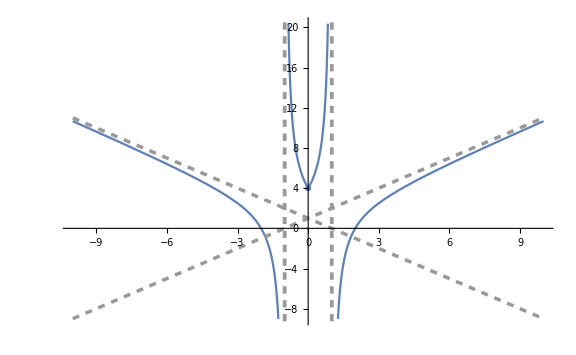
-Graphics-
Equation | Discontinuity | Asymptotes
(-4+RealAbs[x]^2)/(-1+RealAbs[x]) | {{x==-1},{x==1}} | <|Vertical→{{y→±∞,x→±1}},Oblique→{{y→1-x,x→-∞},{y→1+x,x→∞}}|>

```mathematica
EnhancedPlotB[{(x(RealAbs[x]^2-4))/(x(RealAbs[x]-1))},{x,-10,10}]
```

#### TrigExpansion

```mathematica
TrigExpansion[eq_,dom_:1]:=Grid[Transpose[{If[dom===1,{"FullSimplifyNormal","TrigExpand","TrigFactor","TrigReduce"},{"FullSimplifyDomain","FullSimplifyNormal","TrigExpand","TrigFactor","TrigReduce","PowerExpand"}],If[dom===1,#,Prepend[Append[#,PowerExpand[eq,Assumptions->dom]],
FullSimplify[eq,dom]]]&[Through[{FullSimplify,TrigExpand,TrigFactor,TrigReduce}[eq]]]}],Frame->All]
```

```mathematica
TrigExpansion::usage="TrigExpansion[eq,optional_dom_inequality]"
```

#### endpoints

```mathematica
Endpoints::usage="Endpoints[eq,var]"
```

```mathematica
Endpoints[eq_,var_:x]:={#,eq/.x->#}&/@Flatten[RegionBounds@ImplicitRegion[#,var]&/@{FunctionDomain[eq,var]}]
```

```mathematica
Endpoints[Log[x],x]
```

{{0,-∞},{∞,∞}}

#### plotpoint

```mathematica
PlotPoint::usage="PlotPoint[eq_list,dom_wx,ran_plotrange]";
```

```mathematica
PlotPoint[eq_,dom_,ran_:1]:=Show[{If[ran===1,Plot[eq,dom],Plot[eq,dom,ran]],ListPlot[Tooltip[Flatten[{Endpoints[#,dom[[1]]],{dom[[1]],#}/.Solve[#==0,dom[[1]]]}&/@eq,2]]]}]
```

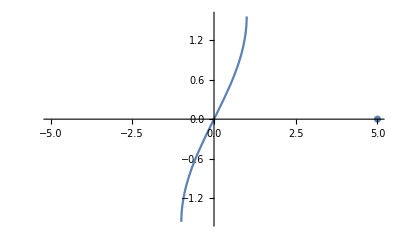

```mathematica
PlotPoint[ArcSin[x],{x,-5,5}]
```

### complex

#### principal

```mathematica
principal[ang_]:=Module[{a},a=Which[-π<ang<=π,Echo[0];ang,-π<2π+ang<=π,Echo[2π];2π+ang,-π<ang-2π<=π,Echo[-2π];ang-2π];Echo[Grid[{{"form","value","N"},{"original",Row[{"radian: ",ang}],Row[{"degree: ",degree@N@ang}]},{"degree",a//degree,a//degree//N},{"radian",a,a//N}},Frame->All]];a]
```

#### ArgPlot

```mathematica
ArgPlot[eq_]:=Module[{roots,pts,args},roots=z/. Solve[eq,z];
pts={Re[#],Im[#]}&/@roots;
args=Arg/@Cases[roots,_?(Im[N[#]]!=0&)];

Module[{pr=1.25,radius={1/4,3/8}},Graphics[{Thick,Arrow[{{-pr,0},{pr,0}}],Arrow[{{0,-pr},{0,pr}}],Text[Style[Subscript[z,0],18,Bold],pts[[1]],{0,-2}],Text[Style[Subscript[z,1],18,Bold],pts[[3]],{0,-2}],Text[Style[Subscript[z,2],18,Bold],pts[[2]],{0,2}],{Circle[{0,0},#[[1]],{0,#[[2]]}],Text[Style[#[[2]],14,Bold],#[[1]]*Through[{Cos,Sin}[#[[2]]/2]],{-1.25,-Sign[#[[2]]]}]}&/@Transpose[{radius,args}],AbsolutePointSize[10],Point[pts],AbsoluteDashing[{10,10}],Line[{{0,0},#}]&/@pts},Axes->True,Ticks->{Range[-1,1,1/2],Range[-1,1,1]},TicksStyle->Directive["Label",14],PlotRange->{{-pr,pr},{-pr,pr}},AxesLabel->(Style[#,14,Bold]&/@{Re,Im})]]]
```

#### DenomConj

```mathematica
DenomConj::usage="ConjDenom[eq_x_y]"
```

```mathematica
DenomConj[eq_]:=Module[{new,den=Denominator[eq],num=Numerator[eq],conj},conj=Echo[ComplexExpand[Conjugate[den]],"Conjugate"]; 
Echo[Grid[{{"(",num,")","(",conj,")"},{"(",den,")","(",conj,")"}},Dividers->{{False},{False,True,False}}],"Conjugate Multiply"];
new=Echo[ComplexExpand@{num conj,den conj},"{Num,Denom}"];{Re[new[[1]]]/new[[2]],Im[new[[1]]]/new[[2]]}//ComplexExpand//FullSimplify]
```

#### complot

```mathematica
ComPlot[eq_]:=Module[{a,eq1,trans},
If[Length@Variables[First[eq]]===0,eq1=Last[eq]==First[eq],eq1=eq];
If[Length[First[eq1]//First]!=2,trans={0,0},trans=ReIm@First@First@First[eq1]];
Show[{ContourPlot[(x+trans[[1]])^2+(y+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,{x,-5,5},{y,-5,5},ContourStyle->Dashed],ListPlot[Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[eq,z],PlotMarkers->{Automatic, 7}]}]]
```

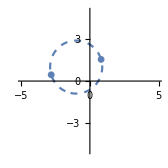

```mathematica
ComPlot[(z-I+1)^2==3+2I]
```

#### rt

```mathematica
rt::usage="rt[num,power]"
```

```mathematica
rt[num_,power_]:=num^(1/power)
```

#### CircleForm

```mathematica
CircleForm::usage="CircleForm[equation_no_y]"
```

```mathematica
CircleForm[eq_]:=Block[{cof=Echo[Coefficient[eq,#,2]&/@Variables[eq],"Coefficients"]},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Echo[Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]]][[1]][[1]]
```

```mathematica
(x-1)^2+(y+1)^2-1//Expand
```

```mathematica
CircleForm[1-2 x+3 x^2+2 y+3 y^2]
```

Coefficients  {3,3}

{{(-1/3+x)^2+(1/3+y)^2==-1/9,(-1/3+x)^2+(1/3+y)^2==-1/9},{True,True}}

(-1/3+x)^2+(1/3+y)^2==-1/9

#### complex linear

```mathematica
ComplexLinear[{x1_,y1_}]:=spdPlot[EchoFunction[Endpoints][ConditionalExpression[Echo@Module[{abs=Abs[x1+y1 I],grad=y1/x1},grad x+y1-grad x1],x>=x1]]]
```

#### ToCartesian

```mathematica
ToCartesian::usage="ToCartesian[eq]"
```

```mathematica
ToCartesian[eq_]:=ComplexExpand[eq/.z->x+y I]
```

#### ToCircle

```mathematica
ToCircle::usage="ToCircle[eq]"
```

```mathematica
ToCircle[eq_]:=Module[{cart=ToCartesian[eq]},CircleForm[(First[cart])^2-(Last[cart])^(1/2)]]
```

#### ComplexFactor

```mathematica
ComplexFactor[eq_]:=ComplexExpand[eq,TargetFunctions->{Re, Im}]
```

### Badplot

#### Badplotv2

```mathematica
SetAttributes[Badplot2,HoldFirst]
```

```mathematica
Options[Badplot2]=Join[Options[ContourPlot],{"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,PlotPoints->50}];
Badplot2[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},opts:OptionsPattern[]]:=TimeConstrained[Quiet@Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},
complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints={Flatten[Complement[Endpoints[ConditionalExpression[SolveValues[#,ran[[1]]][[1]][[1]],SolveValues[#,ran[[1]]][[2]]]],{{-∞,-∞},{-∞,∞},{∞,-∞},{∞,∞}}]&/@Select[{eqint},Not[{Exponent[First[#],dom[[1]]]+Exponent[Last[#],dom[[1]]],Exponent[First[#],ran[[1]]]+Exponent[Last[#],ran[[1]]]}==={2,2}]&],1]}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,Evaluate[FilterRules[{opts},Options[ContourPlot]]],PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->OptionValue[PlotPoints]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Echo@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

#### bad18

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";
```

```mathematica
Options[Badplot]=Join[Options[ContourPlot],{"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,PlotPoints->50}];
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},opts:OptionsPattern[]]:=TimeConstrained[Quiet@Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},
complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[2]],dom[[3]],dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]],endpoints={}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,Evaluate[FilterRules[{opts},Options[ContourPlot]]],PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->OptionValue[PlotPoints]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

```mathematica
SetAttributes[Badplot,HoldFirst]
```

#### bad17

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,"PlotPoints"->50};
Badplot[eqint__,dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[2]],dom[[3]],dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]],endpoints={}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->OptionValue["PlotPoints"]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

#### bad16

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,"PlotPoints"->50};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]],endpoints={}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->OptionValue["PlotPoints"]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
```

#### bad14

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Echo@Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### Bad 13

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";
```

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

```mathematica
SetAttributes[Badplot,HoldFirst]
```

#### bad12

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];Print[eq];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[IP,ihp],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### bad11

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];Print[eq];
Show[{
ContourPlot[{eqint},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[IP,ihp],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### bad10

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},

complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[#]-Last[#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[{eqint},Variables[First[#]-Last[#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[Evaluate[{eq}],dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[IP,ihp],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### bad9

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP},
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],
Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[IP,ihp],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### bad8

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True,"Time"->7};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"]},
If[OptionValue["N"],graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts={#,0}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
yintercepts={0,#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],7]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],
Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],22]
```

#### bad7

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";

Endpoints[eq_,var_:x]:={#,eq/.x->#}&/@Flatten[RegionBounds@ImplicitRegion[#,var]&/@{FunctionDomain[eq,var]}]

CircleForm[eq_]:=Block[{cof=Echo[Coefficient[eq,#,2]&/@Variables[eq],"Coefficients"],x,h,k,y,r},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Echo[Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]]][[1]][[1]];

Clear[Asymptotes]
Asymptotes[ args___ ] := 
    Module[ { res },
        res = Symbol[ "ResourceFunctionHelpers`Asymptotes" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`Asymptotes" ]
    ];
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10],
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10],
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],
Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],20]
SetAttributes[Badplot,HoldFirst];
```

#### bad6

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10],
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10],
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],10]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[#]!=2&/@z,##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],
Sequence@@If[OptionValue["N"],
{
ListPlot[Tooltip@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Tooltip@N@DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Tooltip@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Tooltip@DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],
If[OptionValue["TP"],ListPlot[Tooltip[Join[Tp,hp]],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],20]
```

#### badlpot5

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";

Endpoints[eq_,var_:x]:={#,eq/.x->#}&/@Flatten[RegionBounds@ImplicitRegion[#,var]&/@{FunctionDomain[eq,var]}]

CircleForm[eq_]:=Block[{cof=Echo[Coefficient[eq,#,2]&/@Variables[eq],"Coefficients"],x,h,k,y,r},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Echo[Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]]][[1]][[1]];

Clear[Asymptotes]
Asymptotes[ args___ ] := 
    Module[ { res },
        res = Symbol[ "ResourceFunctionHelpers`Asymptotes" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`Asymptotes" ]
    ];

Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[#]!=2&/@z,##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,PlotPoints->50],
Sequence@@If[OptionValue["N"],
{
ListPlot[Tooltip@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
},
{
ListPlot[Tooltip@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],
If[OptionValue["TP"],ListPlot[Tooltip[Join[Tp,hp]],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],20];
SetAttributes[Badplot,HoldFirst];
```

#### badplot 4

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][x]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic],
Sequence@@If[OptionValue["N"],
{
ListPlot[Tooltip@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
},
{
ListPlot[Tooltip@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["N"],If[OptionValue["Asymptote"]&&Length[N@Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[Evaluate[Join[If[Length[VAsymp]!=0||Length[C1Asymp]!=0,dom[[1]]==#&/@DeleteDuplicates[N@Join[VAsymp,C1Asymp]],##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,ran[[1]]==#&/@N[Join[HAsymp,OAsymp]],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
,If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[Evaluate[Join[If[Length[VAsymp]!=0||Length[C1Asymp]!=0,dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,ran[[1]]==#&/@Join[HAsymp,OAsymp],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]

],

If[OptionValue["TP"],ListPlot[Tooltip[Join[Tp,hp]],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],20]
```

#### badplot newest

```mathematica
Options[Badplot]={"Asymptote"->True,"N"->False,"TP"->True};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][x][y]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][x]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic],
Sequence@@If[OptionValue["N"],
{
ListPlot[Tooltip@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@N@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
},
{
ListPlot[Tooltip@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@graphintercepts,PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Tooltip@DeleteDuplicates[Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],PlotStyle->{Red},PlotMarkers->{Automatic,5}]
}
]
,
If[OptionValue["N"],If[OptionValue["Asymptote"]&&Length[Echo[N@Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp],"ASymp"]]!=0,
ContourPlot[Evaluate[Join[If[Length[VAsymp]!=0&&Length[C1Asymp]!=0,x==#&/@DeleteDuplicates[N@Join[VAsymp,C1Asymp]],##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,ran[[1]]==#&/@N[Join[HAsymp,OAsymp]],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
,If[OptionValue["Asymptote"]&&Length[Echo[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp],"ASymp"]]!=0,
ContourPlot[Evaluate[Join[If[Length[VAsymp]!=0&&Length[C1Asymp]!=0,x==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,ran[[1]]==#&/@Join[HAsymp,OAsymp],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]

],

If[OptionValue["TP"],ListPlot[Tooltip[Echo[Join[Tp,hp],"TP"]],PlotStyle->{Purple},PlotMarkers->{Automatic,5}],##&[]]
}]],20]
```

#### Badplot new

```mathematica
Options[Badplot]={"Asymptote"->False,"N"->False,"TP"->False};
```

```mathematica
Options[Badplot]={"Asymptote"->False,"N"->False,"TP"->False};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][x][y]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][x]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];,
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
Print[VAsymp];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[NSolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1],
Tp=
Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Length[z]!=2,##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]]

];
Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic],

ListPlot[Tooltip@Echo[If[OptionValue["N"],N@DeleteDuplicates@Join[Sequence@@graphintercepts,Sequence@@xintercepts,Sequence@@yintercepts,midpoints,Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],DeleteDuplicates@Join[Sequence@@graphintercepts,Sequence@@xintercepts,Sequence@@yintercepts,midpoints,Flatten@@@Select[endpoints,UnsameQ[#,{}]&]]],"INT"],PlotStyle->{Black}],

If[OptionValue["Asymptote"]&&Length[Echo@Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[Evaluate[Join[If[Length[Echo@VAsymp]!=0&&Length[C1Asymp]!=0,x==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],##&[]],
If[Length[Join[HAsymp,OAsymp]]!=0,y==#&/@Join[HAsymp,OAsymp],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]],

If[OptionValue["TP"],ListPlot[Tooltip[Echo[Join[Tp,hp],"TP"]],PlotStyle->{Purple}],##&[]]
}]],20]
```

#### Bad Plot

```mathematica
Badplot::usage="Badplot[{eq__},{x,min,max},{y,min,max}]";
```

```mathematica
Options[Badplot]={"Asymptote"->False,"N"->False};
Badplot[{eq__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},OptionsPattern[]]:=TimeConstrained[Module[{pairs=Subsets[{eq},{2}],graphintercepts,xintercepts,yintercepts,endpoints,midpoints,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp},

graphintercepts=Select[Normal@Table[
CheckAbort[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],10],
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];

xintercepts={#,0}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

yintercepts={0,#}&/@#&/@Select[Normal@Table[
CheckAbort[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10],
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0},ran[[1]],Reals],{0}],10]],
{i,{eq}}],UnsameQ[#,{}]&];

endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@Endpoints[#,dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[Asymptotes,{3,1,2}][x][y]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[asymp[[1]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][x]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[asymp[[2]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[asymp[[3]]//Flatten/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][y]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}
],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];

Show[{
ContourPlot[{eq},dom,ran,PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic],

ListPlot[Tooltip@If[OptionValue["N"],N@DeleteDuplicates@Join[Sequence@@graphintercepts,Sequence@@xintercepts,Sequence@@yintercepts,midpoints,Flatten@@@Select[endpoints,UnsameQ[#,{}]&]],DeleteDuplicates@Join[Sequence@@graphintercepts,Sequence@@xintercepts,Sequence@@yintercepts,midpoints,Flatten@@@Select[endpoints,UnsameQ[#,{}]&]]],PlotStyle->{Red}],

If[OptionValue["Asymptote"]&&Length[Echo@Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[Evaluate[Join[If[Length[VAsymp]!=0&&Length[C1Asymp]!=0,x==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,y==#&/@Join[HAsymp,OAsymp],##&[]]]],dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],20]
```

```mathematica
SetAttributes[Badplot,HoldFirst]
```

#### Inflectionpoints

```mathematica
InflectionPoints::usage="InflectionPoints[eq,x]"
```

```mathematica
InflectionPoints // ClearAll;
InflectionPoints[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`InflectionPoints" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`InflectionPoints" ]
    ];
```

### Logic

#### TruthTable

```mathematica
TruthTable::usage="TruthTable[statements,vars]";
```

TruthTable[statements,vars]

```mathematica
TruthTable // ClearAll;
TruthTable // Attributes = {};
TruthTable[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`TruthTable" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`TruthTable" ]
    ];
```

```mathematica
(*-Graphics--Graphics-*)
```

## Matrices

### transformation

#### Function

```mathematica
(*r=RotationTransform[π] RotationTransform ScalingTransform,ReflectionTransform,SheeringTransform,FindGeometricTransform*)
```

```mathematica
(*r[{x,y}]*)
```

#### cmatrices

```mathematica
(*cmatrices[a_,b_,c_,d_,e_,f_]:=Row[{MatrixForm[({{a, b}, {c, d}})],MatrixForm[({{x}, {y}})],MatrixForm[({{e}, {f}})]}]*)
```

#### cmatricesfull

```mathematica
cmatricesfull::usage="cmatricesfull[equation_,a_,b_,c_,d_,e_,f_]";
```

```mathematica
(*cmatricesfull[equation_,a_,b_,c_,d_,e_,f_]:=Module[{xpyp,newequation},xpyp=Solve[({{a, b}, {c, d}}).({{x}, {y}})+({{e}, {f}})==({{xp}, {yp}}),{x,y}];newequation=Solve[equation/.xpyp,yp]//Expand;Print[xpyp];Print[newequation]]*)
cmatricesfull[equation_,a_,b_,c_,d_,e_,f_]:=Module[{xpyp,newequation},Echo[Solve[({{a, b}, {c, d}}).({{x}, {y}})+({{e}, {f}})==({{xp}, {yp}}),{xp,yp}],"Step 1 expand:"];xpyp=Echo[Solve[({{a, b}, {c, d}}).({{x}, {y}})+({{e}, {f}})==({{xp}, {yp}}),{x,y}],"Step 2 rearrange:"];newequation=Solve[equation/.xpyp,yp]//Expand;Print[newequation/.xp->x/.yp->y]]
(*must be in form of y==x^2*)
```

#### cmatrices transform first

```mathematica
cmatricestransform::usage="cmatricestransform[equation_,a_,b_,c_,d_,e_,f_]";
```

```mathematica
cmatricestransform[equation_,a_,b_,c_,d_,e_,f_]:=Module[{xpyp,newequation},xpyp=Solve[({{a, b}, {c, d}}).(({{x}, {y}})+({{e}, {f}}))==({{xp}, {yp}}),{x,y}];newequation=Solve[equation/.xpyp,yp]//Expand;Print[xpyp];Print[newequation]]
```

#### cmatrices reverse

```mathematica
cmatricesreverse::usage="cmatricesreverse[equation_,a_,b_,c_,d_,e_,f_]
for when finding initial equation given final equation and transformations
f(x) goes through dilation of factor 2 from x and results in f'(x)=2x^2
find f(x)";
```

```mathematica
cmatricesreverse[equation_,a_,b_,c_,d_,e_,f_]:=Module[{xpyp,newequation},xpyp=Solve[({{a, b}, {c, d}}).({{xp}, {yp}})+({{e}, {f}})==({{x}, {y}}),{x,y}];newequation=Solve[equation/.xpyp,yp]//Expand;Print[xpyp];Print[newequation]]
```

```mathematica
(*
for when finding initial equation given final equation and transformations
f(x) goes through dilation of factor 2 from x and results in f'(x)=2 x^2
find f(x)
*)
```

#### cmatrices transform reverse

```mathematica
cmatricestransformreverse::usage="cmatricestransformreverse[equation_,a_,b_,c_,d_,e_,f_]";
```

```mathematica
cmatricestransformreverse[equation_,a_,b_,c_,d_,e_,f_]:=Module[{xpyp,newequation},xpyp=Solve[({{a, b}, {c, d}}).(({{xp}, {yp}})+({{e}, {f}}))==({{x}, {y}}),{x,y}];newequation=Solve[equation/.xpyp,yp]//Expand;Print[xpyp];Print[newequation]]
```

#### cmatrices find

```mathematica
cmatricesfind::usage="cmatricesfind[baseEQ_,transformedEQ_,a_,b_,c_,d_,e_,f_,solutions]"
```

cmatricesfind[baseEQ_,transformedEQ_,a_,b_,c_,d_,e_,f_,solutions]

```mathematica
cmatricesfind[baseEQ_,transformedEQ_,a_,b_,c_,d_,e_,f_,solutions__:1]:=FindInstance[EchoFunction[SolveAlways[#,xp]&][SolveValues[baseEQ==y/.Solve[({{a, b}, {c, d}}).({{x}, {y}})+({{e}, {f}})==({{xp}, {yp}}),{x,y}],yp][[1]]==ReplaceAll[transformedEQ,x->xp]],Join[Intersection[Variables[{a,b,c,d,e,f}],{a,b,c,d,e,f}],{xp}],solutions]
```

#### matrix inverse

```mathematica
matrixinverse[a_,b_,c_,d_]:=Module[{t},Print[Row[{
"Step One: ",MatrixForm[({{a, b}, {c, d}})],MatrixForm[({{x, y}, {u, v}})],"=",MatrixForm[({{1, 0}, {0, 1}})],"\n",
"Step Two: ",MatrixForm[({{a x+ b u, a y+b v}, {c x+d u, c y+d v}})],"==",MatrixForm[({{1, 0}, {0, 1}})],"\n",
"Step Three: ","\n",a x+b u,"=1","\n",
a x+ b u,"=1","\n", 
a y+ b v,"=0","\n", 
c x+ d u,"=0","\n",
 c y+ d v,"=1","\n",
"\n","Step Four: ",
t=Solve[{a x+ b u==1,a y+ b v==0, c x+ d u==0,c y+ d v==1},{x,y,u,v}],Print[t],"\n",MatrixForm[({{x, y}, {u, v}})]/.t
}]]]
```

```mathematica
(*-Graphics-*)
```

```mathematica
matrixinversevariablesolve[a_,b_,c_,d_,a2_,b2_,c2_,d2_]:=Module[{det,final},det=Det[{{a,b},{c,d}}];Print[Row[{"Determinant: ",a,"*",c,"*","-(",b,"*",d,")"}]];Print[Row[{1/det,MatrixForm[{{a,b},{c,d}}],"X = ",1/det,MatrixForm[{{a2,b2},{c2,d2}}]}]];
Print[Row[{"X = ",1/det,MatrixForm[{{a2,b2},{c2,d2}}]}]];
final=Solve[({{a, b}, {c, d}}). ({{a1, b1}, {c1, d1}})==({{a2, b2}, {c2, d2}}),{a1,b1,c1,d1}];Print[Row[{"X = ",MatrixForm[({{a1, b1}, {c1, d1}})]/.final}]];
Print[MatrixForm[LinearSolve[{{a,b},{c,d}},{{a2,b2},{c2,d2}}]]]
]
```

```mathematica
(*matrixinversevariablesolve[5,2,2,1,9,12,4,5]*)
```

#### linear reflection matrix

```mathematica
linearreflection[m_]:=MatrixForm[({{(1-m^2)/(m^2+1), 2 m/(m^2+1)}, {2 m/(m^2+1), (m^2-1)/(m^2+1)}})]
```

```mathematica
(*reflect in line*)
```

```mathematica
(*linearreflection[-1]*)
```

#### matrics for rotation and linear reflection

```mathematica
rotatematrix:=MatrixForm[({{Cos[x], -Sin[x]}, {Sin[x], Cos[x]}})]
```

```mathematica
linearreflectionmatrix:=MatrixForm[({{Cos[x], Sin[x]}, {Sin[x], -Cos[x]}})]
```

## Bound

### Mathematica Functions

#### function Injective

```mathematica
(*
FunctionInjective is 1 to 1 


FunctionBijective is 1 to 1 for all y values having its own x value
FunctionSurjective is NOT 1 to 1for all y values having at least one x value 
*)
```

```mathematica
guide/FunctionProperties
```

guide/FunctionProperties

```mathematica
Reduce[FunctionInjective[ConditionalExpression[16/(x-21)-q/(x+2)+10,0<=x<=18&&q>0],x][[2]]]
```

0<q≤64/441||q≥6400/9

-Graphics-

-Graphics-

-Graphics-

```mathematica
FunctionInjective[x^2,x]
```

False

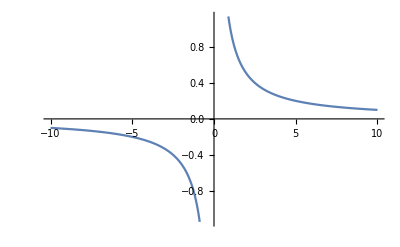

```mathematica
Plot[1/x,{x,-10,10}]
```

#### FunctionMonotonicity

-Graphics-

```mathematica
FunctionMonotonicity[x,x]
```

1

#### Function Sign

-Graphics-

```mathematica
FunctionSign[-1,x]
```

-1

#### Seperate integer into factors

```mathematica
IntegerPartitions[13,2,{2,3,4,5,6,7,8}]
```

{{8,5},{7,6}}

#### Piecewise

```mathematica
(*Plot[Piecewise[{{2x+3,x≤-1},{x^2,-1<x≤2},{√(x-2),x>2}}],{x,-5,5}]*)
```

To find domain of composite:
find the domain of outer, range of inner
make range of router be subset of domain of outer
do this by solving for x when it is equal

#### findroot

```mathematica
(*FindRoot[{f[x],g[x]},{{x,π},{y,0}}]*)
```

#### show

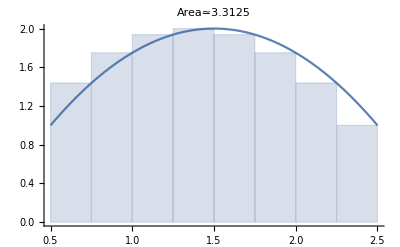
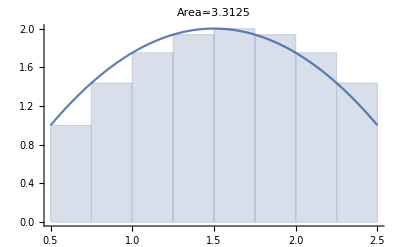
```mathematica
(*Show[{-Graphics-,-Graphics-,Plot[{2-2^(2x-1),2-2^(5-2x),1,7/16},{x,0.5,2.5}]},PlotRange->{0,3},GridLines->{{1/4},{1/4}}]*)
```

#### Integrate 1/x

```mathematica
Integrate[1/(x-2)+2,{x,-1,1},PrincipalValue->True]
```

4-Log[3]

#### outputting answers

```mathematica
1892341328794812370841324.0//ScientificForm
```

1.892341328794812370841324×10^24

```mathematica
"1.892341328794812370841324"×10^("24")//DecimalForm
```

1892341328794812370841324.

```mathematica
N[22/7,20]
```

3.1428571428571428571

```mathematica
NSolve[7x==22,x,Reals,30]
```

{{x→3.14285714285714285714285714286}}

#### Collect

```mathematica
Collect[b x^2+5x+7x^2+9a x+2,x]
```

2+(5+9 a) x+(7+b) x^2

### DiscretePlot

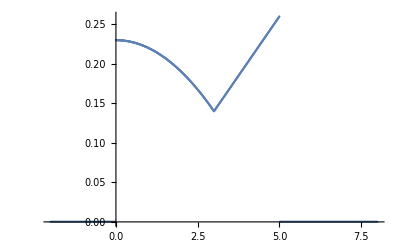

```mathematica
DiscretePlot[Piecewise[{{-1/100(x^2-23),0<=x<=3},{3/50x-1/25,3<x<=5}}],{x,-2,8,0.01},Filling->None]
```

### UsingDice roll/probability

```mathematica
NormalCI[1,2,ConfidenceLevel->0.95]
```

NormalCI[1,2,ConfidenceLevel→0.95]

\[Distributed]: esc dist esc
\[Conditioned] esc cond esc
Empirical dis: weights --> random variable

```mathematica
Grid[MapThread[Prepend,{Prepend[Table[

Cases[{{a,b,Style[Total[{a,b}],Red,Bold]}},

{_,_,Style[5,Red,Bold]}

],{a,{1,2,3,4,5,6}},{b,{1,2,3,4,5,6}}],{1,2,3,4,5,6}],{"",1,2,3,4,5,6}}],Frame->All]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | {} | {} | {} | {{1,4,5}} | {} | {}
2 | {} | {} | {{2,3,5}} | {} | {} | {}
3 | {} | {{3,2,5}} | {} | {} | {} | {}
4 | {{4,1,5}} | {} | {} | {} | {} | {}
5 | {} | {} | {} | {} | {} | {}
6 | {} | {} | {} | {} | {} | {}

```mathematica
Grid[MapThread[Prepend,{Prepend[Table[{a,b,Style[Total[{a,b}],Red,Bold]},{a,{1,2,3,4,5,6}},{b,{1,2,3,4,5,6}}],{1,2,3,4,5,6}],{"",1,2,3,4,5,6}}],Frame->All]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | {1,1,2} | {1,2,3} | {1,3,4} | {1,4,5} | {1,5,6} | {1,6,7}
2 | {2,1,3} | {2,2,4} | {2,3,5} | {2,4,6} | {2,5,7} | {2,6,8}
3 | {3,1,4} | {3,2,5} | {3,3,6} | {3,4,7} | {3,5,8} | {3,6,9}
4 | {4,1,5} | {4,2,6} | {4,3,7} | {4,4,8} | {4,5,9} | {4,6,10}
5 | {5,1,6} | {5,2,7} | {5,3,8} | {5,4,9} | {5,5,10} | {5,6,11}
6 | {6,1,7} | {6,2,8} | {6,3,9} | {6,4,10} | {6,5,11} | {6,6,12}

```mathematica
TableForm[Table[{{a,b,Style[Total[{a,b}],Red,Bold]}},{a,{1,2,3,4,5,6}},{b,{1,2,3,4,5,6}}],TableHeadings->{{1,2,3,4,5,6},{1,2,3,4,5,6}}]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 1 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 4 | 1 | 4 | 5 | 1 | 5 | 6 | 1 | 6 | 7
2 | 2 | 1 | 3 | 2 | 2 | 4 | 2 | 3 | 5 | 2 | 4 | 6 | 2 | 5 | 7 | 2 | 6 | 8
3 | 3 | 1 | 4 | 3 | 2 | 5 | 3 | 3 | 6 | 3 | 4 | 7 | 3 | 5 | 8 | 3 | 6 | 9
4 | 4 | 1 | 5 | 4 | 2 | 6 | 4 | 3 | 7 | 4 | 4 | 8 | 4 | 5 | 9 | 4 | 6 | 10
5 | 5 | 1 | 6 | 5 | 2 | 7 | 5 | 3 | 8 | 5 | 4 | 9 | 5 | 5 | 10 | 5 | 6 | 11
6 | 6 | 1 | 7 | 6 | 2 | 8 | 6 | 3 | 9 | 6 | 4 | 10 | 6 | 5 | 11 | 6 | 6 | 12

```mathematica
(*combiantions with duplicates*)
DeleteDuplicates[Map[Sort,Tuples[{5,10,20},2]]]
```

{{5,5},{5,10},{5,20},{10,10},{10,20},{20,20}}

```mathematica
(*combinations no duplicates*)
Subsets[{5,10,20},{2}]
(*combinations of lists up to 2 with no duplicates*)
Subsets[{5,10,20},2]
```

{{5,10},{5,20},{10,20}}

{{},{5},{10},{20},{5,10},{5,20},{10,20}}

```mathematica
(*Apply total to every list*)
Total/@{{5},{10},{20},{5,10},{5,20},{10,5},{10,20},{20,5},{20,10}}//DeleteDuplicates//Sort
```

{5,10,15,20,25,30}

```mathematica
Expectation[x,x\[Distributed]EmpiricalDistribution[{0.1,0.3,0.3,0.3}->{1,3,5,7}]]
```

4.6

```mathematica
Variance[EmpiricalDistribution[{1/21,2/21,1/7,4/21,5/21,2/7}->{1,2,3,4,5,6}]]
```

20/9

```mathematica
Integrate[1/(((8 √6)/5)√(2π))E^(-1/2((x-16)/((8 √6)/5))^2),{x,25,∞}]

Integrate[StandardNormal[16,(8 √6)/5],{x,25,∞}]
Integrate[PDF[NormalDistribution[16,(8 √6)/5],x],{x,25,∞}]
```

1/2 Erfc[(15 √3)/16]

Integrate::idiv: Integral of StandardNormal[16,(8 √6)/5] does not converge on {25,∞}.

∫_25^∞ StandardNormal[16,(8 √6)/5]ⅆx

1/2 Erfc[(15 √3)/16]

-Graphics-

-Graphics-

### Using FormulaData

```mathematica
FormulaLookup["Momentum"]
```

{{MomentumRelativistic,KineticEnergy},{MomentumRelativistic,Velocity}}

```mathematica
FormulaData["OhmsLaw"]
```

V ElectricPotential==I ElectricCurrent R ElectricResistance

```mathematica
FormulaData["TriangleAreaSSS","QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
s | semiperimeter | Length | {LengthUnit,1}
a | first side length | Length | {LengthUnit,1}
b | second side length | Length | {LengthUnit,1}
c | third side length | Length | {LengthUnit,1}
A | area | Area | {LengthUnit,2}

```mathematica
WordDefinition["semiperimeter"]
```

Missing[UnknownWord]

```mathematica
FormulaData["TriangleAreaSSS",{"a"->Quantity[1,"Meters"],"b"->Quantity[1,"Meters"],"c"->Quantity[1,"Meters"]}]
```

s Length==150 cm&&A Area==(√3)/4 m^2

# Things

Template: shift ctrl k

```mathematica
updatee[a_]:=FE`CacheTemplateAndUsage[a]
```

```mathematica
updatee[a_]:=FE`CacheTemplateAndUsage[a]
updatee/@{"TotalDistance","pointtransform","PointTranslate","gradientamount","gradientpoint","CompleteSquare","CompleteTheSquare","asymptotepoint","asymptotepointsafe","LinearLine","SolveAlwaysSteps","IntervalTogether","FindInverse","InverseFunctionList","ImageInverse","InversePlot","NormalLine","TangentLine","NormalLinee","TangentLinee","FunctionParity","Asymptotes","StationaryPoints","Intercepts","CurveIntersection","LocalExtrema","RateOfChange","FunctionDifferentiability","IntegrateRange","IntegrateRangeMultiple","IntegrateRangeMultipleHard","IntegrateRangeFunction","IntegrateRangeHard","IntegrateRangeHardNotReal","IntegrateMethod","IndividualIntegral","AreaBetweenCurves","IntegralApproximationPlot","BinomialDist","EmpiricalDist","NormalDist","Expected","ExpectedGain","variance","permutations","PascalTriangleExtract","PascalTriangle","binomialworking","ProbabilityTable","binomialdistgraph","binomialdistgraphmultiple","StandardNormal","StandardProbability","FindNormal","ApproximateNormal","DiceRoll","SampleTable","FTestEnsure","FTest","RFTest","compositetest","CubicDiscriminantSolve","LinearSolutions","LinearSolutionsCheck","LinearSolutionsPrint","trianglearea","TrigTable","time","newtonsmethod","cmatricesfull","cmatricestransform","cmatricesreverse","cmatricestransformreverse","StandardSolveProbability","Confidence","ConfidenceInterval","ProbabilityDist","NormalCIAlan","RangeRestrict","AveragePiecewise","AverageValue","CompositeDomainRange","InverseFunctionTest","SampleTableTim","cmatricesfind","SignTable","Combinations","CombinationsIndividual","CombinationsIndividualGreater","EnhancedPlotB","TrigExpansion","Endpoints","CircleForm","Badplot","InflectionPoints","rt","SignTableInflections","DiscontinuityPoints","InequalitiesToIntervals","IntegrateByParts","VolumeRotate","Eula","SlopeFieldVector","SlopeField","EulaOutput","ProbabilityCost","ProbabilityMultiple","NormalCIWorking","Standardx"};
```

```mathematica
updatee/@{"EnhancedPlotB"};
```

```mathematica
Solve[x^2==3,x,MaxExtraConditions->All]
```

{{x→-√3},{x→√3}}

```mathematica
Solve[Dt[y^2==a^2x^3,x,Constants->{a}],Dt[y,x,Constants->{a}]]
```

{{Dt[y,x,Constants→{a}]→(3 a^2 x^2)/(2 y)}}

#### Complex

```mathematica
Factor[x^2+1,Extension->I]
```

(-ⅈ+x) (ⅈ+x)

```mathematica
AbsArg[1+I]
```

{√2,π/4}

```mathematica
ReIm[1+I]
```

```mathematica
ToPolarCoordinates@{1,1}
```

{√2,π/4}

```mathematica
FromPolarCoordinates[{√2,π/4}]
```

{1,1}

```mathematica
Solve[{z^3==I/.z->x+ y I,{x,y}∈Reals},{x,y}]
```

{{x→0,y→-1},{x→-(√3)/2,y→1/2},{x→(√3)/2,y→1/2}}

```mathematica
Limit[1/x,x->0,Direction->-1]
(*
-1:From right
1:From left
*)
```

```mathematica
Reduce[a+I b==zr+I zi&&Element[{a,b,zr,zi},Reals],zi]
```

(zr|b)∈ℝ&&a==zr&&zi==b

```mathematica
FindFile["ResourceFunctionHelpers`"]
```

C:\Users\ethan\AppData\Roaming\Mathematica\Paclets\Repository\ResourceFunctionHelpers-1.3.23\Kernel\init.wl

#### start

```mathematica
(*start*)
```

Conjugate: Reflect over x axis, (x , y) → (x,-y)
Multiply by I: Rotate counter-clockwise by π/2 , (x , y)  → (-y,x)
Multiply by I^2=-1: Reflect over x axis and y axis, (x , y) →(-x,-y)
Multiply by I^3=-I:(x , y) → (y,-x)
Multiply by I^4=-I: No change , (x , y) → (x,y)

```mathematica
<<EquationTrekker`
```

```mathematica
Conjugate[1+I]
```

1-ⅈ